Importing Dataset

Exporting all lists of URLS in the chronology page

```mathematica
dataset = Import["http://www-groups.dcs.st-and.ac.uk/history/Indexes/Full_Chron.html",{"Hyperlinks"}];
```

Selecting Links which have a specific pattern

```mathematica
dataset1 =Flatten[StringCases[dataset,"http://www-groups.dcs.st-and.ac.uk/history/Biographies/"~~__]];
```

Exporting the content of each link as text

```mathematica
dataset2 = Import[#,"Text"]&/@dataset1
```

## HTML Parser

```mathematica
TemplateApply;

$mapping=Reverse[Normal[Templating`HTML`PackagePrivate`$SafeHTMLEntities],{2}];

htmlToText[txt_String]:=StringReplace[txt,$mapping]
```

```mathematica
htmls= Map[htmlToText,dataset2]
```

## Exporting List of HTMLs

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jofre/Documents/GitHub/KateSummer2018S/StudentDeliverables

htmlBioList is a list of all the text files in each biography, with the special characters removed

```mathematica
htmlBioList = Import["C:\\Users\\tanha\\OneDrive\\Documents\\GitHub\\Summer2018\\StudentDeliverables\\htmlbiographies.mx"]
```

{6706,8997,7335,26071,13163,8342,2763,28923,20469,22478,15680,26396,25787}
 |  |  |  |

```mathematica
ClearAll[x];Clear[y];Clear[l]
```

```mathematica
fullNames =StringCases[htmlBioList,"<h1>"~~x__~~"</h1>"->x];
```

```mathematica
birthdate= Flatten/@StringCases[htmlBioList,"Born:<font color=\"green\"> "~~Shortest[y__]~~" in "~~Shortest[l__]~~"<br>":>{StringReplace[y,"about "-> ""],l}]
```

{{1680 BC,Egypt},{800 BC,India},{750 BC,India},2769,{26 July 1969,Moscow, Russia},{17 July 1975,Adelaide, South Australia, Australia},{3 May 1977,Tehran, Iran}}
 |  |  |  |

```mathematica
birthdate= Flatten/@StringCases[htmlBioList,"Born:<font color=\"green\"> "~~Shortest[y__]~~"<br>"-> y]
```

{{about 1680 BC in Egypt},{about 800 BC in India},{about 750 BC in India},{about 624 BC in Miletus, Asia Minor (now Turkey)},{611 BC in Miletus near Söke, Turkey},{about 600 BC in India},{about 569 BC in Samos, Ionia},{about 520 BC in Shalatula (near Attock), now Pakistan},{499 BC in Clazomenae (30 km west of Izmir), Lydia (now Turkey)},{about 492 BC in Acragas (now Agrigento, Sicily, Italy)},{about 490 BC in Chios (now Khios), Greece},{about 490 BC in Elea, Lucania (now southern Italy)},{480 BC in (possibly) Athens, Greece},{about 480 BC in (possibly) Miletus, Asia Minor},{about 470 BC in Chios (now Khios), Greece},{465 BC in Cyrene (now Shahhat, Libya)},{about 460 BC in Abdera, Thrace, Greece},{about 460 BC in Elis, Peloponnese, Greece},{about 450 BC in Tarentum, Heraclea (now Taranto, Italy)},{about 428 BC in Tarentum, Magna Graecia (now Taranto, Italy)},{427 BC in Athens, Greece},{about 417 BC in Athens, Greece},{408 BC in Cnidus (on Resadiye peninsula), Asia Minor (now Knidos, Turkey)},{about 400 BC in China},{about 400 BC in Paros, Greece},{396 BC in Chalcedon (now Kadiköy, near Istanbul), Bithynia (now Turkey)},{about 390 BC in Greece},{387 BC in Heraclea Pontica (now Eregli, Turkey)},{384 BC in Stagirus, Macedonia, Greece},{about 380 BC in Alopeconnesus, Asia Minor (now Turkey)},{about 370 BC in Greece},{about 370 BC in Cyzicus, Asia Minor (now Turkey)},{about 360 BC in Pitane, Aeolis, Asia Minor (now Turkey)},{about 350 BC in Rhodes, Greece},{about 325 BC},{about 310 BC in Greece},{287 BC in Syracuse, Sicily (now Italy)},{280 BC in Soli, Cilicia, Asia Minor (now Soloi, Turkey)},{about 280 BC in Samos},{about 280 BC in Greece},{about 280 BC in Byzantium (Turkey)},{276 BC in Cyrene, North Africa (now Shahhat, Libya)},{about 262 BC in Perga, Pamphylia, Greek Ionia (now Murtina, Antalya, Turkey)},{about 250 BC in Caunus, Caria, Asia Minor (now in Turkey)},{about 240 BC in Carystus (now Káristos), Euboea (now Evvoia), Greece},{about 200 BC in India},{about 200 BC in Athens, Greece},{190 BC in Nicaea (now Iznik), Bithynia (now Turkey)},{about 190 BC in Alexandria, Egypt},{2nd century BC},{about 160 BC in Bithynia, Anatolia (now Turkey)},{about 150 BC in Sidon (now Saida in Lebanon)},{135 BC in Apameia, near Shaizar, Syria},{about 130 BC in Southwest China},{about 85 BC in possibly Fundi, Campania (now Italy)},{about 10 BC in (possibly) Rhodes, Greece},{1st century AD in possibly Lysimachia, Hellespont, Greece},{about AD 10 in (possibly) Alexandria, Egypt},{about 60 in Gerasa, Roman Syria (now Jarash, Jordan)},{about 70 in (possibly) Alexandria, Egypt},{about AD 70 in Smyrna (now Izmir), Turkey},{AD 78 in Nan-yang, China},{about AD 85 in Egypt},{about 120 in Western India},{129 in Lo-yang, China},{about 160 in Donglai, Shandong province, China},{about 200},{about 220 in Wei, China},{233 in Tyre (now Sur, Lebanon)},{about 240 in (possibly) Nicaea (now Iznik), Bithynia (now Turkey)},{about 290 in Alexandria, Egypt},{about 300 in Alexandria, Egypt},{about 300 in Antinoupolis, Egypt},{about 335 in (possibly) Alexandria, Egypt},{about 370 in Alexandria, Egypt},{about 400 in China},{about 400 in China},{8 February 411 in Constantinople (now Istanbul), Byzantium (now Turkey)},{about 420 in Larissa (now Shaizar), Syria},{429 in Jiankang, (now Nanking, Kiangsu province), China},{about 430 in China},{about 450 in Neapolis, Palestine (called Shechem in Bible, now Nablus, Israel)},{about 450 in Jiankang, (now Nanking, Kiangsu province), China},{about 474 in (possibly) Tralles (near Aydin in southwest Turkey)},{476 in Kusumapura (now Patna), India},{about 480 in in or near Rome, Byzantine Empire (now Italy)},{about 480 in Ascalon (now Ashqelon), Israel},{about 490 in Cilicia, Anatolia (now Turkey)},{about 500 in India},{505 in Kapitthaka, India},{about 580 in China},{598 in (possibly) Ujjain, India},{about 600 in (possibly) Saurastra (modern Gujarat state), India},{602 in Shaanxi province, China},{about 720 in India},{735 in York, Yorkshire, England},{about 780 in possibly Baghdad (now in Iraq)},{about 800 in possibly Baghdad, Iraq},{about 800 in Baghdad, (now in Iraq)},{about 800 in Baghdad, Iraq},{about 800 in India},{about 800 in possibly Mysore, India},{about 801 in Kufa, Iraq},{about 805 in Baghdad, Iraq},{808 in Al-Hirah (now in Iraq)},{about 810 in Baghdad, Iraq},{about 820 in Mahan, Kerman, Persia (now Iran)},{about 830 in India},{835 in Baghdad (now in Iraq)},{836 in Harran, Mesopotamia (now Turkey)},{about 840 in India},{about 850 in (possibly) Egypt },{about 850 in Harran (near Urfa), Mesopotamia (now Turkey)},{about 870 in possibly Bengal, India},{about 865 in possibly Nayriz, Iran},{about 880},{about 900 in Khurasan (eastern Iran)},{908 in   Baghdad, (now in Iraq)},{about 920 in possibly Damascus, Syria},{about 920 in India},{},{about 940 in Khudzhand, Tajikistan},{about 940 in Tabaristan (now Mazanderan), Persia (now Iran)},{about 940 in Benares (now Varanasi), India},{about 945 in Sijistan, Persia (now Iran)},{946 in Belliac, Auvergne, France},{950 in Egypt},{13 April 953 in Baghdad (now in Iraq)},{965 in   (possibly) Basra, Persia (now Iraq) },{970 in (possibly) Khwarazm (now Kara-Kalpakskaya, Uzbekistan)},{971 in Gilan (now in Iran)},{15 September 973 in Kath, Khwarazm (now Kara-Kalpakskaya, Uzbekistan)},{about 980 in Baghdad, Iraq},{980 in Kharmaithen (near Bukhara), Central Asia (now Uzbekistan)},{989 in Cordoba, Andalusia (now Spain)},{about 1010 in possibly Nasa, Khurasan,Iran},{about 1010 in China},{18 July 1013 in Saulgau, Swabia, Germany},{1019 in (probably) Rohinikhanda, Maharashtra, India},{1031 in Hangzhou, Zhejiang province, China},{18 May 1048 in Nishapur, Persia (now Iran)},{about 1060 in (possibly) Mathura, India},{1070 in Barcelona (now Spain)},{1075 in Bath, England},{1089 in Dhandhuka, Gujarat, India},{1092 in Tudela, Emirate of Saragossa (now Spain)},{about 1100 in possibly Seville (now Spain)},{1114 in Vijayapura, India},{1114 in Cremona (now Italy)},{about 1130 in Baghdad, Iraq},{about 1135 in Tus, Khorasan (now Iran)},{about 1140 in Paderborn, Roman Empire, now Germany},{1168 in Suffolk, England},{1170 in (probably) Pisa (now Italy)},{about 1175 in (probably) Northern England/Southern Scotland },{1192 in Ta-hsing (now Peking), China},{about 1195 in (possibly) Halifax, Yorkshire, England},{about 1200 in Lauingen an der Donau, Swabia (now Germany)},{18 February 1201 in Tus, Khorasan (now Iran)},{1202 in Puzhou (Anyue), Szechwan province, China},{1214 in Ilchester, Somerset, England},{about 1220 in Spain},{1220 in Novara (now Italy)},{1225 in Borgentreich (near Warburg), Germany},{1231 in Xingtai, Hebei province, China},{1235 in Majorca (now Spain)},{1236 in Marseilles, Spain (now France)},{about 1238 in Qiantang (now Hangzhou), Chekiang province, China},{about 1250 in Samarqand, Uzbekistan},{29 December 1256 in Marrakesh, Morocco},{about 1260},{about 1260 in Yan-shan, near Peking, China},{26 July 1271 in Poyang, now Jiangxi province, China},{1288 in Bagnols now Bagnols sur Cèze, Provence, France},{about 1288 in Ockham (near Ripley, Surrey), England},{about 1295 in Chichester, England},{1316 in Rickensdorf, Helmstedt, Lower Saxony (now Germany)},{about 1320 in possibly Damascus, Syria},{1323 in Allemagne (west of Riez), France},{about 1340 in Western India},{about 1340 in India},{1350 in Sangamagramma (near Cochin), Kerala, India},{1364 in Bursa, Turkey},{about 1370 in Alattur, Kerala, India},{1377 in Florence (now Italy)},{about 1380 in Kashan, Iran},{1393 in Soltaniyeh, Timurid, Persia (now Iran)},{about 1400 in possibly Andalusia (now Spain)},{1401 in Kues, Trier (now Germany)},{18 February 1404 in Genoa, French Empire (now Italy)},{1412 in   Bastah (now Baza, Spain)},{June 1420 in Borgo San Sepolcro (now Sansepolcro, Italy)},{30 May 1423 in Peuerbach, Austria},{about 1424 in Venice, Venetian States (now Italy)},{6 June 1436 in Unfinden (near Königsberg), Lower Franconia (now in Bayern, Germany)},{14 June 1444 in Trkkantiyur (near Tirur), Kerala, India},{1445

 in Paris, France},{1445 in Sansepolcro (now Italy)},{15 April 1452 in Vinci, near Empolia  (now Italy)},{1462 in Eger, Bohemia (now Cheb, Czech Republic)},{6 February 1465 in Bologna (now Italy)},{14 February 1468 in Nuremberg, Germany},{1469 in Gleghornie (near Haddington), Scotland},{about 1470 in Lyon, France},{1471 in Soyecourt, near Amiens, Picardy, France},{21 May 1471

 in Imperial Free City of Nürnberg (now in Germany)},{19 February 1473 in Toru&#324;, Poland},{1474 in Hackforth, Yorkshire, England},{1480 in Palencia (now Spain)},{1487 in Sarinena, Aragon (now Spain)},{1487 in Esslingen, Germany},{23 December 1492 in Staffelstein (near Bamberg), Upper Franconia (now Germany)},{20 December 1494 in Briançon, France},{16 September 1494 in Messina, Kingdom of Sicily (now Italy)},{16 April 1495 in Leisnig, Saxony (now Germany)},{1499 in Jauer, Silesia (now Jawor, Poland)},{about 1500 in Kerala, India},{1500 in Brescia, Republic of Venice (now Italy)},{24 September 1501 in Pavia, Duchy of Milan (now Italy)},{1502 in Alcácer do Sal, Portugal},{1506 in Urbino (now Italy)},{8 December 1508 in Dokkum, Friesland, The Netherlands},{1510 in Tenby, Wales},{5 March 1512 in Rupelmonde, Burgundian Netherlands (now Belgium)},{16 February 1514 in Feldkirch, Austria},{1515 in Cuts (near Noyon), Vermandois, France},{2 February 1522 in Bologna, Papal States (now Italy)},{January 1526 in Bologna, Papal States (now Italy)},{13 July 1527 in Tower Ward, London, England},{14 August 1530 in Venice, Venetian States (now Italy)},{1533 in China},{1 November 1535 in Vico Equense near Naples (now Italy)},{April 1536 in Perugia (now Italy)},{9 August 1537 in Candia (now Iráklion), Crete},{25 March 1538 in Bamberg (now in Germany)},{21 December 1540 in Uttoxeter, Staffordshire, England},{28 January 1540 in Hildesheim, Germany},{1540 in Fontenay-le-Comte, Poitou (now Vendée), France},{11 January 1545 in Pesaro (now Italy)},{14 December 1546 in Knutstorp, Skane, Denmark (now Svalöv, Sweden},{1546 in Wootton, Kent, England},{1546 in Breslau, now Wroc&#322;aw, Poland},{27 February 1547 in Baalbek, now in Lebanon},{1548 in Nola near Naples (now Italy)},{15 April 1548 in Bologna, Papal States (now Italy)},{1548 in Bruges, Burgundian Netherlands (now Belgium)},{30 November 1549 in Bradley (near Halifax), Yorkshire, England},{30 September 1550 in Göppingen, Baden-Würtemberg, Germany},{1550 in Merchiston Castle, Edinburgh, Scotland},{28 February 1552 in Lichtensteig, St Gallen, Switzerland},{6 October 1552 in Macerata, Papal States (now Italy)},{1552 in Naples (now Italy)},{ 1553 in Lagos, Portugal},{1555 in Lisbon, Portugal},{13 June 1555 in Padua, Venetian States (now Italy)},{1560 in Oxford, England},{February 1561 in Warleywood, Yorkshire, England},{6 January 1561 in Flensburg, Schleswig (now Germany)},{25 August 1561 in Ghent, Spanish Netherlands (now Belgium)},{24 August 1561 in Grünberg, Bohemia (now Zielona Góra, Poland)},{29 September 1561 in Leuven, Spanish Netherlands (now Belgium)},{24 April 1562 in Shanghai, China},{15 February 1564 in Pisa (now  Italy)},{8 March 1566 in Bologna, Papal States (now Italy)},{2 October 1568 in Ragusa, Dalmatia (now Dubrovnik, Croatia)},{27 December 1571

 in Weil der Stadt, Württemberg, Holy Roman Empire (now Germany)},{20 January 1573 in Gunzenhausen, Bavaria, Germany},{25 July 1573 in Markt Wald, near Mindelheim in Swabia (now in Germany)},{5 March 1574 in Eton, Buckinghamshire, England},{12 June 1577 in St Gall (now Sankt Gallen), Switzerland},{1578 in Brescia (now Italy)},{5 May 1580 in Ulm, Germany},{1580 in France},{13 June 1580 in Leiden, Netherlands},{9 October 1581 in Bourg-en-Bresse, France},{1581 in Hertfordshire, England},{23 February 1583 in Villefranche, Beaujolais, France},{8 September 1584 in Bruges, Spanish Netherlands (now Belgium)},{19 August 1584 in Ornans, Franche-Comté, Spanish Habsburgs (now France)},{1585 in Paris, France},{1586 in London, England},{22 October 1587 in Lübeck, Holstein (now Germany)},{15 February 1588 in Felsberg, Germany},{5 April 1588 in Westport, Malmesbury, Wiltshire, England},{8 September 1588 in Oizé, Maine, France},{2 May 1588 in Clermont (now Clermont-Ferrand), Auvergne, France},{about 1590 in Paris, France},{21 February 1591

 in Lyon, France},{22 January 1592 in Champtercier, Provence, France},{22 April 1592 in Herrenberg (near Tübingen), Württemberg (now Germany)},{8 December 1594 in Montluçon, France},{1595 in St Mihiel, France},{31 March 1596 in La Haye (now Descartes),Touraine, France},{1596 in The Hague, Holland},{17 November 1597 in Aldersgate, London, England},{1 March 1597 in Antwerp, Dutch Republic (now Belgium)},{1598 in Milan, Duchy of Milan, Habsburg Empire (now Italy)},{1598 in Le Mans, France},{17 April 1598 in Ferrara (now Italy)},{1600 in Lyon, France},{1600 in London, England},{1600 in Gouda, Netherlands},{7 October 1601 in Blois, France},{17 August 1601 in Beaumont-de-Lomagne, France},{18 March 1602 in Compiègne, France},{1602 in Alresford, Hampshire, England},{9 August 1602 in Noël-Saint-Martin, Villeneuve-sur-Verberie, Oise, France},{about 1604 in Paris, France},{28 September 1605 in Loudun, France},{23 May 1606 in Madrid, Spain},{about 1607 in Schweidnitz, Silesia (now &#346;widnica, Poland)},{28 January 1608 in Naples (now Italy)},{8 April 1608 in Le Grand Abergement, Ain, France},{15 October 1608 in Faenza, Romagna (now Italy)},{1610 in Paris, France},{1610 in Rotterdam, Netherlands},{28 January 1611 in Danzig, now Gda&#324;sk, Poland},{1 March 1611 in Southwick, Sussex, England},{6 February 1612 in Paris, France},{23 June 1612 in Antwerp, Dutch Republic (now Belgium)},{October 1614 in Grantham, Lincolnshire, England},{1614 in Fawsley (4 km S of Daventry), Northamptonshire, England},{15 May 1615 in Leiden, Netherlands},{about 1616 in Benares (now Varanasi), India},{23 November 1616 in Ashford, Kent, England},{1 April 1617 in Aspenden, Hertfordshire, England},{2 April 1618 in Bologna, Papal States (now Italy)},{1618 in Toxteth, Liverpool, England},{1618 in Lyon, France},{1618 in Paris, France},{30 January 1619 in Rome (now Italy)},{1620 in Castlelyons (N of Cork), Ireland},{1620 in Eutin, Holstein, Holy Roman Empire (now Germany)},{21 July 1620 in La Flèche, France},{1621 in Chambéry, France},{28 January 1622 in Rouen, France},{10 March 1622 in Zürich, Switzerland},{2 July 1622 in Visé, Spanish Netherlands (now Belgium)},{5 April 1622 in Florence (now Italy)},{21 September 1623 in Venice, Venetian States (now Italy)},{19 June 1623 in Clermont (now Clermont-Ferrand), Auvergne, France},{5 March 1624 in Wood Eaton (4km north of Oxford), England},{1624 in Modena (now Italy)},{10 June 1625 in Apáca, Transylvania, Hungary (now Romania)},{13 August 1625 in Roskilde, Denmark},{8 June 1625 in Perinaldo, Republic of Genoa (now Italy)},{24 September 1625 in Dordrecht, Netherlands},{1626 in Bologna, Papal States (now Italy)},{25 January 1627 in Lismore, County Waterford, Ireland},{8 February 1627 in Whitelee, Pendle Forest, Lancashire, England},{23 April 1628 in Amsterdam, Netherlands},{14 April 1629 in The Hague, Netherlands},{October 1630 in London, England},{1630 in France},{1631 in England},{20 October 1632 in East Knoyle, Wiltshire, England},{1633 in Xuangcheng, now Xuanzhou City, Anhui province, China},{8 September 1634 in Haarlem, Netherlands},{18 July 1635 in Freshwater, Isle of Wight, England},{16 December 1637 in Bishopsthorpe (near York), England},{November 1638 in Drumoak (near Aberdeen), Scotland},{6 August 1638 in Paris, France},{18 March 1640 in Paris, France},{15 June 1640 in Le Mans, France},{1 April 1640 in Copenhagen, Denmark},{16 June 1640 in Sainte-Olive, Bresse, France},{March 1642 in Fujioka, Kozuke, Japan},{4 January 1643 in Woolsthorpe, Lincolnshire, England},{20 August 1645 in Mexico City, Mexico},{19 August 1646 in Denby (near Derby), Derbyshire, England},{1 July 1646 in Leipzig, Saxony (now Germany)},{1 September 1647 in Milan, Hapsburg Empire (now Italy)},{17 January 1647 in Danzig, now Gda&#324;sk, Poland},{22 August 1647 in Blois, France},{15 January 1648 in Westminster, London, England},{20 December 1648 in Milan, Hapsburg Empire (now Italy)},{10 April 1651 in Kieslingswalde (near Görlitz), Germany (now S&#322;awnikowice, Poland)},{9 April 1652 in Lisieux, France},{21 April 1652 in Ambert, Basse-Auvergne, France},{1653 in Little Horton, near Bradford, Yorkshire, England},{1654 in Caen, France},{6 January 1655 in Basel, Switzerland},{8 November 1656 in Haggerston, Shoreditch (near London), England},{17 April 1656 in Dublin, Ireland},{11 June 1656 in Brissac, Maine-et-Loire, France},{11 February 1657 in Rouen, France},{3 June 1659 in Aberdeen, Scotland},{1 September 1659 in Courthézon, Vaucluse, France},{7 November 1660 in Lyon, France},{},{26 July 1663 in Colfontaine, near Nangis, Brie, France},{1663 in Hoddam, Dumfries, Scotland},{1664 in Edo (now Tokyo), Japan},{April 1667 in Inverbervie, Kincardine, Scotland},{27 July 1667 in Basel, Switzerland},{26 May 1667 in Vitry-le-François, Champagne, France},{5 September 1667 in San Remo, Genoa (now Italy)},{9 December 1667 in Norton-juxta-Twycross, Leicestershire, England},{1668 in Pinner, Middlesex, England},{9 June 1669 in Ostashkov, Russia},{25 February 1670 in Panitzsch, near Leipzig, Germany},{1 October 1671 in Cremona (now Italy)},{1 December 1671 in Edinburgh, Scotland},{20 September 1674 in Bologna, Papal States (now Italy)},{11 October 1675 in Norwich, England},{1675 in Llanfihangel Tre'r Beirdd, Anglesey, Wales},{28 May 1676 in Venice, Venetian Republic (now Italy)},{8 February 1677 in Paris, France},{27 September 1677  in Nuremberg, Germany},{1677 in Tarascon, Bouches-du-Rhône, France},{1678 in England},{16 July 1678 in Basel, Switzerland},{27 October 1678 in Paris, France},{1680 in Lichfield, Staffordshire, England},{1680 in England},{25 March 1681 in Bologna, Papal States (now Italy)},{19 May 1681 in Xuangcheng, now Xuanzhou City, Anhui province, China},{10 July 1682 in Burbage, Leicestershire, England},{6 December 1682 in Sinigaglia (now Senigallia, Italy)},{16 April 1682 in Bloomsbury, London, England},{January 1682 in Thurlstone, Yorkshire, England},{23 August 1683 in Venice, Venetian States (now Italy)},{12 March 1685 in Kilkenny, County Kilkenny, Ireland},{18 August 1685 in Edmonton, Middlesex, England},{21 October 1687 in Basel, Switzerland},{14 October 1687 in West Kilbride, Ayrshire, Scotland},{15 November 1688 in Montpellier, France},{not known},{26 September 1688 in 'sHertogenbosch, Netherlands},{18 July 1689 in Chester, Cheshire, England},{18 March 1690 in Königsberg, Brandenburg-Prussia (now Kaliningrad, Russia)},{about 1690 in Amber (now Jaipur), India},{May 1692 in Garden (near Stirling), Scotland},{6 February 1695 in Basel, Switzerland},{16 February 1698 in Le Croisic, France},{ February 1698 in Kilmodan (12 km N of Tighnabruaich), Cowal, Argyllshire, Scotland},{28 September 1698 in Saint Malo, France},{25 August 1699 in Crécy-en-Brie (near Paris), France},{8 February 1700 in Groningen, Netherlands},{28 November 1700 in Bisley, Gloucester, England},{1700},{about 1700 in Inverary, Scotland},{14 May 1701 in Hurworth, near Darlington, England},{28 January 1701 in Paris, France},{1702 in London, England},{28 October 1703 in Clotet-de-Cessous, France},{15 January 1708 in Castiglione, Tuscany (now Italy)},{31 July 1704 in Geneva, Switzerland},{13 August 1704 in Claveyson, Drôme, France},{9 October 1704 in Pozsony, Hungary (now Bratislava, Slovakia)},{17 December 1706 in Paris, France},{17 January 1706 in Boston, Massachusetts, British colony},{7 September 1707 in Montbard, Côte d'Or, France},{15 April 1707 in Basel, Switzerland},{11 January 1707 in Castelfranco Veneto near Treviso (now Italy)},{1707 in Bath, England},{28 May 1710 in Basel, Switzerland},{1710 in West Africa},{20 August 1710 in Market Bosworth, Leicestershire, England},{31 October 1711 in Bologna, Papal States (now Italy)},{18 May 1711 in Ragusa, Dubrovnik Republic (now Dubrovnik, Croatia)},{31 July 1712 in Büdingen, Germany},{7 May 1713 in Paris, France},{17 June 1714 in Thury, near Clermont, Oise, France},{1714 in St Andrews, Scotland},{31 January 1715 in Sinigaglia (now Senigallia, Italy)},{},{15 January 1717 in Rothesay, Isle of Bute, Scotland},{16 May 1718 in Milan, Habsburg Empire (now Italy)},{1718 in Rimaszombat, Hungary (now Rimavská Sobota, Slovakia)},{27 September 1719 in Leipzig, Germany},{23 January 1719 in Peakirk (near Peterborough), England},{5 January 1723 in Paris, France},{17 February 1723 in Marbach, Württemberg, Germany},{23 February 1723 in Tyn-ton, Llangeinor, Glamorgan, Wales},{13 December 1724 in Rostock, Mecklenberg-Schwerin (now Germany)},{27 September 1725 in Kiltullagh near Athenry, County Galway, Ireland},{5 September 1725 in Lyon, France},{3 June 1726 in Edinburgh, Scotland},{13 April 1728 in Milan, Austrian Habsburg (now Italy)},{26 August 1728 in Mülhausen, Alsace (now Mulhouse, France)},{11 November 1729 in Paris, France},{31 March 1730 in Nemours, France},{11 August 1730 in Tartaras (near Rive de Gier), Rhône-et-Loire, France},{9 November 1731 in Baltimore, Maryland, USA},{26 September 1731 in Ala, Trento (now Italy)},{15 December 1731 in London, England},{1732 in Shiba, Edo (now Tokyo), Japan},{15 December 1732 in Neubrandenburg, Mecklenburg-Strelitz, Germany},{11 July 1732 in Bourg-en-Bresse, Ain, France},{5 October 1732 in Kensington Gore, London, England},{8 April 1732 in Paper Mill Run, near Germantown, Pennsylvania, USA},{4 May 1733 in Dax, France},{11 January 1734 in Paris, France},{25 June 1734 in Canaveses, Portugal},{18 October 1735 in Cerea (now Italy)},{15 October 1735 in Salterhebble, near Halifax, Yorkshire, England},{28 February 1735 in Paris, France},{19 August 1736 in Ausas, Kristianstad, Sweden},{14 June 1736 in Angoulême, France},{25 January 1736 in Turin, Sardinia-Piedmont (now Italy)},{16 September 1736 in Tetenbüll (near Tönning), South Schleswig (now Germany)},{1736 in Old Heath (near Shrewsbury), Shropshire, England},{14 August 1737 in Newcastle-upon-Tyne, England},{12 June 1737 in Ferryport-on-Tay, now Tayport, Scotland},{15 November 1738 in Hanover, Electorate of Holy Roman Empire (now Germany)},{19 August 1739 in Hamburg, Germany},{24 December 1740 in Äbo, Sweden (now Turku, Finland)},{13 July 1741 in Dresden, Germany},{6 August 1741 in Applethwaite, Westmoreland, England},{17 September 1743 in Ribemont, France},{4 November 1744 in Basel, Switzerland},{1744 in Lisbon, Portugal},{16 August 1744 in Laon, France},{October 1745 in Westminster, London, England},{8 June 1745 in Vestby (near Dröbak), Norway},{9 May 1746 in Beaune, Bourgogne, France},{23 June 1746 in Logie, near Montrose, Scotland},{10 February 1747 in  Yamagata, Japan},{30 June 1748 in Paris, France},{10 March 1748 in Benvie (near Dundee), Scotland},{19 April 1748 in Besançon, France},{19 September 1749 in Amiens, France},{1749 in North Tawton, Devon, England},{23 March 1749 in Beaumont-en-Auge, Normandy, France},{October 1750 in Leslie, Fife, Scotland},{16 March 1750 in Hannover, Hanover (now Germany)},{24 April 1750 in Geneva, Switzerland},{13 May 1750 in Bergamo, Lombardo-Veneto (now Italy)},{26 May 1750 in Bridgend, Wales},{29 December 1751 in Hardwick, Buckinghamshire, England},{18 September 1752 in Paris, France},{13 May 1753 in Nolay, Burgundy, France},{29 October 1753 in Naples, Kingdom of Naples (now Italy)},{22 November 1753 in Edinburgh, Scotland},{October 1753 in Corney, Cumberland, England},{2 December 1754 in Sézanne, Haute Marne, France},{23 March 1754 in Zagorica, Ljubljana, Austrian Empire (now Slovenia)},{22 July 1755 in Chamelet, Beaujolais, France},{30 January 1755 in Basel, Switzerland},{27 April 1755 in Rosières-aux-Salines, France},{10 April 1756 in Logie (near St Andrews), Scotland},{4 October 1759 in Mutzig, Alsace},{17 October 1759 in Basel, Switzerland},{2 March 1759 in Livorno (now Italy)},{8 July 1760 in Strasbourg, France},{ 28 September 1761 in Limonade, Cap-Français, Saint-Domingue (now Haiti)},{21 February 1764 in Yangzhou, Jiangsu province, China},{4 November 1765 in Caen, France},{17 February 1765 in Dundee, Scotland},{28 April 1765 in Paris, France},{2 February 1765 in Osipovo, Vladimir gubernia, Russia},{22 December 1765 in Stuttgart, Württemberg (now Germany)},{22 September 1765 in Valentano, Papal States (now Italy)},{July 1766 in Woodbridge, Suffolk, England},{1766 in Woburn, Bedfordshire, England},{17 April 1766 in Largo, Fife, Scotland},{27 June 1767 in Contamines, Haute-Savoie, France},{18 July 1768 in Geneva, Switzerland},{21 March 1768 in Auxerre, Bourgogne, France},{7 April 1768 in Saverne, Bas-Rhin, France},{1768 in Paris, France},{8 December 1768 in Yuanhe (now Suzhou, Jiangsu province), China},{1 September 1768 in Modena, Duchy of Modena and Reggio (now Italy)},{19 July 1768 in Mont-de-Laval (N of Morteau), Doubs, France},{23 September 1768 in Dysart, Scotland},{12 August 1769 in Brunswick, Brunswick-Lüneburg, Germany},{20 November 1769 in Astalonga, San Giuseppe d'Ottajano, Kingdom of Naples (now San Giuseppe Vesuviano,  Italy},{6 May 1769 in Mézières, Ardennes, France},{22 September 1769 in Champagne, France},{19 June 1771 in Nancy, France},{12 September 1771 in Paris, France},{ 27 January 1772 in Overton, Lecropt, Perthshire, Scotland},{5 February 1772 in New Ross, County Wexford, Ireland},{26 March 1773 in Salem, Massachusetts, USA},{30 April 1773 in Leipzig, Saxony, now Germany},{16 August 1773 in Paris, France},{28 April 1773 in Norwich, England},{13 June 1773 in Milverton, Somerset, England},{21 April 1774 in Paris, France},{29 January 1774 in Yaxley, Huntingdonshire (now Cambridgeshire), England},{3 February 1774 in Wolfenbüttel, Brunswick, now Germany},{30 September 1775 in Carrickfergus, Ireland},{20 January 1775 in Lyon, France},{9 February 1775 in Bolya (near Nagyszeben), Transylvania, Hungary },{20 June 1775 in Saverne, Bas-Rhin, France},{23 July 1775 in Paris, France},{15 October 1776 in Norwich, England},{1 April 1776

 in Paris, France},{11 October 1777 in Lyon, France},{30 April 1777

 in Brunswick, Duchy of Brunswick (now Germany)},{8 July 1777 in Sosa (near Eibenstock), Saxony (now Germany)},{3 January 1777 in Paris, France},{31 July 1777 in Greenock, Scotland},{23 August 1778 in Wolsztyn, Poland},{5 March 1779 in London, England},{11 March 1780 in Eichwerder, (near Wriezen) Prussia (now Germany)},{26 December 1780 in   Jedburgh, Roxburghshire, Scotland},{19 January 1781 in Rosano, Casalnoceto, Tortona, Piedmont, now Italy},{5 October 1781 in Prague, Bohemia, Austrian Habsburg domain (now Czech Republic)},{6 November 1781 in Voghera (now Italy)},{21 June 1781 in Pithiviers, France},{4 April 1782 in Naples, Kingdom of Naples (now Italy)},{19 December 1783 in Sèvres, France},{25 November 1783 in Mâcon, France},{22 July 1784 in Minden, Westphalia (now Germany)},{6 October 1784 in Varzy, France},{10 February 1785 in Dijon, France},{26 February 1786 in Estagel, Roussillon, France},{2 February 1786 in Rennes, Bretagne, France},{1786 in Bristol, England},{29 July 1786 in Cluses, Savoy, France},{13 November 1786 in Annaghmore, near Ballynahinch, Co. Down, Ireland},{1786 in Shandrum, County Limerick, Ireland},{25 August 1787 in Port-au-Prince, Saint-Domingue, now Haiti},{3 January 1788 in Eilsum, Frisia, Germany},{10 May 1788 in Broglie, France},{8 March 1788 in Glasgow, Scotland},{1 July 1788 in Metz, Lorraine, France},{20 July 1789 in Mezzana Corti, now Cava Manara, Savoy,

Mezzana Corti, now Cava Manara, Savoy, Italy},{21 August 1789 in Paris, France},{16 March 1789 in Erlangen, Bavaria (now Germany)},{4 April 1790 in Valenciennes, France},{17 November 1790 in Schulpforta, Saxony (now Germany)},{26 July 1790 in South Hadley, Massachusetts, USA},{19 September 1790 in Cuddalore, Tamil Nadu, India},{26 December 1791 in London, England},{22 September 1791 in Newington Butts, Surrey (now London) England},{2 October 1791 in Grandvilliers, Oise, France},{possibly 1791 in Valay, Haute-Sâone, France},{9 April 1791 in Thornton Hall, Denton, County Durham, England},{2 October 1791 in Vesoul, Haute-Saône, France},{30 June 1791 in  Mézières, France},{21 May 1792 in Paris, France},{7 March 1792 in Slough, Buckinghamshire, England},{1 December 1792 in Nizhny Novgorod (was Gorky from 1932-1990), Russia},{6 May 1792 in Erlangen, Bavaria (now Germany)},{15 November 1793 in Epernon, France},{July 1793 in Sneinton, Nottingham, England},{2 February 1793 in Kingston-on-Soar, Derbyshire, England},{1 May 1793 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{21 January 1793 in France},{12 April 1794 in Le Bourget, near Paris, France},{15 November 1794 in Bad König, German},{24 May 1794 in Lancaster, Lancashire, England},{4 December 1795 in Ecclefechan, Dumfriesshire, Scotland},{23 March 1795 in Vang, Valdres, Oppland, Norway},{22 July 1795 in Tours, France},{15 August 1795 in Lagrange-aux-Bois, France},{19 October 1795 in Paris, France},{31 March 1795 in Rennes, France},{6 October 1795 in Bordeaux, France},{9 January 1795 in Marylebone, London, England},{28 August 1796 in Paris, France},{14 June 1796 in Rassnova: near Brünn, Austria-Hungary (now Brno, Czech Republic)},{1 June 1796 in Paris, France},{22 February 1796 in Ghent, French Empire, (now Belgium)},{18 March 1796 in Utzenstorf, Switzerland},{5 February 1797 in St Malo, France},{15 October 1797 in Lauterbourg, France},{23 August 1797 in Villiers-en-Bière, Seine-et-Marne, France},{4 October 1797 in Paris, France},{17 April 1798 in Lons-le-Saulnier, France},{25 March 1798 in Vienenburg (near Hildesheim), Germany},{11 September 1798 in Joachimsthal, Germany (now Jachymov, Czech Republic)},{27 October 1798 in Posen, Prussia (now Pozna&#324;, Poland)},{24 January 1798 in Imperial Free City of Rothenburg (now Rothenburg ob der Tauber, Germany)},{26 February 1799 in Paris, France},{7 November 1799 in Brunswick, Germany},{30 May 1800 in Jena, Germany},{31 March 1800 in Mitcham, Surrey, England},{16 April 1800 in Dublin, Ireland},{11 February 1800 in Melbury Sampford, Dorset, England},{27 July 1801 in Alnwick, Northumberland, England},{16 January 1801 in Snogbaek, Denmark},{28 August 1801 in Gray, France},{24 September 1801 in Pashennaya (now Poltava oblast), Ukraine},{14 October 1801 in Brussels, French Empire (now Belgium)},{16 July 1801 in Elberfeld (now Wuppertal), Duchy of Berg (now Germany)},{15 May 1801 in Brody, Galicia (now Ukraine)},{5 August 1802 in Frindöe (near Stavanger), Norway},{15 December 1802 in Kolozsvár, Hungary (now Cluj, Romania)},{21 June 1802 in Esch-sur-Alzette, French Empire (now Luxembourg)},{22 November 1803 in Bassano, Vicenza (now Italy)},{29 November 1803 in Salzburg, Austria},{1 January 1803 in Florence, Italy},{28 February 1803 in Stuttgart, Germany},{29 September 1803 in Geneva, Switzerland},{16 December 1804 in Bar, Podolskaya gubernia (now Vinnitsa oblast), Ukraine},{10 December 1804 in Potsdam, Prussia (now Germany)},{25 November 1804 in Bodmin, Cornwall, England},{28 October 1804 in Brussels, French Empire (now Belgium)},{4 October 1804 in Wittenberg, Saxony (now Germany)},{13 February 1805 in Düren, French Empire (now Germany)},{4 August 1805 in Dublin, Ireland},{30 January 1805 in Kirkcaldy, Fife, Scotland},{25 August 1806 in Lavagh, County Leitrim, Ireland},{27 June 1806

 in Madura, Madras Presidency, India (now Madurai, Tamil Nadu, India)},{4 December 1806 in Dublin, Ireland},{31 March 1806 in Bolton (near Manchester), England},{23 January 1806 in Kalisz, Russian Empire (now Poland)},{1806 in Mallow, Cork County, Ireland},{10 August 1806 in Mittelschmiedeberg (near Annaberg), Germany},{6 January 1807 in Spisská Belá, Hungary (now in Slovakia)},{29 June 1807 in Frankfurt am Main, Germany},{28 December 1808 in Cerisiers, France},{1808 in Dunster, Somerset, England},{25 July 1808 in Frankfurt am Main, Germany},{9 May 1808 in Parkhead, near Glasgow, Scotland},{15 April 1809 in Stettin, Prussia (now Szczecin, Poland)},{24 March 1809 in Saint-Omer, France},{1809 in Landahussy (near Strabane), Ireland},{4 September 1809 in Chambéry, Savoy, France},{4 April 1809 in Salem, Massachusetts, USA},{4 June 1809 in St Mary Woolnoth, London, England},{31 July 1810 in Avoca, County Wicklow, Ireland},{29 January 1810 in Sorau, Brandenburg, Prussia (now Germany)},{25 October 1811

 in Bourg La Reine (near Paris), France},{14 March 1811 in Limerick, Ireland},{22 April 1811 in Königsberg, Prussia (now Kaliningrad, Russia)},{11 March 1811 in Saint-Lô, France},{1811 in Haining, Zhejiang Province, China},{1811 in Edinburgh, Scotland},{29 September 1812 in Rostock, Germany},{6 December 1812 in Dublin, Ireland},{25 January 1812 in Corsenside (8 km NE of Bellingham), Northumberland, England},{9 April 1813 in Madeley, Shropshire, England},{13 April 1813 in Edinburgh, Scotland},{18 July 1813 in Paris, France},{30 May 1814 in Bruges, French Empire (now Belgium)},{24 January 1814 in St Austell, Cornwall, England},{16 May 1814 in Lisbon, Portugal},{1 October 1814 in Cerkno, Austrian Empire (now Slovenia)},{1814 in Ennis, County Clare, Ireland},{20 April 1814 in Pisa (now Italy)},{15 January 1814 in Grasswil, Bern, Switzerland},{3 September 1814 in London, England},{5 June 1814 in Paris, France},{2 November 1815 in Lincoln, Lincolnshire, England},{10 December 1815 in Piccadilly, Middlesex (now in London), England},{1 June 1815 in Otrada, Moscow gubernia (now oblast), Russia},{31 October 1815 in Ostenfelde, Westphalia (now Germany)},{9 April 1816 in Lusigny-sur-Barse, France},{7 February 1816 in Périgueux, France},{10 June 1816 in Königsberg, Prussia (now Kaliningrad, Russia)},{7 July 1816 in  Fällanden (near Zürich), Switzerland},{22 February 1817 in Berlin, Germany},{19 July 1817 in St Hippolyte, Doubs, Franche-Comté, France},{29 January 1817 in Bedford (now Fulton) County, Pennsylvania, USA},{5 March 1817 in Piacenza, Habsburg Empire (now Italy)},{4 January 1818 in Fredrikstad, Norway},{10 March 1818 in Hilltown, Bucks county, Pennsylvania, USA},{9 March 1818 in Goldberg, Prussian Silesia (now Z&#322;otoryja, Poland)},{5 June 1819 in Lidcott, near Launceston, Cornwall, England},{16 July 1819 in Angerburg, East Prussia (now W&#281;gorzewo, Poland)},{22 December 1819 in Montpellier, France},{7 September 1819 in Morteau, Doubs, France},{14 January 1819 in Great Oakley, Essex, England},{23 September 1819 in Paris, France},{18 September 1819 in Paris, France},{25 September 1819 in Dublin, Ireland},{30 August 1819 in Paris, France},{13 August 1819 in Skreen, County Sligo, Ireland},{12 May 1820 in Coolattin, Kilbehenny, Co. Limerick, Ireland},{24 May 1820 in Milford, Pennsylvania, USA},{3 July 1820 in Carpentras, France},{12 May 1820 in Florence (now Italy)},{16 April 1820 in Argenteuil, Val-d'Oise, France},{5 July 1820 in Edinburgh, Scotland},{23 November 1820 in Rye, Sussex, England},{16 August 1821 in Richmond, Surrey, England},{16 May 1821 in Okatovo, Kaluga Region, Russia},{21 December 1821 in Carlow, Ireland},{16 March 1821 in Berlin, Germany},{31 August 1821 in Potsdam, Prussia (now  Germany)},{1821 in Panipat, India},{24 October 1821 in Zweibrücken, Germany},{11 March 1822 in Paris, France},{2 January 1822 in Koslin, Prussia (now Koszalin, Poland)},{16 February 1822 in Sparkbrook (near Birmingham), England},{24 December 1822 in Dieuze, Lorraine, France},{4 March 1822 in Versailles, France},{22 September 1822 in Kinghorn, Fife, Scotland},{16 November 1823 in Stalden bei Brugg, Switzerland},{21 October 1823 in Pistoia, Tuscany (now Italy)},{2 July 1823 in Craigflower, Fife, Scotland},{15 December 1823 in Libav, Russia (now Liepaja, Latvia)},{16 April 1823 in Berlin, Germany},{7 April 1823 in Thaon, Calvados, France},{7 December 1823 in Liegnitz, Prussia (now Legnica, Poland)},{13 April 1823 in Weimar, Germany},{28 September 1824 in Dublin, Ireland},{22 December 1824 in Milan, Lombardo-Veneto (now Italy)},{7 March 1824 in Lodi (now Italy)},{23 June 1824 in Hamburg, Germany},{12 March 1824 in Königsberg, Prussia (now Kaliningrad, Russia)},{26 June 1824 in Belfast, Ireland},{1 May 1825 in Lausen, Basel-Land, Switzerland},{24 October 1825 in  Christiania (now Oslo), Norway},{29 March 1825 in Alessandria, Piemonte (now Italy)},{11 January 1825 in London, England},{12 November 1825 in Maliivka, Zolotonosha, Poltava, Ukraine},{2 October 1825 in Kennington, Surrey, England},{11 January 1826 in Naples, Kingdom of Naples and Sicily (now Italy)},{27 June 1826 in Dublin, Ireland},{31 July 1826 in Neustadt-Eberswalde, Brandenburg, Prussia (now Germany)},{17 September 1826 in Breselenz, Hanover (now Germany)},{2 November 1826 in Dublin, Ireland},{7 December 1826 in Darmstadt, Germany},{30 August 1827 in Buda, Hungary},{20 October 1827 in Southwark, London, England},{15 December 1827 in Horncastle, Lincolnshire, England},{25 February 1827 in Marylebone, London, England},{21 June 1828 in Mondovi (now Italy)},{25 May 1828 in Riga, Russia (now Latvia)},{23 August 1829 in Mannheim, Baden (now Germany)},{10 November 1829 in Montjoie Aachen (now Monschau), Germany},{8 July 1829 in Airdrie, Lanarkshire, Scotland},{11 August 1829 in Prinknash Park, Upton St Leonards, Gloucestershire, England},{8 January 1829 in Königsberg, Prussia (now Kaliningrad, Russia)},{30 September 1829 in Eccles (near Manchester), England},{7 December 1830 in Pavia, Lombardy (now Italy)},{22 April 1830 in Heckmondwike, Yorkshire, England},{29 March 1830 in London, England},{21 March 1831 in London, England},{6 October 1831 in Braunschweig, duchy of Braunschweig (now Germany)},{2 December 1831 in Berlin, Germany},{17 July 1831 in Paris, France},{13 June 1831 in Edinburgh, Scotland},{20 January 1831 in   Quebec, Canada},{31 August 1831 in Zug, Switzerland},{28 April 1831 in Dalkeith, Midlothian, Scotland},{11 March 1832 in Wickwar, Gloucestershire, England},{19 May 1832 in Gray, Haute-Saône, France},{27 January 1832 in Daresbury, England},{3 April 1832 in Chemnitz, Saxony, Germany},{14 May 1832 in Königsberg, East Prussia (now Kaliningrad, Russia)},{7 May 1832 in Königsberg, Germany (now Kaliningrad, Russia)},{18 August 1832 in Sommières, Occitanie, Languedoc, France},{12 December 1832 in Christiania (now Oslo), Norway},{26 April 1832 in Walworth, Surrey, England},{10 April 1832 in Darmstadt-Bessungen, Darmstadt, Grand Duchy of Hesse, now Germany},{19 January 1833 in Königsberg, East Prussia (now Kaliningrad, Russia)},{28 September 1833 in Bourbonne-les-Bains, Haute-Marne, France},{11 December 1833 in Venlo, Belgium (now Netherlands)},{5 May 1833 in Moschin (near Posen), Prussia (now Pozna&#324;, Poland)},{27 June 1834 in Watertown, Connecticut, USA},{29 May 1834 in Stewarton, Ayrshire, Scotland},{9 April 1834 in Bar-le-Duc, France},{4 August 1834 in Hull, England},{3 April 1835 in Philadelphia, Pennsylvania, USA},{16 November 1835 in Cremona, Lombardy, Austrian Empire (now Italy)},{17 December 1835 in Pavia (now Italy)},{1 September 1835 in Liverpool, England},{3 August 1835 in Steuben County, New York, USA},{15 May 1835 in Metz, France},{12 November 1835 in Chalon-sur-Saône, France},{1835 in England},{12 March 1835 in Wallace, Nova Scotia, Canada},{24 August 1835 in Dublin, Ireland},{24 March 1835 in St Peter (near Klagenfurt), Austria},{2 March 1836 in Berlin, Germany},{22 June 1837 in Berlin, Germany},{22 November 1837 in Hottingen, Zürich, Switzerland},{14 September 1837 in Dusheti (near Tiflis, now Tbilisi), Georgia},{27 April 1837 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{15 October 1837 in Posen, Prussia (now Pozna&#324;, Poland)},{19 February 1837 in Zhidovinovo, Tot'ma, Vologda, Russia},{17 July 1837 in Eschweiler (near Aachen), Germany},{11 January 1837 in Strontian, Argyllshire, Scotland},{16 August 1837 in Ypres, Belgium},{20 December 1838 in Marylebone, Middlesex, England},{10 April 1838 in New Hartford, Connecticut, USA},{3 March 1838 in New York, USA},{28 April 1838 in Pest, Hungary},{5 January 1838 in La Croix-Rousse, Lyon, France},{20 June 1838 in Ritzebüttel, near Cuxhaven, Germany},{24 December 1838 in Copenhagen, Denmark},{18 March 1839 in St Hilaire-Cottes, Pas-de-Calais, France},{May 1839 in Newcastle, England},{11 February 1839 in New Haven, Connecticut, USA},{14 February 1839 in Halle, Germany},{15 February 1839 in Leipzig, Germany},{10 September 1839 in Cambridge, Massachusetts, USA},{16 June 1839 in Soro, Denmark},{9 December 1839 in Dresden, Germany},{20 April 1839 in Rome (now Italy)},{15 February 1839 in Grimstrup, West Jutland, Denmark},{23 January 1840 in Eisenach, Grand Duchy of Saxe-Weimar-Eisenach (now in Germany)},{1 July 1840 in Dublin, Ireland},{ 9 March 1840 in Meldorf, Holstein (now Germany)},{22 November 1840 in Quimper, Finistère, France},{19 September 1840 in Carlisle, Pennsylvania , USA},{20 March 1840 in Schroda, Posen, Prussia (now &#346;roda Wielkopolska, Poland)},{30 October 1840 in Luxembourg City, Luxembourg},{4 May 1840 in Töss, Zürich canton, Switzerland},{11 December 1840 in Laucha (Unstrut), Germany},{23 June 1841 in Owego, Tioga County, New York,USA},{2 September 1841 in Echternach, Luxembourg},{31 January 1841 in   Philadelphia, Pennsylvania , USA},{25 November 1841 in Mannheim, Germany},{6 January 1841 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{9 November 1842 in Chivasso, Turin, Kingdom of Sardinia (now Italy)},{13 March 1842 in Saint-André de Sangonis, Hérault, France},{20 September 1842 in Darmstadt, Germany},{10 February 1842 in Skibbereen, Co. Cork, Ireland},{14 August 1842 in Nimes, Gard, Languedoc, France},{},{17 December 1842 in Nordfjordeide, Norway},{4 April 1842 in   Amiens, France},{24 March 1842 in Peterhead, Scotland},{12 November 1842 in Langford Grove (near Maldon), Essex, England},{23 August 1842 in Belfast, Ireland},{16 August 1842 in Brody, Austria-Hungary (now Ukraine)},{2 February 1842 in Warsaw, Poland},{3 May 1842 in Hall (now Solbad Hall in Tirol), Austria},{2 July 1842 in Forgue near Huntly, Scotland},{5 March 1842 in Heidelberg, Germany},{4 August 1843 in Handog, Lit Parish, Jämtland Province, Sweden},{26 February 1843 in Langenthal, Bern, Switzerland},{22 October 1843 in Auchencairn near Kirkcudbright, Kirkcudbrightshire, Scotland},{8 November 1843 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{25 January 1843 in Hermsdorf, Silesia (now Poland)},{2 January 1843 in Balgonie, Fife, Scotland},{20 December 1843 in Mantes-la-Jolie, Yvelines, France},{27 September 1843 in Villefranche-de-Rouergue, Aveyron, France},{7 November 1843 in Magdala, Thuringia, Germany},{20 February 1844 in Vienna, Austria},{30 October 1844 in Rouen, France},{18 February 1844 in Mannheim, Germany},{3 June 1844 in Belle-Maison, Marchin, near Huy, Belgium},{25 August 1844 in Stonebyres, Falls of Clyde, Lanarkshire, Scotland},{24 September 1844 in Mannheim, Baden, Germany},{27 July 1844 in Kotterbach, Zips district, Austro-Hungary (now Rudnany, Slovakia)},{18 November 1844 in Greiffenberg, Prussia, Germany},{11 January 1845 in Väsby, Malmöhus County, Sweden},{12 May 1845 in Vignot (part of Commercy), France},{3 March 1845 in St Petersburg, Russia},{4 May 1845 in Exeter, Devon, England},{9 July 1845 in Downe, Kent, England},{14 November 1845 in Pisa (now Italy)},{8 February 1845 in Edgeworthstown, County Longford, Ireland},{7 July 1845 in Wila, Zürich canton, Switzerland},{11 December 1845 in Kolodeje, Pardubice, Czech Republic},{14 September 1845 in Peterhead, Scotland},{13 January 1845 in Nuits-St-Georges, Côte-d'Or, France},{8 November 1846 in Forli (now  Italy)},{19 April 1846 in Millsboro, Washington County, Pennsylvania, USA},{16 March 1846 in Stockholm, Sweden},{30 June 1846 in Halle, Germany},{15 October 1846 in Elisavetgrad (now Kirovograd), Ukraine},{9 November 1846 in Nagykörös, Hungary},{21 January 1846 in Wormerveer, Netherlands},{24 August 1846 in Rush Creek Township, Fairfield County, Ohio, USA},{6 March 1847 in Santo Stefano di Magra, La Spezia (now Italy)},{9 November 1847 in Asti, Piemonte (now Italy)},{28 March 1847 in Sárosd, Fejér County, Hungary},{15 December 1847 in Épinal, France},{2 July 1847 in Lochgelly, Fife, Scotland},{29 November 1847 in Twickenham, London, England},{10 May 1847 in Burbach (near Siegen), Westphalia, Germany},{1 December 1847 in Windsor, Connecticut, USA},{10 December 1847 in Yorkshire Centre, now Delevan, Cattaraugus County, New York, USA},{21 November 1847 in Montrose, Angus, Scotland},{17 January 1847 in Orekhovo, Vladimir gubernia, Russia},{12 April 1847 in St Petersburg, Russia},{26 March 1848 in Moscow, Russia},{4 September 1848 in Berlin, Germany},{27 July 1848 in Pest (now part of Budapest), Hungary},{8 November 1848 in Wismar, Mecklenburg-Schwerin (now Germany)},{5 November 1848 in Lewisham, Kent, England},{6 February 1848 in Nuremberg, Germany},{31 March 1848 in 'sHertogenbosch, Netherlands},{22 May 1848 in Potsdam,Prussia (now  Germany)},{4 January 1848 in Hedingen (2 km N of Affoltern), Zürich Canton, Switzerland},{24 March 1848 in Mantes-sur-Seine, France},{31 August 1848 in Prague, Bohemia (now Czech Republic)},{1849 in Hawick, Roxburghshire, Scotland},{26 October 1849 in Berlin-Charlottenburg, Prussia (now Germany)},{2 February 1849 in Asperhofen (E of Herzogenburg), Austria},{27 July 1849 in Manchester, England},{6 July 1849 in Kensington, London, England},{25 April 1849 in Düsseldorf, Prussia (now Germany)},{16 December 1849 in Györ, Hungary},{29 November 1849 in   Stockport, England},{28 July 1849 in Leith, near Edinburgh, Scotland},{22 February 1849 in Tula, Russia},{21 July 1849 in Rochester, Oakland County, Michigan, USA},{14 August 1850 in Hampstead, London, England},{15 February 1850 in Sandymount, near Dublin, Ireland},{27 June 1850 in Nustrup (18 km W of Haderslev), Denmark},{18 May 1850 in   Camden Town, London, England},{15 January 1850

 in Moscow, Russia},{2 September 1850 in Ohlau, Lower Silesia (now O&#322;awa, Poland)},{8 October 1850 in Edinburgh, Scotland},{29 April 1850 in Boston, Massachusetts, USA},{11 November 1851 in Paris, France},{8 March 1851 in Old Meldrum (near Aberdeen), Scotland},{19 January 1851 in Prague, Bohemia (now Czech Republic)},{12 May 1851 in Warsaw, Russian Empire (now Poland)},{1 June 1851 in Oxford, England},{3 August 1851 in Kill-o'-the Grange, Monkstown, Co. Dublin, Ireland},{11 August 1851 in Wilchingen (Schaffhausen canton), Switzerland},{15 February 1851 in Iasi, Romania},{7 May 1851 in Dorpat, Livonia, Russian Empire (now Tartu, Estonia)},{23 September 1851 in Granville, Ohio, USA},{1851 in Huntly, Aberdeenshire, Scotland},{24 July 1851 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{19 June 1851 in Keith, Scotland},{28 January 1851 in São Cosmado, Armamar, Viseu, Portugal},{27 December 1851 in Winterthur, Zürich canton, Switzerland},{2 July 1852 in Paddington, London, England},{26 October 1852 in Douai, France},{8 January 1852 in Rome (now Italy)},{16 August 1852 in Töss, Zürich, Switzerland},{23 September 1852 in Oberuzwil, St Gallen canton, Switzerland},{26 October 1852 in Homburg, Thurgau canton, Switzerland},{30 November 1852 in Mtsensk, Oryol Gubernia, Russia},{9 March 1852 in Liège, Belgium},{12 April 1852 in Hannover, Hanover (now Germany)},{26 July 1852 in Peabody, Massachusetts, USA},{22 June 1852 in Prague, Bohemia (now Czech Republic)},{18 January 1853 in Eger, Heves County, Hungary},{23 November 1853 in Newark, New Jersey, USA},{27 June 1853 in Girvan, Ayrshire, Scotland},{18 July 1853 in Arnhem, Netherlands},{24 October 1853 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{11 March 1853 in Trieste, Austria (now Italy)},{12 January 1853 in Lugo, Papal States (now Italy)},{17 April 1853 in Landsberg an der Warthe, Prussia (now Gorzów-Wielkopolski, Poland)},{28 April 1854 in Portsea, near Portsmouth, England},{29 November 1854 in Zürich, Switzerland},{19 December 1854 in Melle, Deux-Sèvres, France},{23 January 1854 in Gyöngyös, Hungary},{26 September 1854 in Sliema, Malta},{19 June 1854 in Liminka, Northern Ostrobothnia, Finland},{11 February 1854 in Beverly, Massachusetts, USA},{February 1854 in St Andrews, Fife, Scotland},{29 April 1854 in Nancy, Lorraine, France},{8 November 1854 in Halmstad, Sweden},{23 July 1854 in Lysianka, Cherkasy, Kiev gubernia, Ukraine},{7 May 1854 in Chioggia (now Italy)},{27 September 1855 in Strasbourg, France},{15 March 1855 in Wing, Rutland, England},{5 August 1855 in Milan, Lombardo-Veneto (now Italy)},{20 December 1855 in Pittston, Luzerne county, Pennsylvania, USA},{21 October 1855 in Palermo, Sicily (now Italy)},{25 January 1855 in Randers, Denmark},{20 July 1855 in Paris, France},{28 January 1855 in Schwanheim (near Bensheim), Hesse, Germany},{19 November 1855 in London, England},{25 January 1855 in Marosvásárhely, Transylvania, Hungary },{12 June 1855 in Worms, Germany},{18 January 1856 in Parma (now Italy)},{12 February 1856 in La Chaux-de-Fonds, Switzerland},{27 October 1856 in Derby, England},{30 June 1856 in Penicuik, Midlothian, Scotland},{8 February 1856 in Kintail, Scotland},{14 June 1856 in Ryazan, Russia},{2 September 1856 in Magdeburg, Germany},{18 July 1856 in Novara (now Italy)},{24 July 1856 in Paris, France},{2 August 1856 in Wiesbaden, Germany},{30 August 1856 in Bremen, Germany},{29 December 1856 in Zwolle, Overijssel, The Netherlands},{31 December 1856 in Kirkton of Mailler, Perthshire, Scotland},{6 December 1856 in Munich, Germany},{12 May 1857 in Bergzabern, Rhenish Palatinate (now Germany)},{10 April 1857 in   Mayfield, Sussex, England},{3 May 1857 in Cargill, near Perth, Scotland},{22 February 1857 in Hamburg, Germany},{22 June 1857 in Selzach, Solothurn canton, Switzerland},{11 July 1857 in Magheragall, County Antrim, Ireland},{6 June 1857 in Yaroslavl, Russia},{27 March 1857 in London, England},{1857  in Moscow, Russia},{15 May 1857 in Karlsruhe, Germany},{14 September 1858 in Chambersburg, Pennsylvania , USA},{18 June 1858 in Glasgow, Scotland},{29 July 1858 in La Spezia (now Italy)},{19 April 1858 in Greenlaw, Berwickshire, Scotland},{21 May 1858 in Lanzac, Lot, France},{23 June 1858 in Cambridge, England},{17 January 1858 in Toulouse, France},{27 August 1858 in Cuneo, Piemonte, Kingdom of Sardinia (now Italy)},{23 April 1858 in Kiel, Schleswig-Holstein (now  Germany)},{8 June 1858 in Lincoln, England},{6 September 1859 in Lgov, Kursk gubernia, Russia},{28 February 1859 in St Aignan (near Thusis), Graubünden, Switzerland},{12 March 1859 in Naples (now Italy)},{8 October 1859 in Calitri, Avellino, Kingdom of the Two Sicilies (now Italy)},{29 November 1859 in Travers, Neuchâtel canton, Switzerland},{3 April 1859 in Wiesbaden, Germany},{22 December 1859 in Stuttgart, Germany},{7 January 1859 in Paris, France},{26 March 1859 in Hildesheim, Lower Saxony, Germany},{8 May 1859 in Nakskov, Denmark},{10 August 1859 in Arkhangelsk, Russia},{10 August 1859 in Vienna , Austria},{25 March 1859 in Velyka Znamianka, Tavricheskaya gubernia, Ukraine},{24 May 1859 in Mantua, Kingdom of Lombardy-Venetia, Austria (now Italy)},{5 May 1860 in Lintrathen, Angus, Scotland},{2 February 1860 in Neu-Roddahn, near Neustadt an der Dosse, Prussia (now Germany)},{29 February 1860 in Buffalo, New York, USA},{20 February 1860 in Milínov (near Pilsen), South Bohemia (now Czech Republic)},{21 August 1860 in Leith, Edinburgh, Scotland},{9 September 1860 in Woodbridge, Suffolk, England},{January 1860 in Shawlands, Glasgow, Scotland},{22 June 1860 in Lucca, Tuscany (now Italy)},{22 August 1860 in Caputh, Perthshire, Scotland},{21 January 1860 in Cortland, New York, USA},{8 June 1860 in Cork, Ireland},{},{3 May 1860 in Ancona, Papal States (now Italy)},{15 March 1860 in Highgate, London, England},{28 February 1861 in Kirkcaldy, Fife, Scotland},{1 August 1861 in Bergshyddan, Djurg&#229;rden, Sweden},{13 August 1861 in Arezzo, Italy},{15 October 1861 in Schweinfurt, Germany},{30 April 1861 in West Linton, Peebleshire, Scotland},{20 September 1861 in Ashland, Massachusetts, USA},{10 June 1861 in Paris, France},{26 December 1861 in Lugau (near Chemnitz), Germany},{22 July 1861 in Chemnitz, Saxony, Germany},{24 September 1861 in Helmstedt, Germany},{18 August 1861 in Shorncliffe, Folkestone, Kent, England},{5 October 1861 in Barnetby le Wold, Lincoln, England},{8 September 1861 in   Newport, Shropshire, England},{29 December 1861 in Königsberg, Prussia (now Kaliningrad, Russia)},{23 February 1861 in Canonbury, London, England},{10 September 1861 in Riga, Russia (now Latvia)},{31 May 1861 in Papa Westray, Orkney, Scotland},{21 July 1861 in Watkins, New York, USA},{20 May 1861 in Cazenovia, New York, USA},{15 February 1861 in Ramsgate, Isle of Thanet, Kent, England},{2 March 1862 in Edinburgh, Scotland},{1862 in Edinburgh, Scotland},{14 March 1862 in Christiania (now Oslo), Norway},{26 March 1862 in Bleienbach, Bern canton, Switzerland},{27 May 1862 in Lisburn, Co Antrim, Ireland},{},{22 February 1862 in Stilesville, Hendricks county, Indiana, USA},{23 January 1862 in Wehlau, near Königsberg, Prussia (now Kaliningrad, Russia)},{19 March 1862 in Grüssow, Mecklenburg, Germany},{7 February 1862 in Lausanne, Switzerland},{19 May 1862 in Mantua, Austrian Empire (now Italy)},{11 February 1862 in Witney, England},{28 August 1862 in Rome, Italy},{24 September 1862 in Ripon, Wisconsin, USA},{26 January 1862 in Marietta, Ohio, USA},{12 August 1862 in Blet, Cher, France},{30 March 1862 in Oxford, England},{20 August 1862 in Berlin, Prussia (now Germany)},{23 March 1862 in Coburg, Germany},{17 November 1862 in Aberdeen, Scotland},{24 January 1863 in Opava, Austrian Silesia (now Czech Republic)},{1 May 1863 in Naples, Italy},{10 August 1863 in McDowall Street, Edinburgh, Scotland},{14 May 1863 in Hamilton, Ontario, Canada},{6 September 1863 in Kirillov, Novgorod gubernia, Russia},{15 August 1863 in Visyaga, Simbirskoy (now Ulyanovskaya), Russia},{17 April 1863 in Weston-super-Mare, England},{4 February 1863 in Bridge of Allan, near Stirling, Scotland},{18 September 1863 in Odessa, Ontario, Canada},{26 October 1863 in Maldon, Victoria, Australia},{31 July 1863 in Lynnville, Pennsylvania, USA},{23 July 1863 in Winnsboro, South Carolina, USA},{22 December 1863 in Potenza, Basilicata, Italy},{1863 in Muthill, Perthshire, Scotland},{17 December 1863 in Abbeville, Picardy, France, },{5 December 1863 in Paris, France},{2 September 1863 in Örebro, Sweden},{9 April 1863 in Sopron, Hungary},{17 July 1863 in Tottenham, Middlesex, England},{20 August 1863 in Saluzzo, Italy},{21 November 1863 in Sydney, New South Wales, Australia},{19 February 1863 in Tönsberg, Norway},{24 April 1863 in Crema, Italy},{7 June 1863 in Middletown, Connecticut, USA},{21 March 1863 in Edinburgh, Scotland},{20 October 1863 in London, England},{3 October 1863 in Romanowka, Poland},{21 November 1864 in Sassari, Sardinia, Italy},{31 August 1864 in George Street, Edinburgh, Scotland},{14 March 1864 in Buda (now part of Budapest), Hungary},{22 June 1864 in Alexotas, Russian Empire (now Kaunas, Lithuania)},{10 March 1864 in Boston, Massachusetts, USA},{1 November 1864 in Nagyszombat, Hungary (now Trnava, Slovakia)},{9 January 1864 in Nizhny Novgorod (was Gorky from 1932-1990), Russia},{13 January 1864 in Gaffken, near Fischhausen, East Prussia (now Primorsk Kaliningrad Oblast Russia)},{14 November 1865 in Bagheria, Sicily,  Italy},{23 October 1865 in Walka, Livonia (now Valka, Latvia)},{14 August 1865 in Venice, Italy},{22 May 1865 in Northallerton, Yorkshire, England},{5 July 1865 in Amanda, Fairfield County, Ohio, USA},{12 May 1865 in New York, USA},{8 December 1865 in Versailles, France},{20 October 1865 in Kazan, Russia},{30 January 1865 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{19 January 1865 in Edinburgh, Scotland},{2 December 1865 in Orslev, Denmark},{7 February 1865 in Naples, Italy},{19 May 1865 in Tobermory, Isle of Mull, Argyle, Scotland},{6 May 1865 in St Nicholas, Aberdeen, Scotland},{20 April 1865 in Swinton School House, Swinton, Berwickshire, Scotland},{8 March 1865 in Marseilles, France},{11 February 1865 in Hammarlöv, Skane County, Malmöhus, Sweden},{15 July 1865 in Ybbs an der Donau, Melk, Niederösterreich, Austria},{3 July 1866 in Cambridge, England},{21 November 1866 in Waterbeck, Dumfriesshire, Scotland},{6 March 1866 in Bologna, Kingdom of Sardinia (now Italy)},{29 November 1866 in   Hull, Yorkshire, England},{8 May 1866 in Massa, Tuscany, Italy},{4 March 1866 in Amiens, France},{22 January 1866 in Amsterdam, The Netherlands},{7 April 1866 in Stockholm, Sweden},{19 July 1866 in Königsberg, Prussia (now Kaliningrad, Russia)},{2 May 1866 in Ballystockhart, Comber, County Down, Ireland},{16 June 1866 in New Haven, Connecticut, USA},{25 June 1866 in Schull, Co Cork, Ireland},{21 November 1866 in Altendorf (near Holzminden), Germany},{19 February 1866 in Montgomery City, Missouri},{5 November 1866 in Pressburg (now Bratislava), Slovakia},{14 August 1866 in Louvain, Belgium},{22 June 1866 in Szczuczyn, Poland (now Shchuchyn, Belarus)},{28 August 1867 in Boston, Massachusetts, USA},{1867 in Glasgow, Scotland},{25 August 1867 in Amsterdam, The Netherlands},{27 November 1867 in Pickering, Yorkshire, England},{June 1867 in Kippen, Stirlingshire, Scotland},{25 August 1867 in Ust, Novgorod guberniya, Russia},{3 November 1867 in Pitschen, Upper Silesia (now Byczyna, Poland)},{27 July 1867 in Somerset, Indiana, USA},{14 August 1867 in Soquel, Santa Cruz, California, USA},{21 November 1867 in Viatka (now Kirov), Russia},{1868 in Hunslet, Leeds, England},{30 June 1868 in Clerkenwell, Middlesex, England},{7 August 1868 in St Petersburg, Russia},{29 September 1868 in Woonsocket, Rhode Island, USA},{15 March 1868 in Haslemere (near London), England},{17 July 1868 in Muthill, near Crieff, Perthshire, Scotland},{17 January 1868 in Ris-Orangis (near Paris), France},{24 February 1868 in Buckhaven, Fife, Scotland},{3 September 1868 in Kippen, Stirlingshire, Scotland},{4 April 1868 in Cambridge, England},{5 January 1868 in Cambridge, Massachusetts, USA},{8 November 1868 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{24 December 1868 in   Berlinchen, Prussia (now Barlinek, Poland)},{4 July 1868 in Lancaster, Worcester County, Massachusetts, USA},{21 June 1868 in Portsoy, Scotland},{December 1868 in Broughshane, Co. Antrim, Ireland},{13 January 1868 in Kirkmichael, Banffshire, Scotland},{14 October 1868 in Venice, Italy},{5 December 1868 in Königsberg, Prussia (now Kaliningrad, Russia)},{14 February 1868 in Selkirk, Scotland},{27 June 1868 in Swinton, Berwickshire, Scotland},{28 April 1868 in Zhuravka, Poltava guberniya, Russia (now Ukraine)},{9 April 1869 in Dolomieu (near Chambéry), Savoie, Rhône-Alpes, France},{5 April 1869 in Ranenburg (now Chaplygin), Russia},{2 December 1869 in Moscow, Russia},{21 April 1869 in Elze, Hanover, Prussia, now Germany},{10 March 1869 in Shavli, Kovno (now Kaunas, Lithuania)},{13 April 1869 in Cumberland, England},{30 December 1869 in Elizabeth, New Jersey, USA},{7 August  1869 in Forreston, Illinois, USA},{9 November 1869 in Dixon, Iowa, USA},{11 March 1870 in Le Havre, France},{18 March 1870 in Halifax, Nova Scotia, Canada},{12 February 1870 in Helensburgh, Dumbartonshire, Scotland},{1870 in Kelso, Roxburghshire, Scotland},{16 August 1870 in Hull, England},{25 January 1870 in Stockholm, Sweden},{26 November 1870 in Culross, Fife, Scotland},{11 December 1870 in London, England},{7 March 1870 in Helsingfors, Russian Empire (now Helsinki, Finland)},{20 May 1870 in Villeurbanne, Rhône, France},{8 June 1870 in Kilmarnock, Scotland},{17 October 1870 in Edinburgh, Scotland},{1871 in Coimbatore district, India},{6 September 1871 in Zürich, Switzerland},{7 January 1871 in Saint Affrique, Aveyron, Midi-Pyrénées, France},{13 March 1871 in Sainte-Marie-aux-Mines (near Colmar), France},{5 January 1871 in Leghorn (now Livorno), Tuscany, Italy},{24 July 1871 in Frankfurt, Germany},{5 January 1871 in Mantua, Italy},{4 March 1871 in Polotsk, Belarus},{2 November 1871 in Copenhagen, Denmark},{19 October 1871 in Glasgow, Scotland},{1871 in Edinburgh, Scotland},{13 June 1871 in Laurahütte, Silesia, Germany (now Siemianowice &#346;l&#261;skie, Poland)},{23 June 1871 in Bridge-of-Weir, Kilbarchan (near Paisley), Scotland},{18 February 1871 in Morham (near Haddington), Scotland},{27 July 1871 in Berlin, Germany},{3 March 1872 in Lübz an der Elde, Mecklenburg, Germany},{24 December 1872 in Wishaw, Lanarkshire, Scotland},{5 March 1872 in L'Etivaz, Vaud canton, Switzerland},{31 December 1872 in Ternopil, Galicia (now Ukraine)},{13 June 1872 in Edinburgh, Scotland},{1872 in Weydale, Thurso, Caithness, Scotland},{18 June 1872 in Leith (near Edinburgh), Scotland},{29 April 1872 in LeRoy, Michigan, USA},{21 June 1872 in Rieti, Lazio, Italy},{24 October 1872 in Sokyryntsi, Pryluka, Poltava gubernia, Ukraine},{18 May 1872

 in Ravenscroft, Trelleck, Monmouthshire, Wales},{22 July 1872 in Edinburgh, Scotland},{6 May 1872 in Sneek, Netherlands},{28 May 1872 in Vorderbrühl, near Vienna, Austria},{10 March 1872 in Bergen, Norway},{18 November 1872 in Genoa, Italy},{9 January 1873 in Illar, Denmark},{13 September 1873 in Berlin, Germany},{28 September 1873 in Brookline, Boston, Massachusetts, USA},{5 December 1873 in Greifswald, Prussia now Germany},{23 August 1873 in Budapest, Hungary},{January 1873 in Edinburgh, Scotland},{29 March 1873 in Padua, Veneto, Italy},{20 June 1873 in Rawitsch, Germany (now Rawicz, Poland)},{1 October 1873 in Riga, Latvia},{11 December 1873 in Grad on Bled, Austrian Empire (now Slovenia)},{22 September 1873 in Brosca, near Dorohoi, Romania},{9 October 1873 in Frankfurt am Main, Germany},{28 October 1873 in Kasko, Vaasa, Finland},{24 October 1873 in Southport, Lancashire, England},{16 April 1873 in Widnes, Lancashire, England},{21 January 1874 in Paris, France},{1 April 1874 in Birmingham, England},{20 September 1874 in Budapest, Hungary},{},{22 January 1874 in Independence, Iowa, USA},{20 May 1874 in Brussels, Belgium},{26 April 1874 in Clinton, New York, USA},{3 September 1874 in Skien, Norway},{4 October 1874 in Turnu Severin, Romania},{26 March 1875 in Danzig, Germany (now Gda&#324;sk, Poland)},{18 April 1875 in Verona, Italy},{7 October 1875 in Stewiacke, Colchester County, Nova Scotia, Canada},{6 March 1875 in Armadale, West Lothian, Scotland},{8 February 1875 in Wolverhampton, England},{20 December 1875 in Palermo, Sicily, Italy},{15 October 1875 in Montguyon, Charentes Maritime, France},{2 October 1875 in Wexford, Ireland},{6 April 1875 in Palermo, Sicily, Italy},{12 July 1875 in Vienna, Austria},{28 June 1875 in Beauvais, Oise, Picardie, France},{14 May 1875 in Turin, Italy},{30 April 1875 in Edinburgh, Scotland},{4 February 1875 in Freising, near Munich, Germany},{10 January 1875 in Mogilev, Russian Empire (now Belarus)},{21 April 1875 in Kazuya Village (near Gifu), Japan},{26 August 1875 in Ravenna, Italy},{15 January 1876 in Falkirk, Stirlingshire, Scotland},{9 May 1876 in Chicago, Illinois, USA},{20 July 1876 in Frankfurt am Main, Germany},{19 November 1876 in Kiev, Ukraine},{13 January 1876 in York, Pennsylvania, USA},{17 March 1876 in Misson (N of Sisteron), Alpes-de-Haute-Provence, France},{13 June 1876 in Canterbury, England},{19 May 1876 in Glasgow, Scotland},{27 September 1876 in Union City, Randolph, Indiana, USA},{4 May 1876 in Essen, Germany},{8 September 1876 in Edinburgh, Scotland},{29 April 1876 in Nice, France},{13 January 1876 in Dorpat, Estonia (Russian Empire) (now Tartu, Estonia)},{29 September 1876 in Morano Calabro, Cosenza, Calabria, Italy},{13 November 1876 in Hamburg, Germany},{7 June 1877 in Widnes, Lancashire, England},{22 December 1877 in Valperga Canavese, Italy},{5 May 1877 in Dalkeith, near Edinburgh, Scotland},{11 September 1877 in Pavia, Italy},{28 December 1877 in Dunfermline, Fife, Scotland},{5 April 1877 in Kaiserslautern, Germany},{19 January 1877 in Dundee, Angus, Scotland},{16 January 1877 in Dylta bruk, Sweden},{12 September 1877 in Düren, Rhineland, Germany},{7 February 1877 in Cranleigh, Surrey, England},{11 September 1877 in Ormskirk, Lancashire, England},{June 1877 in Edinburgh, Scotland},{14 Feb 1877 in Berlin, Germany},{26 October 1877 in Madison, Wisconsin, USA},{7 April 1877 in Bittelschiess, near Messkirch, Germany},{23 January 1878 in Prague, Bohemia, Austro-Hungary (now Czech Republic)},{24 February 1878 in Halle, Germany},{17 April 1878 in Chiusa di Pesio (Cuneo), Italy},{3 November 1878 in Williamstown, Pennsylvania, USA},{13 November 1878 in Hamburg, Germany},{1878 in Midgley, Yorkshire, England},{1 January 1878 in Lonborg (near Tarm), Jutland, Denmark},{28 February 1878 in Lorient, France},{2 September 1878 in Maligny, Yonne, Bourgogne, France},{8 January 1878 in Sansepolcro, Alta Valle del Tevere, Italy},{9 April 1878 in Budapest, Hungary},{5 August 1878 in Rochester, New York, USA},{2 April 1878 in New York City, New York, USA},{10 July 1878 in Linwood, Pennsylvania, USA},{16 May 1878 in Warsaw, Russian Empire (now Poland)},{26 June 1878 in Krefeld, German},{21 December 1878 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{20 July 1879 in Zhytomyr, Zhytomyrs'ka oblast, Ukraine},{1 March 1879 in Goodwater, Coosa County, Alabama, USA},{14 March 1879 in Ulm, Württemberg, Germany},{19 January 1879 in Venice, Italy},{27 September 1879 in Vienna, Austria},{16 October 1879 in Ashbourne, Derbyshire, England},{29 November 1879 in St Petersburg, Russia},{1879 in Inverkip, Renfrew, Scotland},{27 July 1879 in Dennistoun, Glasgow, Scotland},{1879 in Glasgow, Scotland},{13 April 1879 in Arezzo, Tuscany, Italy},{24 November 1879 in Beawar, Rajasthan, India},{25 April 1879 in Hartford, Connecticut, USA},{5 March 1880 in Odessa, Ukraine},{6 December 1880 in Paris, France},{20 June 1880 in Edinburgh, Scotland},{28 October 1880 in Palermo, Italy},{18 January 1880 in Vienna, Austria},{9 February 1880 in Pécs, Hungary},{30 June 1880 in Basel, Switzerland},{29 February 1880 in Lentini, near Syracuse, Sicily},{4 October 1880 in North Berwick, Scotland},{7 May 1880 in Frankenthal, Pfalz, Germany},{22 January 1880 in Györ, Austria-Hungary (now Hungary)},{19 April 1880 in Novoe, Yaroslavl guberniya, Russia},{31 August 1880 in Schleinz (E of Neunkirchen), Austria},{24 June 1880 in Decorah, Iowa, USA},{1881 in Owen Sound, Ontario, Canada},{27 February 1881 in Overschie (now a suburb of Rotterdam), Netherlands},{7 May 1881 in Hackney, London, England},{28 May 1881 in Kolozsvár, Hungary (now Cluj-Napoca, Romania)},{2 February 1881 in Wallern, Bohemia (now Volary, Czech Republic)},{11 June 1881 in Cambridge, England},{11 May 1881 in Budapest, Hungary},{22 May 1881 in Longside, Aberdeenshire, Scotland},{11 October 1881 in Newcastle upon Tyne, Northumberland, England},{21 August 1881 in London, England},{28 September 1881 in Maud, Aberdeenshire, Scotland},{20 October 1881 in Memphis, Tennessee, USA},{1 August 1881 in Breslau, Germany (now Wroc&#322;aw, Poland)},{28 April 1882 in Adam, Tutova county, Romania},{13 February 1882 in Warsaw, Russian Empire (now Poland)},{3 March 1882 in Lemberg, Austria-Hungarian Empire (now Lviv, Ukraine)},{29 May 1882 in Manchester, England},{11 December 1882 in Breslau, Germany (now Wroc&#322;aw, Poland)},{15 August 1882 in Villefranche-sur-Saône, France},{14 October 1882 in Manhattan, New York, USA},{6 June 1882 in Fulbourn, near Cambridge, England},{28 December 1882 in Kendal, Westmorland, England},{16 October 1882 in Berlin, Germany},{22 July 1882 in Berlin, Germany},{15 February 1882 in Luckenwalde, Germany},{14 November 1882 in Dallas, Texas, USA},{23 March 1882 in Erlangen, Bavaria, Germany},{14 March 1882 in Warsaw, Russian Empire (now Poland)},{21 October 1882 in Philadelphia, Pennsylvania, USA},{2 February 1882 in Forfar, Angus, Scotland},{7 February 1883 in Peterhead,  Aberdeenshire, Scotland},{8 December 1883 in Prague, Bohemia (now Czech Republic)},{24 October 1883 in Valhuon, Pas-de-Calais, France},{6 January 1883 in Maracaibo, Venezuela},{31 October 1883 in Methil, Fife, Scotland},{30 September 1883 in Striegau, German Empire (now Strzegom, Poland)},{5 June 1883 in Cambridge, England},{18 October 1883 in Turin, Italy},{12 April 1883 in Stoneham, Massachusetts, USA},{9 December 1883 in Irkutsk, Russia},{13 June 1883 in West Loch Tarbert, Argyll, Scotland},{15 January 1883 in Bootle, Liverpool, England},{19 April 1883 in Lemberg, Austria Empire (now Lviv, Ukraine)},{9 December 1883 in Moscow, Russia},{28 August 1883 in Nieuwer Amstel (now part of Amsterdam), Netherlands},{5 May 1883 in Calliope (now Hawarden), Iowa, USA},{25 December 1883 in London, England},{31 March 1884 in Târgovi&#537;te, Dambovita County, Romania},{21 March 1884 in Overisel, Michigan, USA},{1 December 1884 in Livorno, Italy},{5 January 1884 in  Auch, Gers, France},{22 April 1884 in Västra Ämtervik, Värmland, Sweden},{20 March 1884 in Vienna, Austria},{23 May 1884 in Motta di Livenza, near Treviso, Italy},{1 June 1884 in Vienna, Austria},{21 September 1884 in Budapest, Hungary},{3 September 1884 in Moscow, Russia},{4 April 1884 in Dreghorn, Ayrshire, Scotland},{7 October 1884 in Erlangen, Middle Franconia, Bavaria, Germany},{18 June 1884 in Cottbus, Brandenburg, Germany},{2 June 1884 in London, England},{25 December 1884 in Guadalajara, Jalisco, Mexico},{17 December 1884 in Berlin, Germany},{11 December 1884 in Hungary},{7 September 1884 in Lyon, France},{15 June 1884 in Musselburgh, East Lothian, Scotland},{18 June 1884 in Chippendale, Sydney, Australia},{2 May 1884 in Belfast (Port Fairy), Victoria, Australia},{29 June 1884 in Prague, Bohemia, Austro-Hungarian Empire (now Czech Republic)},{20 June 1885 in Tonbridge, Kent, England},{13 September 1885 in Graz, Austria-Hungary (now Austria)},{7 October 1885 in Copenhagen, Denmark},{13 October 1885 in Lier, Hordaland County, Norway},{3 June 1885 in Naples, Italy},{26 May 1885 in Kinghorn, Fife, Scotland},{29 May 1885 in Biebrich, Germany},{11 October 1885 in Budapest, Hungary},{9 November 1885 in Opeln, Germany (now Opole, Poland)},{9 June 1885 in Rochester, Kent, England},{22 January 1885 in Cambuslang, Glasgow, Scotland},{26 October 1885 in Slagelse, near Soro, Sjaelland, Denmark},{2 May 1885 in Lercara Friddi, Palermo, Italy},{16 January 1885 in Bussy, Kanton Freiburg, Switzerland},{16 April 1885 in Benesov near Prague, Austria-Hungary (now Czech Republic)},{10 June 1885 in Basel, Switzerland},{5 March 1885 in Peabody, Massachusetts, USA},{19 April 1885 in Gallipoli, Lecce, Italy},{31 August 1885 in Tettenhall, Wolverhampton, England},{9 November 1885 in Elmshorn (near Hamburg), Schleswig-Holstein, Germany},{10 March 1885 in Latvia},{15 April 1886 in Ploie&#537;ti, Prahova County, Romania},{4 December 1886 in Goddelau, Darmstadt in Hessen, Germany},{29 April 1886 in Glasgow, Scotland},{30 January 1886 in Udine, Austrian Empire (now Italy)},{19 July 1886 in Zenta, Bácska, Austria-Hungary (now Serbia)},{25 October 1886 in Missouri, USA},{1 January 1886 in Aberfeldy, Scotland},{30 March 1886 in Serpukhov (near Ivanovo-Vosniesiensk), Russia},{15 September 1886 in Paris, France},{15 August 1886 in Cambuslang, Lanarkshire, Scotland},{10 February 1886 in Palermo, Sicily, Italy},{16 November 1886 in Györ, Hungary},{7 March 1886 in St John's Wood, London, England},{31 January 1886 in Westward Ho!, Devon, England},{2 August 1887 in Minsk, Russian Empire (now Belarus)},{12 December 1887 in Livorno, Italy},{22 April 1887 in   Copenhagen, Denmark},{19 December 1887 in Newnham Grange, Cambridge, England},{11 May 1887 in Boston, Massachusetts, USA},{5 March 1887 in Würzburg, Germany},{20 September 1887 in Buk, Posen, Germany (now Pozna&#324;, Poland)},{22 July 1887 in Hamburg, Germany},{11 February 1887 in Paisley, Renfrewshire, Scotland},{13 August 1887 in Zablotow, Galicia, Austria-Hungary (now Ukraine)},{13 December 1887 in Budapest, Hungary},{16 December 1887 in Tetschen, Bohemia (now Decin, Czech Republic)},{22 December 1887 in Erode, Tamil Nadu state, India},{12 August 1887 in Erdberg, Vienna, Austria},{23 May 1887 in Sandsvaer, Buskerud, Norway},{10 June 1887 in St Petersburg, Russia},{14 January 1887 in Jas&#322;o, Galicia, Austrian Empire (now Poland)},{14 September 1887 in Bucharest, Romania},{19 September 1888 in Sea Bright, New Jersey, USA},{14 May 1888 in Ottumwa, Iowa, USA},{23 November 1888 in Mirecourt, Vosges, France},{17 October 1888 in London, England},{11 March 1888 in Dudley Hill (near Bradford), England},{7 April 1888 in West Calder, Scotland},{10 February 1888 in Olviopol (near Odessa), Ukraine},{1888 in Dundee, Scotland},{29 January 1888 in Eccles (near Manchester), England},{8 January 1888 in Lublinitz, Germany (now Lubliniec, Poland)},{24 June 1888 in Éply, Meurthe-et-Moselle, France},{28 June 1888 in Kanungoyapara village, Chittagong (now in Bangladesh)},{16 June 1888 in St Petersburg, Russia},{7 July 1888 in Armadale, West Lothian, Scotland},{24 July 1888 in Bridgewater, Massachusetts, USA},{12 June 1888 in Warsaw, Russian Empire (now Poland)},{10 February 1888 in Edinburgh, Scotland},{1888 in Beuthen (now Bytom), Upper Silesia (now Poland)},{27 February 1888 in Leith, near Edinburgh, Scotland},{25 September 1888 in Warsaw, Russian Empire (now Poland)},{28 January 1888 in Philadelphia, Pennsylvania, USA},{14 February 1888 in Berlin, Germany},{16 August 1888 in Logrono, Spain},{24 May 1888 in Porto Empedocle, Italy},{11 July 1888 in Chernigov, Ukraine},{25 June 1888 in Dresden, Germany},{3 October 1888 in Friendship, Kansas, USA},{12 February 1889 in Rome, Italy},{14 March 1889 in Bergamo, Italy},{9 January 1889 in Valparaiso, Chile},{8 February 1889 in Broughty Ferry, Angus, Scotland},{27 September 1889 in Shotesham All Saints, near Norwich, England},{17 January 1889 in Fedsden, Roydon, Essex, England},{5 May 1889 in Vitry-le-François, Marne, France},{5 August 1889 in Berlin, Germany},{20 November 1889 in Marshfield, Missouri, USA},{3 October 1889 in Overton, Yarmouth County, Nova Scotia, Canada},{28 February 1889 in Edinburgh, Scotland},{11 August 1889 in Chkhenisi, Russia (now Samtredia, Georgia)},{4 September 1889 in Smolensk, Russia},{23 January 1889 in Borisoglebsk, Russia},{27 January 1889 in Utrecht, The Netherlands},{26 April 1889 in Vienna, Austria},{18 April 1889 in Islington, London, England},{21 December 1889 in Melrose, Massachusetts, USA},{19 September 1889 in Kuna, near Haisyn, Russian Empire (now Ukraine)},{11 July 1890 in Geraci Siculo (near Palermo), Italy},{1890 in Canonbury, London, England},{4 January 1890 in Newark, New Jersey, USA},{4 December 1890 in Waterbury, Connecticut, USA},{15 March 1890 in St Petersburg, Russia},{13 October 1890 in Hamburg, Germany},{17 February 1890 in London, England},{11 September 1890 in Washington, D.C., USA},{27 October 1890 in Cincinnati, Ohio, USA},{15 October 1890 in Mjels, Als, Schleswig (now Denmark)},{31 October 1890 in Clermont-Ferrand, France},{13 February 1890 in Australia},{25 January 1890 in Germeneitz (near &#352;v&#279;k&#353;na), &#352;ilut&#279; District Municipality, Klaipeda County, Lithuania},{24 January 1891 in Berdyansk, Russia},{10 November 1891 in Ayr, Scotland},{16 April 1891 in Debrecen, Hungary},{17 February 1891 in Munich, Germany},{13 June 1891 in Paris, France},{30 November 1891 in Amblecote, Staffordshire, England},{9 May 1891

 in London, England},{22 April 1891 in Fatfield (near Durham), England},{1 May 1891 in Ealing, London, England},{13 February 1891 in Nizhny Lomov, Penza guberniya (now oblast), Russia},{26 September 1891 in Hamburg, Germany},{30 September 1891 in Mogilev, Russian Empire, now Belarus},{18 March 1891 in New Canton Illinois, USA},{22 March 1891 in Hampstead, London, England},{4 June 1891 in Bad Radkersburg, Styria, Austria},{14 September 1891 in Milolyub, Velikie Luki, Pskov province, Russia},{10 October 1891 in Lanton, Jedburgh, Roxburghshire, Scotland},{1 December 1892 in Attipattu, Chingleput district, Tamil Nadu, India},{30 March 1892 in Kraków, Austrian Empire (now Poland)},{28 January 1892 in Bergamo, Italy},{15 August 1892 in Dieppe, France},{8 December 1892 in Whichford, near Chipping Norton, Warwickshire, England},{8 July 1892 in Visseltofta, Sweden },{29 November 1892 in Cologne (Köln), Germany},{27 September 1892 in Chovnitsy, (now Kivertsi) Ukraine},{18 April 1892 in Moscow, Russia},{24 March 1892 in Waterville, Maine, USA},{1 December 1892 in Vienna, Austria},{3 April 1892 in Wandsbeck (part of Hamburg), Schleswig-Holstein, Germany},{2 July 1892 in Warsaw, Russian Empire (now Poland)},{20 November 1893 in Besançon, France},{21 May 1893 in Edinburgh, Scotland},{29 June 1893 in Stracov, Bohemia (now Czech Republic)},{25 September 1893 in Stockholm, Sweden},{21 October 1893

 in Bristol, England},{28 September 1893 in Vienna, Austria},{3 February 1893 in Sidi bel Abbès, Algeria},{2 February 1893 in Székesfehérvár, Hungary},{29 May 1893 in Lany, Bohemia (now Czech Republic)},{27 September 1893 in Alexandria, Egypt},{29 June 1893 in Calcutta (now Kolkata), India},{7 March 1893 in Baltimore, Maryland, USA},{4 August 1893 in Omagh, Co. Tyrone, Ireland},{29 March 1893 in Smyrna, (now Izmir) Turkey},{25 September 1893 in Kiev, Ukraine},{13 October 1893 in Brunswick, Germany},{23 August 1893 in New York City, USA},{17 December 1893 in Turnu-Severin, Transylvania (now Romania)},{29 June 1893 in Ostrolenka, Russian Empire (now Ostro&#322;&#281;ka, Poland)},{12 January 1894 in Fergushill School House, Kilwinning, Ayrshire, Scotland},{1 January 1894 in Calcutta, (now Kolkata) India},{9 April 1894 in Berlin, Germany},{15 June 1894

 in Kamenets-Podolsk, Ukraine},{11 April 1894 in Heilbronn, Neckar, Germany},{10 February 1894 in Rostov-on-Don, Russia},{28 June 1894 in New York, USA},{19 November 1894 in Gräbschen (near Breslau), Germany (now Wroc&#322;aw, Poland)},{19 July 1894 in Kondrovo, Kaluzhskaya guberniya, Russia},{15 September 1894 in Mörby, Sweden},{2 February 1894 in Rotterdam, The Netherlands},{9 April 1894 in Jas&#322;o, Galicia, Austrian Empire (now Poland)},{17 July 1894 in Charleroi, Belgium},{16 April 1894 in Bendery, Bessarabia, Russian Empire (now Transnistria, Moldova)},{24 September 1894 in Breslau, Germany (now Wroc&#322;aw, Poland)},{21 June 1894 in Hamburg, Germany},{28 February 1894 in Jersey},{30 September 1894 in Rotterdam, Netherlands},{15 November 1894 in Krasavka, Balashov, Saratov Oblast, Russia},{17 July 1894 in Reedsburg, Wisconsin, USA},{26 November 1894 in Columbia, Missouri, USA},{12 September 1894 in Rosario, Argentina},{1 April 1895 in Dunedin, New Zealand},{27 March 1895 in Fredrikstad, Norway},{5 May 1895 in Cz&#281;stochowa, Russian Empire (now Poland)},{23 June 1895 in Wandsworth, London, England},{5 December 1895 in Evansville, Indiana, USA},{1895 in Edinburgh, Scotland},{12 July 1895 in Milton, Massachusetts, USA},{29 September 1895 in Fulda, Minnesota, USA},{20 March 1895 in Sambor, Lwów, Austria-Hungary (now Sambir, Ukraine)},{19 September 1895 in Edinburgh, Scotland},{29 June 1895 in Oneida, New York, USA},{22 October 1895 in Joensuu, Russian Empire (now Finland)},{11 August 1895 in Hampstead (near London), England},{2 June 1895 in Budapest, Hungary},{27 January 1895 in Frankfurt am Main, Germany},{21 July 1895 in Berlin, Germany},{7 March 1895 in Frankfurt am Main, Germany},{20 January 1895 in Kunhegyes, Hungary},{21 September 1895 in Washington, D.C., USA},{29 March 1896 in Schönebeck (Kr. Altena), Germany},{7 May 1896 in Bogorodsk (also called Noginsk), Russia},{14 March 1896 in Blairgowrie, Perthshire, Scotland},{11 April 1896 in Drumcondra, Dublin, Ireland},{7 August 1896 in Scarfskerry, Caithness, Scotland},{31 January 1896 in Pruzhany, Russian Empire (now Belarus)},{2 February 1896 in Warsaw, Russian Empire (now Poland)},{5 September 1896 in Strukljeva vas near Cerknica, Austrian Empire (now Slovenia)},{14 February 1896 in Hull, Yorkshire, England},{26 June 1896 in Sheffield, England},{8 June 1896 in Broomieknowe, Lasswade, near Edinburgh, Scotland},{2 January 1896 in Whittlesford (8km south of Cambridge), England},{10 November 1896 in Wilhelmshaven, Germany},{17 February 1896 in Mstsislau, Mahiliou gubernia, Belarus},{31 December 1896 in Berlin, Germany},{26 May 1896 in Labinskaya Stanitsa (now Labinsk), Russia},{24 September 1896 in Galicia, Poland},{3 November 1896 in Palmer, Massachusetts, USA},{14 November 1896 in London, England},{2 February 1897 in Kolno, Russian Empire (now Poland)},{3 July 1897 in New York, USA},{17 March 1897 in London, England},{10 September 1897 in Barbados, West Indies},{27 March 1897 in Cambridge, England},{22 December 1897 in Prague, Bohemia (now Czech Republic)},{15 December 1897 in Warsaw, Poland},{7 February 1897 in Chelsea, London, England},{6 March 1897 in Edinburgh, Scotland},{29 October 1897 in Melbourne, Victoria, Australia},{11 February 1897 in Augustów, Russian Empire (now Poland)},{30 December 1897 in Kalisz, Russian Empire (now Poland)},{16 November 1897 in Skomorokhy, Sokal, Galicia (now Ukraine)},{23 March 1897 in Dublin, Ireland},{5 May 1897 in Naples, Italy},{21 January 1897 in Saratov, Russia},{3 March 1898 in Vienna, Austria},{9 October 1898 in Hamburg, Germany},{12 September 1898 in Berlin, Germany},{21 May 1898 in Glen Iris, Melbourne, Australia},{17 June 1898 in Leeuwarden, Netherlands},{22 December 1898 in St Petersburg, Russia},{5 October 1898 in New York, USA},{25 August 1898 in Kassel, Germany},{9 May 1898 in Amsterdam, Netherlands},{20 August 1898 in Kraków, Austria-Hungary (now Poland)},{1 October 1898 in Budapest, Hungary},{16 April 1898 in Dorpat, Russia (now Tartu, Estonia)},{20 April 1898 in Buffalo, Erie, New York, USA},{7 November 1898 in Saloniki, Ottoman Empire (now Thessaloniki, Greece)},{November 1898 in Kunisaki, South Island, Japan},{15 July 1898 in Sheffield, England},{3 February 1898 in Odessa, Ukraine},{2 November 1898 in Glasgow, Scotland},{28 November 1898 in Montrose, Scotland},{10 November 1899 in Hong Kong (now China)},{20 August 1899 in Podgorze, near Kraków, Austria-Hungary (now Poland)},{10 May 1899 in Uhersky Ostroh, Austria-Hungary (now Czech Republic)},{5 November 1899 in Müllerdorf, near Halle, Saxony, Germany},{27 June 1899 in Chagrin Falls, Ohio, USA},{7 March 1899 in Charlottenburg, Berlin, Germany},{13 May 1899 in Astrakhan, Russia},{26 August 1899 in Baden-Baden, Germany},{10 January 1899 in Warsaw, Russian Empire (now Poland)},{7 March 1899 in Lille, France},{26 May 1899 in Innsbruck, Austria},{7 October 1899 in Kristiania (now Oslo), Norway},{4 September 1899 in Bibra, Saxony, Germany},{21 September 1899 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{18 July 1899 in Edinburgh, Scotland},{1 June 1899 in Newbury, Berkshire, England},{24 April 1899 in Kobrin, Russian Empire (now Belarus)},{9 March 1900 in Hoboken, New Jersey, USA},{10 September 1900 in Islington, London, England},{1 February 1900 in Holt, Norfolk, England},{17 December 1900 in Aynho, Northamptonshire, England},{24 June 1900 in Berlin, Germany},{17 January 1900 in Alnwick, Northumberland, England},{13 January 1900 in Dayton, Iowa, USA},{12 September 1900 in Millis, Massachusetts, USA},{23 September 1900 in Amsterdam, Netherlands},{3 April 1900 in Northampton, England},{9 April 1900 in Rottevalle, The Netherlands},{19 November 1900 in Kazan, Russia},{25 April 1900 in Vienna, Austria},{10 May 1900 in Wendover, England},{13 February 1900 in Lódz, Russian Empire (now Poland)},{12 May 1900 in Barcelona, Spain},{15 November 1900 in Rákoskeresztur, Budapest, Hungary},{15 May 1900 in Kamianets-Podilskyi, Ukraine},{6 December 1900 in Batavia, Java (now Jakarta, Indonesia)},{30 June 1900 in Valea Hogii, Vaslui, Romania},{12 April 1900 in Townsville, Australia},{25 December 1900 in Warsaw, Russian Empire (now Poland)},{6 March 1901 in Cherikov, Ruussian Empire (now Belarus)},{19 November 1901 in Moscow, Russia},{19 June 1901 in Hoshangabad, Madhya Pradesh, India},{10 February 1901 in Berlin-Charlottenburg, Germany},{21 August 1901 in Coventry, England},{9 October 1901 in New Milton, Hampshire, England},{20 May 1901 in Watergraafsmeer, near Amsterdam, Netherlands},{15 September 1901 in Viterbo, Italy},{29 September 1901 in Rome, Italy},{28 September 1901 in Kiel, Germany},{24 August 1901 in Pruzhany, Russian Empire (now Belarus)},{25 July 1901 in Edinburgh, Scotland},{5 December 1901 in Würzburg, Germany},{6 May 1901 in St Petersburg, Russia},{7 February 1901 in Trieste, Austrian Empire (now Italy)},{15 August 1901 in Moscow, Russia},{19 April 1901 in Osaka, Wakayama Prefecture, Japan},{18 January 1901 in Sevsk, Orlov guberniya, Russia},{7 September 1901 in Glasgow, Scotland},{22 September 1901 in Düsseldorf, Germany},{3 March 1901 in Vienna, Austria},{1901 in Gateshead-on-Tyne, England},{14 January 1901 in Warsaw, Russian Empire (now Poland)},{1 September 1901 in Kensington, London, England},{20 August 1901 in Budapest, Hungary},{12 November  1901 in Lewisville, Denton County, Texas, USA},{23 May 1901 in Kinross, Scotland},{2 May 1901 in Liège, Belgium},{22 July 1902 in Berlin, Germany},{16 July 1902 in Iasi, Romania},{28 May 1902 in Breslau, Germany, now Wroc&#322;aw, Poland},{8 August 1902 in Bristol, England},{19 June 1902 in Pittsburgh, Pennsylvania, USA},{5 February 1902 in Neubrandenburg, Germany},{6 September 1902 in Glasgow, Scotland},{26 July 1902 in Travnik, Bosnia, Austro-Hungarian Empire},{26 March 1902 in Ayr, Scotland},{24 April 1902 in Gotha, Thuringia, Germany},{4 April 1902 in Salzburg, Austria},{18 October 1902 in Hannover, Germany},{11 May 1902 in Manhattan, New York, USA},{13 January 1902 in Vienna, Austria},{26 June 1902 in Bentschen, Posen, Germany (now Pozna&#324;, Poland)},{2 August 1902 in Cleveland, Ohio, USA},{9 December 1902 in Göttingen, Germany},{25 February 1902 in Tatebayashi, Gunma Prefecture, Japan},{31 October 1902 in Kolozsvár, Hungary (now Cluj, Romania)},{2 December 1902 in Rockwell City, Calhoun County, Iowa, USA},{4 June 1902 in Berlin, Germany},{17 November 1902 in Budapest, Hungary},{12 May 1902 in Manchester, England},{2 May 1902 in Cz&#281;stochowa, Russian Empire (now Poland)},{18 October 1903 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{26 December 1903 in St. Stephen's-by-Saltash, Cornwall, England},{31 May 1903 in Consett, County Durham, England},{14 June 1903 in Washington, D.C., USA},{10 September 1903 in Roche, Canton Vaud, Switzerland},{19 October 1903 in Fourmies (Nord), France},{26 March 1903 in Cheadle Hulme (near Manchester), Cheshire, England},{16 July 1903 in Hameln, Germany},{21 November 1903 in Johnstone, Renfrewshire, Scotland},{3 December 1903 in Hull, England},{17 June 1903 in Edinburgh, Scotland},{22 May 1903 in Northampton, England},{25 April 1903 in Tambov, Tambov province, Russia},{7 September 1903 in London, England},{2 May 1903 in Edinburgh, Scotland},{26 July 1903 in Krefeld, Prussian Rhineland},{22 April 1903 in Wakayama, Japan},{4 February 1903 in Salford, Lancashire, England},{24 May 1903 in Okocim, Galicia, Austria-Hungary (now Poland)},{2 September 1903 in Cowdenbeath, Fife, Scotland},{23 May 1903 in Karlsruhe, Germany},{8 September 1903 in Triplicane, Madras,  (now Chennai) India},{22 February 1903 in Cambridge, England},{27 January 1903 in Hoquiam, Washington, USA},{22 May 1903 in Vannes, France},{27 February 1903 in Berlin, Germany},{21 April 1903 in Galatz, Romania},{16 February 1903 in Turin, Italy},{17 September 1903 in West Calder, West Lothian, Scotland},{8 April 1903 in New York, USA},{16 February 1903 in Bradford, Yorkshire, England},{12 April 1903 in The Hague, The Netherlands},{2 February 1903 in Amsterdam, Netherlands},{28 December 1903 in Budapest, Hungary},{8 April 1903 in Budapest, Hungary},{12 October 1904 in Panagyurishte, Bulgaria},{1904 in Edinburgh, Scotland},{20 January 1904 in Naples, Italy},{8 July 1904 in Nancy, France},{14 December 1904 in Lysovsk, Novo-Burassk, Saratov, Russia},{24 September 1904 in Pencader, Carmarthenshire, Wales},{1 March 1904 in Le Mans, Maine, France},{8 November 1904 in Stockport, England},{22 July 1904 in Gunnersbury, Middlesex, England},{25 August 1904 in London, England},{18 March 1904 in Greiz, Thuringia, now Germany},{13 July 1904 in New York City, New York, USA},{11 July 1904 in Aalen, Württemberg, Germany},{11 April 1904 in Hampstead, London, England},{5 May 1904 in Rockford, Illinois, USA},{29 June 1904 in &#321;ód&#378;, Russian Empire (now Poland)},{12 March 1904 in Orenburg, Russia},{21 April 1904 in Schoterland, now Heerenveen, The Netherlands},{17 August 1904 in Kherson, Ukraine},{20 October 1904 in Breslau, Germany (now Wroc&#322;aw, Poland)},{12 June 1904 in Warsaw, Russian Empire (now Poland)},{5 December 1904 in Chemnitz, Germany},{24 December 1904 in Dublin, Ireland},{10 May 1904 in New Orleans, Louisiana, USA},{5 June 1904 in Smyrna, Turkey (now Izmir)},{17 August 1904 in Florence, Italy},{29 August 1904 in Edmonton, London, England},{24 December 1904 in Charlottenburg, Berlin, Germany},{10 June 1904 in   Belfast, Ireland},{29 August 1904 in Harbin, Manchuria, (now China)},{18 April 1904 in Lida, Russia (now Belarus)},{11 November 1904 in Madras,  (now Chennai) India},{7 January 1904 in Lewisville, Texas, USA},{1904 in Prostejov, Moravia, Austro-Hungary (now Czech Republic)},{9 November 1905 in Chicago, Illinois, USA},{3 February 1905 in Gothenburg, Sweden},{8 May 1905 in Warsaw, Russian Empire (now Poland)},{5 May 1905 in Kirkden Manse, Angus, Scotland},{7 July 1905 in Paris, France},{19 April 1905 in Strasbourg, Alsace (now France)},{17 September 1905 in Luckenwalde, Germany},{25 July 1905 in Stepps, near Glasgow, Scotland},{2 September 1905 in Cowdenbeath, Fife, Scotland},{20 August 1905 in Chicago, Illinois, USA},{27 March 1905 in Edde (N of Kaposvar), Hungary},{17 January 1905 in Dahanu, India},{25 December 1905 in Graz, Austria},{11 November 1905 in Tokyo, Japan},{23 February 1905 in Berkeley, California, USA},{10 April 1905 in Vecbaizas (near Valmiera), Latvia},{8 June 1905 in Sheffield, England},{7 October 1905 in Oslo, Norway},{1 January 1905 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{10 January 1905 in Darmstadt, Germany},{17 February 1905 in Budapest, Hungary},{16 February 1905 in Arad, Transylvania (now Romania)},{7 February 1905 in Marseilles, France},{16 August 1905 in Bromberg, Prussian partition of Poland (now Bydgoszcz, Poland)},{12 February 1905 in Hastings, England},{8 May 1905 in Ambergate, Derbyshire, England},{2 January 1905 in Gomel, Belarus},{9 December 1905 in Waltdorf, Upper Silesia (now Poland)},{1 February 1905 in Basel, Switzerland},{28 November 1905 in Oshawa, Ontario, Canada},{21 August 1905 in Hampton, Virginia, USA},{7 March 1905 in Cambridge, England},{14 July 1905 in Göttingen, Germany},{25 January 1905 in New York City, New York, USA},{18 July 1906 in Dallas, Texas, USA},{2 July 1906 in Strasbourg, Germany (now France)},{3 November 1906 in Hellertown, Pennsylvania, USA},{17 June 1906 in Hackney, London, England},{13 June 1906 in Innsbruck, Austria},{1 July 1906 in Lille, France},{20 September 1906 in Tambov, Russia},{4 October 1906 in Crown, Pennsylvania, USA},{7 July 1906 in Zagreb, Austria-Hungarian Empire (now Croatia)},{13 November 1906 in München Gladbach (now Mönchengladbach), Germany},{9 August 1906 in Brünn, Austria-Hungary, now Brno, Czech Republic},{24 October 1906 in St Petersburg, Russia},{28 April 1906 in Brünn, Austria-Hungary (now Brno, Czech Republic)},{12 January 1906 in Berlin, Germany},{9 December 1906 in New York, USA},{2 April 1906 in Tokyo, Japan},{16 January 1906 in Leipzig, Germany},{22 June 1906 in Frankfurt (Main), Germany},{6 November 1906 in Samara, Russia},{7 November 1906 in Chantenay, near Nantes, Loire-Inférieure, France},{22 December 1906 in Odessa, Russia (now Ukraine)},{9 November 1906 in Tbilisi, Georgia, Russia},{14 August 1906 in Szombathely, Hungary},{7 July 1906 in Br&#259;ila, Romania},{10 January 1906 in Tulcea, Romania},{9 June 1906 in London, England},{1 September 1906 in Passau, Germany},{28 April 1906 in Berlin, Germany},{14 September 1906 in Tramin, South Tirol, Austro-Hungarian Empire (now Italy)},{3 June 1906 in Toronto, Ontario, Canada},{11 December 1906 in Calcutta, (now Kolkata) India},{4 July 1906 in   Stirling, Scotland},{1905 in Kilmarnock, Scotland},{30 August 1906 in Olmütz, Austro-Hungarian Empire (now Olomouc, Czech Republic)},{30 October 1906 in Gzhatska, Smolensk, Russia},{25 June 1906 in Whitechapel, London, England},{6 May 1906 in Paris, France},{15 June 1906 in Fishponds, near Bristol, England},{17 June 1906 in Little Elm, Texas, USA},{13 February 1906 in Farnley, near Leeds, England},{15 July 1906 in Odessa, Ukraine},{6 June 1906 in Krefeld, Germany},{18 April 1907 in Helsingfors, Finland, Russian Empire (now Helsinki, Finland)},{26 December 1907 in Philadelphia, Pennsylvania, USA},{22 October 1907 in London, England},{9 February 1907 in London, England},{30 October 1907 in Huncoat, Lancashire, England},{9 December 1907 in Göttingen, Germany},{30 June 1907 in Yukhnov, Smolensk, now Kaluga, Russia},{31 May 1907 in Colchester, England},{6 September 1907 in Kettering, Northamptonshire, England},{3 April 1907 in Kiev, Ukraine},{16 August 1907 in Majske Poljane near Glina, Austria-Hungarian Empire (now Croatia)},{22 July 1907 in Nyon, Switzerland},{5 February 1907 in Berlin, Germany},{15 November 1907 in Warsaw, Russian Empire (now Poland)},{30 August 1907 in Cincinnati, Ohio, USA},{7 January 1907 in Bournemouth, England},{5 June 1907 in Berlin, Germany},{18 March 1907 in Czakova, Upper Silesia (now Czech Republic)},{11 April 1907 in New York, USA},{27 May 1907 in Bernstadt, Saxony, Germany},{22 September 1907 in Rastatt, Baden, Germany},{23 April 1907 in Shesheleti, Kutaisi Governorate, Russian Empire },{23 March 1907 in New York, USA},{20 May 1908 in Norrköping, Sweden},{18 January 1908 in &#321;ód&#378;, Russian Empire (now Poland) },{12 March 1908 in Naples, Italy},{4 January 1908 in Norfolk, Virginia, USA},{11 July 1908 in St Louis, Missouri, USA},{9 February 1908 in Smyrna (now Izmir), Turkey},{25 June 1908 in Helsinki, Finland},{2 October 1908 in   Budapest, Hungary},{8 February 1908 in Lewisham, Kent, England},{6 December 1908 in Vienna, Austria},{8 October 1908 in Turin, Italy},{8 October 1908 in Berlin, Germany},{12 February 1908 in Paris, France},{1 May 1908 in Brooklyn, New York City, New York, USA},{19 January 1908 in Yartsevo (near Smolensk), Russia},{11 April 1908 in London, England},{22 January 1908 in Baku, Azerbaijan, Russian Empire},{3 July 1908 in Sheffield, Yorkshire, England},{23 April 1908 in Kholmech, Belarus},{26 March 1908 in Berlin, Germany},{3 September 1908 in Moscow, Russia},{25 June 1908 in Akron, Ohio, USA},{2 April 1908 in Altenburg, Germany},{16 February 1908 in Castelfranco Veneto, Italy},{26 June 1908 in Göggingen near Augsburg, Bavaria, Germany},{1 May 1908 in Weida, Thüringen Germany},{6 October 1908 in St Petersburg, Russia},{19 September 1908 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{23 August 1908 in Liverpool, England},{4 November 1908 in Saratov, Russia},{28 May 1908 in Berchem, Antwerp, Belgium},{15 July 1908 in Posen, German Empire (now Pozna&#324;, Poland)},{19 April 1909 in Cork, Ireland},{11 February 1909 in Wernigerode, Germany},{24 February 1909 in Baku, Azerbaijan},{21 August 1909 in Nizhny Novgorod, Russia},{11 February 1909 in Johannesberg, Transvaal, South Africa},{15 July 1909 in Rutherglen, Scotland},{13 August 1909 in Trieste, Austro-Hungary (now Italy)},{23 August 1909 in Ivington, near Leominster, England},{24 November 1909 in Greifswald, Germany},{29 March 1909 in Zagreb, Croatia},{1909 in Liverpool, England},{5 January 1909 in Hartford, Connecticut, USA},{4 August 1909 in Norwich, Connecticut, USA},{27 November 1909 in Misheronsky (near Moscow), Russia},{2 September 1909 in Weaver, Minnesota, USA},{5 December 1909 in Odessa, Ukraine},{15 October 1909 in Berlin, Germany},{24 June 1909 in Gibraltar},{16 May 1909 in Berlin, Germany},{21 April 1909 in Zürich, Switzerland},{18 June 1909 in Gunzenhausen, Germany},{13 April 1909 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{22 November 1909 in Szepetnek, Hungary},{17 July 1909 in Watford, Hertfordshire, England},{24 May 1909 in Gera, Thüringen, Germany},{11 October 1910 in Salonika, Ottoman Empire (now Thessaloniki, Greece)},{18 June 1910 in Chiswick, London, England},{23 September 1910 in Bologna, Italy},{19 October 1910 in Lahore, India (now Pakistan)},{6 July 1910 in Arnsberg, Westphalia, Germany},{13 December 1910 in Dudley, near Birmingham, England},{27 February 1910 in Cincinnati, Ohio, USA},{31 May 1910 in Orenburg, Russia},{12 October 1910 in Nigrande, Saldus, Latvia},{17 September 1910 in St Louis, Missouri, USA},{28 August 1910 in New York City, New York, USA},{1 September 1910 in Beijing, China},{12 November 1910 in Jintan, Jiangsu Province, China},{8 September 1910 in Warsaw, Russian Empire (now Poland)},{14 June 1910 in Berlin, Germany},{22 November 1910 in Cisco, Texas, USA},{28 August 1910 in 'sGraveland, Netherlands},{25 February 1910 in St Petersburg, Russia},{3 April 1910 in Edinburgh, Scotland},{30 March 1910 in Cimoszka, Bialystok, Poland},{20 April 1910 in Ebersbach an der Fils, Württemberg, Germany},{29 October 1910 in London, England},{2 March 1910 in Obernai, Alsace-Moselle, Germany (now France)},{22 April 1910 in Dayton, Ohio, USA},{18 August 1910 in Budapest, Hungary},{19 December 1910 in Niedereggenen, Lörrach, Germany},{19 March 1910 in Warsaw, Russian Empire (now Poland)},{22 June 1910 in Berlin-Wilmersdorf, Germany},{1911 in Krasnoyarsk, Krasnoyarsk kray, Russia},{23 April 1911 in Charlottenburg, Berlin, Germany},{19 January 1911 in Princeton, New Jersey, USA},{26 October 1911 in Chia-hsing (or Jiaxing), Chekiang province (now Zhejiang), China},{1 October 1911 in Shanghai, China},{29 December 1911 in Rüsselsheim, Germany},{2 December 1911 in Paterson, New Jersey, USA},{1911 in St Petersburg, Russia},{30 April 1911 in Potsdam, Germany},{28 August 1911 in Osaka, Japan},{10 February 1911 in Riga, Latvia},{18 March 1911 in Berlin, Germany},{11 November 1911 in Pescia, Pistoia, Tuscany, Italy},{2 November 1911 in National City, California, USA},{9 October 1911 in Girona, Spain},{28 January 1911 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{24 September 1911 in Berlin, Germany},{7 May 1911 in Frankfurt am Main, Germany},{29 May 1911 in Budapest, Hungary},{16 May 1911 in Carnacally, Co Down, Ireland},{26 June 1911 in Alsen (German Baltic island) (now Als, Denmark)},{4 August 1912 in Volyn, Ryazan, Russia},{23 July 1912 in Königsberg, Germany (now Kaliningrad, Russia)},{8 August 1912 in Walla Walla, Washington, USA},{9 July 1912 in Oxford, England},{11 May 1912 in Zagorsk, Russia},{2 March 1912 in Parkhill, Western Ontario, Canada},{29 March 1912 in Pinnow, Germany},{1 January 1912 in Simbirsk (now Ulyanovskaya), Russia},{15 December 1912 in   London, England},{15 December 1912 in Bucharest, Romania},{3 March 1912 in Renmark, South Australia, Australia},{29 March 1912 in Arad, Romania},{19 January 1912 in St Petersburg, Russia},{11 August 1912 in Lynn, Massachusetts, USA},{19 December 1912 in Euboia Island, Greece},{15 August 1912 in Naples, Italy},{26 July 1912 in Tokyo, Japan},{1 October 1912 in Manchester, England},{18 November 1912 in Yamagata Prefecture, Japan},{29 July 1912 in Blackburn, Lancashire, England},{10 March 1912 in Edinburgh, Scotland},{25 April 1912 in Boulder, Colorado, USA},{1912 in Figueres, Girona, Spain},{23 June 1912 in London, England},{1 March 1912 in Tokyo, Japan},{28 May 1912 in Koblenz-Moselweiss, Germany},{19 July 1913 in Liverpool, England},{12 December 1913 in Rome, Italy},{1 February 1913 in Barcelona, Spain},{1 August 1913 in Sarny, Ukraine},{30 September 1913 in Warsaw, Russian Empire (now Poland)},{26 March 1913 in Budapest, Hungary},{18 November 1913 in Chiampo, Vicenza, Italy},{24 March 1913 in Morrisville, Pennsylvania, USA},{2 September 1913 in Krasnye Okny, Odessa, Ukraine},{13 September 1913 in Chicago, Illinois, USA},{3 April 1913 in Stanislawów, Austrian-Hungarian Empire (now Ivano-Frankivsk, Ukraine)},{1 November 1913 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{17 July 1913 in Rome, Italy},{4 January 1913 in Pelahustán, Toledo, Spain},{18 June 1913 in Nordhausen im Harz, Germany},{9 June 1913 in Belfast, Ireland},{17 January 1913 in Oxford, England},{14 June 1913 in Rotterdam, The Netherlands},{20 November 1914 in Zaragoza, Spain},{12 January 1914 in Tunis, Tunisia},{27 November 1914 in Saginaw, Michigan, USA},{23 May 1914 in Riga, Russia (now Latvia)},{20 October 1914 in Oakwood, Texas, USA},{9 September 1914 in Memphis, Tennessee, USA},{24 May 1914 in Riposto, Catania, Sicily},{23 June 1914 in St Albans, England},{23 July 1914 in Birmingham, Alabama, USA},{8 November 1914 in Portland, Oregon, USA},{7 May 1914 in Garrelsweer, The Netherlands},{2 December 1914 in Hemet, Califormia, USA},{22 October 1914 in Strasbourg, Alsace, Germany (now France)},{21 October 1914 in Tulsa, Oklahoma, USA},{12 June 1914 in Mustamäki, Finland  (now Mukhino, Russia)},{11 June 1914 in New York City, New York, USA},{3 August 1914 in Krzemieniec, Poland, Russian Empire},{31 January 1914 in Moscow, Russia},{19 September 1914 in Odessa, Russian Empire (now Ukraine)},{2 September 1914 in Ore City, Upshure County, Texas, USA},{12 February 1914 in Lankwitz, Berlin, Germany},{3 June 1914 in Greets Green, West Bromwich, Staffordshire, England},{23 April 1914 in Transbaikal, Russia},{24 January 1914 in Odessa, Ukraine},{12 December 1914 in Hódmezövásárhely, Hungary},{18 May 1914 in Nové Mesto nad Váhom, Austria-Hungarian Empire (now Slovakia)},{12 December 1914 in Mértola, Alentejo, Portugal},{14 August 1914 in Komorowice, Poland},{26 June 1914 in Toledo, Ohio, USA},{1 March 1915 in Solesmes, near Valenciennes, Nord, France},{27 December 1915 in Beaufort West, Cape Province, South Africa},{17 March 1915 in Berlin, Germany},{21 December 1915 in Olot, Spain},{11 February 1915 in Chicago, Illinois, USA},{24 June 1915 in Bingley, Yorkshire, England},{15 February 1915 in Shefong, Jiangsi, China},{7 September 1915 in Hokusei-cho, Mie Prefecture, Japan},{26 June 1915 in Riverside, California, USA},{16 March 1915 in Tokyo, Japan},{21 January 1915 in Bourbon-l'Archambault, Allier, France},{21 February 1915 in Kharkov, Ukraine},{21 January 1915 in Belaya Tserkov, Ukraine},{20 September 1915 in New York City, USA},{8 July 1915 in Portland, Oregon, USA},{25 February 1915 in Dublin, Ireland},{9 January 1915 in Bronx, New York City, USA},{27 June 1915 in Poltava, Ukraine},{27 October 1915 in Garlieston, Wigtownshire, Scotland},{12 January 1915 in New Castle, Pennsylvania, USA},{18 June 1915 in Richmond, Virginia, USA},{5 March 1915 in Paris, France},{16 June 1915 in New Bedford, Massachusetts, USA},{14 November 1916 in Rouen, France},{25 January 1916 in Pinner, Middlesex, England},{18 November 1916 in Omagh, County Tyrone, Ireland},{6 February 1916 in Hindley, Lancashire, England},{3 May 1916 in Khorol, Ukraine},{1 April 1916 in Kingston, Kent, England},{22 October 1916 in Philadelphia, USA},{22 May 1916 in Munich, Germany},{9 December 1916 in London, England},{3 March 1916 in Budapest, Hungary},{4 March 1916 in Washington D.C., USA},{18 April 1916 in New York City, New York, USA},{1 February 1916 in St Louis, Missouri, USA},{4 May 1916 in Pittsburg, Pennsylvania, USA},{24 December 1916 in Clarksburg, West Virginia, USA},{31 December 1916 in London, England},{3 March 1916 in Strassburg, Germany, now Strasbourg, France},{2 June 1916 in Washington, D.C., USA},{30 April 1916 in  Gaylord, Michigan,  USA},{11 February 1917 in Lwów, Poland, Austria-Hungarian Empire (now Lviv, Ukraine)},{24 June 1917 in London, England},{31 March 1917 in Berne, Switzerland},{5 March 1917 in Budapest, Hungary},{9 December 1917 in Moscow, Russia},{8 January 1917 in State College, Center, Pennsylvania, USA},{8 January 1917 in Cleveland, Ohio, USA},{19 January 1917 in Louth, Lincolnshire, England},{11 September 1917 in Shinshuku-mura (near Kiryu), Gumma Prefecture, Japan},{6 July 1917 in Menzieshill, near Dundee, Scotland},{22 March 1917 in Toronto, Ontario, Canada},{25 August 1917 in Kanuma City, Tochigi-ken, Japan},{10 August 1917 in Ustyuzhna near Vologda, Russia},{4 July 1917 in Pokotilova (near Uman), Ukraine},{23 May 1917 in West Hartford, Connecticut, USA},{18 December 1917 in Calais, Maine, USA},{14 April 1917 in Brooklyn, New York, USA},{3 January 1917 in Charnyshivka, Shyshats'kyi, Poltava gubernia, Ukraine},{21 September 1917 in Macclesfield, England},{20 June 1917 in Vienna, Austria},{20 November 1917 in Detroit, Michigan, USA},{23 November 1917 in Fort Sill, Oklahoma, USA},{14 June 1917 in Langesund, Norway},{14 May 1917 in Newmarket, Suffolk, England},{9 July 1918 in The Hague, The Netherlands},{26 November 1918 in Melitopol, Zaporozhye oblast, Ukraine},{17 February 1918 in Alès, France},{11 May 1918 in Manhattan, New York, USA},{7 November 1918 in Rome, Italy},{30 September 1918  in Dewsbury, Yorkshire, England},{17 September 1918 in Boston, Massachussets, USA},{29 August 1918 in Belfast, Ireland},{26 August 1918 in White Sulphur Springs, Greenbrier County, West Virginia, USA},{15 January 1918 in Ripon, Yorkshire, England},{24 February 1918 in Brentford, Middlesex, England},{26 June 1918 in Kansas City, Missouri, USA},{19 December 1918 in Russia},{29 May 1918 in Abergavenny, Monmouthshire, Wales},{6 October 1918 in Waldenburg, Germany (now Wa&#322;brzych, Poland)},{30 January 1918 in Weinfelden, Switzerland},{12 February 1918 in New York, USA},{13 September 1918 in Bronx, New York, USA},{21 June 1918 in Debrecen, Hungary},{5 April 1918 in Warsaw, Poland},{15 January 1918 in Galway, Ireland},{17 January 1918 in Opcine, near Trieste, Italy},{18 April 1918 in Peking (now Beijing), China},{24 April 1919 in Centralia, Illinois, USA},{1 November 1919 in Vienna, Austria},{18 October 1919 in Gravesend, England},{9 April 1919 in Philadelphia, Pennsylvania , USA},{27 May 1919 in Waldheim, Saskatchewan, Canada},{10 October 1919 in New York City, New York, USA},{14 November 1919 in Paris, France},{3 March 1919 in Korocha, now Belgorod Oblast, Russia},{8 December 1919 in St Louis, Missouri, USA},{23 August 1919 in Baku, Russian Empire (now Azerbaijan)},{19 February 1919 in Amvrosiivka, Donetsk, Ukraine},{8 November 1919 in Vienna, Austria},{August 1919 in The Hague, The Netherlands},{25 May 1919 in Far Rockaway, Long Island, New York City, USA},{8 December 1919 in Glasgow, Scotland},{19 May 1919 in Saratov, Russia},{18 February 1919 in Los Angeles, California, USA},{31 October 1919 in Park Falls, Wisconsin, USA},{27 September 1919 in Strood, Kent, England},{12 May 1919 in Shanghai, China},{8 March 1920 in Melbourne, Australia},{26 August 1920 in Brooklyn, New York City, USA},{31 March 1920 in Crouch End, London, England},{16 January 1920 in Cincinnati, Ohio, USA},{14 September 1920 in Mendoza, Argentina},{7 August 1920 in Colworth, Sharnbrook, Bedfordshire, England},{23 July 1920 in Vienna, Austria},{11 June 1920 in Karlshof, Germany},{10 December 1920 in Coseley, Staffordshire, England},{21 March 1920 in Helensburgh, Dunbartonshire, Scotland},{1 October 1920 in Zakopane, Poland},{},{21 November 1920 in Krokino, Vologda Oblast, Russia},{28 June 1920 in Rotterdam, The Netherlands },{22 March 1920 in Lwów, Poland (now Lviv, Ukraine)},{14 April 1920 in Higham Ferrers, Northamptonshire, England},{24 February 1920 in Kerala, India},{13 November 1920 in Hyderabad, India},{10 September 1920 in Hoovinna Hadagali, Karnataka State, India},{12 November 1920 in Saverne, Bas-Rhin, France},{24 December 1920 in London, England},{1 November 1920 in Cambridge, England},{24 October 1920 in Paris, France},{11 July 1920 in Mszczonów, Poland},{19 November 1920 in Benares, (now Varanasi) India },{11 February 1920 in Zürich, Switzerland},{26 August 1921 in Jeruselem, Israel},{12 February 1921 in Ireland},{28 April 1921 in Turin, Italy},{7 May 1921 in Aalborg, Denmark},{13 December 1921 in Manhattan, New York, USA},{13 September 1921 in Jemeppe sur Meuse, near Liège, Belgium},{4 November 1921 in Fresno, California, USA},{1 October 1921 in Le Havre, France},{11 March 1921 in New York City, New York, USA},{3 January 1921 in Strasbourg, Bas-Rhin, France},{27 July 1921 in Fermos, Erzvilkas, Jurbarkas, Lithuania},{31 March 1921 in Berlin, Germany},{21 December 1921 in Brzeziny, Poland},{11 February 1921 in Sakai City, Osaka Prefecture, Japan},{22 June 1921 in Dundee, Scotland},{11 April 1921 in Vienna, Austria},{21 May 1921 in Timi&#351;oara, Romania},{30 March 1921 in Budapest, Hungary},{2 May 1921 in Vienna, Austria},{12 September 1921 in Paris, France},{8 August 1921 in Washington, D.C., USA},{11 March 1921 in Hamburg, Germany},{20 February 1921 in Briceva, Northern Bessarabia (now Moldova)},{26 April 1922 in Copenhagen, Denmark},{11 July 1922 in Durham, England},{8 February 1922 in Acireale, Catania, Sicily, Italy},{10 March 1922 in Artemovsk, Donetsk Province, Ukraine},{28 January 1922 in Warsaw, Poland},{7 March 1922 in Kologriv, Kostroma province, Russia},{9 November 1922 in Hungary},{23 February 1922 in Katowice, Poland},{7 July 1922 in Kharkov, Ukraine},{18 December 1922 in Hamhung, South Hamgyong Province, North Korea},{13 November 1922 in Basel, Switzerland},{26 March 1922 in Naples, Italy},{25 February 1922 in Munich, Germany},{20 September 1922 in Warsaw, Poland},{6 December 1922 in Reporoa, New Zealand},{20 August 1923 in Helper, Carbon County, Utah, USA},{21 May 1923 in La Chaux-de-Fonds, Switzerland},{24 September 1923 in Budapest, Hungary},{15 July 1923 in Chekiang, China},{1 July 1923 in New York City, New York, USA},{29 December 1923 in Lille, France},{27 August 1923 in Leeuwarden, The Netherlands},{23 April 1923 in Moscow, Russia},{15 December 1923 in Crowthorne, Berkshire, England},{28 July 1923 in London, England},{8 May 1923 in Savona, Italy},{1 January 1923 in Boston, Massachusetts, USA},{24 July 1923 in London, England},{11 October 1923 in Kanpur, Uttar Pradesh, India},{13 September 1923 in Basel, Switzerland},{28 March 1923 in Lublin, Poland},{7 April 1923 in London, England},{30 November 1923 in Kiev, Ukraine},{31 July 1923 in Paterson, New Jersey, USA},{15 September 1923 in Graz, Austria},{30 June 1923 in Glasgow, Scotland},{15 April 1923 in Milan, Italy},{5 May 1923 in Toronto, Canada},{8 June 1923 in New York City, USA},{3 June 1923 in Zhytomyr, Ukraine},{2 September 1923 in Montbéliard, Doubs, France},{28 April 1923 in Düsseldorf, Germany},{9 January 1923 in Dyaglevo, Volkhovsk, near Petrograd, Russia},{27 November 1923 in Chicago, Illinois, USA},{22 August 1923 in Ashiya, near Osaka, Japan},{15 March 1924 in Florence, Italy},{19 August 1924 in Kristiania, now Oslo, Norway},{3 December 1924 in Philadelphia, Pennsylvania, USA},{27 December 1924 in Alanthus Grove, Gentry County, Missouri, USA},{8 January 1924 in Hamburg, Germany},{1 January 1924 in Saint-Étienne, France},{11 May 1924 in Leningrad, USSR (now St Petersburg, Russia)},{1 May 1924 in Washington D.C., USA},{19 February 1924 in Baerum, Norway},{8 June 1924 in Yanovo, Poland},{25 Jan 1924 in Cincinnati, Ohio, USA},{28 January 1924 in Rostock, Mecklenburg, Germany},{7 September 1924 in Sverdlovsk, now Yekaterinburg, Russia},{18 November 1924 in Croze, Creuse, France},{23 January 1924 in Paris, France},{20 November 1924 in Warsaw, Poland},{26 August 1924 in Cluj, Romania},{8 February 1924 in Brooklyn, New York, USA},{14 January 1924 in Riga, Latvia},{7 December 1924 in Hillsboro, Texas, USA},{3 May 1924 in Detroit, Michigan, USA},{5 March 1924 in Szarvas, Hungary},{16 January 1925 in Uppsala, Sweden},{29 October 1925 in Winnipeg, Manitoba, Canada},{15 January 1925 in Saunasi, Mainpuri, India},{27 October 1925 in Free City of Danzig (now Gda&#324;sk, Poland)},{28 September 1925 in New York City, New York, USA},{30 May 1925 in Helsinki, Finland},{28 February 1925 in Hamilton, Ontario, Canada},{2 July 1925 in Kiev, Ukraine},{31 October 1925 in Burnham-on-Sea, Somerset, England},{4 October 1925 in Adelaide, Australia},{28 April 1925 in Workington, England},{28 July 1925 in Scandiano, Emilia-Romagna, Italy},{29 October 1925 in Breslau, Germany (now Wroc&#322;aw, Poland)},{20 September 1925 in   Barnsley, Yorkshire, England},{13 March 1925 in Minneapolis, Minnesota, USA},{4 February 1925 in Japan},{22 July 1926 in East Linton, East Lothian, Scotland},{3 August 1926 in Brooklyn, New York, USA},{22 March 1926 in Prague, Czechoslovakia (now Czech Republic)},{5 June 1926 in Paris, France},{14 September 1926 in Bremen, Germany},{26 October 1926 in St Andrews, Fife, Scotland},{14 February 1926 in Dunkirk, New York, USA},{25 October 1926 in Cleveland, Ohio, USA},{7 April 1926 in Prague, Czechoslovakia (now Czech Republic)},{26 February 1926 in Rochester, New York, USA},{4 February 1926 in Podebrady, Bohemia (now Czech Republic)},{26 September 1926 in Chingford, Essex, England},{6 January 1926 in Cologne, Germany},{25 February 1926 in Tokyo, Japan},{10 August 1926 in Forest Grove, Ottawa County, Michigan, USA},{31 May 1926 in Budapest, Hungary},{1 May 1926 in Budapest, Hungary},{21 July 1926 in Weybridge, Surrey, England},{21 November 1926 in Eindhoven, The Netherlands},{27 August 1926 in Oslo, Norway},{10 November 1926 in &#321;ód&#378;, Poland},{15 September 1926 in Bages, Pyrénées Orientales, France},{1 November 1926 in Chicago, Illinois, USA},{7 June 1926 in Huddersfield, Yorkshire, England},{3 January 1926 in Auckland, New Zealand},{13 February 1926 in The Hague, The Netherlands },{2 October 1926 in Chiba, Japan},{21 December 1926 in London, England},{12 July 1926 in Agrigento, Sicily, Italy},{30 May 1927 in New York City, New York, USA},{18 November 1927 in Cottingham (near Hull), England},{31 July 1927 in Moscow, Russia},{26 September 1927 in Horwich, Lancashire, England},{17 October 1927 in Hamm, Westphalia, Germany},{9 October 1927 in Vienna, Austria},{19 May 1927 in Saint-Germain-en-Laye, near Paris, France},{22 August 1927 in Schwerin, Mecklenburg, Germany},{19 June 1927 in Dayton, Ohio, USA},{23 November 1927 in Recife, Pernambuco, Brazil},{2 July 1927 in Edinburgh, Scotland},{18 January 1927 in Târn&#259;veni, Romania},{6 December 1927 in Romford, London, England},{5 September 1927 in Winnipeg, Canada},{9 February 1927 in Obu, Aichi Prefecture, Japan},{27 October 1927 in Shatura, Russia},{27 March 1927 in Magdeburg, Germany},{7 May 1927 in New York, USA},{22 October 1927 in Leningrad, USSR (now St Petersburg, Russia)},{11 February 1927 in Calacea, Timis county, Romania},{12 November 1927 in Kisai (north of Tokyo), Japan},{15 October 1927 in Waldheim, Germany},{17 June 1928 in Dundee, Scotland},{12 July 1928 in Brooklyn, New York, USA},{31 January 1928 in Nuremberg, Germany},{28 July 1928 in Belfast, Northern Ireland},{24 July 1928 in Newton, Kansas, USA},{15 April 1928 in Mülheim an der Ruhr, Ruhr, Germany},{18 March 1928 in Stockholm, Sweden},{8 March 1928 in New York City, New York, USA},{8 February 1928 in Lecce, Puglia, Italy},{8 April 1928 in Winfield, Kansas, USA},{23 August 1928 in Tarutino, Ukraine},{28 March 1928 in Berlin, Germany},{3 June 1928 in Vienna, Austria},{23 May 1928 in Croydon, Surrey, England},{29 January 1928 in New York City, New York, USA},{2 May 1928  in Grasse, Alpes-Maritimes, France},{6 July 1928 in Paris, France},{4 July 1928 in Königsberg, Germany (now Kaliningrad, Russia)},{13 June 1928 in Bluefield, West Virginia, USA},{28 June 1928 in Derby, England},{13 March 1928 in Recife, Pernambuco, Brazil},{7 March 1928 in London, England},{18 April 1928 in Tokyo, Japan},{12 November 1928 in Martos, Jaén, Spain},{9 October 1928 in Cleveland, Ohio, USA},{30 July 1928 in Berlin, Germany},{22 April 1929 in London, England},{15 April 1929 in Wallasey, Cheshire, England},{8 April 1929 in Paris, France},{28 June 1929 in Gettysburg, Pennsylvania, USA},{20 July 1929 in Clarecastle, County Clare, Ireland},{19 February 1929 in Gyula, Hungary},{25 August 1929 in Bra&#351;ov, Romania},{12 February 1929 in Bolshoi Morets, Yelan district, Volgograd, Russia},{23 December 1929 in Aberdeen, Scotland},{24 April 1929 in Troon, Scotland},{22 January 1929 in Liashky Murovani, Lvov, Poland (now Murovane, Lviv, Ukraine)},{30 March 1929 in Moscow, Russia},{15 December 1929 in Moscow, Russia},{20 February 1929 in Sialkot, India (now Pakistan)},{23 August 1929 in Birmingham, England},{22 July 1930 in Ujjain, India},{5 November 1930 in Woolwich, London, England},{8 February 1930 in Rochester, New York, USA},{11 May 1930 in Rotterdam, The Netherlands},{26 October 1930 in Vienna, Austria},{26 July 1930 in Hinsdale, Illinois, USA},{2 April 1930 in Kiev, Ukraine},{8 February 1930 in Haren-Ems, Niedersachsen, Germany},{19 May 1930 in Budapest, Hungary},{28 December 1930 in Chicago, Illinois, USA},{5 June 1930 in Bondi, New South Wales, Australia},{28 May 1930 in Ipswich, England},{16 October 1930 in Weston-super-Mare, England},{9 January 1930 in New York City, USA},{5 October 1930 in Breslau, Germany (now Wroc&#322;aw, Poland)},{23 February 1930 in Hamamatsu, Japan},{10 September 1930 in Nikopol, Dnipropetrovsk region, Ukraine},{15 July 1930 in Flint, Michigan, USA},{24 June 1930 in Nagoya, Japan},{12 August 1930 in Uccle, Belgium},{5 February 1930 in Krzemieniec, Poland (now Ukraine)},{29 April 1930 in Lanhsi, Zhejiang province, China},{1 January 1931 in Kushchi, Dashkesan District, Azerbaijan Soviet Republic},{9 July 1931 in Kharkov, Ukraine},{9 April 1931 in Yamaguchi-ken, Japan},{24 January 1931 in Mjällby, Blekinge, Sweden},{27 January 1931 in Ko&#353;ice, Czechoslovakia (now Slovakia)},{19 May 1931 in Pozna&#324;, Poland},{22 August 1931 in Stocksbridge, Yorkshire, England},{20 February 1931 in Orange, New Jersey, USA},{2 January 1931 in Moffat, Scotland},{22 May 1931 in Pi&#324;czów, Poland},{8 August 1931 in Colchester, Essex, England},{5 March 1931 in Chicago, Illinois, USA},{13 January 1931 in Antwerp, Belgium},{21 April 1931 in Winnipeg, Manitoba, Canada},{15 October 1931 in Br&#259;ila, Romania},{13 June 1931 in Philadelphia, Pennsylvania, USA},{8 October 1932 in Brooklyn, New York, USA},{5 October 1932 in Houston, Texas, USA},{21 August 1932 in Neuilly-sur-Seine, Paris, France},{10 June 1932 in Sedan, Ardennes, France},{29 February 1932 in Chicago, USA},{2 June 1932 in Fukui, Japan},{15 April 1932 in Swansea, Wales},{10 February 1932 in Waco, Texas, USA},{19 December 1932 in Cardiff, Wales},{21 December 1932},{27 April 1932 in Vigevano, Italy},{5 September 1932 in Brooklyn, New York, USA},{15 August 1932 in Turda, Romania},{13 October 1932 in Ottawa, Kansas, USA},{1 September 1932 in Bandoeng, Netherlands East Indies, now Indonesia},{24 February 1932 in Macroom, County Cork, Ireland},{22 June 1932 in Carmarthen, Wales},{23 July 1932 in Blackpool, England},{3 July 1933 in Birmingham, Alabama, USA},{4 June 1933 in St Louis, Missouri, USA},{15 June 1933 in Baghdad, Iraq},{21 November 1933 in Tupelo, Mississippi, USA},{13 August 1933 in Leningrad, USSR (now St Petersburg, Russia)},{11 March 1933 in Clontarf, Dublin, Ireland},{8 October 1933 in Penpedairheol, South Wales},{28 June 1934 in Hamburg, Germany},{6 January 1934 in New York City, New York, USA},{2 April 1934 in Long Branch, New Jersey, USA},{16 May 1934 in Kurow, New Zealand},{21 August 1934 in Boulogne-Billancourt, near Paris, France},{30 July 1934 in New York, USA},{6 April 1934 in Dnepropetrovsk, Ukraine},{3 July 1934 in Coventry, England},{15 April 1934 in Trecennydd, near Caerphilly, Wales
},{1935 in Paris, France},{29 September 1935 in Berlin, Germany},{31 October 1935 in Taft, California, USA},{1 April 1935 in Ici&#363;nai, near Va&#353;kai, Lithuania},{14 June 1935 in Metz, France},{26 October 1935 in Sumter, South Carolina, USA},{8 August 1935 in Bartlesville, Oklahoma, USA},{10 October 1935 in Katowice, Poland},{4 October 1935 in Arita, Wakayama Prefecture, Japan},{21 September 1935 in Moscow, Russia},{22 April 1935 in Madras, now Chennai, India},{22 July 1935 in Morrilton, Arkansas, USA},{13 August 1936 in Southgate, Middlesex, England},{30 November 1936 in Moscow, Russia},{14 September 1936 in Sydney, Australia},{4 June 1936 in Vrsac, Vojvodina, Yugoslavia (now Serbia)},{23 December 1936 in Timi&#351;oara, Romania},{23 May 1936 in Chryston, Lanarkshire, Scotland},{9 May 1936 in Moscow, USSR, (now Russia)},{18 August 1936 in Budapest, Hungary},{6 October 1936 in New Westminster, British Columbia, Canada},{21 April 1936 in Kansas City, Missouri, USA},{7 December 1936 in Kiev, Ukraine},{29 April 1936 in Düsseldorf-Gerresheim, Germany},{18 February 1936 in Brno, Czechoslovakia (now Czech Republic)},{1936 in Havana, Cuba},{14 December 1936 in Bristol, England},{12 June 1937 in Odessa, USSR (now Ukraine)},{5 December 1937 in Marrum, The Netherlands},{March 1937 in USA},{26 December 1937 in Liverpool, England},{17 September 1937 in Tel Aviv, Palestine (under British mandate: now Israel)},{28 April 1937 in Blackburn, Lancashire, England},{14 July 1937 in Raleigh, North Carolina, USA},{1 August 1937 in Woolwich, London, England},{7 January 1937 in Kharkov, Ukraine},{16 February 1937 in Simferopol, Crimean Autonomous Soviet Republic (now Ukraine)},{19 December 1937 in New York, New York, USA},{31 December 1937 in Leningrad, USSR (now St Petersburg, Russia)},{18 May 1937 in California, USA},{11 June 1937 in Worth, Sussex, England},{21 August 1937 in Vinnytsya, Ukraine},{14 April 1937 in Elkhart, Indiana, USA},{4 December 1938 in Salem, Oregon, USA},{11 January 1938 in Georgetown, Washington DC, USA},{8 March 1938 in Tampico, Illinois, USA},{18 October 1938 in Raleigh, North Carolina, USA},{13 May 1938 in Berlin, Germany},{25 February 1938 in Chicago, Illinois, USA},{10 January 1938 in Milwaukee, Wisconsin, USA},{20 March 1938 in Gorky (now Nizhny Novgorod), Russia},{9 January 1938 in Madras,  (now Chennai) India},{30 October 1938 in Moscow, Russia},{2 January 1938 in Potiivka, Radomyshl, Zhytomyr oblast, Ukraine},{1938 in Moscow, Russia},{28 September 1938 in Osaka, Japan},{19 August 1939 in London, England},{17 June 1939 in Teulada, Sardinia, Italy},{4 April 1939 in Hastings, Nebraska, USA},{15 May 1939 in Accrington, Lancashire, England},{28 August 1939 in Beckenham, Kent, England},{12 May 1939 in Krefeld, Germany},{19 October 1939 in New York City, New York, USA},{18 July 1939 in St Louis, Missouri, USA},{25 March 1939 in Santa Monica, California, USA},{26 November 1940 in Milan, Italy},{9 August 1940 in New York City, New York, USA},{27 June 1940 in Orange, New Jersey, USA},{23 May 1940 in Buenos Aires, Argentina},{22 March 1940 in &#346;wi&#281;toch&#322;owice, Upper Silesia, Poland},{21 August 1940 in Budapest, Hungary},{2 January 1940 in Madras, (now Chennai) India},{9 October 1941 in Sault Ste Marie, Ontario, Canada},{6 December 1941 in Csaszlo, Szabolcs-Szatmar-Bereg, Hungary},{23 June 1941 in Bakewell, Derbyshire, England},{1941 in Bratislava, Czechoslovakia (now Slovakia)},{12 February 1941 in Port Huron, Michigan, USA},{18 August 1941 in Budapest, Hungary},{19 June 1941 in Dinnington, near Sheffield, South Yorkshire, England},{6 May 1942 in Béziers, France},{18 December 1942 in New York, USA},{27 February 1942 in Lundin Links, Fife, Scotland},{15 November 1942 in Llandudno, Wales},{1 November 1942 in Moscow, Russia},{8 January 1942 in Oxford, England},{2 August 1942 in Broxburn, West Lothian, Scotland},{5 January 1942 in Arad, Romania},{17 May 1942 in Bennington, Vermont, USA},{20 June 1942 in Ballarat, Victoria, Australia},{24 August 1942 in Cleveland, Ohio, USA},{3 August 1943 in Budapest, Hungary},{23 December 1943 in Boksitogorsk, Russia},{25 November 1943 in Hamilton, Ontario, Canada},{27 February 1943 in Manhattan, New York City, New York, USA},{3 October 1944 in Etterbeek, Brussels, Belgium},{19 December 1944 in Philadelphia, USA},{17 July 1944 in Tarnów, Poland},{22 March 1944 in Halifax, Yorkshire, England},{10 February 1944 in Kalinovo, Sverdlovsk oblast, USSR (now Russia)},{31 December 1945 in  San Francisco, California, USA},{26 January 1945 in Possum Brush, Manning Valley, New South Wales, Australia},{31 January 1945 in New York City, New York, USA},{29 August 1945 in Richmond Hill, New York, USA},{18 October 1945 in London, England},{12 March 1945 in Guna, Madhya Pradesh, India},{3 July 1945 in Jerusalem, Israel},{6 July 1945 in Adelaide, South Australia, Australia},{22 April 1946 in London, England},{21 April 1946 in Tomaszów Mazowiecki, Poland},{20 June 1946 in Bromley, Kent, England},{12 January 1946 in Le Pouliguen, Pays de la Loire, France},{20 May 1946 in Timi&#351;oara, Romania},{24 February 1946 in Moscow, Russia},{30 October 1946 in Washington, D.C., USA},{24 April 1947 in Toulouse, France},{23 February 1947 in Vallejo, California, USA},{1 April 1947 in Draguignan, Var, France},{8 April 1947 in New York City, New York, USA},{26 January 1947 in Szeged, Hungary},{2 March 1947 in Leningrad, USSR (now St Petersburg, Russia)},{16 March 1947 in Tel Aviv, Israel},{29 August 1948 in East Heddon, Northumberland, England},{24 March 1948 in Ci-an, China},{1 December 1948 in Lyon, France},{22 July 1948 in Berhampur, Orissa, (now Brahmapur, Odisha) India},{9 March 1948 in Budapest, Hungary},{12 November 1948 in Drimnagh, Dublin, Ireland},{7 September 1948 in Toowoomba, Queensland, Australia},{9 October 1949 in Kaoshiong, Taiwan},{18 April 1949 in Washington, D.C., USA},{28 March 1949 in Bad Kreuznach, Germany},{3 October 1949 in Sheridan, Wyoming, USA},{28 March 1949 in Budapest, Hungary},{4 April 1949 in Kwuntung, China},{30 January 1950 in Moscow, Russia},{13 November 1950 in Leeds, England},{17 February 1950 in Russia},{18 November 1950 in Nouméa, New Caledonia},{23 October 1950 in Celina, Ohio, USA},{21 April 1951 in Los Angeles, California, USA},{23 February 1951 in Nagoya, Japan},{12 March 1951 in Oslo, Norway},{26 August 1951 in Baltimore, Maryland, USA},{14 July 1952 in Lecce, Italy},{31 December 1952 in Gisborne, New Zealand},{5 November 1952 in Tulsa, Oklahoma, USA},{1952 in Hong Kong},{7 December 1953 in Debrecen, Hungary},{11 April 1953 in Cambridge, England},{28 February 1954 in Ostende, Belgium},{17 August 1954 in Houthalen, Belgium},{14 February 1954 in Kharkov, Ukraine},{28 July 1954 in Gelsenkirchen-Buer, Germany},{21 June 1954 in Decin, Czechoslovakia (now Czech Republic)},{1 August 1955 in Les Vans, Ardèche, France},{7 September 1955 in Khabarovsk, USSR (now Russia)},{23 August 1956 in Duisburg, Germany},{11 August 1956 in Grasse, Alpes-Maritimes, France},{20 August 1957 in Cambridge, England},{29 May 1957 in Paris, France},{21 May 1958 in Berkeley, California, USA},{24 November 1958 in Budapest, Hungary},{30 June 1958 in Norwalk, Connecticut, USA},{29 November 1959 in Cape Town, South Africa},{13 November 1959 in Vejle, Denmark},{23 July 1960 in Toivakka, Finland},{10 December 1961 in Jerusalem, Israel},{26 March 1962 in Jammu, Jammu and Kashmir, India},{20 November 1963 in Marlborough, Wiltshire, England},{27 November 1964 in Taurag&#279;, Lithuania},{25 August 1964 in Khimki, near Moscow, Russia},{15 May 1964 in China},{9 May 1965 in Red Bank, New Jersey, USA},{4 June 1966 in Kharkov, Ukraine},{6 November 1966 in Antony, Hauts-de-Seine, France},{13 June 1966 in Leningrad, USSR (now St Petersburg, Russia)},{4 June 1966 in Moscow, Russia},{8 March 1967 in Ithaca, New York, USA},{23 September 1968 in Cologne, Germany},{12 July 1969 in Padua, Italy},{26 July 1969 in Moscow, Russia},{17 July 1975 in Adelaide, South Australia, Australia},{3 May 1977 in Tehran, Iran}}

```mathematica
deathdate= Flatten/@ StringCases[htmlBioList, 
"<font color=\"purple\">"~~Shortest[y__]~~"</font>"-> y]
```

```mathematica
inChecker[{string_,___}]:= If[StringContainsQ[string," in"],StringReplace[string,Shortest[y__]~~" in"~~___:> y], string]
inChecker[{}]:= Missing[]
```

Revisit

```mathematica
centuryChecker[string_]:= 
If[StringContainsQ["1st century AD"|"2nd century BC"]== False, string ,centuryHandler [string]]
```

```mathematica
centuryHandler[string_]:=
Which[StringContainsQ[string,"1st century AD"], StringReplace[string,"1st century AD"-> "100 AD"], StringContainsQ[string,"2nd century BC"],StringReplace[string,"2nd century BC"-> "150 BC"],Missing[],Missing[]]
```

```mathematica
birthLocations:=
```

Returning Birth Locations

```mathematica
Complement[birthdate,justBirthDate]
```

{{},{1019 in (probably) Rohinikhanda, Maharashtra, India},{1031 in Hangzhou, Zhejiang province, China},{1070 in Barcelona (now Spain)},{1075 in Bath, England},{1089 in Dhandhuka, Gujarat, India},{1092 in Tudela, Emirate of Saragossa (now Spain)},{10 April 1651 in Kieslingswalde (near Görlitz), Germany (now S&#322;awnikowice, Poland)},{10 April 1756 in Logie (near St Andrews), Scotland},{10 April 1832 in Darmstadt-Bessungen, Darmstadt, Grand Duchy of Hesse, now Germany},{10 April 1838 in New Hartford, Connecticut, USA},{10 April 1857 in   Mayfield, Sussex, England},{10 April 1905 in Vecbaizas (near Valmiera), Latvia},{10 August 1806 in Mittelschmiedeberg (near Annaberg), Germany},{10 August 1859 in Arkhangelsk, Russia},{10 August 1859 in Vienna , Austria},{10 August 1863 in McDowall Street, Edinburgh, Scotland},{10 August 1917 in Ustyuzhna near Vologda, Russia},{10 August 1926 in Forest Grove, Ottawa County, Michigan, USA},{10 December 1804 in Potsdam, Prussia (now Germany)},{10 December 1815 in Piccadilly, Middlesex (now in London), England},{10 December 1847 in Yorkshire Centre, now Delevan, Cattaraugus County, New York, USA},{10 December 1920 in Coseley, Staffordshire, England},{10 December 1961 in Jerusalem, Israel},{10 February 1747 in  Yamagata, Japan},{10 February 1785 in Dijon, France},{10 February 1842 in Skibbereen, Co. Cork, Ireland},{10 February 1886 in Palermo, Sicily, Italy},{10 February 1888 in Edinburgh, Scotland},{10 February 1888 in Olviopol (near Odessa), Ukraine},{10 February 1894 in Rostov-on-Don, Russia},{10 February 1901 in Berlin-Charlottenburg, Germany},{10 February 1911 in Riga, Latvia},{10 February 1932 in Waco, Texas, USA},{10 February 1944 in Kalinovo, Sverdlovsk oblast, USSR (now Russia)},{10 January 1875 in Mogilev, Russian Empire (now Belarus)},{10 January 1899 in Warsaw, Russian Empire (now Poland)},{10 January 1905 in Darmstadt, Germany},{10 January 1906 in Tulcea, Romania},{10 January 1938 in Milwaukee, Wisconsin, USA},{10 July 1682 in Burbage, Leicestershire, England},{10 July 1878 in Linwood, Pennsylvania, USA},{10 June 1625 in Apáca, Transylvania, Hungary (now Romania)},{10 June 1816 in Königsberg, Prussia (now Kaliningrad, Russia)},{10 June 1861 in Paris, France},{10 June 1885 in Basel, Switzerland},{10 June 1887 in St Petersburg, Russia},{10 June 1904 in   Belfast, Ireland},{10 June 1932 in Sedan, Ardennes, France},{10 March 1622 in Zürich, Switzerland},{10 March 1748 in Benvie (near Dundee), Scotland},{10 March 1818 in Hilltown, Bucks county, Pennsylvania, USA},{10 March 1864 in Boston, Massachusetts, USA},{10 March 1869 in Shavli, Kovno (now Kaunas, Lithuania)},{10 March 1872 in Bergen, Norway},{10 March 1885 in Latvia},{10 March 1912 in Edinburgh, Scotland},{10 March 1922 in Artemovsk, Donetsk Province, Ukraine},{10 May 1788 in Broglie, France},{10 May 1847 in Burbach (near Siegen), Westphalia, Germany},{10 May 1899 in Uhersky Ostroh, Austria-Hungary (now Czech Republic)},{10 May 1900 in Wendover, England},{10 May 1904 in New Orleans, Louisiana, USA},{10 November 1829 in Montjoie Aachen (now Monschau), Germany},{10 November 1891 in Ayr, Scotland},{10 November 1896 in Wilhelmshaven, Germany},{10 November 1899 in Hong Kong (now China)},{10 November 1926 in &#321;ód&#378;, Poland},{10 October 1891 in Lanton, Jedburgh, Roxburghshire, Scotland},{10 October 1919 in New York City, New York, USA},{10 October 1935 in Katowice, Poland},{10 September 1839 in Cambridge, Massachusetts, USA},{10 September 1861 in Riga, Russia (now Latvia)},{10 September 1897 in Barbados, West Indies},{10 September 1900 in Islington, London, England},{10 September 1903 in Roche, Canton Vaud, Switzerland},{10 September 1920 in Hoovinna Hadagali, Karnataka State, India},{10 September 1930 in Nikopol, Dnipropetrovsk region, Ukraine},{1114 in Cremona (now Italy)},{1114 in Vijayapura, India},{1168 in Suffolk, England},{1170 in (probably) Pisa (now Italy)},{1192 in Ta-hsing (now Peking), China},{11 April 1894 in Heilbronn, Neckar, Germany},{11 April 1896 in Drumcondra, Dublin, Ireland},{11 April 1904 in Hampstead, London, England},{11 April 1907 in New York, USA},{11 April 1908 in London, England},{11 April 1921 in Vienna, Austria},{11 April 1953 in Cambridge, England},{11 August 1730 in Tartaras (near Rive de Gier), Rhône-et-Loire, France},{11 August 1829 in Prinknash Park, Upton St Leonards, Gloucestershire, England},{11 August 1851 in Wilchingen (Schaffhausen canton), Switzerland},{11 August 1889 in Chkhenisi, Russia (now Samtredia, Georgia)},{11 August 1895 in Hampstead (near London), England},{11 August 1912 in Lynn, Massachusetts, USA},{11 August 1956 in Grasse, Alpes-Maritimes, France},{11 December 1833 in Venlo, Belgium (now Netherlands)},{11 December 1840 in Laucha (Unstrut), Germany},{11 December 1845 in Kolodeje, Pardubice, Czech Republic},{11 December 1870 in London, England},{11 December 1873 in Grad on Bled, Austrian Empire (now Slovenia)},{11 December 1882 in Breslau, Germany (now Wroc&#322;aw, Poland)},{11 December 1884 in Hungary},{11 December 1906 in Calcutta, (now Kolkata) India},{11 February 1657 in Rouen, France},{11 February 1800 in Melbury Sampford, Dorset, England},{11 February 1839 in New Haven, Connecticut, USA},{11 February 1854 in Beverly, Massachusetts, USA},{11 February 1862 in Witney, England},{11 February 1865 in Hammarlöv, Skane County, Malmöhus, Sweden},{11 February 1887 in Paisley, Renfrewshire, Scotland},{11 February 1897 in Augustów, Russian Empire (now Poland)},{11 February 1909 in Johannesberg, Transvaal, South Africa},{11 February 1909 in Wernigerode, Germany},{11 February 1915 in Chicago, Illinois, USA},{11 February 1917 in Lwów, Poland, Austria-Hungarian Empire (now Lviv, Ukraine)},{11 February 1920 in Zürich, Switzerland},{11 February 1921 in Sakai City, Osaka Prefecture, Japan},{11 February 1927 in Calacea, Timis county, Romania},{11 January 1545 in Pesaro (now Italy)},{11 January 1707 in Castelfranco Veneto near Treviso (now Italy)},{11 January 1734 in Paris, France},{11 January 1825 in London, England},{11 January 1826 in Naples, Kingdom of Naples and Sicily (now Italy)},{11 January 1837 in Strontian, Argyllshire, Scotland},{11 January 1845 in Väsby, Malmöhus County, Sweden},{11 January 1938 in Georgetown, Washington DC, USA},{11 July 1732 in Bourg-en-Bresse, Ain, France},{11 July 1857 in Magheragall, County Antrim, Ireland},{11 July 1888 in Chernigov, Ukraine},{11 July 1890 in Geraci Siculo (near Palermo), Italy},{11 July 1904 in Aalen, Württemberg, Germany},{11 July 1908 in St Louis, Missouri, USA},{11 July 1920 in Mszczonów, Poland},{11 July 1922 in Durham, England},{11 June 1656 in Brissac, Maine-et-Loire, France},{11 June 1881 in Cambridge, England},{11 June 1914 in New York City, New York, USA},{11 June 1920 in Karlshof, Germany},{11 June 1937 in Worth, Sussex, England},{11 March 1780 in Eichwerder, (near Wriezen) Prussia (now Germany)},{11 March 1811 in Saint-Lô, France},{11 March 1822 in Paris, France},{11 March 1832 in Wickwar, Gloucestershire, England},{11 March 1853 in Trieste, Austria (now Italy)},{11 March 1870 in Le Havre, France},{11 March 1888 in Dudley Hill (near Bradford), England},{11 March 1921 in Hamburg, Germany},{11 March 1921 in New York City, New York, USA},{11 March 1933 in Clontarf, Dublin, Ireland},{11 May 1881 in Budapest, Hungary},{11 May 1887 in Boston, Massachusetts, USA},{11 May 1902 in Manhattan, New York, USA},{11 May 1912 in Zagorsk, Russia},{11 May 1918 in Manhattan, New York, USA},{11 May 1924 in Leningrad, USSR (now St Petersburg, Russia)},{11 May 1930 in Rotterdam, The Netherlands},{11 November 1729 in Paris, France},{11 November 1851 in Paris, France},{11 November 1904 in Madras,  (now Chennai) India},{11 November 1905 in Tokyo, Japan},{11 November 1911 in Pescia, Pistoia, Tuscany, Italy},{11 October 1675 in Norwich, England},{11 October 1777 in Lyon, France},{11 October 1881 in Newcastle upon Tyne, Northumberland, England},{11 October 1885 in Budapest, Hungary},{11 October 1910 in Salonika, Ottoman Empire (now Thessaloniki, Greece)},{11 October 1923 in Kanpur, Uttar Pradesh, India},{11 September 1798 in Joachimsthal, Germany (now Jachymov, Czech Republic)},{11 September 1877 in Ormskirk, Lancashire, England},{11 September 1877 in Pavia, Italy},{11 September 1890 in Washington, D.C., USA},{11 September 1917 in Shinshuku-mura (near Kiryu), Gumma Prefecture, Japan},{1202 in Puzhou (Anyue), Szechwan province, China},{1214 in Ilchester, Somerset, England},{1220 in Novara (now Italy)},{1225 in Borgentreich (near Warburg), Germany},{1231 in Xingtai, Hebei province, China},{1235 in Majorca (now Spain)},{1236 in Marseilles, Spain (now France)},{1288 in Bagnols now Bagnols sur Cèze, Provence, France},{129 in Lo-yang, China},{12 April 1794 in Le Bourget, near Paris, France},{12 April 1847 in St Petersburg, Russia},{12 April 1852 in Hannover, Hanover (now Germany)},{12 April 1883 in Stoneham, Massachusetts, USA},{12 April 1900 in Townsville, Australia},{12 April 1903 in The Hague, The Netherlands},{12 August 1769 in Brunswick, Brunswick-Lüneburg, Germany},{12 August 1862 in Blet, Cher, France},{12 August 1887 in Erdberg, Vienna, Austria},{12 August 1930 in Uccle, Belgium},{12 December 1832 in Christiania (now Oslo), Norway},{12 December 1887 in Livorno, Italy},{12 December 1913 in Rome, Italy},{12 December 1914 in Hódmezövásárhely, Hungary},{12 December 1914 in Mértola, Alentejo, Portugal},{12 February 1856 in La Chaux-de-Fonds, Switzerland},{12 February 1870 in Helensburgh, Dumbartonshire, Scotland},{12 February 1889 in Rome, Italy},{12 February 1905 in Hastings, England},{12 February 1908 in Paris, France},{12 February 1914 in Lankwitz, Berlin, Germany},{12 February 1918 in New York, USA},{12 February 1921 in Ireland},{12 February 1929 in Bolshoi Morets, Yelan district, Volgograd, Russia},{12 February 1941 in Port Huron, Michigan, USA},{12 January 1853 in Lugo, Papal States (now Italy)},{12 January 1894 in Fergushill School House, Kilwinning, Ayrshire, Scotland},{12 January 1906 in Berlin, Germany},{12 January 1914 in Tunis, Tunisia},{12 January 1915 in New Castle, Pennsylvania, USA},{12 January 1946 in Le Pouliguen, Pays de la Loire, France},{12 July 1875 in Vienna, Austria},{12 July 1895 in Milton, Massachusetts, USA},{12 July 1926 in Agrigento, Sicily, Italy},{12 July 1928 in Brooklyn, New York, USA},{12 July 1969 in Padua, Italy},{12 June 1577 in St Gall (now Sankt Gallen), Switzerland},{12 June 1737 in Ferryport-on-Tay, now Tayport, Scotland},{12 June 1855 in Worms, Germany},{12 June 1888 in Warsaw, Russian Empire (now Poland)},{12 June 1904 in Warsaw, Russian Empire (now Poland)},{12 June 1914 in Mustamäki, Finland  (now Mukhino, Russia)},{12 June 1937 in Odessa, USSR (now Ukraine)},{12 March 1685 in Kilkenny, County Kilkenny, Ireland},{12 March 1824 in Königsberg, Prussia (now Kaliningrad, Russia)},{12 March 1835 in Wallace, Nova Scotia, Canada},{12 March 1859 in Naples (now Italy)},{12 March 1904 in Orenburg, Russia},{12 March 1908 in Naples, Italy},{12 March 1945 in Guna, Madhya Pradesh, India},{12 March 1951 in Oslo, Norway},{12 May 1820 in Coolattin, Kilbehenny, Co. Limerick, Ireland},{12 May 1820 in Florence (now Italy)},{12 May 1845 in Vignot (part of Commercy), France},{12 May 1851 in Warsaw, Russian Empire (now Poland)},{12 May 1857 in Bergzabern, Rhenish Palatinate (now Germany)},{12 May 1865 in New York, USA},{12 May 1900 in Barcelona, Spain},{12 May 1902 in Manchester, England},{12 May 1919 in Shanghai, China},{12 May 1939 in Krefeld, Germany},{12 November 1825 in Maliivka, Zolotonosha, Poltava, Ukraine},{12 November 1835 in Chalon-sur-Saône, France},{12 November 1842 in Langford Grove (near Maldon), Essex, England},{12 November  1901 in Lewisville, Denton County, Texas, USA},{12 November 1910 in Jintan, Jiangsu Province, China},{12 November 1920 in Saverne, Bas-Rhin, France},{12 November 1927 in Kisai (north of Tokyo), Japan},{12 November 1928 in Martos, Jaén, Spain},{12 November 1948 in Drimnagh, Dublin, Ireland},{12 October 1904 in Panagyurishte, Bulgaria},{12 October 1910 in Nigrande, Saldus, Latvia},{12 September 1771 in Paris, France},{12 September 1877 in Düren, Rhineland, Germany},{12 September 1894 in Rosario, Argentina},{12 September 1898 in Berlin, Germany},{12 September 1900 in Millis, Massachusetts, USA},{12 September 1921 in Paris, France},{1316 in Rickensdorf, Helmstedt, Lower Saxony (now Germany)},{1323 in Allemagne (west of Riez), France},{1350 in Sangamagramma (near Cochin), Kerala, India},{135 BC in Apameia, near Shaizar, Syria},{1364 in Bursa, Turkey},{1377 in Florence (now Italy)},{1393 in Soltaniyeh, Timurid, Persia (now Iran)},{13 April 1728 in Milan, Austrian Habsburg (now Italy)},{13 April 1813 in Edinburgh, Scotland},{13 April 1823 in Weimar, Germany},{13 April 1869 in Cumberland, England},{13 April 1879 in Arezzo, Tuscany, Italy},{13 April 1909 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{13 April 953 in Baghdad (now in Iraq)},{13 August 1625 in Roskilde, Denmark},{13 August 1704 in Claveyson, Drôme, France},{13 August 1819 in Skreen, County Sligo, Ireland},{13 August 1861 in Arezzo, Italy},{13 August 1887 in Zablotow, Galicia, Austria-Hungary (now Ukraine)},{13 August 1909 in Trieste, Austro-Hungary (now Italy)},{13 August 1933 in Leningrad, USSR (now St Petersburg, Russia)},{13 August 1936 in Southgate, Middlesex, England},{13 December 1724 in Rostock, Mecklenberg-Schwerin (now Germany)},{13 December 1887 in Budapest, Hungary},{13 December 1910 in Dudley, near Birmingham, England},{13 December 1921 in Manhattan, New York, USA},{13 February 1805 in Düren, French Empire (now Germany)},{13 February 1882 in Warsaw, Russian Empire (now Poland)},{13 February 1890 in Australia},{13 February 1891 in Nizhny Lomov, Penza guberniya (now oblast), Russia},{13 February 1900 in Lódz, Russian Empire (now Poland)},{13 February 1906 in Farnley, near Leeds, England},{13 February 1926 in The Hague, The Netherlands },{13 January 1845 in Nuits-St-Georges, Côte-d'Or, France},{13 January 1864 in Gaffken, near Fischhausen, East Prussia (now Primorsk Kaliningrad Oblast Russia)},{13 January 1868 in Kirkmichael, Banffshire, Scotland},{13 January 1876 in Dorpat, Estonia (Russian Empire) (now Tartu, Estonia)},{13 January 1876 in York, Pennsylvania, USA},{13 January 1900 in Dayton, Iowa, USA},{13 January 1902 in Vienna, Austria},{13 January 1931 in Antwerp, Belgium},{13 July 1527 in Tower Ward, London, England},{13 July 1741 in Dresden, Germany},{13 July 1904 in New York City, New York, USA},{13 June 1555 in Padua, Venetian States (now Italy)},{13 June 1580 in Leiden, Netherlands},{13 June 1773 in Milverton, Somerset, England},{13 June 1831 in Edinburgh, Scotland},{13 June 1871 in Laurahütte, Silesia, Germany (now Siemianowice &#346;l&#261;skie, Poland)},{13 June 1872 in Edinburgh, Scotland},{13 June 1876 in Canterbury, England},{13 June 1883 in West Loch Tarbert, Argyll, Scotland},{13 June 1891 in Paris, France},{13 June 1906 in Innsbruck, Austria},{13 June 1928 in Bluefield, West Virginia, USA},{13 June 1931 in Philadelphia, Pennsylvania, USA},{13 June 1966 in Leningrad, USSR (now St Petersburg, Russia)},{13 March 1842 in Saint-André de Sangonis, Hérault, France},{13 March 1871 in Sainte-Marie-aux-Mines (near Colmar), France},{13 March 1925 in Minneapolis, Minnesota, USA},{13 March 1928 in Recife, Pernambuco, Brazil},{13 May 1750 in Bergamo, Lombardo-Veneto (now Italy)},{13 May 1753 in Nolay, Burgundy, France},{13 May 1899 in Astrakhan, Russia},{13 May 1938 in Berlin, Germany},{13 November 1786 in Annaghmore, near Ballynahinch, Co. Down, Ireland},{13 November 1876 in Hamburg, Germany},{13 November 1878 in Hamburg, Germany},{13 November 1906 in München Gladbach (now Mönchengladbach), Germany},{13 November 1920 in Hyderabad, India},{13 November 1922 in Basel, Switzerland},{13 November 1950 in Leeds, England},{13 November 1959 in Vejle, Denmark},{13 October 1885 in Lier, Hordaland County, Norway},{13 October 1890 in Hamburg, Germany},{13 October 1893 in Brunswick, Germany},{13 October 1932 in Ottawa, Kansas, USA},{13 September 1873 in Berlin, Germany},{13 September 1885 in Graz, Austria-Hungary (now Austria)},{13 September 1913 in Chicago, Illinois, USA},{13 September 1918 in Bronx, New York, USA},{13 September 1921 in Jemeppe sur Meuse, near Liège, Belgium},{13 September 1923 in Basel, Switzerland},{1401 in Kues, Trier (now Germany)},{1412 in   Bastah (now Baza, Spain)},{1445

 in Paris, France},{1445 in Sansepolcro (now Italy)},{1462 in Eger, Bohemia (now Cheb, Czech Republic)},{1469 in Gleghornie (near Haddington), Scotland},{1471 in Soyecourt, near Amiens, Picardy, France},{1474 in Hackforth, Yorkshire, England},{1480 in Palencia (now Spain)},{1487 in Esslingen, Germany},{1487 in Sarinena, Aragon (now Spain)},{1499 in Jauer, Silesia (now Jawor, Poland)},{14 April 1629 in The Hague, Netherlands},{14 April 1917 in Brooklyn, New York, USA},{14 April 1920 in Higham Ferrers, Northamptonshire, England},{14 April 1937 in Elkhart, Indiana, USA},{14 August 1530 in Venice, Venetian States (now Italy)},{14 August 1737 in Newcastle-upon-Tyne, England},{14 August 1842 in Nimes, Gard, Languedoc, France},{14 August 1850 in Hampstead, London, England},{14 August 1865 in Venice, Italy},{14 August 1866 in Louvain, Belgium},{14 August 1867 in Soquel, Santa Cruz, California, USA},{14 August 1906 in Szombathely, Hungary},{14 August 1914 in Komorowice, Poland},{14 December 1546 in Knutstorp, Skane, Denmark (now Svalöv, Sweden},{14 December 1904 in Lysovsk, Novo-Burassk, Saratov, Russia},{14 December 1936 in Bristol, England},{14 Feb 1877 in Berlin, Germany},{14 February 1468 in Nuremberg, Germany},{14 February 1839 in Halle, Germany},{14 February 1868 in Selkirk, Scotland},{14 February 1888 in Berlin, Germany},{14 February 1896 in Hull, Yorkshire, England},{14 February 1926 in Dunkirk, New York, USA},{14 February 1954 in Kharkov, Ukraine},{14 January 1819 in Great Oakley, Essex, England},{14 January 1887 in Jas&#322;o, Galicia, Austrian Empire (now Poland)},{14 January 1901 in Warsaw, Russian Empire (now Poland)},{14 January 1924 in Riga, Latvia},{14 July 1905 in Göttingen, Germany},{14 July 1937 in Raleigh, North Carolina, USA},{14 July 1952 in Lecce, Italy},{14 June 1444 in Trkkantiyur (near Tirur), Kerala, India},{14 June 1736 in Angoulême, France},{14 June 1796 in Rassnova: near Brünn, Austria-Hungary (now Brno, Czech Republic)},{14 June 1856 in Ryazan, Russia},{14 June 1903 in Washington, D.C., USA},{14 June 1910 in Berlin, Germany},{14 June 1913 in Rotterdam, The Netherlands},{14 June 1917 in Langesund, Norway},{14 June 1935 in Metz, France},{14 March 1811 in Limerick, Ireland},{14 March 1862 in Christiania (now Oslo), Norway},{14 March 1864 in Buda (now part of Budapest), Hungary},{14 March 1879 in Ulm, Württemberg, Germany},{14 March 1882 in Warsaw, Russian Empire (now Poland)},{14 March 1889 in Bergamo, Italy},{14 March 1896 in Blairgowrie, Perthshire, Scotland},{14 May 1701 in Hurworth, near Darlington, England},{14 May 1832 in Königsberg, East Prussia (now Kaliningrad, Russia)},{14 May 1863 in Hamilton, Ontario, Canada},{14 May 1875 in Turin, Italy},{14 May 1888 in Ottumwa, Iowa, USA},{14 May 1917 in Newmarket, Suffolk, England},{14 November 1845 in Pisa (now Italy)},{14 November 1865 in Bagheria, Sicily,  Italy},{14 November 1882 in Dallas, Texas, USA},{14 November 1896 in London, England},{14 November 1916 in Rouen, France},{14 November 1919 in Paris, France},{14 October 1687 in West Kilbride, Ayrshire, Scotland},{14 October 1801 in Brussels, French Empire (now Belgium)},{14 October 1868 in Venice, Italy},{14 October 1882 in Manhattan, New York, USA},{14 September 1837 in Dusheti (near Tiflis, now Tbilisi), Georgia},{14 September 1845 in Peterhead, Scotland},{14 September 1858 in Chambersburg, Pennsylvania , USA},{14 September 1887 in Bucharest, Romania},{14 September 1891 in Milolyub, Velikie Luki, Pskov province, Russia},{14 September 1906 in Tramin, South Tirol, Austro-Hungarian Empire (now Italy)},{14 September 1920 in Mendoza, Argentina},{14 September 1926 in Bremen, Germany},{14 September 1936 in Sydney, Australia},{1500 in Brescia, Republic of Venice (now Italy)},{1502 in Alcácer do Sal, Portugal},{1506 in Urbino (now Italy)},{1510 in Tenby, Wales},{1515 in Cuts (near Noyon), Vermandois, France},{1533 in China},{1540 in Fontenay-le-Comte, Poitou (now Vendée), France},{1546 in Breslau, now Wroc&#322;aw, Poland},{1546 in Wootton, Kent, England},{1548 in Bruges, Burgundian Netherlands (now Belgium)},{1548 in Nola near Naples (now Italy)},{1550 in Merchiston Castle, Edinburgh, Scotland},{1552 in Naples (now Italy)},{ 1553 in Lagos, Portugal},{1555 in Lisbon, Portugal},{1560 in Oxford, England},{1578 in Brescia (now Italy)},{1580 in France},{1581 in Hertfordshire, England},{1585 in Paris, France},{1586 in London, England},{1595 in St Mihiel, France},{1596 in The Hague, Holland},{1598 in Le Mans, France},{1598 in Milan, Duchy of Milan, Habsburg Empire (now Italy)},{15 April 1452 in Vinci, near Empolia  (now Italy)},{15 April 1548 in Bologna, Papal States (now Italy)},{15 April 1707 in Basel, Switzerland},{15 April 1809 in Stettin, Prussia (now Szczecin, Poland)},{15 April 1886 in Ploie&#537;ti, Prahova County, Romania},{15 April 1923 in Milan, Italy},{15 April 1928 in Mülheim an der Ruhr, Ruhr, Germany},{15 April 1929 in Wallasey, Cheshire, England},{15 April 1932 in Swansea, Wales},{15 April 1934 in Trecennydd, near Caerphilly, Wales
},{15 August 1795 in Lagrange-aux-Bois, France},{15 August 1863 in Visyaga, Simbirskoy (now Ulyanovskaya), Russia},{15 August 1882 in Villefranche-sur-Saône, France},{15 August 1886 in Cambuslang, Lanarkshire, Scotland},{15 August 1892 in Dieppe, France},{15 August 1901 in Moscow, Russia},{15 August 1912 in Naples, Italy},{15 August 1932 in Turda, Romania},{15 December 1731 in London, England},{15 December 1732 in Neubrandenburg, Mecklenburg-Strelitz, Germany},{15 December 1802 in Kolozsvár, Hungary (now Cluj, Romania)},{15 December 1823 in Libav, Russia (now Liepaja, Latvia)},{15 December 1827 in Horncastle, Lincolnshire, England},{15 December 1847 in Épinal, France},{15 December 1897 in Warsaw, Poland},{15 December 1912 in Bucharest, Romania},{15 December 1912 in   London, England},{15 December 1923 in Crowthorne, Berkshire, England},{15 December 1929 in Moscow, Russia},{15 February 1564 in Pisa (now  Italy)},{15 February 1588 in Felsberg, Germany},{15 February 1839 in Grimstrup, West Jutland, Denmark},{15 February 1839 in Leipzig, Germany},{15 February 1850 in Sandymount, near Dublin, Ireland},{15 February 1851 in Iasi, Romania},{15 February 1861 in Ramsgate, Isle of Thanet, Kent, England},{15 February 1882 in Luckenwalde, Germany},{15 February 1915 in Shefong, Jiangsi, China},{15 January 1648 in Westminster, London, England},{15 January 1708 in Castiglione, Tuscany (now Italy)},{15 January 1717 in Rothesay, Isle of Bute, Scotland},{15 January 1814 in Grasswil, Bern, Switzerland},{15 January 1850

 in Moscow, Russia},{15 January 1876 in Falkirk, Stirlingshire, Scotland},{15 January 1883 in Bootle, Liverpool, England},{15 January 1918 in Galway, Ireland},{15 January 1918 in Ripon, Yorkshire, England},{15 January 1925 in Saunasi, Mainpuri, India},{15 July 1865 in Ybbs an der Donau, Melk, Niederösterreich, Austria},{15 July 1898 in Sheffield, England},{15 July 1906 in Odessa, Ukraine},{15 July 1908 in Posen, German Empire (now Pozna&#324;, Poland)},{15 July 1909 in Rutherglen, Scotland},{15 July 1923 in Chekiang, China},{15 July 1930 in Flint, Michigan, USA},{15 June 1640 in Le Mans, France},{15 June 1884 in Musselburgh, East Lothian, Scotland},{15 June 1894

 in Kamenets-Podolsk, Ukraine},{15 June 1906 in Fishponds, near Bristol, England},{15 June 1933 in Baghdad, Iraq},{15 March 1855 in Wing, Rutland, England},{15 March 1860 in Highgate, London, England},{15 March 1868 in Haslemere (near London), England},{15 March 1890 in St Petersburg, Russia},{15 March 1924 in Florence, Italy},{15 May 1615 in Leiden, Netherlands},{15 May 1801 in Brody, Galicia (now Ukraine)},{15 May 1835 in Metz, France},{15 May 1857 in Karlsruhe, Germany},{15 May 1900 in Kamianets-Podilskyi, Ukraine},{15 May 1939 in Accrington, Lancashire, England},{15 May 1964 in China},{15 November 1688 in Montpellier, France},{15 November 1738 in Hanover, Electorate of Holy Roman Empire (now Germany)},{15 November 1793 in Epernon, France},{15 November 1794 in Bad König, German},{15 November 1894 in Krasavka, Balashov, Saratov Oblast, Russia},{15 November 1900 in Rákoskeresztur, Budapest, Hungary},{15 November 1907 in Warsaw, Russian Empire (now Poland)},{15 November 1942 in Llandudno, Wales},{15 October 1608 in Faenza, Romagna (now Italy)},{15 October 1735 in Salterhebble, near Halifax, Yorkshire, England},{15 October 1776 in Norwich, England},{15 October 1797 in Lauterbourg, France},{15 October 1837 in Posen, Prussia (now Pozna&#324;, Poland)},{15 October 1846 in Elisavetgrad (now Kirovograd), Ukraine},{15 October 1861 in Schweinfurt, Germany},{15 October 1875 in Montguyon, Charentes Maritime, France},{15 October 1890 in Mjels, Als, Schleswig (now Denmark)},{15 October 1909 in Berlin, Germany},{15 October 1927 in Waldheim, Germany},{15 October 1931 in Br&#259;ila, Romania},{15 September 1886 in Paris, France},{15 September 1894 in Mörby, Sweden},{15 September 1901 in Viterbo, Italy},{15 September 1923 in Graz, Austria},{15 September 1926 in Bages, Pyrénées Orientales, France},{15 September 973 in Kath, Khwarazm (now Kara-Kalpakskaya, Uzbekistan)},{1600 in Gouda, Netherlands},{1600 in London, England},{1600 in Lyon, France},{1602 in Alresford, Hampshire, England},{1610 in Paris, France},{1610 in Rotterdam, Netherlands},{1614 in Fawsley (4 km S of Daventry), Northamptonshire, England},{1618 in Lyon, France},{1618 in Paris, France},{1618 in Toxteth, Liverpool, England},{1620 in Castlelyons (N of Cork), Ireland},{1620 in Eutin, Holstein, Holy Roman Empire (now Germany)},{1621 in Chambéry, France},{1624 in Modena (now Italy)},{1626 in Bologna, Papal States (now Italy)},{1630 in France},{1631 in England},{1633 in Xuangcheng, now Xuanzhou City, Anhui province, China},{1653 in Little Horton, near Bradford, Yorkshire, England},{1654 in Caen, France},{1663 in Hoddam, Dumfries, Scotland},{1664 in Edo (now Tokyo), Japan},{1668 in Pinner, Middlesex, England},{1675 in Llanfihangel Tre'r Beirdd, Anglesey, Wales},{1677 in Tarascon, Bouches-du-Rhône, France},{1678 in England},{1680 in England},{1680 in Lichfield, Staffordshire, England},{16 April 1495 in Leisnig, Saxony (now Germany)},{16 April 1682 in Bloomsbury, London, England},{16 April 1800 in Dublin, Ireland},{16 April 1820 in Argenteuil, Val-d'Oise, France},{16 April 1823 in Berlin, Germany},{16 April 1873 in Widnes, Lancashire, England},{16 April 1885 in Benesov near Prague, Austria-Hungary (now Czech Republic)},{16 April 1891 in Debrecen, Hungary},{16 April 1894 in Bendery, Bessarabia, Russian Empire (now Transnistria, Moldova)},{16 April 1898 in Dorpat, Russia (now Tartu, Estonia)},{16 August 1744 in Laon, France},{16 August 1773 in Paris, France},{16 August 1821 in Richmond, Surrey, England},{16 August 1837 in Ypres, Belgium},{16 August 1842 in Brody, Austria-Hungary (now Ukraine)},{16 August 1852 in Töss, Zürich, Switzerland},{16 August 1870 in Hull, England},{16 August 1888 in Logrono, Spain},{16 August 1905 in Bromberg, Prussian partition of Poland (now Bydgoszcz, Poland)},{16 August 1907 in Majske Poljane near Glina, Austria-Hungarian Empire (now Croatia)},{16 December 1637 in Bishopsthorpe (near York), England},{16 December 1804 in Bar, Podolskaya gubernia (now Vinnitsa oblast), Ukraine},{16 December 1849 in Györ, Hungary},{16 December 1887 in Tetschen, Bohemia (now Decin, Czech Republic)},{16 February 1514 in Feldkirch, Austria},{16 February 1698 in Le Croisic, France},{16 February 1822 in Sparkbrook (near Birmingham), England},{16 February 1903 in Bradford, Yorkshire, England},{16 February 1903 in Turin, Italy},{16 February 1905 in Arad, Transylvania (now Romania)},{16 February 1908 in Castelfranco Veneto, Italy},{16 February 1937 in Simferopol, Crimean Autonomous Soviet Republic (now Ukraine)},{16 January 1801 in Snogbaek, Denmark},{16 January 1877 in Dylta bruk, Sweden},{16 January 1885 in Bussy, Kanton Freiburg, Switzerland},{16 January 1906 in Leipzig, Germany},{16 January 1920 in Cincinnati, Ohio, USA},{16 January 1925 in Uppsala, Sweden},{16 July 1678 in Basel, Switzerland},{16 July 1801 in Elberfeld (now Wuppertal), Duchy of Berg (now Germany)},{16 July 1819 in Angerburg, East Prussia (now W&#281;gorzewo, Poland)},{16 July 1902 in Iasi, Romania},{16 July 1903 in Hameln, Germany},{16 June 1640 in Sainte-Olive, Bresse, France},{16 June 1839 in Soro, Denmark},{16 June 1866 in New Haven, Connecticut, USA},{16 June 1888 in St Petersburg, Russia},{16 June 1915 in New Bedford, Massachusetts, USA},{16 March 1750 in Hannover, Hanover (now Germany)},{16 March 1789 in Erlangen, Bavaria (now Germany)},{16 March 1821 in Berlin, Germany},{16 March 1846 in Stockholm, Sweden},{16 March 1915 in Tokyo, Japan},{16 March 1947 in Tel Aviv, Israel},{16 May 1718 in Milan, Habsburg Empire (now Italy)},{16 May 1814 in Lisbon, Portugal},{16 May 1821 in Okatovo, Kaluga Region, Russia},{16 May 1878 in Warsaw, Russian Empire (now Poland)},{16 May 1909 in Berlin, Germany},{16 May 1911 in Carnacally, Co Down, Ireland},{16 May 1934 in Kurow, New Zealand},{16 November 1823 in Stalden bei Brugg, Switzerland},{16 November 1835 in Cremona, Lombardy, Austrian Empire (now Italy)},{16 November 1886 in Györ, Hungary},{16 November 1897 in Skomorokhy, Sokal, Galicia (now Ukraine)},{16 October 1879 in Ashbourne, Derbyshire, England},{16 October 1882 in Berlin, Germany},{16 October 1930 in Weston-super-Mare, England},{16 September 1494 in Messina, Kingdom of Sicily (now Italy)},{16 September 1736 in Tetenbüll (near Tönning), South Schleswig (now Germany)},{1700},{1702 in London, England},{1707 in Bath, England},{1710 in West Africa},{1714 in St Andrews, Scotland},{1718 in Rimaszombat, Hungary (now Rimavská Sobota, Slovakia)},{1732 in Shiba, Edo (now Tokyo), Japan},{1736 in Old Heath (near Shrewsbury), Shropshire, England},{1744 in Lisbon, Portugal},{1749 in North Tawton, Devon, England},{1766 in Woburn, Bedfordshire, England},{1768 in Paris, France},{1786 in Bristol, England},{1786 in Shandrum, County Limerick, Ireland},{17 April 1598 in Ferrara (now Italy)},{17 April 1656 in Dublin, Ireland},{17 April 1766 in Largo, Fife, Scotland},{17 April 1798 in Lons-le-Saulnier, France},{17 April 1853 in Landsberg an der Warthe, Prussia (now Gorzów-Wielkopolski, Poland)},{17 April 1863 in Weston-super-Mare, England},{17 April 1878 in Chiusa di Pesio (Cuneo), Italy},{17 August 1601 in Beaumont-de-Lomagne, France},{17 August 1904 in Florence, Italy},{17 August 1904 in Kherson, Ukraine},{17 August 1954 in Houthalen, Belgium},{17 December 1706 in Paris, France},{17 December 1835 in Pavia (now Italy)},{17 December 1842 in Nordfjordeide, Norway},{17 December 1863 in Abbeville, Picardy, France, },{17 December 1884 in Berlin, Germany},{17 December 1893 in Turnu-Severin, Transylvania (now Romania)},{17 December 1900 in Aynho, Northamptonshire, England},{17 February 1723 in Marbach, Württemberg, Germany},{17 February 1765 in Dundee, Scotland},{17 February 1890 in London, England},{17 February 1891 in Munich, Germany},{17 February 1896 in Mstsislau, Mahiliou gubernia, Belarus},{17 February 1905 in Budapest, Hungary},{17 February 1918 in Alès, France},{17 February 1950 in Russia},{17 January 1647 in Danzig, now Gda&#324;sk, Poland},{17 January 1706 in Boston, Massachusetts, British colony},{17 January 1847 in Orekhovo, Vladimir gubernia, Russia},{17 January 1858 in Toulouse, France},{17 January 1868 in Ris-Orangis (near Paris), France},{17 January 1889 in Fedsden, Roydon, Essex, England},{17 January 1900 in Alnwick, Northumberland, England},{17 January 1905 in Dahanu, India},{17 January 1913 in Oxford, England},{17 January 1918 in Opcine, near Trieste, Italy},{17 July 1831 in Paris, France},{17 July 1837 in Eschweiler (near Aachen), Germany},{17 July 1863 in Tottenham, Middlesex, England},{17 July 1868 in Muthill, near Crieff, Perthshire, Scotland},{17 July 1894 in Charleroi, Belgium},{17 July 1894 in Reedsburg, Wisconsin, USA},{17 July 1909 in Watford, Hertfordshire, England},{17 July 1913 in Rome, Italy},{17 July 1944 in Tarnów, Poland},{17 July 1975 in Adelaide, South Australia, Australia},{17 June 1714 in Thury, near Clermont, Oise, France},{17 June 1898 in Leeuwarden, Netherlands},{17 June 1903 in Edinburgh, Scotland},{17 June 1906 in Hackney, London, England},{17 June 1906 in Little Elm, Texas, USA},{17 June 1928 in Dundee, Scotland},{17 June 1939 in Teulada, Sardinia, Italy},{17 March 1876 in Misson (N of Sisteron), Alpes-de-Haute-Provence, France},{17 March 1897 in London, England},{17 March 1915 in Berlin, Germany},{17 May 1942 in Bennington, Vermont, USA},{17 November 1597 in Aldersgate, London, England},{17 November 1790 in Schulpforta, Saxony (now Germany)},{17 November 1862 in Aberdeen, Scotland},{17 November 1902 in Budapest, Hungary},{17 October 1759 in Basel, Switzerland},{17 October 1870 in Edinburgh, Scotland},{17 October 1888 in London, England},{17 October 1927 in Hamm, Westphalia, Germany},{17 September 1743 in Ribemont, France},{17 September 1826 in Breselenz, Hanover (now Germany)},{17 September 1903 in West Calder, West Lothian, Scotland},{17 September 1905 in Luckenwalde, Germany},{17 September 1910 in St Louis, Missouri, USA},{17 September 1918 in Boston, Massachussets, USA},{17 September 1937 in Tel Aviv, Palestine (under British mandate: now Israel)},{1806 in Mallow, Cork County, Ireland},{1808 in Dunster, Somerset, England},{1809 in Landahussy (near Strabane), Ireland},{1811 in Edinburgh, Scotland},{1811 in Haining, Zhejiang Province, China},{1814 in Ennis, County Clare, Ireland},{1821 in Panipat, India},{1835 in England},{1849 in Hawick, Roxburghshire, Scotland},{1851 in Huntly, Aberdeenshire, Scotland},{1857  in Moscow, Russia},{1862 in Edinburgh, Scotland},{1863 in Muthill, Perthshire, Scotland},{1867 in Glasgow, Scotland},{1868 in Hunslet, Leeds, England},{1870 in Kelso, Roxburghshire, Scotland},{1871 in Coimbatore district, India},{1871 in Edinburgh, Scotland},{1872 in Weydale, Thurso, Caithness, Scotland},{1878 in Midgley, Yorkshire, England},{1879 in Glasgow, Scotland},{1879 in Inverkip, Renfrew, Scotland},{1881 in Owen Sound, Ontario, Canada},{1888 in Beuthen (now Bytom), Upper Silesia (now Poland)},{1888 in Dundee, Scotland},{1890 in Canonbury, London, England},{1895 in Edinburgh, Scotland},{18 April 1875 in Verona, Italy},{18 April 1889 in Islington, London, England},{18 April 1892 in Moscow, Russia},{18 April 1904 in Lida, Russia (now Belarus)},{18 April 1907 in Helsingfors, Finland, Russian Empire (now Helsinki, Finland)},{18 April 1916 in New York City, New York, USA},{18 April 1918 in Peking (now Beijing), China},{18 April 1928 in Tokyo, Japan},{18 April 1949 in Washington, D.C., USA},{18 August 1685 in Edmonton, Middlesex, England},{18 August 1832 in Sommières, Occitanie, Languedoc, France},{18 August 1861 in Shorncliffe, Folkestone, Kent, England},{18 August 1910 in Budapest, Hungary},{18 August 1936 in Budapest, Hungary},{18 August 1941 in Budapest, Hungary},{18 December 1917 in Calais, Maine, USA},{18 December 1922 in Hamhung, South Hamgyong Province, North Korea},{18 December 1942 in New York, USA},{18 February 1201 in Tus, Khorasan (now Iran)},{18 February 1404 in Genoa, French Empire (now Italy)},{18 February 1844 in Mannheim, Germany},{18 February 1871 in Morham (near Haddington), Scotland},{18 February 1919 in Los Angeles, California, USA},{18 February 1936 in Brno, Czechoslovakia (now Czech Republic)},{18 January 1853 in Eger, Heves County, Hungary},{18 January 1856 in Parma (now Italy)},{18 January 1880 in Vienna, Austria},{18 January 1901 in Sevsk, Orlov guberniya, Russia},{18 January 1908 in &#321;ód&#378;, Russian Empire (now Poland) },{18 January 1927 in Târn&#259;veni, Romania},{18 July 1013 in Saulgau, Swabia, Germany},{18 July 1635 in Freshwater, Isle of Wight, England},{18 July 1689 in Chester, Cheshire, England},{18 July 1768 in Geneva, Switzerland},{18 July 1813 in Paris, France},{18 July 1853 in Arnhem, Netherlands},{18 July 1856 in Novara (now Italy)},{18 July 1899 in Edinburgh, Scotland},{18 July 1906 in Dallas, Texas, USA},{18 July 1939 in St Louis, Missouri, USA},{18 June 1858 in Glasgow, Scotland},{18 June 1872 in Leith (near Edinburgh), Scotland},{18 June 1884 in Chippendale, Sydney, Australia},{18 June 1884 in Cottbus, Brandenburg, Germany},{18 June 1909 in Gunzenhausen, Germany},{18 June 1910 in Chiswick, London, England},{18 June 1913 in Nordhausen im Harz, Germany},{18 June 1915 in Richmond, Virginia, USA},{18 March 1602 in Compiègne, France},{18 March 1640 in Paris, France},{18 March 1690 in Königsberg, Brandenburg-Prussia (now Kaliningrad, Russia)},{18 March 1796 in Utzenstorf, Switzerland},{18 March 1839 in St Hilaire-Cottes, Pas-de-Calais, France},{18 March 1870 in Halifax, Nova Scotia, Canada},{18 March 1891 in New Canton Illinois, USA},{18 March 1904 in Greiz, Thuringia, now Germany},{18 March 1907 in Czakova, Upper Silesia (now Czech Republic)},{18 March 1911 in Berlin, Germany},{18 March 1928 in Stockholm, Sweden},{18 May 1048 in Nishapur, Persia (now Iran)},{18 May 1711 in Ragusa, Dubrovnik Republic (now Dubrovnik, Croatia)},{18 May 1850 in   Camden Town, London, England},{18 May 1872

 in Ravenscroft, Trelleck, Monmouthshire, Wales},{18 May 1914 in Nové Mesto nad Váhom, Austria-Hungarian Empire (now Slovakia)},{18 May 1937 in California, USA},{18 November 1844 in Greiffenberg, Prussia, Germany},{18 November 1872 in Genoa, Italy},{18 November 1912 in Yamagata Prefecture, Japan},{18 November 1913 in Chiampo, Vicenza, Italy},{18 November 1916 in Omagh, County Tyrone, Ireland},{18 November 1924 in Croze, Creuse, France},{18 November 1927 in Cottingham (near Hull), England},{18 November 1950 in Nouméa, New Caledonia},{18 October 1735 in Cerea (now Italy)},{18 October 1883 in Turin, Italy},{18 October 1902 in Hannover, Germany},{18 October 1903 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{18 October 1919 in Gravesend, England},{18 October 1938 in Raleigh, North Carolina, USA},{18 October 1945 in London, England},{18 September 1752 in Paris, France},{18 September 1819 in Paris, France},{18 September 1863 in Odessa, Ontario, Canada},{1901 in Gateshead-on-Tyne, England},{1904 in Edinburgh, Scotland},{1904 in Prostejov, Moravia, Austro-Hungary (now Czech Republic)},{1905 in Kilmarnock, Scotland},{1909 in Liverpool, England},{190 BC in Nicaea (now Iznik), Bithynia (now Turkey)},{1911 in Krasnoyarsk, Krasnoyarsk kray, Russia},{1911 in St Petersburg, Russia},{1912 in Figueres, Girona, Spain},{1935 in Paris, France},{1936 in Havana, Cuba},{1938 in Moscow, Russia},{1941 in Bratislava, Czechoslovakia (now Slovakia)},{1952 in Hong Kong},{19 April 1748 in Besançon, France},{19 April 1846 in Millsboro, Washington County, Pennsylvania, USA},{19 April 1858 in Greenlaw, Berwickshire, Scotland},{19 April 1880 in Novoe, Yaroslavl guberniya, Russia},{19 April 1883 in Lemberg, Austria Empire (now Lviv, Ukraine)},{19 April 1885 in Gallipoli, Lecce, Italy},{19 April 1901 in Osaka, Wakayama Prefecture, Japan},{19 April 1905 in Strasbourg, Alsace (now France)},{19 April 1909 in Cork, Ireland},{19 August 1584 in Ornans, Franche-Comté, Spanish Habsburgs (now France)},{19 August 1646 in Denby (near Derby), Derbyshire, England},{19 August 1736 in Ausas, Kristianstad, Sweden},{19 August 1739 in Hamburg, Germany},{19 August 1924 in Kristiania, now Oslo, Norway},{19 August 1939 in London, England},{19 December 1783 in Sèvres, France},{19 December 1854 in Melle, Deux-Sèvres, France},{19 December 1887 in Newnham Grange, Cambridge, England},{19 December 1910 in Niedereggenen, Lörrach, Germany},{19 December 1912 in Euboia Island, Greece},{19 December 1918 in Russia},{19 December 1932 in Cardiff, Wales},{19 December 1937 in New York, New York, USA},{19 December 1944 in Philadelphia, USA},{19 February 1473 in Toru&#324;, Poland},{19 February 1837 in Zhidovinovo, Tot'ma, Vologda, Russia},{19 February 1863 in Tönsberg, Norway},{19 February 1866 in Montgomery City, Missouri},{19 February 1919 in Amvrosiivka, Donetsk, Ukraine},{19 February 1924 in Baerum, Norway},{19 February 1929 in Gyula, Hungary},{19 January 1781 in Rosano, Casalnoceto, Tortona, Piedmont, now Italy},{19 January 1833 in Königsberg, East Prussia (now Kaliningrad, Russia)},{19 January 1851 in Prague, Bohemia (now Czech Republic)},{19 January 1865 in Edinburgh, Scotland},{19 January 1877 in Dundee, Angus, Scotland},{19 January 1879 in Venice, Italy},{19 January 1908 in Yartsevo (near Smolensk), Russia},{19 January 1911 in Princeton, New Jersey, USA},{19 January 1912 in St Petersburg, Russia},{19 January 1917 in Louth, Lincolnshire, England},{19 July 1768 in Mont-de-Laval (N of Morteau), Doubs, France},{19 July 1817 in St Hippolyte, Doubs, Franche-Comté, France},{19 July 1866 in Königsberg, Prussia (now Kaliningrad, Russia)},{19 July 1886 in Zenta, Bácska, Austria-Hungary (now Serbia)},{19 July 1894 in Kondrovo, Kaluzhskaya guberniya, Russia},{19 July 1913 in Liverpool, England},{19 June 1623 in Clermont (now Clermont-Ferrand), Auvergne, France},{19 June 1771 in Nancy, France},{19 June 1851 in Keith, Scotland},{19 June 1854 in Liminka, Northern Ostrobothnia, Finland},{19 June 1901 in Hoshangabad, Madhya Pradesh, India},{19 June 1902 in Pittsburgh, Pennsylvania, USA},{19 June 1927 in Dayton, Ohio, USA},{19 June 1941 in Dinnington, near Sheffield, South Yorkshire, England},{19 March 1862 in Grüssow, Mecklenburg, Germany},{19 March 1910 in Warsaw, Russian Empire (now Poland)},{19 May 1681 in Xuangcheng, now Xuanzhou City, Anhui province, China},{19 May 1832 in Gray, Haute-Saône, France},{19 May 1862 in Mantua, Austrian Empire (now Italy)},{19 May 1865 in Tobermory, Isle of Mull, Argyle, Scotland},{19 May 1876 in Glasgow, Scotland},{19 May 1919 in Saratov, Russia},{19 May 1927 in Saint-Germain-en-Laye, near Paris, France},{19 May 1930 in Budapest, Hungary},{19 May 1931 in Pozna&#324;, Poland},{19 November 1855 in London, England},{19 November 1876 in Kiev, Ukraine},{19 November 1894 in Gräbschen (near Breslau), Germany (now Wroc&#322;aw, Poland)},{19 November 1900 in Kazan, Russia},{19 November 1901 in Moscow, Russia},{19 November 1920 in Benares, (now Varanasi) India },{19 October 1795 in Paris, France},{19 October 1871 in Glasgow, Scotland},{19 October 1903 in Fourmies (Nord), France},{19 October 1910 in Lahore, India (now Pakistan)},{19 October 1939 in New York City, New York, USA},{19 September 1749 in Amiens, France},{19 September 1790 in Cuddalore, Tamil Nadu, India},{19 September 1840 in Carlisle, Pennsylvania , USA},{19 September 1888 in Sea Bright, New Jersey, USA},{19 September 1889 in Kuna, near Haisyn, Russian Empire (now Ukraine)},{19 September 1895 in Edinburgh, Scotland},{19 September 1908 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{19 September 1914 in Odessa, Russian Empire (now Ukraine)},{1 April 1617 in Aspenden, Hertfordshire, England},{1 April 1640 in Copenhagen, Denmark},{1 April 1776

 in Paris, France},{1 April 1874 in Birmingham, England},{1 April 1895 in Dunedin, New Zealand},{1 April 1916 in Kingston, Kent, England},{1 April 1935 in Ici&#363;nai, near Va&#353;kai, Lithuania},{1 April 1947 in Draguignan, Var, France},{1 August 1861 in Bergshyddan, Djurg&#229;rden, Sweden},{1 August 1881 in Breslau, Germany (now Wroc&#322;aw, Poland)},{1 August 1913 in Sarny, Ukraine},{1 August 1937 in Woolwich, London, England},{1 August 1955 in Les Vans, Ardèche, France},{1 December 1671 in Edinburgh, Scotland},{1 December 1792 in Nizhny Novgorod (was Gorky from 1932-1990), Russia},{1 December 1847 in Windsor, Connecticut, USA},{1 December 1884 in Livorno, Italy},{1 December 1892 in Attipattu, Chingleput district, Tamil Nadu, India},{1 December 1892 in Vienna, Austria},{1 December 1948 in Lyon, France},{1 February 1900 in Holt, Norfolk, England},{1 February 1905 in Basel, Switzerland},{1 February 1913 in Barcelona, Spain},{1 February 1916 in St Louis, Missouri, USA},{1 January 1803 in Florence, Italy},{1 January 1878 in Lonborg (near Tarm), Jutland, Denmark},{1 January 1886 in Aberfeldy, Scotland},{1 January 1894 in Calcutta, (now Kolkata) India},{1 January 1905 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{1 January 1912 in Simbirsk (now Ulyanovskaya), Russia},{1 January 1923 in Boston, Massachusetts, USA},{1 January 1924 in Saint-Étienne, France},{1 January 1931 in Kushchi, Dashkesan District, Azerbaijan Soviet Republic},{1 July 1646 in Leipzig, Saxony (now Germany)},{1 July 1788 in Metz, Lorraine, France},{1 July 1840 in Dublin, Ireland},{1 July 1906 in Lille, France},{1 July 1923 in New York City, New York, USA},{1 June 1796 in Paris, France},{1 June 1815 in Otrada, Moscow gubernia (now oblast), Russia},{1 June 1851 in Oxford, England},{1 June 1884 in Vienna, Austria},{1 June 1899 in Newbury, Berkshire, England},{1 March 1597 in Antwerp, Dutch Republic (now Belgium)},{1 March 1611 in Southwick, Sussex, England},{1 March 1879 in Goodwater, Coosa County, Alabama, USA},{1 March 1904 in Le Mans, Maine, France},{1 March 1912 in Tokyo, Japan},{1 March 1915 in Solesmes, near Valenciennes, Nord, France},{1 May 1793 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{1 May 1825 in Lausen, Basel-Land, Switzerland},{1 May 1863 in Naples, Italy},{1 May 1891 in Ealing, London, England},{1 May 1908 in Brooklyn, New York City, New York, USA},{1 May 1908 in Weida, Thüringen Germany},{1 May 1924 in Washington D.C., USA},{1 May 1926 in Budapest, Hungary},{1 November 1535 in Vico Equense near Naples (now Italy)},{1 November 1864 in Nagyszombat, Hungary (now Trnava, Slovakia)},{1 November 1913 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{1 November 1919 in Vienna, Austria},{1 November 1920 in Cambridge, England},{1 November 1926 in Chicago, Illinois, USA},{1 November 1942 in Moscow, Russia},{1 October 1671 in Cremona (now Italy)},{1 October 1814 in Cerkno, Austrian Empire (now Slovenia)},{1 October 1873 in Riga, Latvia},{1 October 1898 in Budapest, Hungary},{1 October 1911 in Shanghai, China},{1 October 1912 in Manchester, England},{1 October 1920 in Zakopane, Poland},{1 October 1921 in Le Havre, France},{1 September 1647 in Milan, Hapsburg Empire (now Italy)},{1 September 1659 in Courthézon, Vaucluse, France},{1 September 1768 in Modena, Duchy of Modena and Reggio (now Italy)},{1 September 1835 in Liverpool, England},{1 September 1901 in Kensington, London, England},{1 September 1906 in Passau, Germany},{1 September 1910 in Beijing, China},{1 September 1932 in Bandoeng, Netherlands East Indies, now Indonesia},{1st century AD in possibly Lysimachia, Hellespont, Greece},{20 April 1814 in Pisa (now Italy)},{20 April 1839 in Rome (now Italy)},{20 April 1865 in Swinton School House, Swinton, Berwickshire, Scotland},{20 April 1898 in Buffalo, Erie, New York, USA},{20 April 1910 in Ebersbach an der Fils, Württemberg, Germany},{20 August 1645 in Mexico City, Mexico},{20 August 1710 in Market Bosworth, Leicestershire, England},{20 August 1862 in Berlin, Prussia (now Germany)},{20 August 1863 in Saluzzo, Italy},{20 August 1898 in Kraków, Austria-Hungary (now Poland)},{20 August 1899 in Podgorze, near Kraków, Austria-Hungary (now Poland)},{20 August 1901 in Budapest, Hungary},{20 August 1905 in Chicago, Illinois, USA},{20 August 1923 in Helper, Carbon County, Utah, USA},{20 August 1957 in Cambridge, England},{20 December 1494 in Briançon, France},{20 December 1648 in Milan, Hapsburg Empire (now Italy)},{20 December 1838 in Marylebone, Middlesex, England},{20 December 1843 in Mantes-la-Jolie, Yvelines, France},{20 December 1855 in Pittston, Luzerne county, Pennsylvania, USA},{20 December 1875 in Palermo, Sicily, Italy},{20 February 1844 in Vienna, Austria},{20 February 1860 in Milínov (near Pilsen), South Bohemia (now Czech Republic)},{20 February 1921 in Briceva, Northern Bessarabia (now Moldova)},{20 February 1929 in Sialkot, India (now Pakistan)},{20 February 1931 in Orange, New Jersey, USA},{20 January 1573 in Gunzenhausen, Bavaria, Germany},{20 January 1775 in Lyon, France},{20 January 1831 in   Quebec, Canada},{20 January 1895 in Kunhegyes, Hungary},{20 January 1904 in Naples, Italy},{20 July 1789 in Mezzana Corti, now Cava Manara, Savoy,

Mezzana Corti, now Cava Manara, Savoy, Italy},{20 July 1855 in Paris, France},{20 July 1876 in Frankfurt am Main, Germany},{20 July 1879 in Zhytomyr, Zhytomyrs'ka oblast, Ukraine},{20 July 1929 in Clarecastle, County Clare, Ireland},{20 June 1775 in Saverne, Bas-Rhin, France},{20 June 1838 in Ritzebüttel, near Cuxhaven, Germany},{20 June 1873 in Rawitsch, Germany (now Rawicz, Poland)},{20 June 1880 in Edinburgh, Scotland},{20 June 1885 in Tonbridge, Kent, England},{20 June 1917 in Vienna, Austria},{20 June 1942 in Ballarat, Victoria, Australia},{20 June 1946 in Bromley, Kent, England},{20 March 1840 in Schroda, Posen, Prussia (now &#346;roda Wielkopolska, Poland)},{20 March 1884 in Vienna, Austria},{20 March 1895 in Sambor, Lwów, Austria-Hungary (now Sambir, Ukraine)},{20 March 1938 in Gorky (now Nizhny Novgorod), Russia},{20 May 1861 in Cazenovia, New York, USA},{20 May 1870 in Villeurbanne, Rhône, France},{20 May 1874 in Brussels, Belgium},{20 May 1901 in Watergraafsmeer, near Amsterdam, Netherlands},{20 May 1908 in Norrköping, Sweden},{20 May 1946 in Timi&#351;oara, Romania},{20 November 1769 in Astalonga, San Giuseppe d'Ottajano, Kingdom of Naples (now San Giuseppe Vesuviano,  Italy},{20 November 1889 in Marshfield, Missouri, USA},{20 November 1893 in Besançon, France},{20 November 1914 in Zaragoza, Spain},{20 November 1917 in Detroit, Michigan, USA},{20 November 1924 in Warsaw, Poland},{20 November 1963 in Marlborough, Wiltshire, England},{20 October 1632 in East Knoyle, Wiltshire, England},{20 October 1827 in Southwark, London, England},{20 October 1863 in London, England},{20 October 1865 in Kazan, Russia},{20 October 1881 in Memphis, Tennessee, USA},{20 October 1904 in Breslau, Germany (now Wroc&#322;aw, Poland)},{20 October 1914 in Oakwood, Texas, USA},{20 September 1674 in Bologna, Papal States (now Italy)},{20 September 1842 in Darmstadt, Germany},{20 September 1861 in Ashland, Massachusetts, USA},{20 September 1874 in Budapest, Hungary},{20 September 1887 in Buk, Posen, Germany (now Pozna&#324;, Poland)},{20 September 1906 in Tambov, Russia},{20 September 1915 in New York City, USA},{20 September 1922 in Warsaw, Poland},{20 September 1925 in   Barnsley, Yorkshire, England},{21 April 1652 in Ambert, Basse-Auvergne, France},{21 April 1774 in Paris, France},{21 April 1869 in Elze, Hanover, Prussia, now Germany},{21 April 1875 in Kazuya Village (near Gifu), Japan},{21 April 1903 in Galatz, Romania},{21 April 1904 in Schoterland, now Heerenveen, The Netherlands},{21 April 1909 in Zürich, Switzerland},{21 April 1931 in Winnipeg, Manitoba, Canada},{21 April 1936 in Kansas City, Missouri, USA},{21 April 1946 in Tomaszów Mazowiecki, Poland},{21 April 1951 in Los Angeles, California, USA},{21 August 1789 in Paris, France},{21 August 1860 in Leith, Edinburgh, Scotland},{21 August 1881 in London, England},{21 August 1901 in Coventry, England},{21 August 1905 in Hampton, Virginia, USA},{21 August 1909 in Nizhny Novgorod, Russia},{21 August 1932 in Neuilly-sur-Seine, Paris, France},{21 August 1934 in Boulogne-Billancourt, near Paris, France},{21 August 1937 in Vinnytsya, Ukraine},{21 August 1940 in Budapest, Hungary},{21 December 1540 in Uttoxeter, Staffordshire, England},{21 December 1821 in Carlow, Ireland},{21 December 1878 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{21 December 1889 in Melrose, Massachusetts, USA},{21 December 1915 in Olot, Spain},{21 December 1921 in Brzeziny, Poland},{21 December 1926 in London, England},{21 December 1932},{21 February 1591

 in Lyon, France},{21 February 1764 in Yangzhou, Jiangsu province, China},{21 February 1915 in Kharkov, Ukraine},{21 January 1793 in France},{21 January 1846 in Wormerveer, Netherlands},{21 January 1860 in Cortland, New York, USA},{21 January 1874 in Paris, France},{21 January 1897 in Saratov, Russia},{21 January 1915 in Belaya Tserkov, Ukraine},{21 January 1915 in Bourbon-l'Archambault, Allier, France},{21 July 1620 in La Flèche, France},{21 July 1849 in Rochester, Oakland County, Michigan, USA},{21 July 1861 in Watkins, New York, USA},{21 July 1895 in Berlin, Germany},{21 July 1926 in Weybridge, Surrey, England},{21 June 1781 in Pithiviers, France},{21 June 1802 in Esch-sur-Alzette, French Empire (now Luxembourg)},{21 June 1828 in Mondovi (now Italy)},{21 June 1868 in Portsoy, Scotland},{21 June 1872 in Rieti, Lazio, Italy},{21 June 1894 in Hamburg, Germany},{21 June 1918 in Debrecen, Hungary},{21 June 1954 in Decin, Czechoslovakia (now Czech Republic)},{21 March 1768 in Auxerre, Bourgogne, France},{21 March 1831 in London, England},{21 March 1863 in Edinburgh, Scotland},{21 March 1884 in Overisel, Michigan, USA},{21 March 1920 in Helensburgh, Dunbartonshire, Scotland},{21 May 1471

 in Imperial Free City of Nürnberg (now in Germany)},{21 May 1792 in Paris, France},{21 May 1858 in Lanzac, Lot, France},{21 May 1893 in Edinburgh, Scotland},{21 May 1898 in Glen Iris, Melbourne, Australia},{21 May 1921 in Timi&#351;oara, Romania},{21 May 1923 in La Chaux-de-Fonds, Switzerland},{21 May 1958 in Berkeley, California, USA},{21 November 1847 in Montrose, Angus, Scotland},{21 November 1863 in Sydney, New South Wales, Australia},{21 November 1864 in Sassari, Sardinia, Italy},{21 November 1866 in Altendorf (near Holzminden), Germany},{21 November 1866 in Waterbeck, Dumfriesshire, Scotland},{21 November 1867 in Viatka (now Kirov), Russia},{21 November 1903 in Johnstone, Renfrewshire, Scotland},{21 November 1920 in Krokino, Vologda Oblast, Russia},{21 November 1926 in Eindhoven, The Netherlands},{21 November 1933 in Tupelo, Mississippi, USA},{21 October 1687 in Basel, Switzerland},{21 October 1823 in Pistoia, Tuscany (now Italy)},{21 October 1855 in Palermo, Sicily (now Italy)},{21 October 1882 in Philadelphia, Pennsylvania, USA},{21 October 1893

 in Bristol, England},{21 October 1914 in Tulsa, Oklahoma, USA},{21 September 1623 in Venice, Venetian States (now Italy)},{21 September 1884 in Budapest, Hungary},{21 September 1895 in Washington, D.C., USA},{21 September 1899 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{21 September 1917 in Macclesfield, England},{21 September 1935 in Moscow, Russia},{22 April 1592 in Herrenberg (near Tübingen), Württemberg (now Germany)},{22 April 1811 in Königsberg, Prussia (now Kaliningrad, Russia)},{22 April 1830 in Heckmondwike, Yorkshire, England},{22 April 1884 in Västra Ämtervik, Värmland, Sweden},{22 April 1887 in   Copenhagen, Denmark},{22 April 1891 in Fatfield (near Durham), England},{22 April 1903 in Wakayama, Japan},{22 April 1910 in Dayton, Ohio, USA},{22 April 1929 in London, England},{22 April 1935 in Madras, now Chennai, India},{22 April 1946 in London, England},{22 August 1647 in Blois, France},{22 August 1860 in Caputh, Perthshire, Scotland},{22 August 1923 in Ashiya, near Osaka, Japan},{22 August 1927 in Schwerin, Mecklenburg, Germany},{22 August 1931 in Stocksbridge, Yorkshire, England},{22 December 1765 in Stuttgart, Württemberg (now Germany)},{22 December 1819 in Montpellier, France},{22 December 1824 in Milan, Lombardo-Veneto (now Italy)},{22 December 1859 in Stuttgart, Germany},{22 December 1863 in Potenza, Basilicata, Italy},{22 December 1877 in Valperga Canavese, Italy},{22 December 1887 in Erode, Tamil Nadu state, India},{22 December 1897 in Prague, Bohemia (now Czech Republic)},{22 December 1898 in St Petersburg, Russia},{22 December 1906 in Odessa, Russia (now Ukraine)},{22 February 1796 in Ghent, French Empire, (now Belgium)},{22 February 1817 in Berlin, Germany},{22 February 1849 in Tula, Russia},{22 February 1857 in Hamburg, Germany},{22 February 1862 in Stilesville, Hendricks county, Indiana, USA},{22 February 1903 in Cambridge, England},{22 January 1592 in Champtercier, Provence, France},{22 January 1866 in Amsterdam, The Netherlands},{22 January 1874 in Independence, Iowa, USA},{22 January 1880 in Györ, Austria-Hungary (now Hungary)},{22 January 1885 in Cambuslang, Glasgow, Scotland},{22 January 1908 in Baku, Azerbaijan, Russian Empire},{22 January 1929 in Liashky Murovani, Lvov, Poland (now Murovane, Lviv, Ukraine)},{22 July 1755 in Chamelet, Beaujolais, France},{22 July 1784 in Minden, Westphalia (now Germany)},{22 July 1795 in Tours, France},{22 July 1861 in Chemnitz, Saxony, Germany},{22 July 1872 in Edinburgh, Scotland},{22 July 1882 in Berlin, Germany},{22 July 1887 in Hamburg, Germany},{22 July 1902 in Berlin, Germany},{22 July 1904 in Gunnersbury, Middlesex, England},{22 July 1907 in Nyon, Switzerland},{22 July 1926 in East Linton, East Lothian, Scotland},{22 July 1930 in Ujjain, India},{22 July 1935 in Morrilton, Arkansas, USA},{22 July 1948 in Berhampur, Orissa, (now Brahmapur, Odisha) India},{22 June 1837 in Berlin, Germany},{22 June 1852 in Prague, Bohemia (now Czech Republic)},{22 June 1857 in Selzach, Solothurn canton, Switzerland},{22 June 1860 in Lucca, Tuscany (now Italy)},{22 June 1864 in Alexotas, Russian Empire (now Kaunas, Lithuania)},{22 June 1866 in Szczuczyn, Poland (now Shchuchyn, Belarus)},{22 June 1906 in Frankfurt (Main), Germany},{22 June 1910 in Berlin-Wilmersdorf, Germany},{22 June 1921 in Dundee, Scotland},{22 June 1932 in Carmarthen, Wales},{22 March 1891 in Hampstead, London, England},{22 March 1917 in Toronto, Ontario, Canada},{22 March 1920 in Lwów, Poland (now Lviv, Ukraine)},{22 March 1926 in Prague, Czechoslovakia (now Czech Republic)},{22 March 1940 in &#346;wi&#281;toch&#322;owice, Upper Silesia, Poland},{22 March 1944 in Halifax, Yorkshire, England},{22 May 1848 in Potsdam,Prussia (now  Germany)},{22 May 1865 in Northallerton, Yorkshire, England},{22 May 1881 in Longside, Aberdeenshire, Scotland},{22 May 1903 in Northampton, England},{22 May 1903 in Vannes, France},{22 May 1916 in Munich, Germany},{22 May 1931 in Pi&#324;czów, Poland},{22 November 1753 in Edinburgh, Scotland},{22 November 1803 in Bassano, Vicenza (now Italy)},{22 November 1837 in Hottingen, Zürich, Switzerland},{22 November 1840 in Quimper, Finistère, France},{22 November 1909 in Szepetnek, Hungary},{22 November 1910 in Cisco, Texas, USA},{22 October 1587 in Lübeck, Holstein (now Germany)},{22 October 1843 in Auchencairn near Kirkcudbright, Kirkcudbrightshire, Scotland},{22 October 1895 in Joensuu, Russian Empire (now Finland)},{22 October 1907 in London, England},{22 October 1914 in Strasbourg, Alsace, Germany (now France)},{22 October 1916 in Philadelphia, USA},{22 October 1927 in Leningrad, USSR (now St Petersburg, Russia)},{22 September 1765 in Valentano, Papal States (now Italy)},{22 September 1769 in Champagne, France},{22 September 1791 in Newington Butts, Surrey (now London) England},{22 September 1822 in Kinghorn, Fife, Scotland},{22 September 1873 in Brosca, near Dorohoi, Romania},{22 September 1901 in Düsseldorf, Germany},{22 September 1907 in Rastatt, Baden, Germany},{233 in Tyre (now Sur, Lebanon)},{23 April 1628 in Amsterdam, Netherlands},{23 April 1858 in Kiel, Schleswig-Holstein (now  Germany)},{23 April 1907 in Shesheleti, Kutaisi Governorate, Russian Empire },{23 April 1908 in Kholmech, Belarus},{23 April 1911 in Charlottenburg, Berlin, Germany},{23 April 1914 in Transbaikal, Russia},{23 April 1923 in Moscow, Russia},{23 August 1683 in Venice, Venetian States (now Italy)},{23 August 1778 in Wolsztyn, Poland},{23 August 1797 in Villiers-en-Bière, Seine-et-Marne, France},{23 August 1829 in Mannheim, Baden (now Germany)},{23 August 1842 in Belfast, Ireland},{23 August 1873 in Budapest, Hungary},{23 August 1893 in New York City, USA},{23 August 1908 in Liverpool, England},{23 August 1909 in Ivington, near Leominster, England},{23 August 1919 in Baku, Russian Empire (now Azerbaijan)},{23 August 1928 in Tarutino, Ukraine},{23 August 1929 in Birmingham, England},{23 August 1956 in Duisburg, Germany},{23 December 1492 in Staffelstein (near Bamberg), Upper Franconia (now Germany)},{23 December 1929 in Aberdeen, Scotland},{23 December 1936 in Timi&#351;oara, Romania},{23 December 1943 in Boksitogorsk, Russia},{23 February 1583 in Villefranche, Beaujolais, France},{23 February 1723 in Tyn-ton, Llangeinor, Glamorgan, Wales},{23 February 1861 in Canonbury, London, England},{23 February 1905 in Berkeley, California, USA},{23 February 1922 in Katowice, Poland},{23 February 1930 in Hamamatsu, Japan},{23 February 1947 in Vallejo, California, USA},{23 February 1951 in Nagoya, Japan},{23 January 1719 in Peakirk (near Peterborough), England},{23 January 1806 in Kalisz, Russian Empire (now Poland)},{23 January 1840 in Eisenach, Grand Duchy of Saxe-Weimar-Eisenach (now in Germany)},{23 January 1854 in Gyöngyös, Hungary},{23 January 1862 in Wehlau, near Königsberg, Prussia (now Kaliningrad, Russia)},{23 January 1878 in Prague, Bohemia, Austro-Hungary (now Czech Republic)},{23 January 1889 in Borisoglebsk, Russia},{23 January 1924 in Paris, France},{23 July 1775 in Paris, France},{23 July 1854 in Lysianka, Cherkasy, Kiev gubernia, Ukraine},{23 July 1863 in Winnsboro, South Carolina, USA},{23 July 1912 in Königsberg, Germany (now Kaliningrad, Russia)},{23 July 1914 in Birmingham, Alabama, USA},{23 July 1920 in Vienna, Austria},{23 July 1932 in Blackpool, England},{23 July 1960 in Toivakka, Finland},{23 June 1612 in Antwerp, Dutch Republic (now Belgium)},{23 June 1746 in Logie, near Montrose, Scotland},{23 June 1824 in Hamburg, Germany},{23 June 1841 in Owego, Tioga County, New York,USA},{23 June 1858 in Cambridge, England},{23 June 1871 in Bridge-of-Weir, Kilbarchan (near Paisley), Scotland},{23 June 1895 in Wandsworth, London, England},{23 June 1912 in London, England},{23 June 1914 in St Albans, England},{23 June 1941 in Bakewell, Derbyshire, England},{23 March 1749 in Beaumont-en-Auge, Normandy, France},{23 March 1754 in Zagorica, Ljubljana, Austrian Empire (now Slovenia)},{23 March 1795 in Vang, Valdres, Oppland, Norway},{23 March 1862 in Coburg, Germany},{23 March 1882 in Erlangen, Bavaria, Germany},{23 March 1897 in Dublin, Ireland},{23 March 1907 in New York, USA},{23 May 1606 in Madrid, Spain},{23 May 1884 in Motta di Livenza, near Treviso, Italy},{23 May 1887 in Sandsvaer, Buskerud, Norway},{23 May 1901 in Kinross, Scotland},{23 May 1903 in Karlsruhe, Germany},{23 May 1914 in Riga, Russia (now Latvia)},{23 May 1917 in West Hartford, Connecticut, USA},{23 May 1928 in Croydon, Surrey, England},{23 May 1936 in Chryston, Lanarkshire, Scotland},{23 May 1940 in Buenos Aires, Argentina},{23 November 1616 in Ashford, Kent, England},{23 November 1820 in Rye, Sussex, England},{23 November 1853 in Newark, New Jersey, USA},{23 November 1888 in Mirecourt, Vosges, France},{23 November 1917 in Fort Sill, Oklahoma, USA},{23 November 1927 in Recife, Pernambuco, Brazil},{23 October 1865 in Walka, Livonia (now Valka, Latvia)},{23 October 1950 in Celina, Ohio, USA},{23 September 1768 in Dysart, Scotland},{23 September 1819 in Paris, France},{23 September 1851 in Granville, Ohio, USA},{23 September 1852 in Oberuzwil, St Gallen canton, Switzerland},{23 September 1900 in Amsterdam, Netherlands},{23 September 1910 in Bologna, Italy},{23 September 1968 in Cologne, Germany},{24 April 1562 in Shanghai, China},{24 April 1750 in Geneva, Switzerland},{24 April 1863 in Crema, Italy},{24 April 1899 in Kobrin, Russian Empire (now Belarus)},{24 April 1902 in Gotha, Thuringia, Germany},{24 April 1919 in Centralia, Illinois, USA},{24 April 1929 in Troon, Scotland},{24 April 1947 in Toulouse, France},{24 August 1561 in Grünberg, Bohemia (now Zielona Góra, Poland)},{24 August 1835 in Dublin, Ireland},{24 August 1846 in Rush Creek Township, Fairfield County, Ohio, USA},{24 August 1901 in Pruzhany, Russian Empire (now Belarus)},{24 August 1942 in Cleveland, Ohio, USA},{24 December 1740 in Äbo, Sweden (now Turku, Finland)},{24 December 1822 in Dieuze, Lorraine, France},{24 December 1838 in Copenhagen, Denmark},{24 December 1868 in   Berlinchen, Prussia (now Barlinek, Poland)},{24 December 1872 in Wishaw, Lanarkshire, Scotland},{24 December 1904 in Charlottenburg, Berlin, Germany},{24 December 1904 in Dublin, Ireland},{24 December 1916 in Clarksburg, West Virginia, USA},{24 December 1920 in London, England},{24 February 1868 in Buckhaven, Fife, Scotland},{24 February 1878 in Halle, Germany},{24 February 1909 in Baku, Azerbaijan},{24 February 1918 in Brentford, Middlesex, England},{24 February 1920 in Kerala, India},{24 February 1932 in Macroom, County Cork, Ireland},{24 February 1946 in Moscow, Russia},{24 January 1798 in Imperial Free City of Rothenburg (now Rothenburg ob der Tauber, Germany)},{24 January 1814 in St Austell, Cornwall, England},{24 January 1863 in Opava, Austrian Silesia (now Czech Republic)},{24 January 1891 in Berdyansk, Russia},{24 January 1914 in Odessa, Ukraine},{24 January 1931 in Mjällby, Blekinge, Sweden},{24 July 1851 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{24 July 1856 in Paris, France},{24 July 1871 in Frankfurt, Germany},{24 July 1888 in Bridgewater, Massachusetts, USA},{24 July 1923 in London, England},{24 July 1928 in Newton, Kansas, USA},{24 June 1880 in Decorah, Iowa, USA},{24 June 1888 in Éply, Meurthe-et-Moselle, France},{24 June 1900 in Berlin, Germany},{24 June 1909 in Gibraltar},{24 June 1915 in Bingley, Yorkshire, England},{24 June 1917 in London, England},{24 June 1930 in Nagoya, Japan},{24 March 1809 in Saint-Omer, France},{24 March 1835 in St Peter (near Klagenfurt), Austria},{24 March 1842 in Peterhead, Scotland},{24 March 1848 in Mantes-sur-Seine, France},{24 March 1892 in Waterville, Maine, USA},{24 March 1913 in Morrisville, Pennsylvania, USA},{24 March 1948 in Ci-an, China},{24 May 1794 in Lancaster, Lancashire, England},{24 May 1820 in Milford, Pennsylvania, USA},{24 May 1859 in Mantua, Kingdom of Lombardy-Venetia, Austria (now Italy)},{24 May 1888 in Porto Empedocle, Italy},{24 May 1903 in Okocim, Galicia, Austria-Hungary (now Poland)},{24 May 1909 in Gera, Thüringen, Germany},{24 May 1914 in Riposto, Catania, Sicily},{24 November 1879 in Beawar, Rajasthan, India},{24 November 1909 in Greifswald, Germany},{24 November 1958 in Budapest, Hungary},{24 October 1821 in Zweibrücken, Germany},{24 October 1825 in  Christiania (now Oslo), Norway},{24 October 1853 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{24 October 1872 in Sokyryntsi, Pryluka, Poltava gubernia, Ukraine},{24 October 1873 in Southport, Lancashire, England},{24 October 1883 in Valhuon, Pas-de-Calais, France},{24 October 1906 in St Petersburg, Russia},{24 October 1920 in Paris, France},{24 September 1501 in Pavia, Duchy of Milan (now Italy)},{24 September 1625 in Dordrecht, Netherlands},{24 September 1801 in Pashennaya (now Poltava oblast), Ukraine},{24 September 1844 in Mannheim, Baden, Germany},{24 September 1861 in Helmstedt, Germany},{24 September 1862 in Ripon, Wisconsin, USA},{24 September 1894 in Breslau, Germany (now Wroc&#322;aw, Poland)},{24 September 1896 in Galicia, Poland},{24 September 1904 in Pencader, Carmarthenshire, Wales},{24 September 1911 in Berlin, Germany},{24 September 1923 in Budapest, Hungary},{25 April 1849 in Düsseldorf, Prussia (now Germany)},{25 April 1879 in Hartford, Connecticut, USA},{25 April 1900 in Vienna, Austria},{25 April 1903 in Tambov, Tambov province, Russia},{25 April 1912 in Boulder, Colorado, USA},{25 August 1561 in Ghent, Spanish Netherlands (now Belgium)},{25 August 1699 in Crécy-en-Brie (near Paris), France},{25 August 1787 in Port-au-Prince, Saint-Domingue, now Haiti},{25 August 1806 in Lavagh, County Leitrim, Ireland},{25 August 1844 in Stonebyres, Falls of Clyde, Lanarkshire, Scotland},{25 August 1867 in Amsterdam, The Netherlands},{25 August 1867 in Ust, Novgorod guberniya, Russia},{25 August 1898 in Kassel, Germany},{25 August 1904 in London, England},{25 August 1917 in Kanuma City, Tochigi-ken, Japan},{25 August 1929 in Bra&#351;ov, Romania},{25 August 1964 in Khimki, near Moscow, Russia},{25 December 1883 in London, England},{25 December 1884 in Guadalajara, Jalisco, Mexico},{25 December 1900 in Warsaw, Russian Empire (now Poland)},{25 December 1905 in Graz, Austria},{25 February 1670 in Panitzsch, near Leipzig, Germany},{25 February 1827 in Marylebone, London, England},{25 February 1902 in Tatebayashi, Gunma Prefecture, Japan},{25 February 1910 in St Petersburg, Russia},{25 February 1915 in Dublin, Ireland},{25 February 1922 in Munich, Germany},{25 February 1926 in Tokyo, Japan},{25 February 1938 in Chicago, Illinois, USA},{25 Jan 1924 in Cincinnati, Ohio, USA},{25 January 1627 in Lismore, County Waterford, Ireland},{25 January 1736 in Turin, Sardinia-Piedmont (now Italy)},{25 January 1812 in Corsenside (8 km NE of Bellingham), Northumberland, England},{25 January 1843 in Hermsdorf, Silesia (now Poland)},{25 January 1855 in Marosvásárhely, Transylvania, Hungary },{25 January 1855 in Randers, Denmark},{25 January 1870 in Stockholm, Sweden},{25 January 1890 in Germeneitz (near &#352;v&#279;k&#353;na), &#352;ilut&#279; District Municipality, Klaipeda County, Lithuania},{25 January 1905 in New York City, New York, USA},{25 January 1916 in Pinner, Middlesex, England},{25 July 1573 in Markt Wald, near Mindelheim in Swabia (now in Germany)},{25 July 1808 in Frankfurt am Main, Germany},{25 July 1901 in Edinburgh, Scotland},{25 July 1905 in Stepps, near Glasgow, Scotland},{25 June 1734 in Canaveses, Portugal},{25 June 1866 in Schull, Co Cork, Ireland},{25 June 1888 in Dresden, Germany},{25 June 1906 in Whitechapel, London, England},{25 June 1908 in Akron, Ohio, USA},{25 June 1908 in Helsinki, Finland},{25 March 1538 in Bamberg (now in Germany)},{25 March 1681 in Bologna, Papal States (now Italy)},{25 March 1798 in Vienenburg (near Hildesheim), Germany},{25 March 1859 in Velyka Znamianka, Tavricheskaya gubernia, Ukraine},{25 March 1939 in Santa Monica, California, USA},{25 May 1828 in Riga, Russia (now Latvia)},{25 May 1919 in Far Rockaway, Long Island, New York City, USA},{25 November 1783 in Mâcon, France},{25 November 1804 in Bodmin, Cornwall, England},{25 November 1841 in Mannheim, Germany},{25 November 1943 in Hamilton, Ontario, Canada},{25 October 1811

 in Bourg La Reine (near Paris), France},{25 October 1886 in Missouri, USA},{25 October 1926 in Cleveland, Ohio, USA},{25 September 1819 in Dublin, Ireland},{25 September 1888 in Warsaw, Russian Empire (now Poland)},{25 September 1893 in Kiev, Ukraine},{25 September 1893 in Stockholm, Sweden},{26 April 1832 in Walworth, Surrey, England},{26 April 1874 in Clinton, New York, USA},{26 April 1889 in Vienna, Austria},{26 April 1922 in Copenhagen, Denmark},{26 August 1728 in Mülhausen, Alsace (now Mulhouse, France)},{26 August 1875 in Ravenna, Italy},{26 August 1899 in Baden-Baden, Germany},{26 August 1918 in White Sulphur Springs, Greenbrier County, West Virginia, USA},{26 August 1920 in Brooklyn, New York City, USA},{26 August 1921 in Jeruselem, Israel},{26 August 1924 in Cluj, Romania},{26 August 1951 in Baltimore, Maryland, USA},{26 December 1780 in   Jedburgh, Roxburghshire, Scotland},{26 December 1791 in London, England},{26 December 1861 in Lugau (near Chemnitz), Germany},{26 December 1903 in St. Stephen's-by-Saltash, Cornwall, England},{26 December 1907 in Philadelphia, Pennsylvania, USA},{26 December 1937 in Liverpool, England},{26 February 1786 in Estagel, Roussillon, France},{26 February 1799 in Paris, France},{26 February 1843 in Langenthal, Bern, Switzerland},{26 February 1926 in Rochester, New York, USA},{26 January 1862 in Marietta, Ohio, USA},{26 January 1945 in Possum Brush, Manning Valley, New South Wales, Australia},{26 January 1947 in Szeged, Hungary},{26 July 1271 in Poyang, now Jiangxi province, China},{26 July 1663 in Colfontaine, near Nangis, Brie, France},{26 July 1790 in South Hadley, Massachusetts, USA},{26 July 1852 in Peabody, Massachusetts, USA},{26 July 1902 in Travnik, Bosnia, Austro-Hungarian Empire},{26 July 1903 in Krefeld, Prussian Rhineland},{26 July 1912 in Tokyo, Japan},{26 July 1930 in Hinsdale, Illinois, USA},{26 July 1969 in Moscow, Russia},{26 June 1824 in Belfast, Ireland},{26 June 1878 in Krefeld, German},{26 June 1896 in Sheffield, England},{26 June 1902 in Bentschen, Posen, Germany (now Pozna&#324;, Poland)},{26 June 1908 in Göggingen near Augsburg, Bavaria, Germany},{26 June 1911 in Alsen (German Baltic island) (now Als, Denmark)},{26 June 1914 in Toledo, Ohio, USA},{26 June 1915 in Riverside, California, USA},{26 June 1918 in Kansas City, Missouri, USA},{26 March 1773 in Salem, Massachusetts, USA},{26 March 1848 in Moscow, Russia},{26 March 1859 in Hildesheim, Lower Saxony, Germany},{26 March 1862 in Bleienbach, Bern canton, Switzerland},{26 March 1875 in Danzig, Germany (now Gda&#324;sk, Poland)},{26 March 1902 in Ayr, Scotland},{26 March 1903 in Cheadle Hulme (near Manchester), Cheshire, England},{26 March 1908 in Berlin, Germany},{26 March 1913 in Budapest, Hungary},{26 March 1922 in Naples, Italy},{26 March 1962 in Jammu, Jammu and Kashmir, India},{26 May 1667 in Vitry-le-François, Champagne, France},{26 May 1750 in Bridgend, Wales},{26 May 1885 in Kinghorn, Fife, Scotland},{26 May 1896 in Labinskaya Stanitsa (now Labinsk), Russia},{26 May 1899 in Innsbruck, Austria},{26 November 1870 in Culross, Fife, Scotland},{26 November 1894 in Columbia, Missouri, USA},{26 November 1918 in Melitopol, Zaporozhye oblast, Ukraine},{26 November 1940 in Milan, Italy},{26 October 1849 in Berlin-Charlottenburg, Prussia (now Germany)},{26 October 1852 in Douai, France},{26 October 1852 in Homburg, Thurgau canton, Switzerland},{26 October 1863 in Maldon, Victoria, Australia},{26 October 1877 in Madison, Wisconsin, USA},{26 October 1885 in Slagelse, near Soro, Sjaelland, Denmark},{26 October 1911 in Chia-hsing (or Jiaxing), Chekiang province (now Zhejiang), China},{26 October 1926 in St Andrews, Fife, Scotland},{26 October 1930 in Vienna, Austria},{26 October 1935 in Sumter, South Carolina, USA},{26 September 1688 in 'sHertogenbosch, Netherlands},{26 September 1731 in Ala, Trento (now Italy)},{26 September 1854 in Sliema, Malta},{26 September 1891 in Hamburg, Germany},{26 September 1926 in Chingford, Essex, England},{26 September 1927 in Horwich, Lancashire, England},{276 BC in Cyrene, North Africa (now Shahhat, Libya)},{27 April 1755 in Rosières-aux-Salines, France},{27 April 1837 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{27 April 1932 in Vigevano, Italy},{27 August 1858 in Cuneo, Piemonte, Kingdom of Sardinia (now Italy)},{27 August 1923 in Leeuwarden, The Netherlands},{27 August 1926 in Oslo, Norway},{27 December 1571

 in Weil der Stadt, Württemberg, Holy Roman Empire (now Germany)},{27 December 1851 in Winterthur, Zürich canton, Switzerland},{27 December 1915 in Beaufort West, Cape Province, South Africa},{27 December 1924 in Alanthus Grove, Gentry County, Missouri, USA},{27 February 1547 in Baalbek, now in Lebanon},{27 February 1881 in Overschie (now a suburb of Rotterdam), Netherlands},{27 February 1888 in Leith, near Edinburgh, Scotland},{27 February 1903 in Berlin, Germany},{27 February 1910 in Cincinnati, Ohio, USA},{27 February 1942 in Lundin Links, Fife, Scotland},{27 February 1943 in Manhattan, New York City, New York, USA},{ 27 January 1772 in Overton, Lecropt, Perthshire, Scotland},{27 January 1832 in Daresbury, England},{27 January 1889 in Utrecht, The Netherlands},{27 January 1895 in Frankfurt am Main, Germany},{27 January 1903 in Hoquiam, Washington, USA},{27 January 1931 in Ko&#353;ice, Czechoslovakia (now Slovakia)},{27 July 1667 in Basel, Switzerland},{27 July 1801 in Alnwick, Northumberland, England},{27 July 1844 in Kotterbach, Zips district, Austro-Hungary (now Rudnany, Slovakia)},{27 July 1848 in Pest (now part of Budapest), Hungary},{27 July 1849 in Manchester, England},{27 July 1867 in Somerset, Indiana, USA},{27 July 1871 in Berlin, Germany},{27 July 1879 in Dennistoun, Glasgow, Scotland},{27 July 1921 in Fermos, Erzvilkas, Jurbarkas, Lithuania},{27 June 1767 in Contamines, Haute-Savoie, France},{27 June 1806

 in Madura, Madras Presidency, India (now Madurai, Tamil Nadu, India)},{27 June 1826 in Dublin, Ireland},{27 June 1834 in Watertown, Connecticut, USA},{27 June 1850 in Nustrup (18 km W of Haderslev), Denmark},{27 June 1853 in Girvan, Ayrshire, Scotland},{27 June 1868 in Swinton, Berwickshire, Scotland},{27 June 1899 in Chagrin Falls, Ohio, USA},{27 June 1915 in Poltava, Ukraine},{27 June 1940 in Orange, New Jersey, USA},{27 March 1857 in London, England},{27 March 1895 in Fredrikstad, Norway},{27 March 1897 in Cambridge, England},{27 March 1905 in Edde (N of Kaposvar), Hungary},{27 March 1927 in Magdeburg, Germany},{27 May 1862 in Lisburn, Co Antrim, Ireland},{27 May 1907 in Bernstadt, Saxony, Germany},{27 May 1919 in Waldheim, Saskatchewan, Canada},{27 November 1867 in Pickering, Yorkshire, England},{27 November 1909 in Misheronsky (near Moscow), Russia},{27 November 1914 in Saginaw, Michigan, USA},{27 November 1923 in Chicago, Illinois, USA},{27 November 1964 in Taurag&#279;, Lithuania},{27 October 1678 in Paris, France},{27 October 1798 in Posen, Prussia (now Pozna&#324;, Poland)},{27 October 1856 in Derby, England},{27 October 1890 in Cincinnati, Ohio, USA},{27 October 1915 in Garlieston, Wigtownshire, Scotland},{27 October 1925 in Free City of Danzig (now Gda&#324;sk, Poland)},{27 October 1927 in Shatura, Russia},{27 September 1677  in Nuremberg, Germany},{27 September 1719 in Leipzig, Germany},{27 September 1725 in Kiltullagh near Athenry, County Galway, Ireland},{27 September 1843 in Villefranche-de-Rouergue, Aveyron, France},{27 September 1855 in Strasbourg, France},{27 September 1876 in Union City, Randolph, Indiana, USA},{27 September 1879 in Vienna, Austria},{27 September 1889 in Shotesham All Saints, near Norwich, England},{27 September 1892 in Chovnitsy, (now Kivertsi) Ukraine},{27 September 1893 in Alexandria, Egypt},{27 September 1919 in Strood, Kent, England},{280 BC in Soli, Cilicia, Asia Minor (now Soloi, Turkey)},{287 BC in Syracuse, Sicily (now Italy)},{28 April 1765 in Paris, France},{28 April 1773 in Norwich, England},{28 April 1831 in Dalkeith, Midlothian, Scotland},{28 April 1838 in Pest, Hungary},{28 April 1854 in Portsea, near Portsmouth, England},{28 April 1868 in Zhuravka, Poltava guberniya, Russia (now Ukraine)},{28 April 1882 in Adam, Tutova county, Romania},{28 April 1906 in Berlin, Germany},{28 April 1906 in Brünn, Austria-Hungary (now Brno, Czech Republic)},{28 April 1921 in Turin, Italy},{28 April 1923 in Düsseldorf, Germany},{28 April 1925 in Workington, England},{28 April 1937 in Blackburn, Lancashire, England},{28 August 1796 in Paris, France},{28 August 1801 in Gray, France},{28 August 1862 in Rome, Italy},{28 August 1867 in Boston, Massachusetts, USA},{28 August 1883 in Nieuwer Amstel (now part of Amsterdam), Netherlands},{28 August 1910 in New York City, New York, USA},{28 August 1910 in 'sGraveland, Netherlands},{28 August 1911 in Osaka, Japan},{28 August 1939 in Beckenham, Kent, England},{28 December 1808 in Cerisiers, France},{28 December 1877 in Dunfermline, Fife, Scotland},{28 December 1882 in Kendal, Westmorland, England},{28 December 1903 in Budapest, Hungary},{28 December 1930 in Chicago, Illinois, USA},{28 February 1552 in Lichtensteig, St Gallen, Switzerland},{28 February 1735 in Paris, France},{28 February 1803 in Stuttgart, Germany},{28 February 1859 in St Aignan (near Thusis), Graubünden, Switzerland},{28 February 1861 in Kirkcaldy, Fife, Scotland},{28 February 1878 in Lorient, France},{28 February 1889 in Edinburgh, Scotland},{28 February 1894 in Jersey},{28 February 1925 in Hamilton, Ontario, Canada},{28 February 1954 in Ostende, Belgium},{28 January 1540 in Hildesheim, Germany},{28 January 1608 in Naples (now Italy)},{28 January 1611 in Danzig, now Gda&#324;sk, Poland},{28 January 1622 in Rouen, France},{28 January 1701 in Paris, France},{28 January 1851 in São Cosmado, Armamar, Viseu, Portugal},{28 January 1855 in Schwanheim (near Bensheim), Hesse, Germany},{28 January 1888 in Philadelphia, Pennsylvania, USA},{28 January 1892 in Bergamo, Italy},{28 January 1911 in Lemberg, Austrian Empire (now Lviv, Ukraine)},{28 January 1922 in Warsaw, Poland},{28 January 1924 in Rostock, Mecklenburg, Germany},{28 July 1849 in Leith, near Edinburgh, Scotland},{28 July 1923 in London, England},{28 July 1925 in Scandiano, Emilia-Romagna, Italy},{28 July 1928 in Belfast, Northern Ireland},{28 July 1954 in Gelsenkirchen-Buer, Germany},{28 June 1875 in Beauvais, Oise, Picardie, France},{28 June 1888 in Kanungoyapara village, Chittagong (now in Bangladesh)},{28 June 1894 in New York, USA},{28 June 1920 in Rotterdam, The Netherlands },{28 June 1928 in Derby, England},{28 June 1929 in Gettysburg, Pennsylvania, USA},{28 June 1934 in Hamburg, Germany},{28 March 1847 in Sárosd, Fejér County, Hungary},{28 March 1923 in Lublin, Poland},{28 March 1928 in Berlin, Germany},{28 March 1949 in Bad Kreuznach, Germany},{28 March 1949 in Budapest, Hungary},{28 May 1676 in Venice, Venetian Republic (now Italy)},{28 May 1710 in Basel, Switzerland},{28 May 1872 in Vorderbrühl, near Vienna, Austria},{28 May 1881 in Kolozsvár, Hungary (now Cluj-Napoca, Romania)},{28 May 1902 in Breslau, Germany, now Wroc&#322;aw, Poland},{28 May 1908 in Berchem, Antwerp, Belgium},{28 May 1912 in Koblenz-Moselweiss, Germany},{28 May 1930 in Ipswich, England},{28 November 1700 in Bisley, Gloucester, England},{28 November 1898 in Montrose, Scotland},{28 November 1905 in Oshawa, Ontario, Canada},{28 October 1703 in Clotet-de-Cessous, France},{28 October 1804 in Brussels, French Empire (now Belgium)},{28 October 1873 in Kasko, Vaasa, Finland},{28 October 1880 in Palermo, Italy},{28 September 1605 in Loudun, France},{28 September 1698 in Saint Malo, France},{ 28 September 1761 in Limonade, Cap-Français, Saint-Domingue (now Haiti)},{28 September 1824 in Dublin, Ireland},{28 September 1833 in Bourbonne-les-Bains, Haute-Marne, France},{28 September 1873 in Brookline, Boston, Massachusetts, USA},{28 September 1881 in Maud, Aberdeenshire, Scotland},{28 September 1893 in Vienna, Austria},{28 September 1901 in Kiel, Germany},{28 September 1925 in New York City, New York, USA},{28 September 1938 in Osaka, Japan},{29 April 1850 in Boston, Massachusetts, USA},{29 April 1854 in Nancy, Lorraine, France},{29 April 1872 in LeRoy, Michigan, USA},{29 April 1876 in Nice, France},{29 April 1886 in Glasgow, Scotland},{29 April 1930 in Lanhsi, Zhejiang province, China},{29 April 1936 in Düsseldorf-Gerresheim, Germany},{29 August 1904 in Edmonton, London, England},{29 August 1904 in Harbin, Manchuria, (now China)},{29 August 1918 in Belfast, Ireland},{29 August 1945 in Richmond Hill, New York, USA},{29 August 1948 in East Heddon, Northumberland, England},{29 December 1256 in Marrakesh, Morocco},{29 December 1751 in Hardwick, Buckinghamshire, England},{29 December 1856 in Zwolle, Overijssel, The Netherlands},{29 December 1861 in Königsberg, Prussia (now Kaliningrad, Russia)},{29 December 1911 in Rüsselsheim, Germany},{29 December 1923 in Lille, France},{29 February 1860 in Buffalo, New York, USA},{29 February 1880 in Lentini, near Syracuse, Sicily},{29 February 1932 in Chicago, USA},{29 January 1774 in Yaxley, Huntingdonshire (now Cambridgeshire), England},{29 January 1810 in Sorau, Brandenburg, Prussia (now Germany)},{29 January 1817 in Bedford (now Fulton) County, Pennsylvania, USA},{29 January 1888 in Eccles (near Manchester), England},{29 January 1928 in New York City, New York, USA},{29 July 1786 in Cluses, Savoy, France},{29 July 1858 in La Spezia (now Italy)},{29 July 1912 in Blackburn, Lancashire, England},{29 June 1807 in Frankfurt am Main, Germany},{29 June 1884 in Prague, Bohemia, Austro-Hungarian Empire (now Czech Republic)},{29 June 1893 in Calcutta (now Kolkata), India},{29 June 1893 in Ostrolenka, Russian Empire (now Ostro&#322;&#281;ka, Poland)},{29 June 1893 in Stracov, Bohemia (now Czech Republic)},{29 June 1895 in Oneida, New York, USA},{29 June 1904 in &#321;ód&#378;, Russian Empire (now Poland)},{29 March 1825 in Alessandria, Piemonte (now Italy)},{29 March 1830 in London, England},{29 March 1873 in Padua, Veneto, Italy},{29 March 1893 in Smyrna, (now Izmir) Turkey},{29 March 1896 in Schönebeck (Kr. Altena), Germany},{29 March 1909 in Zagreb, Croatia},{29 March 1912 in Arad, Romania},{29 March 1912 in Pinnow, Germany},{29 May 1834 in Stewarton, Ayrshire, Scotland},{29 May 1882 in Manchester, England},{29 May 1885 in Biebrich, Germany},{29 May 1893 in Lany, Bohemia (now Czech Republic)},{29 May 1911 in Budapest, Hungary},{29 May 1918 in Abergavenny, Monmouthshire, Wales},{29 May 1957 in Paris, France},{29 November 1803 in Salzburg, Austria},{29 November 1847 in Twickenham, London, England},{29 November 1849 in   Stockport, England},{29 November 1854 in Zürich, Switzerland},{29 November 1859 in Travers, Neuchâtel canton, Switzerland},{29 November 1866 in   Hull, Yorkshire, England},{29 November 1879 in St Petersburg, Russia},{29 November 1892 in Cologne (Köln), Germany},{29 November 1959 in Cape Town, South Africa},{29 October 1753 in Naples, Kingdom of Naples (now Italy)},{29 October 1897 in Melbourne, Victoria, Australia},{29 October 1910 in London, England},{29 October 1925 in Breslau, Germany (now Wroc&#322;aw, Poland)},{29 October 1925 in Winnipeg, Manitoba, Canada},{29 September 1561 in Leuven, Spanish Netherlands (now Belgium)},{29 September 1803 in Geneva, Switzerland},{29 September 1812 in Rostock, Germany},{29 September 1868 in Woonsocket, Rhode Island, USA},{29 September 1876 in Morano Calabro, Cosenza, Calabria, Italy},{29 September 1895 in Fulda, Minnesota, USA},{29 September 1901 in Rome, Italy},{29 September 1935 in Berlin, Germany},{2 April 1618 in Bologna, Papal States (now Italy)},{2 April 1878 in New York City, New York, USA},{2 April 1906 in Tokyo, Japan},{2 April 1908 in Altenburg, Germany},{2 April 1930 in Kiev, Ukraine},{2 April 1934 in Long Branch, New Jersey, USA},{2 August 1856 in Wiesbaden, Germany},{2 August 1887 in Minsk, Russian Empire (now Belarus)},{2 August 1902 in Cleveland, Ohio, USA},{2 August 1942 in Broxburn, West Lothian, Scotland},{2 December 1754 in Sézanne, Haute Marne, France},{2 December 1831 in Berlin, Germany},{2 December 1865 in Orslev, Denmark},{2 December 1869 in Moscow, Russia},{2 December 1902 in Rockwell City, Calhoun County, Iowa, USA},{2 December 1911 in Paterson, New Jersey, USA},{2 December 1914 in Hemet, Califormia, USA},{2 February 1522 in Bologna, Papal States (now Italy)},{2 February 1765 in Osipovo, Vladimir gubernia, Russia},{2 February 1786 in Rennes, Bretagne, France},{2 February 1793 in Kingston-on-Soar, Derbyshire, England},{2 February 1842 in Warsaw, Poland},{2 February 1849 in Asperhofen (E of Herzogenburg), Austria},{2 February 1860 in Neu-Roddahn, near Neustadt an der Dosse, Prussia (now Germany)},{2 February 1881 in Wallern, Bohemia (now Volary, Czech Republic)},{2 February 1882 in Forfar, Angus, Scotland},{2 February 1893 in Székesfehérvár, Hungary},{2 February 1894 in Rotterdam, The Netherlands},{2 February 1896 in Warsaw, Russian Empire (now Poland)},{2 February 1897 in Kolno, Russian Empire (now Poland)},{2 February 1903 in Amsterdam, Netherlands},{2 January 1822 in Koslin, Prussia (now Koszalin, Poland)},{2 January 1843 in Balgonie, Fife, Scotland},{2 January 1896 in Whittlesford (8km south of Cambridge), England},{2 January 1905 in Gomel, Belarus},{2 January 1931 in Moffat, Scotland},{2 January 1938 in Potiivka, Radomyshl, Zhytomyr oblast, Ukraine},{2 January 1940 in Madras, (now Chennai) India},{2 July 1622 in Visé, Spanish Netherlands (now Belgium)},{2 July 1823 in Craigflower, Fife, Scotland},{2 July 1842 in Forgue near Huntly, Scotland},{2 July 1847 in Lochgelly, Fife, Scotland},{2 July 1852 in Paddington, London, England},{2 July 1892 in Warsaw, Russian Empire (now Poland)},{2 July 1906 in Strasbourg, Germany (now France)},{2 July 1925 in Kiev, Ukraine},{2 July 1927 in Edinburgh, Scotland},{2 June 1884 in London, England},{2 June 1895 in Budapest, Hungary},{2 June 1916 in Washington, D.C., USA},{2 June 1932 in Fukui, Japan},{2 March 1759 in Livorno (now Italy)},{2 March 1836 in Berlin, Germany},{2 March 1862 in Edinburgh, Scotland},{2 March 1910 in Obernai, Alsace-Moselle, Germany (now France)},{2 March 1912 in Parkhill, Western Ontario, Canada},{2 March 1947 in Leningrad, USSR (now St Petersburg, Russia)},{2 May 1588 in Clermont (now Clermont-Ferrand), Auvergne, France},{2 May 1866 in Ballystockhart, Comber, County Down, Ireland},{2 May 1884 in Belfast (Port Fairy), Victoria, Australia},{2 May 1885 in Lercara Friddi, Palermo, Italy},{2 May 1901 in Liège, Belgium},{2 May 1902 in Cz&#281;stochowa, Russian Empire (now Poland)},{2 May 1903 in Edinburgh, Scotland},{2 May 1921 in Vienna, Austria},{2 May 1928  in Grasse, Alpes-Maritimes, France},{2nd century BC},{2 November 1815 in Lincoln, Lincolnshire, England},{2 November 1826 in Dublin, Ireland},{2 November 1871 in Copenhagen, Denmark},{2 November 1898 in Glasgow, Scotland},{2 November 1911 in National City, California, USA},{2 October 1568 in Ragusa, Dalmatia (now Dubrovnik, Croatia)},{2 October 1791 in Grandvilliers, Oise, France},{2 October 1791 in Vesoul, Haute-Saône, France},{2 October 1825 in Kennington, Surrey, England},{2 October 1875 in Wexford, Ireland},{2 October 1908 in   Budapest, Hungary},{2 October 1926 in Chiba, Japan},{2 September 1841 in Echternach, Luxembourg},{2 September 1850 in Ohlau, Lower Silesia (now O&#322;awa, Poland)},{2 September 1856 in Magdeburg, Germany},{2 September 1863 in Örebro, Sweden},{2 September 1878 in Maligny, Yonne, Bourgogne, France},{2 September 1903 in Cowdenbeath, Fife, Scotland},{2 September 1905 in Cowdenbeath, Fife, Scotland},{2 September 1909 in Weaver, Minnesota, USA},{2 September 1913 in Krasnye Okny, Odessa, Ukraine},{2 September 1914 in Ore City, Upshure County, Texas, USA},{2 September 1923 in Montbéliard, Doubs, France},{30 April 1773 in Leipzig, Saxony, now Germany},{30 April 1777

 in Brunswick, Duchy of Brunswick (now Germany)},{30 April 1861 in West Linton, Peebleshire, Scotland},{30 April 1875 in Edinburgh, Scotland},{30 April 1911 in Potsdam, Germany},{30 April 1916 in  Gaylord, Michigan,  USA},{30 August 1819 in Paris, France},{30 August 1827 in Buda, Hungary},{30 August 1856 in Bremen, Germany},{30 August 1906 in Olmütz, Austro-Hungarian Empire (now Olomouc, Czech Republic)},{30 August 1907 in Cincinnati, Ohio, USA},{30 December 1869 in Elizabeth, New Jersey, USA},{30 December 1897 in Kalisz, Russian Empire (now Poland)},{30 January 1619 in Rome (now Italy)},{30 January 1755 in Basel, Switzerland},{30 January 1805 in Kirkcaldy, Fife, Scotland},{30 January 1865 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{30 January 1886 in Udine, Austrian Empire (now Italy)},{30 January 1918 in Weinfelden, Switzerland},{30 January 1950 in Moscow, Russia},{30 July 1928 in Berlin, Germany},{30 July 1934 in New York, USA},{30 June 1748 in Paris, France},{30 June 1791 in  Mézières, France},{30 June 1846 in Halle, Germany},{30 June 1856 in Penicuik, Midlothian, Scotland},{30 June 1868 in Clerkenwell, Middlesex, England},{30 June 1880 in Basel, Switzerland},{30 June 1900 in Valea Hogii, Vaslui, Romania},{30 June 1907 in Yukhnov, Smolensk, now Kaluga, Russia},{30 June 1923 in Glasgow, Scotland},{30 June 1958 in Norwalk, Connecticut, USA},{30 March 1862 in Oxford, England},{30 March 1886 in Serpukhov (near Ivanovo-Vosniesiensk), Russia},{30 March 1892 in Kraków, Austrian Empire (now Poland)},{30 March 1910 in Cimoszka, Bialystok, Poland},{30 March 1921 in Budapest, Hungary},{30 March 1929 in Moscow, Russia},{30 May 1423 in Peuerbach, Austria},{30 May 1800 in Jena, Germany},{30 May 1814 in Bruges, French Empire (now Belgium)},{30 May 1925 in Helsinki, Finland},{30 May 1927 in New York City, New York, USA},{30 November 1549 in Bradley (near Halifax), Yorkshire, England},{30 November 1852 in Mtsensk, Oryol Gubernia, Russia},{30 November 1891 in Amblecote, Staffordshire, England},{30 November 1923 in Kiev, Ukraine},{30 November 1936 in Moscow, Russia},{30 October 1840 in Luxembourg City, Luxembourg},{30 October 1844 in Rouen, France},{30 October 1906 in Gzhatska, Smolensk, Russia},{30 October 1907 in Huncoat, Lancashire, England},{30 October 1938 in Moscow, Russia},{30 October 1946 in Washington, D.C., USA},{30 September 1550 in Göppingen, Baden-Würtemberg, Germany},{30 September 1775 in Carrickfergus, Ireland},{30 September 1829 in Eccles (near Manchester), England},{30 September 1883 in Striegau, German Empire (now Strzegom, Poland)},{30 September 1891 in Mogilev, Russian Empire, now Belarus},{30 September 1894 in Rotterdam, Netherlands},{30 September 1913 in Warsaw, Russian Empire (now Poland)},{30 September 1918  in Dewsbury, Yorkshire, England},{31 August 1821 in Potsdam, Prussia (now  Germany)},{31 August 1831 in Zug, Switzerland},{31 August 1848 in Prague, Bohemia (now Czech Republic)},{31 August 1864 in George Street, Edinburgh, Scotland},{31 August 1880 in Schleinz (E of Neunkirchen), Austria},{31 August 1885 in Tettenhall, Wolverhampton, England},{31 December 1856 in Kirkton of Mailler, Perthshire, Scotland},{31 December 1872 in Ternopil, Galicia (now Ukraine)},{31 December 1896 in Berlin, Germany},{31 December 1916 in London, England},{31 December 1937 in Leningrad, USSR (now St Petersburg, Russia)},{31 December 1945 in  San Francisco, California, USA},{31 December 1952 in Gisborne, New Zealand},{31 January 1715 in Sinigaglia (now Senigallia, Italy)},{31 January 1841 in   Philadelphia, Pennsylvania , USA},{31 January 1886 in Westward Ho!, Devon, England},{31 January 1896 in Pruzhany, Russian Empire (now Belarus)},{31 January 1914 in Moscow, Russia},{31 January 1928 in Nuremberg, Germany},{31 January 1945 in New York City, New York, USA},{31 July 1704 in Geneva, Switzerland},{31 July 1712 in Büdingen, Germany},{31 July 1777 in Greenock, Scotland},{31 July 1810 in Avoca, County Wicklow, Ireland},{31 July 1826 in Neustadt-Eberswalde, Brandenburg, Prussia (now Germany)},{31 July 1863 in Lynnville, Pennsylvania, USA},{31 July 1923 in Paterson, New Jersey, USA},{31 July 1927 in Moscow, Russia},{31 March 1596 in La Haye (now Descartes),Touraine, France},{31 March 1730 in Nemours, France},{31 March 1795 in Rennes, France},{31 March 1800 in Mitcham, Surrey, England},{31 March 1806 in Bolton (near Manchester), England},{31 March 1848 in 'sHertogenbosch, Netherlands},{31 March 1884 in Târgovi&#537;te, Dambovita County, Romania},{31 March 1917 in Berne, Switzerland},{31 March 1920 in Crouch End, London, England},{31 March 1921 in Berlin, Germany},{31 May 1861 in Papa Westray, Orkney, Scotland},{31 May 1903 in Consett, County Durham, England},{31 May 1907 in Colchester, England},{31 May 1910 in Orenburg, Russia},{31 May 1926 in Budapest, Hungary},{31 October 1711 in Bologna, Papal States (now Italy)},{31 October 1815 in Ostenfelde, Westphalia (now Germany)},{31 October 1883 in Methil, Fife, Scotland},{31 October 1890 in Clermont-Ferrand, France},{31 October 1902 in Kolozsvár, Hungary (now Cluj, Romania)},{31 October 1919 in Park Falls, Wisconsin, USA},{31 October 1925 in Burnham-on-Sea, Somerset, England},{31 October 1935 in Taft, California, USA},{384 BC in Stagirus, Macedonia, Greece},{387 BC in Heraclea Pontica (now Eregli, Turkey)},{396 BC in Chalcedon (now Kadiköy, near Istanbul), Bithynia (now Turkey)},{3 April 1832 in Chemnitz, Saxony, Germany},{3 April 1835 in Philadelphia, Pennsylvania, USA},{3 April 1859 in Wiesbaden, Germany},{3 April 1892 in Wandsbeck (part of Hamburg), Schleswig-Holstein, Germany},{3 April 1900 in Northampton, England},{3 April 1907 in Kiev, Ukraine},{3 April 1910 in Edinburgh, Scotland},{3 April 1913 in Stanislawów, Austrian-Hungarian Empire (now Ivano-Frankivsk, Ukraine)},{3 August 1835 in Steuben County, New York, USA},{3 August 1851 in Kill-o'-the Grange, Monkstown, Co. Dublin, Ireland},{3 August 1914 in Krzemieniec, Poland, Russian Empire},{3 August 1926 in Brooklyn, New York, USA},{3 August 1943 in Budapest, Hungary},{3 December 1903 in Hull, England},{3 December 1924 in Philadelphia, Pennsylvania, USA},{3 February 1774 in Wolfenbüttel, Brunswick, now Germany},{3 February 1893 in Sidi bel Abbès, Algeria},{3 February 1898 in Odessa, Ukraine},{3 February 1905 in Gothenburg, Sweden},{3 January 1777 in Paris, France},{3 January 1788 in Eilsum, Frisia, Germany},{3 January 1917 in Charnyshivka, Shyshats'kyi, Poltava gubernia, Ukraine},{3 January 1921 in Strasbourg, Bas-Rhin, France},{3 January 1926 in Auckland, New Zealand},{3 July 1820 in Carpentras, France},{3 July 1866 in Cambridge, England},{3 July 1897 in New York, USA},{3 July 1908 in Sheffield, Yorkshire, England},{3 July 1933 in Birmingham, Alabama, USA},{3 July 1934 in Coventry, England},{3 July 1945 in Jerusalem, Israel},{3 June 1659 in Aberdeen, Scotland},{3 June 1726 in Edinburgh, Scotland},{3 June 1844 in Belle-Maison, Marchin, near Huy, Belgium},{3 June 1885 in Naples, Italy},{3 June 1906 in Toronto, Ontario, Canada},{3 June 1914 in Greets Green, West Bromwich, Staffordshire, England},{3 June 1923 in Zhytomyr, Ukraine},{3 June 1928 in Vienna, Austria},{3 March 1838 in New York, USA},{3 March 1845 in St Petersburg, Russia},{3 March 1872 in Lübz an der Elde, Mecklenburg, Germany},{3 March 1882 in Lemberg, Austria-Hungarian Empire (now Lviv, Ukraine)},{3 March 1898 in Vienna, Austria},{3 March 1901 in Vienna, Austria},{3 March 1912 in Renmark, South Australia, Australia},{3 March 1916 in Budapest, Hungary},{3 March 1916 in Strassburg, Germany, now Strasbourg, France},{3 March 1919 in Korocha, now Belgorod Oblast, Russia},{3 May 1842 in Hall (now Solbad Hall in Tirol), Austria},{3 May 1857 in Cargill, near Perth, Scotland},{3 May 1860 in Ancona, Papal States (now Italy)},{3 May 1916 in Khorol, Ukraine},{3 May 1924 in Detroit, Michigan, USA},{3 May 1977 in Tehran, Iran},{3 November 1867 in Pitschen, Upper Silesia (now Byczyna, Poland)},{3 November 1878 in Williamstown, Pennsylvania, USA},{3 November 1896 in Palmer, Massachusetts, USA},{3 November 1906 in Hellertown, Pennsylvania, USA},{3 October 1863 in Romanowka, Poland},{3 October 1888 in Friendship, Kansas, USA},{3 October 1889 in Overton, Yarmouth County, Nova Scotia, Canada},{3 October 1944 in Etterbeek, Brussels, Belgium},{3 October 1949 in Sheridan, Wyoming, USA},{3 September 1814 in London, England},{3 September 1868 in Kippen, Stirlingshire, Scotland},{3 September 1874 in Skien, Norway},{3 September 1884 in Moscow, Russia},{3 September 1908 in Moscow, Russia},{408 BC in Cnidus (on Resadiye peninsula), Asia Minor (now Knidos, Turkey)},{427 BC in Athens, Greece},{429 in Jiankang, (now Nanking, Kiangsu province), China},{465 BC in Cyrene (now Shahhat, Libya)},{476 in Kusumapura (now Patna), India},{480 BC in (possibly) Athens, Greece},{499 BC in Clazomenae (30 km west of Izmir), Lydia (now Turkey)},{4 April 1782 in Naples, Kingdom of Naples (now Italy)},{4 April 1790 in Valenciennes, France},{4 April 1809 in Salem, Massachusetts, USA},{4 April 1842 in   Amiens, France},{4 April 1868 in Cambridge, England},{4 April 1884 in Dreghorn, Ayrshire, Scotland},{4 April 1902 in Salzburg, Austria},{4 April 1939 in Hastings, Nebraska, USA},{4 April 1949 in Kwuntung, China},{4 August 1805 in Dublin, Ireland},{4 August 1834 in Hull, England},{4 August 1843 in Handog, Lit Parish, Jämtland Province, Sweden},{4 August 1893 in Omagh, Co. Tyrone, Ireland},{4 August 1909 in Norwich, Connecticut, USA},{4 August 1912 in Volyn, Ryazan, Russia},{4 December 1795 in Ecclefechan, Dumfriesshire, Scotland},{4 December 1806 in Dublin, Ireland},{4 December 1886 in Goddelau, Darmstadt in Hessen, Germany},{4 December 1890 in Waterbury, Connecticut, USA},{4 December 1938 in Salem, Oregon, USA},{4 February 1863 in Bridge of Allan, near Stirling, Scotland},{4 February 1875 in Freising, near Munich, Germany},{4 February 1903 in Salford, Lancashire, England},{4 February 1925 in Japan},{4 February 1926 in Podebrady, Bohemia (now Czech Republic)},{4 January 1643 in Woolsthorpe, Lincolnshire, England},{4 January 1818 in Fredrikstad, Norway},{4 January 1848 in Hedingen (2 km N of Affoltern), Zürich Canton, Switzerland},{4 January 1890 in Newark, New Jersey, USA},{4 January 1908 in Norfolk, Virginia, USA},{4 January 1913 in Pelahustán, Toledo, Spain},{4 July 1868 in Lancaster, Worcester County, Massachusetts, USA},{4 July 1906 in   Stirling, Scotland},{4 July 1917 in Pokotilova (near Uman), Ukraine},{4 July 1928 in Königsberg, Germany (now Kaliningrad, Russia)},{4 June 1809 in St Mary Woolnoth, London, England},{4 June 1891 in Bad Radkersburg, Styria, Austria},{4 June 1902 in Berlin, Germany},{4 June 1933 in St Louis, Missouri, USA},{4 June 1936 in Vrsac, Vojvodina, Yugoslavia (now Serbia)},{4 June 1966 in Kharkov, Ukraine},{4 June 1966 in Moscow, Russia},{4 March 1822 in Versailles, France},{4 March 1866 in Amiens, France},{4 March 1871 in Polotsk, Belarus},{4 March 1916 in Washington D.C., USA},{4 May 1733 in Dax, France},{4 May 1840 in Töss, Zürich canton, Switzerland},{4 May 1845 in Exeter, Devon, England},{4 May 1876 in Essen, Germany},{4 May 1916 in Pittsburg, Pennsylvania, USA},{4 November 1744 in Basel, Switzerland},{4 November 1765 in Caen, France},{4 November 1908 in Saratov, Russia},{4 November 1921 in Fresno, California, USA},{4 October 1759 in Mutzig, Alsace},{4 October 1797 in Paris, France},{4 October 1804 in Wittenberg, Saxony (now Germany)},{4 October 1874 in Turnu Severin, Romania},{4 October 1880 in North Berwick, Scotland},{4 October 1906 in Crown, Pennsylvania, USA},{4 October 1925 in Adelaide, Australia},{4 October 1935 in Arita, Wakayama Prefecture, Japan},{4 September 1809 in Chambéry, Savoy, France},{4 September 1848 in Berlin, Germany},{4 September 1889 in Smolensk, Russia},{4 September 1899 in Bibra, Saxony, Germany},{505 in Kapitthaka, India},{598 in (possibly) Ujjain, India},{5 April 1588 in Westport, Malmesbury, Wiltshire, England},{5 April 1622 in Florence (now Italy)},{5 April 1869 in Ranenburg (now Chaplygin), Russia},{5 April 1877 in Kaiserslautern, Germany},{5 April 1918 in Warsaw, Poland},{5 August 1802 in Frindöe (near Stavanger), Norway},{5 August 1855 in Milan, Lombardo-Veneto (now Italy)},{5 August 1878 in Rochester, New York, USA},{5 August 1889 in Berlin, Germany},{5 December 1863 in Paris, France},{5 December 1868 in Königsberg, Prussia (now Kaliningrad, Russia)},{5 December 1873 in Greifswald, Prussia now Germany},{5 December 1895 in Evansville, Indiana, USA},{5 December 1901 in Würzburg, Germany},{5 December 1904 in Chemnitz, Germany},{5 December 1909 in Odessa, Ukraine},{5 December 1937 in Marrum, The Netherlands},{5 February 1772 in New Ross, County Wexford, Ireland},{5 February 1797 in St Malo, France},{5 February 1902 in Neubrandenburg, Germany},{5 February 1907 in Berlin, Germany},{5 February 1930 in Krzemieniec, Poland (now Ukraine)},{5 January 1723 in Paris, France},{5 January 1838 in La Croix-Rousse, Lyon, France},{5 January 1868 in Cambridge, Massachusetts, USA},{5 January 1871 in Leghorn (now Livorno), Tuscany, Italy},{5 January 1871 in Mantua, Italy},{5 January 1884 in  Auch, Gers, France},{5 January 1909 in Hartford, Connecticut, USA},{5 January 1942 in Arad, Romania},{5 July 1820 in Edinburgh, Scotland},{5 July 1865 in Amanda, Fairfield County, Ohio, USA},{5 June 1814 in Paris, France},{5 June 1819 in Lidcott, near Launceston, Cornwall, England},{5 June 1883 in Cambridge, England},{5 June 1904 in Smyrna, Turkey (now Izmir)},{5 June 1907 in Berlin, Germany},{5 June 1926 in Paris, France},{5 June 1930 in Bondi, New South Wales, Australia},{5 March 1512 in Rupelmonde, Burgundian Netherlands (now Belgium)},{5 March 1574 in Eton, Buckinghamshire, England},{5 March 1624 in Wood Eaton (4km north of Oxford), England},{5 March 1779 in London, England},{5 March 1817 in Piacenza, Habsburg Empire (now Italy)},{5 March 1842 in Heidelberg, Germany},{5 March 1872 in L'Etivaz, Vaud canton, Switzerland},{5 March 1880 in Odessa, Ukraine},{5 March 1885 in Peabody, Massachusetts, USA},{5 March 1887 in Würzburg, Germany},{5 March 1915 in Paris, France},{5 March 1917 in Budapest, Hungary},{5 March 1924 in Szarvas, Hungary},{5 March 1931 in Chicago, Illinois, USA},{5 May 1580 in Ulm, Germany},{5 May 1833 in Moschin (near Posen), Prussia (now Pozna&#324;, Poland)},{5 May 1860 in Lintrathen, Angus, Scotland},{5 May 1877 in Dalkeith, near Edinburgh, Scotland},{5 May 1883 in Calliope (now Hawarden), Iowa, USA},{5 May 1889 in Vitry-le-François, Marne, France},{5 May 1895 in Cz&#281;stochowa, Russian Empire (now Poland)},{5 May 1897 in Naples, Italy},{5 May 1904 in Rockford, Illinois, USA},{5 May 1905 in Kirkden Manse, Angus, Scotland},{5 May 1923 in Toronto, Canada},{5 November 1848 in Lewisham, Kent, England},{5 November 1866 in Pressburg (now Bratislava), Slovakia},{5 November 1899 in Müllerdorf, near Halle, Saxony, Germany},{5 November 1930 in Woolwich, London, England},{5 November 1952 in Tulsa, Oklahoma, USA},{5 October 1732 in Kensington Gore, London, England},{5 October 1781 in Prague, Bohemia, Austrian Habsburg domain (now Czech Republic)},{5 October 1861 in Barnetby le Wold, Lincoln, England},{5 October 1898 in New York, USA},{5 October 1930 in Breslau, Germany (now Wroc&#322;aw, Poland)},{5 October 1932 in Houston, Texas, USA},{5 September 1667 in San Remo, Genoa (now Italy)},{5 September 1725 in Lyon, France},{5 September 1896 in Strukljeva vas near Cerknica, Austrian Empire (now Slovenia)},{5 September 1927 in Winnipeg, Canada},{5 September 1932 in Brooklyn, New York, USA},{602 in Shaanxi province, China},{611 BC in Miletus near Söke, Turkey},{6 April 1875 in Palermo, Sicily, Italy},{6 April 1934 in Dnepropetrovsk, Ukraine},{6 August 1638 in Paris, France},{6 August 1741 in Applethwaite, Westmoreland, England},{6 December 1682 in Sinigaglia (now Senigallia, Italy)},{6 December 1812 in Dublin, Ireland},{6 December 1856 in Munich, Germany},{6 December 1880 in Paris, France},{6 December 1900 in Batavia, Java (now Jakarta, Indonesia)},{6 December 1908 in Vienna, Austria},{6 December 1922 in Reporoa, New Zealand},{6 December 1927 in Romford, London, England},{6 December 1941 in Csaszlo, Szabolcs-Szatmar-Bereg, Hungary},{6 February 1465 in Bologna (now Italy)},{6 February 1612 in Paris, France},{6 February 1695 in Basel, Switzerland},{6 February 1848 in Nuremberg, Germany},{6 February 1916 in Hindley, Lancashire, England},{6 January 1561 in Flensburg, Schleswig (now Germany)},{6 January 1655 in Basel, Switzerland},{6 January 1807 in Spisská Belá, Hungary (now in Slovakia)},{6 January 1841 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{6 January 1883 in Maracaibo, Venezuela},{6 January 1926 in Cologne, Germany},{6 January 1934 in New York City, New York, USA},{6 July 1849 in Kensington, London, England},{6 July 1910 in Arnsberg, Westphalia, Germany},{6 July 1917 in Menzieshill, near Dundee, Scotland},{6 July 1928 in Paris, France},{6 July 1945 in Adelaide, South Australia, Australia},{6 June 1436 in Unfinden (near Königsberg), Lower Franconia (now in Bayern, Germany)},{6 June 1857 in Yaroslavl, Russia},{6 June 1882 in Fulbourn, near Cambridge, England},{6 June 1906 in Krefeld, Germany},{6 March 1847 in Santo Stefano di Magra, La Spezia (now Italy)},{6 March 1866 in Bologna, Kingdom of Sardinia (now Italy)},{6 March 1875 in Armadale, West Lothian, Scotland},{6 March 1897 in Edinburgh, Scotland},{6 March 1901 in Cherikov, Ruussian Empire (now Belarus)},{6 May 1769 in Mézières, Ardennes, France},{6 May 1792 in Erlangen, Bavaria (now Germany)},{6 May 1865 in St Nicholas, Aberdeen, Scotland},{6 May 1872 in Sneek, Netherlands},{6 May 1901 in St Petersburg, Russia},{6 May 1906 in Paris, France},{6 May 1942 in Béziers, France},{6 November 1781 in Voghera (now Italy)},{6 November 1906 in Samara, Russia},{6 November 1966 in Antony, Hauts-de-Seine, France},{6 October 1552 in Macerata, Papal States (now Italy)},{6 October 1784 in Varzy, France},{6 October 1795 in Bordeaux, France},{6 October 1831 in Braunschweig, duchy of Braunschweig (now Germany)},{6 October 1908 in St Petersburg, Russia},{6 October 1918 in Waldenburg, Germany (now Wa&#322;brzych, Poland)},{6 October 1936 in New Westminster, British Columbia, Canada},{6 September 1859 in Lgov, Kursk gubernia, Russia},{6 September 1863 in Kirillov, Novgorod gubernia, Russia},{6 September 1871 in Zürich, Switzerland},{6 September 1902 in Glasgow, Scotland},{6 September 1907 in Kettering, Northamptonshire, England},{735 in York, Yorkshire, England},{7 April 1768 in Saverne, Bas-Rhin, France},{7 April 1823 in Thaon, Calvados, France},{7 April 1866 in Stockholm, Sweden},{7 April 1877 in Bittelschiess, near Messkirch, Germany},{7 April 1888 in West Calder, Scotland},{7 April 1923 in London, England},{7 April 1926 in Prague, Czechoslovakia (now Czech Republic)},{7 August 1868 in St Petersburg, Russia},{7 August  1869 in Forreston, Illinois, USA},{7 August 1896 in Scarfskerry, Caithness, Scotland},{7 August 1920 in Colworth, Sharnbrook, Bedfordshire, England},{7 December 1823 in Liegnitz, Prussia (now Legnica, Poland)},{7 December 1826 in Darmstadt, Germany},{7 December 1830 in Pavia, Lombardy (now Italy)},{7 December 1924 in Hillsboro, Texas, USA},{7 December 1936 in Kiev, Ukraine},{7 December 1953 in Debrecen, Hungary},{7 February 1816 in Périgueux, France},{7 February 1862 in Lausanne, Switzerland},{7 February 1865 in Naples, Italy},{7 February 1877 in Cranleigh, Surrey, England},{7 February 1883 in Peterhead,  Aberdeenshire, Scotland},{7 February 1897 in Chelsea, London, England},{7 February 1901 in Trieste, Austrian Empire (now Italy)},{7 February 1905 in Marseilles, France},{7 January 1859 in Paris, France},{7 January 1871 in Saint Affrique, Aveyron, Midi-Pyrénées, France},{7 January 1904 in Lewisville, Texas, USA},{7 January 1907 in Bournemouth, England},{7 January 1937 in Kharkov, Ukraine},{7 July 1816 in  Fällanden (near Zürich), Switzerland},{7 July 1845 in Wila, Zürich canton, Switzerland},{7 July 1888 in Armadale, West Lothian, Scotland},{7 July 1905 in Paris, France},{7 July 1906 in Br&#259;ila, Romania},{7 July 1906 in Zagreb, Austria-Hungarian Empire (now Croatia)},{7 July 1922 in Kharkov, Ukraine},{7 June 1863 in Middletown, Connecticut, USA},{7 June 1877 in Widnes, Lancashire, England},{7 June 1926 in Huddersfield, Yorkshire, England},{7 March 1792 in Slough, Buckinghamshire, England},{7 March 1824 in Lodi (now Italy)},{7 March 1870 in Helsingfors, Russian Empire (now Helsinki, Finland)},{7 March 1886 in St John's Wood, London, England},{7 March 1893 in Baltimore, Maryland, USA},{7 March 1895 in Frankfurt am Main, Germany},{7 March 1899 in Charlottenburg, Berlin, Germany},{7 March 1899 in Lille, France},{7 March 1905 in Cambridge, England},{7 March 1922 in Kologriv, Kostroma province, Russia},{7 March 1928 in London, England},{7 May 1713 in Paris, France},{7 May 1832 in Königsberg, Germany (now Kaliningrad, Russia)},{7 May 1851 in Dorpat, Livonia, Russian Empire (now Tartu, Estonia)},{7 May 1854 in Chioggia (now Italy)},{7 May 1880 in Frankenthal, Pfalz, Germany},{7 May 1881 in Hackney, London, England},{7 May 1896 in Bogorodsk (also called Noginsk), Russia},{7 May 1911 in Frankfurt am Main, Germany},{7 May 1914 in Garrelsweer, The Netherlands},{7 May 1921 in Aalborg, Denmark},{7 May 1927 in New York, USA},{7 November 1660 in Lyon, France},{7 November 1799 in Brunswick, Germany},{7 November 1843 in Magdala, Thuringia, Germany},{7 November 1898 in Saloniki, Ottoman Empire (now Thessaloniki, Greece)},{7 November 1906 in Chantenay, near Nantes, Loire-Inférieure, France},{7 November 1918 in Rome, Italy},{7 October 1601 in Blois, France},{7 October 1875 in Stewiacke, Colchester County, Nova Scotia, Canada},{7 October 1884 in Erlangen, Middle Franconia, Bavaria, Germany},{7 October 1885 in Copenhagen, Denmark},{7 October 1899 in Kristiania (now Oslo), Norway},{7 October 1905 in Oslo, Norway},{7 September 1707 in Montbard, Côte d'Or, France},{7 September 1819 in Morteau, Doubs, France},{7 September 1884 in Lyon, France},{7 September 1901 in Glasgow, Scotland},{7 September 1903 in London, England},{7 September 1915 in Hokusei-cho, Mie Prefecture, Japan},{7 September 1924 in Sverdlovsk, now Yekaterinburg, Russia},{7 September 1948 in Toowoomba, Queensland, Australia},{7 September 1955 in Khabarovsk, USSR (now Russia)},{808 in Al-Hirah (now in Iraq)},{835 in Baghdad (now in Iraq)},{836 in Harran, Mesopotamia (now Turkey)},{8 April 1608 in Le Grand Abergement, Ain, France},{8 April 1732 in Paper Mill Run, near Germantown, Pennsylvania, USA},{8 April 1903 in Budapest, Hungary},{8 April 1903 in New York, USA},{8 April 1928 in Winfield, Kansas, USA},{8 April 1929 in Paris, France},{8 April 1947 in New York City, New York, USA},{8 August 1902 in Bristol, England},{8 August 1912 in Walla Walla, Washington, USA},{8 August 1921 in Washington, D.C., USA},{8 August 1931 in Colchester, Essex, England},{8 August 1935 in Bartlesville, Oklahoma, USA},{8 December 1508 in Dokkum, Friesland, The Netherlands},{8 December 1594 in Montluçon, France},{8 December 1768 in Yuanhe (now Suzhou, Jiangsu province), China},{8 December 1865 in Versailles, France},{8 December 1883 in Prague, Bohemia (now Czech Republic)},{8 December 1892 in Whichford, near Chipping Norton, Warwickshire, England},{8 December 1919 in Glasgow, Scotland},{8 December 1919 in St Louis, Missouri, USA},{8 February 1627 in Whitelee, Pendle Forest, Lancashire, England},{8 February 1677 in Paris, France},{8 February 1700 in Groningen, Netherlands},{8 February 1845 in Edgeworthstown, County Longford, Ireland},{8 February 1856 in Kintail, Scotland},{8 February 1875 in Wolverhampton, England},{8 February 1889 in Broughty Ferry, Angus, Scotland},{8 February 1908 in Lewisham, Kent, England},{8 February 1922 in Acireale, Catania, Sicily, Italy},{8 February 1924 in Brooklyn, New York, USA},{8 February 1928 in Lecce, Puglia, Italy},{8 February 1930 in Haren-Ems, Niedersachsen, Germany},{8 February 1930 in Rochester, New York, USA},{8 February 411 in Constantinople (now Istanbul), Byzantium (now Turkey)},{8 January 1829 in Königsberg, Prussia (now Kaliningrad, Russia)},{8 January 1852 in Rome (now Italy)},{8 January 1878 in Sansepolcro, Alta Valle del Tevere, Italy},{8 January 1888 in Lublinitz, Germany (now Lubliniec, Poland)},{8 January 1917 in Cleveland, Ohio, USA},{8 January 1917 in State College, Center, Pennsylvania, USA},{8 January 1924 in Hamburg, Germany},{8 January 1942 in Oxford, England},{8 July 1760 in Strasbourg, France},{8 July 1777 in Sosa (near Eibenstock), Saxony (now Germany)},{8 July 1829 in Airdrie, Lanarkshire, Scotland},{8 July 1892 in Visseltofta, Sweden },{8 July 1904 in Nancy, France},{8 July 1915 in Portland, Oregon, USA},{8 June 1625 in Perinaldo, Republic of Genoa (now Italy)},{8 June 1745 in Vestby (near Dröbak), Norway},{8 June 1858 in Lincoln, England},{8 June 1860 in Cork, Ireland},{8 June 1870 in Kilmarnock, Scotland},{8 June 1896 in Broomieknowe, Lasswade, near Edinburgh, Scotland},{8 June 1905 in Sheffield, England},{8 June 1923 in New York City, USA},{8 June 1924 in Yanovo, Poland},{8 March 1566 in Bologna, Papal States (now Italy)},{8 March 1788 in Glasgow, Scotland},{8 March 1851 in Old Meldrum (near Aberdeen), Scotland},{8 March 1865 in Marseilles, France},{8 March 1920 in Melbourne, Australia},{8 March 1928 in New York City, New York, USA},{8 March 1938 in Tampico, Illinois, USA},{8 March 1967 in Ithaca, New York, USA},{8 May 1859 in Nakskov, Denmark},{8 May 1866 in Massa, Tuscany, Italy},{8 May 1905 in Ambergate, Derbyshire, England},{8 May 1905 in Warsaw, Russian Empire (now Poland)},{8 May 1923 in Savona, Italy},{8 November 1656 in Haggerston, Shoreditch (near London), England},{8 November 1843 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{8 November 1846 in Forli (now  Italy)},{8 November 1848 in Wismar, Mecklenburg-Schwerin (now Germany)},{8 November 1854 in Halmstad, Sweden},{8 November 1868 in Breslau, Prussia (now Wroc&#322;aw, Poland)},{8 November 1904 in Stockport, England},{8 November 1914 in Portland, Oregon, USA},{8 November 1919 in Vienna, Austria},{8 October 1850 in Edinburgh, Scotland},{8 October 1859 in Calitri, Avellino, Kingdom of the Two Sicilies (now Italy)},{8 October 1908 in Berlin, Germany},{8 October 1908 in Turin, Italy},{8 October 1932 in Brooklyn, New York, USA},{8 October 1933 in Penpedairheol, South Wales},{8 September 1584 in Bruges, Spanish Netherlands (now Belgium)},{8 September 1588 in Oizé, Maine, France},{8 September 1634 in Haarlem, Netherlands},{8 September 1861 in   Newport, Shropshire, England},{8 September 1876 in Edinburgh, Scotland},{8 September 1903 in Triplicane, Madras,  (now Chennai) India},{8 September 1910 in Warsaw, Russian Empire (now Poland)},{908 in   Baghdad, (now in Iraq)},{946 in Belliac, Auvergne, France},{950 in Egypt},{965 in   (possibly) Basra, Persia (now Iraq) },{970 in (possibly) Khwarazm (now Kara-Kalpakskaya, Uzbekistan)},{971 in Gilan (now in Iran)},{980 in Kharmaithen (near Bukhara), Central Asia (now Uzbekistan)},{989 in Cordoba, Andalusia (now Spain)},{9 April 1652 in Lisieux, France},{9 April 1791 in Thornton Hall, Denton, County Durham, England},{9 April 1813 in Madeley, Shropshire, England},{9 April 1816 in Lusigny-sur-Barse, France},{9 April 1834 in Bar-le-Duc, France},{9 April 1863 in Sopron, Hungary},{9 April 1869 in Dolomieu (near Chambéry), Savoie, Rhône-Alpes, France},{9 April 1878 in Budapest, Hungary},{9 April 1894 in Berlin, Germany},{9 April 1894 in Jas&#322;o, Galicia, Austrian Empire (now Poland)},{9 April 1900 in Rottevalle, The Netherlands},{9 April 1919 in Philadelphia, Pennsylvania , USA},{9 April 1931 in Yamaguchi-ken, Japan},{9 August 1537 in Candia (now Iráklion), Crete},{9 August 1602 in Noël-Saint-Martin, Villeneuve-sur-Verberie, Oise, France},{9 August 1906 in Brünn, Austria-Hungary, now Brno, Czech Republic},{9 August 1940 in New York City, New York, USA},{9 December 1667 in Norton-juxta-Twycross, Leicestershire, England},{9 December 1839 in Dresden, Germany},{9 December 1883 in Irkutsk, Russia},{9 December 1883 in Moscow, Russia},{9 December 1902 in Göttingen, Germany},{9 December 1905 in Waltdorf, Upper Silesia (now Poland)},{9 December 1906 in New York, USA},{9 December 1907 in Göttingen, Germany},{9 December 1916 in London, England},{9 December 1917 in Moscow, Russia},{9 February 1775 in Bolya (near Nagyszeben), Transylvania, Hungary },{9 February 1880 in Pécs, Hungary},{9 February 1907 in London, England},{9 February 1908 in Smyrna (now Izmir), Turkey},{9 February 1927 in Obu, Aichi Prefecture, Japan},{9 January 1795 in Marylebone, London, England},{9 January 1864 in Nizhny Novgorod (was Gorky from 1932-1990), Russia},{9 January 1873 in Illar, Denmark},{9 January 1889 in Valparaiso, Chile},{9 January 1915 in Bronx, New York City, USA},{9 January 1923 in Dyaglevo, Volkhovsk, near Petrograd, Russia},{9 January 1930 in New York City, USA},{9 January 1938 in Madras,  (now Chennai) India},{9 July 1845 in Downe, Kent, England},{9 July 1912 in Oxford, England},{9 July 1918 in The Hague, The Netherlands},{9 July 1931 in Kharkov, Ukraine},{9 June 1669 in Ostashkov, Russia},{9 June 1885 in Rochester, Kent, England},{9 June 1906 in London, England},{9 June 1913 in Belfast, Ireland},{9 March 1818 in Goldberg, Prussian Silesia (now Z&#322;otoryja, Poland)},{ 9 March 1840 in Meldorf, Holstein (now Germany)},{9 March 1852 in Liège, Belgium},{9 March 1900 in Hoboken, New Jersey, USA},{9 March 1948 in Budapest, Hungary},{9 May 1746 in Beaune, Bourgogne, France},{9 May 1808 in Parkhead, near Glasgow, Scotland},{9 May 1876 in Chicago, Illinois, USA},{9 May 1891

 in London, England},{9 May 1898 in Amsterdam, Netherlands},{9 May 1936 in Moscow, USSR, (now Russia)},{9 May 1965 in Red Bank, New Jersey, USA},{9 November 1731 in Baltimore, Maryland, USA},{9 November 1842 in Chivasso, Turin, Kingdom of Sardinia (now Italy)},{9 November 1846 in Nagykörös, Hungary},{9 November 1847 in Asti, Piemonte (now Italy)},{9 November 1869 in Dixon, Iowa, USA},{9 November 1885 in Elmshorn (near Hamburg), Schleswig-Holstein, Germany},{9 November 1885 in Opeln, Germany (now Opole, Poland)},{9 November 1905 in Chicago, Illinois, USA},{9 November 1906 in Tbilisi, Georgia, Russia},{9 November 1922 in Hungary},{9 October 1581 in Bourg-en-Bresse, France},{9 October 1704 in Pozsony, Hungary (now Bratislava, Slovakia)},{9 October 1873 in Frankfurt am Main, Germany},{9 October 1898 in Hamburg, Germany},{9 October 1901 in New Milton, Hampshire, England},{9 October 1911 in Girona, Spain},{9 October 1927 in Vienna, Austria},{9 October 1928 in Cleveland, Ohio, USA},{9 October 1941 in Sault Ste Marie, Ontario, Canada},{9 October 1949 in Kaoshiong, Taiwan},{9 September 1860 in Woodbridge, Suffolk, England},{9 September 1914 in Memphis, Tennessee, USA},{about 1010 in China},{about 1010 in possibly Nasa, Khurasan,Iran},{about 1060 in (possibly) Mathura, India},{about 10 BC in (possibly) Rhodes, Greece},{about 1100 in possibly Seville (now Spain)},{about 1130 in Baghdad, Iraq},{about 1135 in Tus, Khorasan (now Iran)},{about 1140 in Paderborn, Roman Empire, now Germany},{about 1175 in (probably) Northern England/Southern Scotland },{about 1195 in (possibly) Halifax, Yorkshire, England},{about 1200 in Lauingen an der Donau, Swabia (now Germany)},{about 120 in Western India},{about 1220 in Spain},{about 1238 in Qiantang (now Hangzhou), Chekiang province, China},{about 1250 in Samarqand, Uzbekistan},{about 1260},{about 1260 in Yan-shan, near Peking, China},{about 1288 in Ockham (near Ripley, Surrey), England},{about 1295 in Chichester, England},{about 130 BC in Southwest China},{about 1320 in possibly Damascus, Syria},{about 1340 in India},{about 1340 in Western India},{about 1370 in Alattur, Kerala, India},{about 1380 in Kashan, Iran},{about 1400 in possibly Andalusia (now Spain)},{about 1424 in Venice, Venetian States (now Italy)},{about 1470 in Lyon, France},{about 1500 in Kerala, India},{about 150 BC in Sidon (now Saida in Lebanon)},{about 1590 in Paris, France},{about 1604 in Paris, France},{about 1607 in Schweidnitz, Silesia (now &#346;widnica, Poland)},{about 160 BC in Bithynia, Anatolia (now Turkey)},{about 160 in Donglai, Shandong province, China},{about 1616 in Benares (now Varanasi), India},{about 1680 BC in Egypt},{about 1690 in Amber (now Jaipur), India},{about 1700 in Inverary, Scotland},{about 190 BC in Alexandria, Egypt},{about 200},{about 200 BC in Athens, Greece},{about 200 BC in India},{about 220 in Wei, China},{about 240 BC in Carystus (now Káristos), Euboea (now Evvoia), Greece},{about 240 in (possibly) Nicaea (now Iznik), Bithynia (now Turkey)},{about 250 BC in Caunus, Caria, Asia Minor (now in Turkey)},{about 262 BC in Perga, Pamphylia, Greek Ionia (now Murtina, Antalya, Turkey)},{about 280 BC in Byzantium (Turkey)},{about 280 BC in Greece},{about 280 BC in Samos},{about 290 in Alexandria, Egypt},{about 300 in Alexandria, Egypt},{about 300 in Antinoupolis, Egypt},{about 310 BC in Greece},{about 325 BC},{about 335 in (possibly) Alexandria, Egypt},{about 350 BC in Rhodes, Greece},{about 360 BC in Pitane, Aeolis, Asia Minor (now Turkey)},{about 370 BC in Cyzicus, Asia Minor (now Turkey)},{about 370 BC in Greece},{about 370 in Alexandria, Egypt},{about 380 BC in Alopeconnesus, Asia Minor (now Turkey)},{about 390 BC in Greece},{about 400 BC in China},{about 400 BC in Paros, Greece},{about 400 in China},{about 417 BC in Athens, Greece},{about 420 in Larissa (now Shaizar), Syria},{about 428 BC in Tarentum, Magna Graecia (now Taranto, Italy)},{about 430 in China},{about 450 BC in Tarentum, Heraclea (now Taranto, Italy)},{about 450 in Jiankang, (now Nanking, Kiangsu province), China},{about 450 in Neapolis, Palestine (called Shechem in Bible, now Nablus, Israel)},{about 460 BC in Abdera, Thrace, Greece},{about 460 BC in Elis, Peloponnese, Greece},{about 470 BC in Chios (now Khios), Greece},{about 474 in (possibly) Tralles (near Aydin in southwest Turkey)},{about 480 BC in (possibly) Miletus, Asia Minor},{about 480 in Ascalon (now Ashqelon), Israel},{about 480 in in or near Rome, Byzantine Empire (now Italy)},{about 490 BC in Chios (now Khios), Greece},{about 490 BC in Elea, Lucania (now southern Italy)},{about 490 in Cilicia, Anatolia (now Turkey)},{about 492 BC in Acragas (now Agrigento, Sicily, Italy)},{about 500 in India},{about 520 BC in Shalatula (near Attock), now Pakistan},{about 569 BC in Samos, Ionia},{about 580 in China},{about 600 BC in India},{about 600 in (possibly) Saurastra (modern Gujarat state), India},{about 60 in Gerasa, Roman Syria (now Jarash, Jordan)},{about 624 BC in Miletus, Asia Minor (now Turkey)},{about 70 in (possibly) Alexandria, Egypt},{about 720 in India},{about 750 BC in India},{about 780 in possibly Baghdad (now in Iraq)},{about 800 BC in India},{about 800 in Baghdad, Iraq},{about 800 in Baghdad, (now in Iraq)},{about 800 in India},{about 800 in possibly Baghdad, Iraq},{about 800 in possibly Mysore, India},{about 801 in Kufa, Iraq},{about 805 in Baghdad, Iraq},{about 810 in Baghdad, Iraq},{about 820 in Mahan, Kerman, Persia (now Iran)},{about 830 in India},{about 840 in India},{about 850 in Harran (near Urfa), Mesopotamia (now Turkey)},{about 850 in (possibly) Egypt },{about 85 BC in possibly Fundi, Campania (now Italy)},{about 865 in possibly Nayriz, Iran},{about 870 in possibly Bengal, India},{about 880},{about 900 in Khurasan (eastern Iran)},{about 920 in India},{about 920 in possibly Damascus, Syria},{about 940 in Benares (now Varanasi), India},{about 940 in Khudzhand, Tajikistan},{about 940 in Tabaristan (now Mazanderan), Persia (now Iran)},{about 945 in Sijistan, Persia (now Iran)},{about 980 in Baghdad, Iraq},{about AD 10 in (possibly) Alexandria, Egypt},{about AD 70 in Smyrna (now Izmir), Turkey},{about AD 85 in Egypt},{AD 78 in Nan-yang, China},{April 1536 in Perugia (now Italy)},{April 1667 in Inverbervie, Kincardine, Scotland},{August 1919 in The Hague, The Netherlands},{December 1868 in Broughshane, Co. Antrim, Ireland},{February 1561 in Warleywood, Yorkshire, England},{ February 1698 in Kilmodan (12 km N of Tighnabruaich), Cowal, Argyllshire, Scotland},{February 1854 in St Andrews, Fife, Scotland},{January 1526 in Bologna, Papal States (now Italy)},{January 1682 in Thurlstone, Yorkshire, England},{January 1860 in Shawlands, Glasgow, Scotland},{January 1873 in Edinburgh, Scotland},{July 1766 in Woodbridge, Suffolk, England},{July 1793 in Sneinton, Nottingham, England},{June 1420 in Borgo San Sepolcro (now Sansepolcro, Italy)},{June 1867 in Kippen, Stirlingshire, Scotland},{June 1877 in Edinburgh, Scotland},{March 1642 in Fujioka, Kozuke, Japan},{March 1937 in USA},{May 1692 in Garden (near Stirling), Scotland},{May 1839 in Newcastle, England},{not known},{November 1638 in Drumoak (near Aberdeen), Scotland},{November 1898 in Kunisaki, South Island, Japan},{October 1614 in Grantham, Lincolnshire, England},{October 1630 in London, England},{October 1745 in Westminster, London, England},{October 1750 in Leslie, Fife, Scotland},{October 1753 in Corney, Cumberland, England},{possibly 1791 in Valay, Haute-Sâone, France}}

```mathematica
justBirthDate =inChecker/@ birthdate
```

{about 1680 BC,about 800 BC,about 750 BC,about 624 BC,611 BC,about 600 BC,about 569 BC,about 520 BC,499 BC,about 492 BC,about 490 BC,about 490 BC,480 BC,about 480 BC,about 470 BC,465 BC,about 460 BC,about 460 BC,about 450 BC,about 428 BC,427 BC,about 417 BC,408 BC,about 400 BC,about 400 BC,396 BC,about 390 BC,387 BC,384 BC,about 380 BC,about 370 BC,about 370 BC,about 360 BC,about 350 BC,about 325 BC,about 310 BC,287 BC,280 BC,about 280 BC,about 280 BC,about 280 BC,276 BC,about 262 BC,about 250 BC,about 240 BC,about 200 BC,about 200 BC,190 BC,about 190 BC,2nd century BC,about 160 BC,about 150 BC,135 BC,about 130 BC,about 85 BC,about 10 BC,1st century AD,about AD 10,about 60,about 70,about AD 70,AD 78,about AD 85,about 120,129,about 160,about 200,about 220,233,about 240,about 290,about 300,about 300,about 335,about 370,about 400,about 400,8 February 411,about 420,429,about 430,about 450,about 450,about 474,476,about 480,about 480,about 490,about 500,505,about 580,598,about 600,602,about 720,735,about 780,about 800,about 800,about 800,about 800,about 800,about 801,about 805,808,about 810,about 820,about 830,835,836,about 840,about 850,about 850,about 870,about 865,about 880,about 900,908,about 920,about 920,Missing[],about 940,about 940,about 940,about 945,946,950,13 April 953,965,970,971,15 September 973,about 980,980,989,about 1010,about 1010,18 July 1013,1019,1031,18 May 1048,about 1060,1070,1075,1089,1092,about 1100,1114,1114,about 1130,about 1135,about 1140,1168,1170,about 1175,1192,about 1195,about 1200,18 February 1201,1202,1214,about 1220,1220,1225,1231,1235,1236,about 1238,about 1250,29 December 1256,about 1260,about 1260,26 July 1271,1288,about 1288,about 1295,1316,about 1320,1323,about 1340,about 1340,1350,1364,about 1370,1377,about 1380,1393,about 1400,1401,18 February 1404,1412,June 1420,30 May 1423,about 1424,6 June 1436,14 June 1444,1445

,1445,15 April 1452,1462,6 February 1465,14 February 1468,1469,about 1470,1471,21 May 1471

,19 February 1473,1474,1480,1487,1487,23 December 1492,20 December 1494,16 September 1494,16 April 1495,1499,about 1500,1500,24 September 1501,1502,1506,8 December 1508,1510,5 March 1512,16 February 1514,1515,2 February 1522,January 1526,13 July 1527,14 August 1530,1533,1 November 1535,April 1536,9 August 1537,25 March 1538,21 December 1540,28 January 1540,1540,11 January 1545,14 December 1546,1546,1546,27 February 1547,1548,15 April 1548,1548,30 November 1549,30 September 1550,1550,28 February 1552,6 October 1552,1552, 1553,1555,13 June 1555,1560,February 1561,6 January 1561,25 August 1561,24 August 1561,29 September 1561,24 April 1562,15 February 1564,8 March 1566,2 October 1568,27 December 1571

,20 January 1573,25 July 1573,5 March 1574,12 June 1577,1578,5 May 1580,1580,13 June 1580,9 October 1581,1581,23 February 1583,8 September 1584,19 August 1584,1585,1586,22 October 1587,15 February 1588,5 April 1588,8 September 1588,2 May 1588,about 1590,21 February 1591

,22 January 1592,22 April 1592,8 December 1594,1595,31 March 1596,1596,17 November 1597,1 March 1597,1598,1598,17 April 1598,1600,1600,1600,7 October 1601,17 August 1601,18 March 1602,1602,9 August 1602,about 1604,28 September 1605,23 May 1606,about 1607,28 January 1608,8 April 1608,15 October 1608,1610,1610,28 January 1611,1 March 1611,6 February 1612,23 June 1612,October 1614,1614,15 May 1615,about 1616,23 November 1616,1 April 1617,2 April 1618,1618,1618,1618,30 January 1619,1620,1620,21 July 1620,1621,28 January 1622,10 March 1622,2 July 1622,5 April 1622,21 September 1623,19 June 1623,5 March 1624,1624,10 June 1625,13 August 1625,8 June 1625,24 September 1625,1626,25 January 1627,8 February 1627,23 April 1628,14 April 1629,October 1630,1630,1631,20 October 1632,1633,8 September 1634,18 July 1635,16 December 1637,November 1638,6 August 1638,18 March 1640,15 June 1640,1 April 1640,16 June 1640,March 1642,4 January 1643,20 August 1645,19 August 1646,1 July 1646,1 September 1647,17 January 1647,22 August 1647,15 January 1648,20 December 1648,10 April 1651,9 April 1652,21 April 1652,1653,1654,6 January 1655,8 November 1656,17 April 1656,11 June 1656,11 February 1657,3 June 1659,1 September 1659,7 November 1660,Missing[],26 July 1663,1663,1664,April 1667,27 July 1667,26 May 1667,5 September 1667,9 December 1667,1668,9 June 1669,25 February 1670,1 October 1671,1 December 1671,20 September 1674,11 October 1675,1675,28 May 1676,8 February 1677,27 September 1677 ,1677,1678,16 July 1678,27 October 1678,1680,1680,25 March 1681,19 May 1681,10 July 1682,6 December 1682,16 April 1682,January 1682,23 August 1683,12 March 1685,18 August 1685,21 October 1687,14 October 1687,15 November 1688,not known,26 September 1688,18 July 1689,18 March 1690,about 1690,May 1692,6 February 1695,16 February 1698, February 1698,28 September 1698,25 August 1699,8 February 1700,28 November 1700,1700,about 1700,14 May 1701,28 January 1701,1702,28 October 1703,15 January 1708,31 July 1704,13 August 1704,9 October 1704,17 December 1706,17 January 1706,7 September 1707,15 April 1707,11 January 1707,1707,28 May 1710,1710,20 August 1710,31 October 1711,18 May 1711,31 July 1712,7 May 1713,17 June 1714,1714,31 January 1715,Missing[],15 January 1717,16 May 1718,1718,27 September 1719,23 January 1719,5 January 1723,17 February 1723,23 February 1723,13 December 1724,27 September 1725,5 September 1725,3 June 1726,13 April 1728,26 August 1728,11 November 1729,31 March 1730,11 August 1730,9 November 1731,26 September 1731,15 December 1731,1732,15 December 1732,11 July 1732,5 October 1732,8 April 1732,4 May 1733,11 January 1734,25 June 1734,18 October 1735,15 October 1735,28 February 1735,19 August 1736,14 June 1736,25 January 1736,16 September 1736,1736,14 August 1737,12 June 1737,15 November 1738,19 August 1739,24 December 1740,13 July 1741,6 August 1741,17 September 1743,4 November 1744,1744,16 August 1744,October 1745,8 June 1745,9 May 1746,23 June 1746,10 February 1747,30 June 1748,10 March 1748,19 April 1748,19 September 1749,1749,23 March 1749,October 1750,16 March 1750,24 April 1750,13 May 1750,26 May 1750,29 December 1751,18 September 1752,13 May 1753,29 October 1753,22 November 1753,October 1753,2 December 1754,23 March 1754,22 July 1755,30 January 1755,27 April 1755,10 April 1756,4 October 1759,17 October 1759,2 March 1759,8 July 1760, 28 September 1761,21 February 1764,4 November 1765,17 February 1765,28 April 1765,2 February 1765,22 December 1765,22 September 1765,July 1766,1766,17 April 1766,27 June 1767,18 July 1768,21 March 1768,7 April 1768,1768,8 December 1768,1 September 1768,19 July 1768,23 September 1768,12 August 1769,20 November 1769,6 May 1769,22 September 1769,19 June 1771,12 September 1771, 27 January 1772,5 February 1772,26 March 1773,30 April 1773,16 August 1773,28 April 1773,13 June 1773,21 April 1774,29 January 1774,3 February 1774,30 September 1775,20 January 1775,9 February 1775,20 June 1775,23 July 1775,15 October 1776,1 April 1776

,11 October 1777,30 April 1777

,8 July 1777,3 January 1777,31 July 1777,23 August 1778,5 March 1779,11 March 1780,26 December 1780,19 January 1781,5 October 1781,6 November 1781,21 June 1781,4 April 1782,19 December 1783,25 November 1783,22 July 1784,6 October 1784,10 February 1785,26 February 1786,2 February 1786,1786,29 July 1786,13 November 1786,1786,25 August 1787,3 January 1788,10 May 1788,8 March 1788,1 July 1788,20 July 1789,21 August 1789,16 March 1789,4 April 1790,17 November 1790,26 July 1790,19 September 1790,26 December 1791,22 September 1791,2 October 1791,possibly 1791,9 April 1791,2 October 1791,30 June 1791,21 May 1792,7 March 1792,1 December 1792,6 May 1792,15 November 1793,July 1793,2 February 1793,1 May 1793,21 January 1793,12 April 1794,15 November 1794,24 May 1794,4 December 1795,23 March 1795,22 July 1795,15 August 1795,19 October 1795,31 March 1795,6 October 1795,9 January 1795,28 August 1796,14 June 1796,1 June 1796,22 February 1796,18 March 1796,5 February 1797,15 October 1797,23 August 1797,4 October 1797,17 April 1798,25 March 1798,11 September 1798,27 October 1798,24 January 1798,26 February 1799,7 November 1799,30 May 1800,31 March 1800,16 April 1800,11 February 1800,27 July 1801,16 January 1801,28 August 1801,24 September 1801,14 October 1801,16 July 1801,15 May 1801,5 August 1802,15 December 1802,21 June 1802,22 November 1803,29 November 1803,1 January 1803,28 February 1803,29 September 1803,16 December 1804,10 December 1804,25 November 1804,28 October 1804,4 October 1804,13 February 1805,4 August 1805,30 January 1805,25 August 1806,27 June 1806

,4 December 1806,31 March 1806,23 January 1806,1806,10 August 1806,6 January 1807,29 June 1807,28 December 1808,1808,25 July 1808,9 May 1808,15 April 1809,24 March 1809,1809,4 September 1809,4 April 1809,4 June 1809,31 July 1810,29 January 1810,25 October 1811

,14 March 1811,22 April 1811,11 March 1811,1811,1811,29 September 1812,6 December 1812,25 January 1812,9 April 1813,13 April 1813,18 July 1813,30 May 1814,24 January 1814,16 May 1814,1 October 1814,1814,20 April 1814,15 January 1814,3 September 1814,5 June 1814,2 November 1815,10 December 1815,1 June 1815,31 October 1815,9 April 1816,7 February 1816,10 June 1816,7 July 1816,22 February 1817,19 July 1817,29 January 1817,5 March 1817,4 January 1818,10 March 1818,9 March 1818,5 June 1819,16 July 1819,22 December 1819,7 September 1819,14 January 1819,23 September 1819,18 September 1819,25 September 1819,30 August 1819,13 August 1819,12 May 1820,24 May 1820,3 July 1820,12 May 1820,16 April 1820,5 July 1820,23 November 1820,16 August 1821,16 May 1821,21 December 1821,16 March 1821,31 August 1821,1821,24 October 1821,11 March 1822,2 January 1822,16 February 1822,24 December 1822,4 March 1822,22 September 1822,16 November 1823,21 October 1823,2 July 1823,15 December 1823,16 April 1823,7 April 1823,7 December 1823,13 April 1823,28 September 1824,22 December 1824,7 March 1824,23 June 1824,12 March 1824,26 June 1824,1 May 1825,24 October 1825,29 March 1825,11 January 1825,12 November 1825,2 October 1825,11 January 1826,27 June 1826,31 July 1826,17 September 1826,2 November 1826,7 December 1826,30 August 1827,20 October 1827,15 December 1827,25 February 1827,21 June 1828,25 May 1828,23 August 1829,10 November 1829,8 July 1829,11 August 1829,8 January 1829,30 September 1829,7 December 1830,22 April 1830,29 March 1830,21 March 1831,6 October 1831,2 December 1831,17 July 1831,13 June 1831,20 January 1831,31 August 1831,28 April 1831,11 March 1832,19 May 1832,27 January 1832,3 April 1832,14 May 1832,7 May 1832,18 August 1832,12 December 1832,26 April 1832,10 April 1832,19 January 1833,28 September 1833,11 December 1833,5 May 1833,27 June 1834,29 May 1834,9 April 1834,4 August 1834,3 April 1835,16 November 1835,17 December 1835,1 September 1835,3 August 1835,15 May 1835,12 November 1835,1835,12 March 1835,24 August 1835,24 March 1835,2 March 1836,22 June 1837,22 November 1837,14 September 1837,27 April 1837,15 October 1837,19 February 1837,17 July 1837,11 January 1837,16 August 1837,20 December 1838,10 April 1838,3 March 1838,28 April 1838,5 January 1838,20 June 1838,24 December 1838,18 March 1839,May 1839,11 February 1839,14 February 1839,15 February 1839,10 September 1839,16 June 1839,9 December 1839,20 April 1839,15 February 1839,23 January 1840,1 July 1840, 9 March 1840,22 November 1840,19 September 1840,20 March 1840,30 October 1840,4 May 1840,11 December 1840,23 June 1841,2 September 1841,31 January 1841,25 November 1841,6 January 1841,9 November 1842,13 March 1842,20 September 1842,10 February 1842,14 August 1842,Missing[],17 December 1842,4 April 1842,24 March 1842,12 November 1842,23 August 1842,16 August 1842,2 February 1842,3 May 1842,2 July 1842,5 March 1842,4 August 1843,26 February 1843,22 October 1843,8 November 1843,25 January 1843,2 January 1843,20 December 1843,27 September 1843,7 November 1843,20 February 1844,30 October 1844,18 February 1844,3 June 1844,25 August 1844,24 September 1844,27 July 1844,18 November 1844,11 January 1845,12 May 1845,3 March 1845,4 May 1845,9 July 1845,14 November 1845,8 February 1845,7 July 1845,11 December 1845,14 September 1845,13 January 1845,8 November 1846,19 April 1846,16 March 1846,30 June 1846,15 October 1846,9 November 1846,21 January 1846,24 August 1846,6 March 1847,9 November 1847,28 March 1847,15 December 1847,2 July 1847,29 November 1847,10 May 1847,1 December 1847,10 December 1847,21 November 1847,17 January 1847,12 April 1847,26 March 1848,4 September 1848,27 July 1848,8 November 1848,5 November 1848,6 February 1848,31 March 1848,22 May 1848,4 January 1848,24 March 1848,31 August 1848,1849,26 October 1849,2 February 1849,27 July 1849,6 July 1849,25 April 1849,16 December 1849,29 November 1849,28 July 1849,22 February 1849,21 July 1849,14 August 1850,15 February 1850,27 June 1850,18 May 1850,15 January 1850

,2 September 1850,8 October 1850,29 April 1850,11 November 1851,8 March 1851,19 January 1851,12 May 1851,1 June 1851,3 August 1851,11 August 1851,15 February 1851,7 May 1851,23 September 1851,1851,24 July 1851,19 June 1851,28 January 1851,27 December 1851,2 July 1852,26 October 1852,8 January 1852,16 August 1852,23 September 1852,26 October 1852,30 November 1852,9 March 1852,12 April 1852,26 July 1852,22 June 1852,18 January 1853,23 November 1853,27 June 1853,18 July 1853,24 October 1853,11 March 1853,12 January 1853,17 April 1853,28 April 1854,29 November 1854,19 December 1854,23 January 1854,26 September 1854,19 June 1854,11 February 1854,February 1854,29 April 1854,8 November 1854,23 July 1854,7 May 1854,27 September 1855,15 March 1855,5 August 1855,20 December 1855,21 October 1855,25 January 1855,20 July 1855,28 January 1855,19 November 1855,25 January 1855,12 June 1855,18 January 1856,12 February 1856,27 October 1856,30 June 1856,8 February 1856,14 June 1856,2 September 1856,18 July 1856,24 July 1856,2 August 1856,30 August 1856,29 December 1856,31 December 1856,6 December 1856,12 May 1857,10 April 1857,3 May 1857,22 February 1857,22 June 1857,11 July 1857,6 June 1857,27 March 1857,1857 ,15 May 1857,14 September 1858,18 June 1858,29 July 1858,19 April 1858,21 May 1858,23 June 1858,17 January 1858,27 August 1858,23 April 1858,8 June 1858,6 September 1859,28 February 1859,12 March 1859,8 October 1859,29 November 1859,3 April 1859,22 December 1859,7 January 1859,26 March 1859,8 May 1859,10 August 1859,10 August 1859,25 March 1859,24 May 1859,5 May 1860,2 February 1860,29 February 1860,20 February 1860,21 August 1860,9 September 1860,January 1860,22 June 1860,22 August 1860,21 January 1860,8 June 1860,Missing[],3 May 1860,15 March 1860,28 February 1861,1 August 1861,13 August 1861,15 October 1861,30 April 1861,20 September 1861,10 June 1861,26 December 1861,22 July 1861,24 September 1861,18 August 1861,5 October 1861,8 September 1861,29 December 1861,23 February 1861,10 September 1861,31 May 1861,21 July 1861,20 May 1861,15 February 1861,2 March 1862,1862,14 March 1862,26 March 1862,27 May 1862,Missing[],22 February 1862,23 January 1862,19 March 1862,7 February 1862,19 May 1862,11 February 1862,28 August 1862,24 September 1862,26 January 1862,12 August 1862,30 March 1862,20 August 1862,23 March 1862,17 November 1862,24 January 1863,1 May 1863,10 August 1863,14 May 1863,6 September 1863,15 August 1863,17 April 1863,4 February 1863,18 September 1863,26 October 1863,31 July 1863,23 July 1863,22 December 1863,1863,17 December 1863,5 December 1863,2 September 1863,9 April 1863,17 July 1863,20 August 1863,21 November 1863,19 February 1863,24 April 1863,7 June 1863,21 March 1863,20 October 1863,3 October 1863,21 November 1864,31 August 1864,14 March 1864,22 June 1864,10 March 1864,1 November 1864,9 January 1864,13 January 1864,14 November 1865,23 October 1865,14 August 1865,22 May 1865,5 July 1865,12 May 1865,8 December 1865,20 October 1865,30 January 1865,19 January 1865,2 December 1865,7 February 1865,19 May 1865,6 May 1865,20 April 1865,8 March 1865,11 February 1865,15 July 1865,3 July 1866,21 November 1866,6 March 1866,29 November 1866,8 May 1866,4 March 1866,22 January 1866,7 April 1866,19 July 1866,2 May 1866,16 June 1866,25 June 1866,21 November 1866,19 February 1866,5 November 1866,14 August 1866,22 June 1866,28 August 1867,1867,25 August 1867,27 November 1867,June 1867,25 August 1867,3 November 1867,27 July 1867,14 August 1867,21 November 1867,1868,30 June 1868,7 August 1868,29 September 1868,15 March 1868,17 July 1868,17 January 1868,24 February 1868,3 September 1868,4 April 1868,5 January 1868,8 November 1868,24 December 1868,4 July 1868,21 June 1868,December 1868,13 January 1868,14 October 1868,5 December 1868,14 February 1868,27 June 1868,28 April 1868,9 April 1869,5 April 1869,2 December 1869,21 April 1869,10 March 1869,13 April 1869,30 December 1869,7 August  1869,9 November 1869,11 March 1870,18 March 1870,12 February 1870,1870,16 August 1870,25 January 1870,26 November 1870,11 December 1870,7 March 1870,20 May 1870,8 June 1870,17 October 1870,1871,6 September 1871,7 January 1871,13 March 1871,5 January 1871,24 July 1871,5 January 1871,4 March 1871,2 November 1871,19 October 1871,1871,13 June 1871,23 June 1871,18 February 1871,27 July 1871,3 March 1872,24 December 1872,5 March 1872,31 December 1872,13 June 1872,1872,18 June 1872,29 April 1872,21 June 1872,24 October 1872,18 May 1872

,22 July 1872,6 May 1872,28 May 1872,10 March 1872,18 November 1872,9 January 1873,13 September 1873,28 September 1873,5 December 1873,23 August 1873,January 1873,29 March 1873,20 June 1873,1 October 1873,11 December 1873,22 September 1873,9 October 1873,28 October 1873,24 October 1873,16 April 1873,21 January 1874,1 April 1874,20 September 1874,Missing[],22 January 1874,20 May 1874,26 April 1874,3 September 1874,4 October 1874,26 March 1875,18 April 1875,7 October 1875,6 March 1875,8 February 1875,20 December 1875,15 October 1875,2 October 1875,6 April 1875,12 July 1875,28 June 1875,14 May 1875,30 April 1875,4 February 1875,10 January 1875,21 April 1875,26 August 1875,15 January 1876,9 May 1876,20 July 1876,19 November 1876,13 January 1876,17 March 1876,13 June 1876,19 May 1876,27 September 1876,4 May 1876,8 September 1876,29 April 1876,13 January 1876,29 September 1876,13 November 1876,7 June 1877,22 December 1877,5 May 1877,11 September 1877,28 December 1877,5 April 1877,19 January 1877,16 January 1877,12 September 1877,7 February 1877,11 September 1877,June 1877,14 Feb 1877,26 October 1877,7 April 1877,23 January 1878,24 February 1878,17 April 1878,3 November 1878,13 November 1878,1878,1 January 1878,28 February 1878,2 September 1878,8 January 1878,9 April 1878,5 August 1878,2 April 1878,10 July 1878,16 May 1878,26 June 1878,21 December 1878,20 July 1879,1 March 1879,14 March 1879,19 January 1879,27 September 1879,16 October 1879,29 November 1879,1879,27 July 1879,1879,13 April 1879,24 November 1879,25 April 1879,5 March 1880,6 December 1880,20 June 1880,28 October 1880,18 January 1880,9 February 1880,30 June 1880,29 February 1880,4 October 1880,7 May 1880,22 January 1880,19 April 1880,31 August 1880,24 June 1880,1881,27 February 1881,7 May 1881,28 May 1881,2 February 1881,11 June 1881,11 May 1881,22 May 1881,11 October 1881,21 August 1881,28 September 1881,20 October 1881,1 August 1881,28 April 1882,13 February 1882,3 March 1882,29 May 1882,11 December 1882,15 August 1882,14 October 1882,6 June 1882,28 December 1882,16 October 1882,22 July 1882,15 February 1882,14 November 1882,23 March 1882,14 March 1882,21 October 1882,2 February 1882,7 February 1883,8 December 1883,24 October 1883,6 January 1883,31 October 1883,30 September 1883,5 June 1883,18 October 1883,12 April 1883,9 December 1883,13 June 1883,15 January 1883,19 April 1883,9 December 1883,28 August 1883,5 May 1883,25 December 1883,31 March 1884,21 March 1884,1 December 1884,5 January 1884,22 April 1884,20 March 1884,23 May 1884,1 June 1884,21 September 1884,3 September 1884,4 April 1884,7 October 1884,18 June 1884,2 June 1884,25 December 1884,17 December 1884,11 December 1884,7 September 1884,15 June 1884,18 June 1884,2 May 1884,29 June 1884,20 June 1885,13 September 1885,7 October 1885,13 October 1885,3 June 1885,26 May 1885,29 May 1885,11 October 1885,9 November 1885,9 June 1885,22 January 1885,26 October 1885,2 May 1885,16 January 1885,16 April 1885,10 June 1885,5 March 1885,19 April 1885,31 August 1885,9 November 1885,10 March 1885,15 April 1886,4 December 1886,29 April 1886,30 January 1886,19 July 1886,25 October 1886,1 January 1886,30 March 1886,15 September 1886,15 August 1886,10 February 1886,16 November 1886,7 March 1886,31 January 1886,2 August 1887,12 December 1887,22 April 1887,19 December 1887,11 May 1887,5 March 1887,20 September 1887,22 July 1887,11 February 1887,13 August 1887,13 December 1887,16 December 1887,22 December 1887,12 August 1887,23 May 1887,10 June 1887,14 January 1887,14 September 1887,19 September 1888,14 May 1888,23 November 1888,17 October 1888,11 March 1888,7 April 1888,10 February 1888,1888,29 January 1888,8 January 1888,24 June 1888,28 June 1888,16 June 1888,7 July 1888,24 July 1888,12 June 1888,10 February 1888,1888,27 February 1888,25 September 1888,28 January 1888,14 February 1888,16 August 1888,24 May 1888,11 July 1888,25 June 1888,3 October 1888,12 February 1889,14 March 1889,9 January 1889,8 February 1889,27 September 1889,17 January 1889,5 May 1889,5 August 1889,20 November 1889,3 October 1889,28 February 1889,11 August 1889,4 September 1889,23 January 1889,27 January 1889,26 April 1889,18 April 1889,21 December 1889,19 September 1889,11 July 1890,1890,4 January 1890,4 December 1890,15 March 1890,13 October 1890,17 February 1890,11 September 1890,27 October 1890,15 October 1890,31 October 1890,13 February 1890,25 January 1890,24 January 1891,10 November 1891,16 April 1891,17 February 1891,13 June 1891,30 November 1891,9 May 1891

,22 April 1891,1 May 1891,13 February 1891,26 September 1891,30 September 1891,18 March 1891,22 March 1891,4 June 1891,14 September 1891,10 October 1891,1 December 1892,30 March 1892,28 January 1892,15 August 1892,8 December 1892,8 July 1892,29 November 1892,27 September 1892,18 April 1892,24 March 1892,1 December 1892,3 April 1892,2 July 1892,20 November 1893,21 May 1893,29 June 1893,25 September 1893,21 October 1893

,28 September 1893,3 February 1893,2 February 1893,29 May 1893,27 September 1893,29 June 1893,7 March 1893,4 August 1893,29 March 1893,25 September 1893,13 October 1893,23 August 1893,17 December 1893,29 June 1893,12 January 1894,1 January 1894,9 April 1894,15 June 1894

,11 April 1894,10 February 1894,28 June 1894,19 November 1894,19 July 1894,15 September 1894,2 February 1894,9 April 1894,17 July 1894,16 April 1894,24 September 1894,21 June 1894,28 February 1894,30 September 1894,15 November 1894,17 July 1894,26 November 1894,12 September 1894,1 April 1895,27 March 1895,5 May 1895,23 June 1895,5 December 1895,1895,12 July 1895,29 September 1895,20 March 1895,19 September 1895,29 June 1895,22 October 1895,11 August 1895,2 June 1895,27 January 1895,21 July 1895,7 March 1895,20 January 1895,21 September 1895,29 March 1896,7 May 1896,14 March 1896,11 April 1896,7 August 1896,31 January 1896,2 February 1896,5 September 1896,14 February 1896,26 June 1896,8 June 1896,2 January 1896,10 November 1896,17 February 1896,31 December 1896,26 May 1896,24 September 1896,3 November 1896,14 November 1896,2 February 1897,3 July 1897,17 March 1897,10 September 1897,27 March 1897,22 December 1897,15 December 1897,7 February 1897,6 March 1897,29 October 1897,11 February 1897,30 December 1897,16 November 1897,23 March 1897,5 May 1897,21 January 1897,3 March 1898,9 October 1898,12 September 1898,21 May 1898,17 June 1898,22 December 1898,5 October 1898,25 August 1898,9 May 1898,20 August 1898,1 October 1898,16 April 1898,20 April 1898,7 November 1898,November 1898,15 July 1898,3 February 1898,2 November 1898,28 November 1898,10 November 1899,20 August 1899,10 May 1899,5 November 1899,27 June 1899,7 March 1899,13 May 1899,26 August 1899,10 January 1899,7 March 1899,26 May 1899,7 October 1899,4 September 1899,21 September 1899,18 July 1899,1 June 1899,24 April 1899,9 March 1900,10 September 1900,1 February 1900,17 December 1900,24 June 1900,17 January 1900,13 January 1900,12 September 1900,23 September 1900,3 April 1900,9 April 1900,19 November 1900,25 April 1900,10 May 1900,13 February 1900,12 May 1900,15 November 1900,15 May 1900,6 December 1900,30 June 1900,12 April 1900,25 December 1900,6 March 1901,19 November 1901,19 June 1901,10 February 1901,21 August 1901,9 October 1901,20 May 1901,15 September 1901,29 September 1901,28 September 1901,24 August 1901,25 July 1901,5 December 1901,6 May 1901,7 February 1901,15 August 1901,19 April 1901,18 January 1901,7 September 1901,22 September 1901,3 March 1901,1901,14 January 1901,1 September 1901,20 August 1901,12 November  1901,23 May 1901,2 May 1901,22 July 1902,16 July 1902,28 May 1902,8 August 1902,19 June 1902,5 February 1902,6 September 1902,26 July 1902,26 March 1902,24 April 1902,4 April 1902,18 October 1902,11 May 1902,13 January 1902,26 June 1902,2 August 1902,9 December 1902,25 February 1902,31 October 1902,2 December 1902,4 June 1902,17 November 1902,12 May 1902,2 May 1902,18 October 1903,26 December 1903,31 May 1903,14 June 1903,10 September 1903,19 October 1903,26 March 1903,16 July 1903,21 November 1903,3 December 1903,17 June 1903,22 May 1903,25 April 1903,7 September 1903,2 May 1903,26 July 1903,22 April 1903,4 February 1903,24 May 1903,2 September 1903,23 May 1903,8 September 1903,22 February 1903,27 January 1903,22 May 1903,27 February 1903,21 April 1903,16 February 1903,17 September 1903,8 April 1903,16 February 1903,12 April 1903,2 February 1903,28 December 1903,8 April 1903,12 October 1904,1904,20 January 1904,8 July 1904,14 December 1904,24 September 1904,1 March 1904,8 November 1904,22 July 1904,25 August 1904,18 March 1904,13 July 1904,11 July 1904,11 April 1904,5 May 1904,29 June 1904,12 March 1904,21 April 1904,17 August 1904,20 October 1904,12 June 1904,5 December 1904,24 December 1904,10 May 1904,5 June 1904,17 August 1904,29 August 1904,24 December 1904,10 June 1904,29 August 1904,18 April 1904,11 November 1904,7 January 1904,1904,9 November 1905,3 February 1905,8 May 1905,5 May 1905,7 July 1905,19 April 1905,17 September 1905,25 July 1905,2 September 1905,20 August 1905,27 March 1905,17 January 1905,25 December 1905,11 November 1905,23 February 1905,10 April 1905,8 June 1905,7 October 1905,1 January 1905,10 January 1905,17 February 1905,16 February 1905,7 February 1905,16 August 1905,12 February 1905,8 May 1905,2 January 1905,9 December 1905,1 February 1905,28 November 1905,21 August 1905,7 March 1905,14 July 1905,25 January 1905,18 July 1906,2 July 1906,3 November 1906,17 June 1906,13 June 1906,1 July 1906,20 September 1906,4 October 1906,7 July 1906,13 November 1906,9 August 1906,24 October 1906,28 April 1906,12 January 1906,9 December 1906,2 April 1906,16 January 1906,22 June 1906,6 November 1906,7 November 1906,22 December 1906,9 November 1906,14 August 1906,7 July 1906,10 January 1906,9 June 1906,1 September 1906,28 April 1906,14 September 1906,3 June 1906,11 December 1906,4 July 1906,1905,30 August 1906,30 October 1906,25 June 1906,6 May 1906,15 June 1906,17 June 1906,13 February 1906,15 July 1906,6 June 1906,18 April 1907,26 December 1907,22 October 1907,9 February 1907,30 October 1907,9 December 1907,30 June 1907,31 May 1907,6 September 1907,3 April 1907,16 August 1907,22 July 1907,5 February 1907,15 November 1907,30 August 1907,7 January 1907,5 June 1907,18 March 1907,11 April 1907,27 May 1907,22 September 1907,23 April 1907,23 March 1907,20 May 1908,18 January 1908,12 March 1908,4 January 1908,11 July 1908,9 February 1908,25 June 1908,2 October 1908,8 February 1908,6 December 1908,8 October 1908,8 October 1908,12 February 1908,1 May 1908,19 January 1908,11 April 1908,22 January 1908,3 July 1908,23 April 1908,26 March 1908,3 September 1908,25 June 1908,2 April 1908,16 February 1908,26 June 1908,1 May 1908,6 October 1908,19 September 1908,23 August 1908,4 November 1908,28 May 1908,15 July 1908,19 April 1909,11 February 1909,24 February 1909,21 August 1909,11 February 1909,15 July 1909,13 August 1909,23 August 1909,24 November 1909,29 March 1909,1909,5 January 1909,4 August 1909,27 November 1909,2 September 1909,5 December 1909,15 October 1909,24 June 1909,16 May 1909,21 April 1909,18 June 1909,13 April 1909,22 November 1909,17 July 1909,24 May 1909,11 October 1910,18 June 1910,23 September 1910,19 October 1910,6 July 1910,13 December 1910,27 February 1910,31 May 1910,12 October 1910,17 September 1910,28 August 1910,1 September 1910,12 November 1910,8 September 1910,14 June 1910,22 November 1910,28 August 1910,25 February 1910,3 April 1910,30 March 1910,20 April 1910,29 October 1910,2 March 1910,22 April 1910,18 August 1910,19 December 1910,19 March 1910,22 June 1910,1911,23 April 1911,19 January 1911,26 October 1911,1 October 1911,29 December 1911,2 December 1911,1911,30 April 1911,28 August 1911,10 February 1911,18 March 1911,11 November 1911,2 November 1911,9 October 1911,28 January 1911,24 September 1911,7 May 1911,29 May 1911,16 May 1911,26 June 1911,4 August 1912,23 July 1912,8 August 1912,9 July 1912,11 May 1912,2 March 1912,29 March 1912,1 January 1912,15 December 1912,15 December 1912,3 March 1912,29 March 1912,19 January 1912,11 August 1912,19 December 1912,15 August 1912,26 July 1912,1 October 1912,18 November 1912,29 July 1912,10 March 1912,25 April 1912,1912,23 June 1912,1 March 1912,28 May 1912,19 July 1913,12 December 1913,1 February 1913,1 August 1913,30 September 1913,26 March 1913,18 November 1913,24 March 1913,2 September 1913,13 September 1913,3 April 1913,1 November 1913,17 July 1913,4 January 1913,18 June 1913,9 June 1913,17 January 1913,14 June 1913,20 November 1914,12 January 1914,27 November 1914,23 May 1914,20 October 1914,9 September 1914,24 May 1914,23 June 1914,23 July 1914,8 November 1914,7 May 1914,2 December 1914,22 October 1914,21 October 1914,12 June 1914,11 June 1914,3 August 1914,31 January 1914,19 September 1914,2 September 1914,12 February 1914,3 June 1914,23 April 1914,24 January 1914,12 December 1914,18 May 1914,12 December 1914,14 August 1914,26 June 1914,1 March 1915,27 December 1915,17 March 1915,21 December 1915,11 February 1915,24 June 1915,15 February 1915,7 September 1915,26 June 1915,16 March 1915,21 January 1915,21 February 1915,21 January 1915,20 September 1915,8 July 1915,25 February 1915,9 January 1915,27 June 1915,27 October 1915,12 January 1915,18 June 1915,5 March 1915,16 June 1915,14 November 1916,25 January 1916,18 November 1916,6 February 1916,3 May 1916,1 April 1916,22 October 1916,22 May 1916,9 December 1916,3 March 1916,4 March 1916,18 April 1916,1 February 1916,4 May 1916,24 December 1916,31 December 1916,3 March 1916,2 June 1916,30 April 1916,11 February 1917,24 June 1917,31 March 1917,5 March 1917,9 December 1917,8 January 1917,8 January 1917,19 January 1917,11 September 1917,6 July 1917,22 March 1917,25 August 1917,10 August 1917,4 July 1917,23 May 1917,18 December 1917,14 April 1917,3 January 1917,21 September 1917,20 June 1917,20 November 1917,23 November 1917,14 June 1917,14 May 1917,9 July 1918,26 November 1918,17 February 1918,11 May 1918,7 November 1918,30 September 1918 ,17 September 1918,29 August 1918,26 August 1918,15 January 1918,24 February 1918,26 June 1918,19 December 1918,29 May 1918,6 October 1918,30 January 1918,12 February 1918,13 September 1918,21 June 1918,5 April 1918,15 January 1918,17 January 1918,18 April 1918,24 April 1919,1 November 1919,18 October 1919,9 April 1919,27 May 1919,10 October 1919,14 November 1919,3 March 1919,8 December 1919,23 August 1919,19 February 1919,8 November 1919,August 1919,25 May 1919,8 December 1919,19 May 1919,18 February 1919,31 October 1919,27 September 1919,12 May 1919,8 March 1920,26 August 1920,31 March 1920,16 January 1920,14 September 1920,7 August 1920,23 July 1920,11 June 1920,10 December 1920,21 March 1920,1 October 1920,Missing[],21 November 1920,28 June 1920,22 March 1920,14 April 1920,24 February 1920,13 November 1920,10 September 1920,12 November 1920,24 December 1920,1 November 1920,24 October 1920,11 July 1920,19 November 1920,11 February 1920,26 August 1921,12 February 1921,28 April 1921,7 May 1921,13 December 1921,13 September 1921,4 November 1921,1 October 1921,11 March 1921,3 January 1921,27 July 1921,31 March 1921,21 December 1921,11 February 1921,22 June 1921,11 April 1921,21 May 1921,30 March 1921,2 May 1921,12 September 1921,8 August 1921,11 March 1921,20 February 1921,26 April 1922,11 July 1922,8 February 1922,10 March 1922,28 January 1922,7 March 1922,9 November 1922,23 February 1922,7 July 1922,18 December 1922,13 November 1922,26 March 1922,25 February 1922,20 September 1922,6 December 1922,20 August 1923,21 May 1923,24 September 1923,15 July 1923,1 July 1923,29 December 1923,27 August 1923,23 April 1923,15 December 1923,28 July 1923,8 May 1923,1 January 1923,24 July 1923,11 October 1923,13 September 1923,28 March 1923,7 April 1923,30 November 1923,31 July 1923,15 September 1923,30 June 1923,15 April 1923,5 May 1923,8 June 1923,3 June 1923,2 September 1923,28 April 1923,9 January 1923,27 November 1923,22 August 1923,15 March 1924,19 August 1924,3 December 1924,27 December 1924,8 January 1924,1 January 1924,11 May 1924,1 May 1924,19 February 1924,8 June 1924,25 Jan 1924,28 January 1924,7 September 1924,18 November 1924,23 January 1924,20 November 1924,26 August 1924,8 February 1924,14 January 1924,7 December 1924,3 May 1924,5 March 1924,16 January 1925,29 October 1925,15 January 1925,27 October 1925,28 September 1925,30 May 1925,28 February 1925,2 July 1925,31 October 1925,4 October 1925,28 April 1925,28 July 1925,29 October 1925,20 September 1925,13 March 1925,4 February 1925,22 July 1926,3 August 1926,22 March 1926,5 June 1926,14 September 1926,26 October 1926,14 February 1926,25 October 1926,7 April 1926,26 February 1926,4 February 1926,26 September 1926,6 January 1926,25 February 1926,10 August 1926,31 May 1926,1 May 1926,21 July 1926,21 November 1926,27 August 1926,10 November 1926,15 September 1926,1 November 1926,7 June 1926,3 January 1926,13 February 1926,2 October 1926,21 December 1926,12 July 1926,30 May 1927,18 November 1927,31 July 1927,26 September 1927,17 October 1927,9 October 1927,19 May 1927,22 August 1927,19 June 1927,23 November 1927,2 July 1927,18 January 1927,6 December 1927,5 September 1927,9 February 1927,27 October 1927,27 March 1927,7 May 1927,22 October 1927,11 February 1927,12 November 1927,15 October 1927,17 June 1928,12 July 1928,31 January 1928,28 July 1928,24 July 1928,15 April 1928,18 March 1928,8 March 1928,8 February 1928,8 April 1928,23 August 1928,28 March 1928,3 June 1928,23 May 1928,29 January 1928,2 May 1928 ,6 July 1928,4 July 1928,13 June 1928,28 June 1928,13 March 1928,7 March 1928,18 April 1928,12 November 1928,9 October 1928,30 July 1928,22 April 1929,15 April 1929,8 April 1929,28 June 1929,20 July 1929,19 February 1929,25 August 1929,12 February 1929,23 December 1929,24 April 1929,22 January 1929,30 March 1929,15 December 1929,20 February 1929,23 August 1929,22 July 1930,5 November 1930,8 February 1930,11 May 1930,26 October 1930,26 July 1930,2 April 1930,8 February 1930,19 May 1930,28 December 1930,5 June 1930,28 May 1930,16 October 1930,9 January 1930,5 October 1930,23 February 1930,10 September 1930,15 July 1930,24 June 1930,12 August 1930,5 February 1930,29 April 1930,1 January 1931,9 July 1931,9 April 1931,24 January 1931,27 January 1931,19 May 1931,22 August 1931,20 February 1931,2 January 1931,22 May 1931,8 August 1931,5 March 1931,13 January 1931,21 April 1931,15 October 1931,13 June 1931,8 October 1932,5 October 1932,21 August 1932,10 June 1932,29 February 1932,2 June 1932,15 April 1932,10 February 1932,19 December 1932,21 December 1932,27 April 1932,5 September 1932,15 August 1932,13 October 1932,1 September 1932,24 February 1932,22 June 1932,23 July 1932,3 July 1933,4 June 1933,15 June 1933,21 November 1933,13 August 1933,11 March 1933,8 October 1933,28 June 1934,6 January 1934,2 April 1934,16 May 1934,21 August 1934,30 July 1934,6 April 1934,3 July 1934,15 April 1934,1935,29 September 1935,31 October 1935,1 April 1935,14 June 1935,26 October 1935,8 August 1935,10 October 1935,4 October 1935,21 September 1935,22 April 1935,22 July 1935,13 August 1936,30 November 1936,14 September 1936,4 June 1936,23 December 1936,23 May 1936,9 May 1936,18 August 1936,6 October 1936,21 April 1936,7 December 1936,29 April 1936,18 February 1936,1936,14 December 1936,12 June 1937,5 December 1937,March 1937,26 December 1937,17 September 1937,28 April 1937,14 July 1937,1 August 1937,7 January 1937,16 February 1937,19 December 1937,31 December 1937,18 May 1937,11 June 1937,21 August 1937,14 April 1937,4 December 1938,11 January 1938,8 March 1938,18 October 1938,13 May 1938,25 February 1938,10 January 1938,20 March 1938,9 January 1938,30 October 1938,2 January 1938,1938,28 September 1938,19 August 1939,17 June 1939,4 April 1939,15 May 1939,28 August 1939,12 May 1939,19 October 1939,18 July 1939,25 March 1939,26 November 1940,9 August 1940,27 June 1940,23 May 1940,22 March 1940,21 August 1940,2 January 1940,9 October 1941,6 December 1941,23 June 1941,1941,12 February 1941,18 August 1941,19 June 1941,6 May 1942,18 December 1942,27 February 1942,15 November 1942,1 November 1942,8 January 1942,2 August 1942,5 January 1942,17 May 1942,20 June 1942,24 August 1942,3 August 1943,23 December 1943,25 November 1943,27 February 1943,3 October 1944,19 December 1944,17 July 1944,22 March 1944,10 February 1944,31 December 1945,26 January 1945,31 January 1945,29 August 1945,18 October 1945,12 March 1945,3 July 1945,6 July 1945,22 April 1946,21 April 1946,20 June 1946,12 January 1946,20 May 1946,24 February 1946,30 October 1946,24 April 1947,23 February 1947,1 April 1947,8 April 1947,26 January 1947,2 March 1947,16 March 1947,29 August 1948,24 March 1948,1 December 1948,22 July 1948,9 March 1948,12 November 1948,7 September 1948,9 October 1949,18 April 1949,28 March 1949,3 October 1949,28 March 1949,4 April 1949,30 January 1950,13 November 1950,17 February 1950,18 November 1950,23 October 1950,21 April 1951,23 February 1951,12 March 1951,26 August 1951,14 July 1952,31 December 1952,5 November 1952,1952,7 December 1953,11 April 1953,28 February 1954,17 August 1954,14 February 1954,28 July 1954,21 June 1954,1 August 1955,7 September 1955,23 August 1956,11 August 1956,20 August 1957,29 May 1957,21 May 1958,24 November 1958,30 June 1958,29 November 1959,13 November 1959,23 July 1960,10 December 1961,26 March 1962,20 November 1963,27 November 1964,25 August 1964,15 May 1964,9 May 1965,4 June 1966,6 November 1966,13 June 1966,4 June 1966,8 March 1967,23 September 1968,12 July 1969,26 July 1969,17 July 1975,3 May 1977}

```mathematica
justBirthDate//Length
```

2775

```mathematica
centuryHandler/@justBirthDate
```

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[Missing[],1st century AD].

General::stop: Further output of StringContainsQ::strse will be suppressed during this calculation.

{Which[Missing[],Missing[]],Which[Missing[],Missing[]],Which[Missing[],Missing[]],Which[Missing[],Missing[]],2767,Which[Missing[],Missing[]],Which[Missing[],Missing[]],Which[Missing[],Missing[]],Which[Missing[],Missing[]]}
 |  |  |  |

```mathematica
inChecker/@ deathdate
```

{ about 1620 BC, about 800 BC, about 750 BC, about 547 BC, 546 BC, about 600 BC,   
about 475 BC, about 460 BC, 428 BC, about 432 BC, about 420 BC, about 425 BC, 411 BC, about 420 BC, about 410 BC, 398 BC, about 370 BC, about 400 BC, ?, about 350 BC, 347 BC, about 369 BC, 355 BC, about 340 BC, about 350 BC, 314 BC,  about 320 BC, 312 BC, 322 BC, about 320 BC, about 300 BC, about 310 BC, 

about 290 BC, about 290 BC, about 265 BC, about 230 BC, 212 BC, 206 BC, about 220 BC, about 210 BC, about 220 BC, 194 BC,      about 190 BC, about 190 BC, about 180 BC, about 200 BC, about 140 BC, 120 BC, about 120 BC, 2nd century BC, about 90 BC, about 70 BC, 51 BC, about 70 BC, about 20 BC, about AD 60, 1st century AD, about AD 75, about 120, about 130, about AD 135, AD 139, about AD 165, about 180, 210, about 227, about 284, about 280, 309, about 300, about 350, about 360, about 360, about 405, March 415, about 460, about 470, 17 April 485, about 480,  501, about 490, about 500, about 520, about 534, 550, 524, about 540, about 560, about 570, 587, about 640, 670, about 680, 670, about 790, 19 May 804, about 850, about 860,Missing[], after 873, about 860, about 870, 873, after 873, 873, after 873, 880, about 890, 912, 18 February 901, about 900, about 930,   929, about 930, about 922, 943, about 971, 946, about 980, about 1000,Missing[], 1000, about 1000, about 1010, about 1020, 12 May 1003, 1009, about 1029, 
1040, 1036, 1029, 13 December 1048, 1037, June 1037, after 1079, about 1075, about 1070, 24 September 1054, 1066, 1095, 4 December 1131, about 1130, 1136, 1160, 1173, 1167, about 1160, 1185, 1187, about 1180, 1213, about 1190, 9 October 1253, 1250, about 1235, 1279, 1256, 15 November 1280, 26 June 1274, 1261, 
June 1292, about 1283, 13 September 1296, 1260, 1316, 1316, 1305, about 1298, about 1310, 1321, about 1320, about 1320, about 1335, 20 April 1344, 9 April 1348, 26 August 1349, 8 July 1390, about 1380, 11 July 1382, about 1410, about 1400, 1425, 1436, about 1460, 15 April 1446, 22 June 1429, 27 October 1449, 1489, 11 August 1464, 3 April 1472, 1486, 12 October 1492, 8 April 1461, about 1494, 6 July 1476, 1544, 1488

, 1517, 2 May 1519, 1498, 5 November 1526, May 1522, 1550, about 1530, 1553 , 6 April 1528

, 24 May 1543, 18 December 1559, 1568, 23 February 1560, 19 April 1567, 30 March 1559, 8 August 1555, 22 July 1575, 21 April 1552, 1543, about 1575,  13 December 1557, 21 September 1576, 11 August 1578, 5 September 1575, 25 May 1555, 1558, 2 December 1594, 4 December 1574, 26 August 1572, 5 October 1565, 1572, 26 March 1609, 20 January 1590, 1606, 4 February 1615, 19 October 1586, 23 November 1604, 2 February 1612, 30 September 1632, 31 December 1610, 13 December 1603, 6 January 1607, 24 October 1601, 24 August 1595, 9 January 1586, 30 August 1621, 17 February 1600, 11 February 1626, February 1620, 19 February 1622, 30 October 1631, 4 April 1617, 31 January 1632, 11 May 1610, 17 January 1618, 30 September 1612, 31 March 1624, 11 February 1617,  2 July 1621, 26 January 1630, 24 April 1656, 8 December 1632, 2 July 1613, 4 May 1615, 8 November 1633, 8 January 1642, 7 June 1624, 11 April 1626, 15 November 1630

, 26 December 1624, 18 July 1650, 13 June 1660, 3 November 1643, 9 April 1643, 1635, 1643, 30 October 1626, 26 February 1638, 10 December 1626, 6 November 1656, 27 January 1667, 14 September 1638, July 1647, January 1652, 23 September 1657, 17 March 1652,   4 December 1679, 1 September 1648, 24 September 1651, 22 December 1640, September 1661

, 24 October 1655, 24 October 1635, 20 August 1677, 8 December 1632, 11 February 1650, 28 September 1667, 16 February 1637, 4 November 1652, 30 November 1647, 5 April 1678, 25 June 1671, April 1684, 1644, 1667, 18 August 1652, 12 January 1665, 14 January 1679,  8 October 1652, 27 October 1675, 1674, 25 November 1694, 7 September 1682, 22 August 1664, 31 December 1679, 8 March 1688, 25 October 1647, 1660, 1690, 28 January 1687, 12 December 1685, 6 August 1694, 22 December 1660, 1 September 1687, 19 November 1672, 29 May 1660, about 1700, 28 October 1703, 6 January 1689, 28 December 1663, 3 January 1641, 28 September 1694, 1660 , 12 May 1682, 5 April 1684, 14 January 1687, 12 October 1682, 28 March 1678, 23 May 1691, 25 May 1676, 19 March 1685, 22 September 1703, 11 October 1697, 19 August 1662, 10 November 1683, 1683, 31 December 1659, 4 November 1698, 14 September 1712, 20 August 1672, 1686, 30 December 1691, 25 August 1679, 15 April 1704, 8 July 1695, 4 May 1677, 1696, 22 August 1676, 25 February 1723, 1721, about 1660, 3 March 1703, 24 August 1670, October 1675, 13 October 1715, 21 April 1718, 29 January 1715, 26 January 1697, 3 April 1718, 5 December 1708, 31 March 1727, 22 August 1700, 31 December 1719, 14 November 1716, 13 May 1734, 22 December 1693, 1712, 14 December 1710, 3 February 1737, 11 October 1708, 1706, 8 November 1719, 18 July 1742, 23 December 1722, 16 August 1705, 14 January 1742, 11 October 1698, 24 February 1728, 9 January 1757, 10 October 1708, 29 December 1737, 11 April 1734,Missing[], 11 April 1711, 11 October 1731, 24 August 1739, 27 February 1735, 1 January 1748, 27 November 1754, 25 October 1733, 22 August 1752, 1712, 30 October 1739, 29 December 1720, 4 July 1742, 31 August 1721, 15 February 1739, 17 May 1729, 1 July 1749, 15 April 1754, 18 April 1756, 1 December 1750, 12 May 1742, 18 December 1760, 11 July 1733, 7 October 1719, 20 January 1760, 9 June 1751, 5 October 1761, 20 November 1763, 5 June 1716, 26 September 1766, 14 February 1744, 19 April 1739, 15 November 1761, 14 January 1753, 29 December 1731, 29 November 1759, 1 October 1768, 11 January 1757, 1748, 28 February 1742, 13 April 1728, 20 November 1764, about 1750, 5 December 1770, 31 July 1726, 15 August 1758, 14 June 1746, 27 July 1759, 4 May 1768, 17 March 1782, 2 September 1764, 30 July 1762, 1768, 20 May 1782,  4 February 1774, 17 April 1761, 2 September 1768, 11 October 1791, 4 January 1752, 21 August 1771, 5 October 1777, 10 September 1749, 17 April 1790, 16 April 1788, 18 September 1783, 17 January 1775, 20 July 1751, 17 July 1790, 1790, 14 May 1761, 20 February 1778, 13 February 1787, 21 August 1757, 17 May 1765, 4 September 1784, 18 October 1786, 14 May 1797,Missing[], 23 January 1785, 9 January 1799, 16 November 1786, 20 June 1800, 15 January 1790, 6 December 1788, 20 February 1762, 19 April 1791, 10 August 1802, 18 October 1779, 18 December 1799, 26 March 1797, 22 November 1784, 25 September 1777, 31 August 1811, 27 September 1783, 14 January 1814, 9 October 1806, 9 October 1807, 19 May 1824, 14 November 1798, 17 April 1787, 4 April 1807, 9 February 1811, 26 June 1796, 19 February 1799, 22 August 1794, 11 December 1819, 28 June 1796, 5 November 1800, 1 January 1796, 20 May 1798, 23 August 1806, 10 April 1813, 17 August 1807, 15 August 1798, 27 January 1823, 25 May 1807, 25 August 1822, 4 August 1812, 11 December 1784, 17 March 1808, 18 October 1793, 29 March 1794, 13 July 1807, 1 January 1787, 20 September 1804, 11 July 1807, 25 March 1818, 28 July 1818, 3 February 1831, 26 October 1817, 18 October 1845, 20 July 1819, 21 March 1822, 19 August 1822, 5 April 1827, 5 March 1827, 23 November 1817, 9 January 1848, 28 March 1840, 14 July 1800,  2 May 1833 , 15 May 1821, 10 January 1833, 2 August 1823, 21 June 1824, 11 June 1823, 12 June 1835, 1833, 26 September 1802, 29 July 1839, 4 January 1826, 16 August 1836, 17 October 1817, 18 April 1803, 15 August 1789, 21 February 1839,       13 May 1826, 6 October 1840, 27 November 1849, 30 November 1836, 21 September 1842, 24 May 1843, 24 June 1832, 21 April 1825, 10 May 1822, 14 September 1835, 6 January 1826, 3 November 1832, 7 June 1843, 13 August 1822, 16 May 1830, 30 October 1810, 1832, 30 June 1817, 7 May 1842, 17 April 1847, 28 April 1843, 20 December 1836, 13 March 1835, 16 January 1834, 10 January 1843, 4 May 1859, 24 February 1844, 9 March 1854, 24 November 1837, 16 March 1838, 22 June 1825, 15 December 1849, 28 December 1827, 10 May 1829, 3 February 1862, 2 February 1841, 10 March 1825, 10 August 1843, 10 June 1836, 20 November 1856, 9 March 1833, 24 February 1812, 1 March 1862, 27 June 1831

, 25 September 1828, 23 February 1855

, 13 March 1833, 5 December 1859, 22 May 1815, 8 August 1853, 14 July 1865, 6 October 1855, 29 November 1872, 25 August 1839, 18 December 1848, 20 January 1864, 25 April 1840, 20 June 1863, 29 April 1864, 5 March 1875, 17 March 1846, 18 January 1873, 21 August 1836, 2 October 1853, 12 May 1856, 22 September 1837, 11 September 1843, 12 January 1849, 1847, 12 March 1869, 16 July 1850, 14 July 1827, 6 May 1856, 22 December 1867, 26 March 1860, 23 May 1857, 6 July 1854, 8 May 1874, 26 September 1868, 1 February 1869, 2 April 1872, 18 October 1871, 25 August 1867, 10 June 1875, possibly 1830, 8 November 1858, 21 June 1820, 16 March 1841, 19 September 1843, 11 May 1871, 24 February 1856, 1 April 1872, 18 December 1880, 31 May 1841, 

13 October 1866, 28 February 1863, 5 August 1853, 15 February 1847, 13 February 1874, 6 March 1866, 5 February 1881, 28 March 1850, 1 May 1870, 15 December 1838, 7 February 1880, 11 March 1849, 17 December 1851, 14 April 1833, 19 October 1878,    13 May 1866, 24 August 1832, 17 February 1874, 1 April 1863, 29 April 1872, 27 July 1870, 6 January 1886, 15 July 1841, 22 March 1840, 25 September 1852, 23 May 1895, 4 October 1885, 1 June 1867, 28 January 1864, 2 December 1873, 12 March 1834, 14 December 1892, 17 January 1881, 17 September 1877, 2 January 1892, 23 May 1885, 31 March 1877, 1 January 1862, 15 September 1883, 22 May 1868, 22 January 1859, 6 April 1829, 27 January 1860, 13 May 1868, 6 November 1880, 17 March 1853, 28 September 1869,  27 October 1882, 18 December 1855, 12 December 1889, 18 February 1851, 23 November 1863, 15 February 1849, 23 June 1891, 5 May 1859, 2 September 1865, 23 December 1890, 15 April 1878, 18 March 1871

, 29 March 1870, 4 February 1895, 3 May 1885, 12 March 1843, 24 February 1871, 17 September 1891, 30 January 1894, 10 August 1869, 7 May 1879, 24 December 1882, 8 June 1882, 26 September 1877, 8 September 1882, 24 October 1847, 24 May 1896, 6 October 1880, 28 December 1871, 9 December 1880, 14 May 1893, 31 May 1832

, 13 April 1890, 4 August 1874, 23 September 1877, 1882, 18 June 1883, 7 June 1847, 17 July 1899, June 1882, 17 December 1853, 23 February 1844, 2 September 1854, 14 February 1894, 20 July 1883, 6 October 1878, 30 November 1892, 22 August 1855, 1 July 1872, 20 March 1895, 15 March 1897, 21 May 1848, 8 December 1864, 27 November 1852, 26 April 1876, 19 February 1897, 5 August 1872, 12 June 1900, 14 May 1887, 6 December 1893, 27 June 1880, 20 September 1882, 18 September 1891, 7 March 1889, 5 February 1889,  8 June 1893, 5 April 1861, 21 January 1892, 13 March 1884, 22 June 1892, 9 September 1885, 27 January 1895, 
18 September 1896, 11 February 1868, 22 January 1904, 2 March 1885, 1 February 1903, 3 January 1891, 13 December 1870, 12 August 1901, 13 August 1910, 9 September 1883, 24 December 1872, 1 March 1884, 26 January 1895, 8 December 1894, 31 October 1897, 21 October 1881, 8 September 1894, 11 August 1880, 13 August 1896, 3 April 1900, 24 August 1888, 17 January 1911, 14 January 1901,   24 June 1880, 4 January 1894, 3 January 1912, 11 August 1892, 9 October 1909, 22 December 1885, 11 October 1852, 14 June 1886, 29 December 1891, 7 February 1901, 9 May 1904, 14 December 1897, 21 July 1873, 11 September 1861, 17 October 1887, 17 December 1907, 12 March 1898, 20 March 1903, 27 March 1888, 27 June 1883, 27 August 1912, 15 February 1900, 29 Apr 1894, 13 May 1915, 11 March 1895, 20 July 1866, 9 February 1883, 31 July 1896, 4 March 1897, 1 January 1884, 18 Sept1913, 11 January 1903, 4 February 1893, 19 April 1881, 9 April 1920, 15 March 1900, 31 December 1912, 31 January 1903, 3 January 1892, 18 November 1891, 10 June 1903, 16 February 1892, 29 November 1920,  9 November 1906, 12 February 1916, 7 April 1889, 11 December 1906, 5 November 1879, 7 June 1907, 9 November 1907, 4 July 1901, 17 May 1916, 9 March 1866, 14 January 1898, 19 November 1912, 7 October 1903,  27 March 1925, 19 August 1910, 7 September 1918, 29 January 1905, 5 May 1901, 7 November 1872, 5 February 1915, 29 January 1905, 26 April 1902, 6 June 1888, 23 March 1924, 14 August 1886, 4 April 1923, 10 September 1915, 18 February 1900, 11 September 1890, 13 August 1882, 7 November 1918,   19 October 1890, 2 February 1911, 1891, 11 July 1909, 18 October 1903, 7 January 1893, 16 June 1910, 31 March 1920, 7 February 1912, 11 June 1903, 21 December 1912, 15 December 1921, 1 September 1908, 25 October 1914, 27 December 1909, 4 August 1906, 12 October 1926, 8 April 1925, 16 April 1914, 26 December 1889, 22 January 1922, 2 July 1919, 26 September 1910, 28 January 1889, 29 August 1930, 28 April 1903, 29 August 1873, 11 April 1908, 19 April 1914, 5 August 1910, 21 November 1866, 31 May 1907, 6 January 1920, 14 January 1905, 25 November 1913, 10 August 1918, 21 February 1912, 10 July 1916, 5 March 1927, 22 March 1926, 14 March 1907, 1 April 1921, 14 May 1927,  19 February 1908, 10 April 1911, 16 June 1902, 12 April 1919, 28 July 1895, 19 February 1929, 8 June 1935, 20 January 1907, 23 February 1917,Missing[], 18 February 1899, 3 October 1891, 29 May 1917, 30 June 1919, 21 February 1912, 6 January 1922, 14 December 1927, 25 October 1905,  20 December 1916, 17 May 1913, 24 February 1929, 7 May 1934, 26 March 1914, 20 September 1930, 30 November 1921, 13 October 1913, 27 November 1904, 21 June 1913, 24 May 1912, 5 October 1906, 23 May 1889, 14 September 1910, 16 April 1919, 21 March 1934, 13 December 1921, 6 May 1916, 25 October 1933, 23 February 1922, 16 January 1922, 6 January 1918, 3 March 1879, 7 December 1912, 28 October 1918, 13 February 1926, 6 November 1921, 20 December 1931, 11 May 1923, 20 October 1896, 24 February 1933, 27 January 1927, 7 July 1927, 13 May 1919,  22 August 1907, 16 October 1925, 18 April 1913, 8 October 1883, 15 March 1912, 25 October 1884, 27 December 1930, 7 October 1920, 10 October 1925, 10 February 1927, 11 February 1923, 5 March 1930, 5 October 1909, 8 December 1896, 17 March 1921, 19 July 1878, 29 October 1921, 23 September 1919, 8 April 1919, 26 July 1925, 7 December 1928, 3 February 1923, 10 May 1941, 20 July 1911, 17 March 1922, 11 December 1910, 25 January 1894, 15 September 1943, 3 August 1917, 3 June 1903, 27 August 1898, 21 April 1922, 22 June 1925, 8 April 1913, 4 December 1934, 18 November 1933, 27 February 1915, 29 June 1924, 4 April 1925, 14 August 1922, 29 April 1916, 3 February 1925, 10 February 1891

, 25 June 1941, 5 July 1926, 10 April 1930, 7 July 1922, 3 November 1911, 22 August 1925, 29 September 1939, 21 July 1937, 21 February 1901,  23 August 1935, 17 December 1912, 3 April 1888, 27 October 1930, 29 December 1941, 12 August 1935, 29 January 1910, 8 February 1933, 1 May 1916, 21 August 1927, 22 March 1914, 21 July 1925, 17 June 1918, 26 June 1903, 13 June 1909, 8 November 1940, 26 January 1929, 6 March 1939, 10 March 1921, 23 July 1903,   9 January 1939, 16 March 1922, 12 March 1932, 4 February 1928, 1 March 1908, 10 July 1936, 6 August 1925, 27 May 1928, 23 August 1923, 16 January 1941, 16 June 1948, 24 March 1945, 25 December 1929, 5 April 1933, 14 January 1914, 1 March 1913, 17 July 1912, 28 December 1919, 9 March 1931, 17 July 1917, 24 October 1930, 30 March 1944, 28 January 1910, 8 May 1900, 29 October 1914, 24 January 1935, 28 September 1928, 4 August 1920, 26 November 1935, 13 October 1913, 7 July 1900, 6 June 1928, 14 January 1912, 19 April 1933, 26 October 1922, ??, 20 July 1922, 11 June 1934, 8 February 1907, 11 December 1941, 21 June 1929, 3 January 1927, 31 December 1894, 6 August 1947, 5 November 1934, 5 July 1942, 
24 April 1930, 9 November 1890, 1 January 1894, 15 November 1929, 19 May 1942, 3 November 1918, 27 April 1936, 1921, 13 June 1939, 22 December 1928, 2 June 1942, 29 June 1934, 1 April 1930, 25 November 1936, 14 January 1931, 29 October 1931, 20 April 1932, 4 October 1947, 10 November 1931, 2 October 1962, 14 August 1930, 12 September 1906, 5 September 1921, 21 November 1939, 10 January 1929, 
29 August 1937, 22 January 1921, 18 November 1919, 5 March 1925, 7 January 1935, 26 July 1942, 27 March 1929, 19 November 1949, 12 August 1928, 10 May 1924, 17 November 1929,   3 August 1922, 17 March 1946, 17 October 1937, 1941, 1 March 1913, 31 August 1940, 29 July 1944, 17 December 1940,Missing[], 11 October 1940, 13 April 1906, 21 March 1952, 1935,  21 January 1931,  2 November 1914, 19 July 1947,  26 May 1926, 14 September 1916, 29 September 1941, 6 October 1954,  18 July 1930, 28 June 1930, 16 March 1940, 24 January 1955, 1 June 1941, 19 March 1922, 25 December 1941, 2 June 1946, 21 May 1937, 20 May 1943, 30 December 1947, 6 May 1928, 16 November 1925, 9 April 1951, 1 November 1922, 1 October 1924,Missing[], 18 October 1917, 14 February 1943, 24 January 1930, 19 March 1938, 30 January 1954, 9 February 1937,     16 May 1943, 6 September 1951, 30 December 1932, 14 October 1956, 12 September 1933, 12 December 1919,   6 January 1930, go January 1943, 17 October 1923, 10 December 1949, 11 January 1946, 9 August 1932, 19 December 1939, 26 October 1945, 5 June 1940, 24 November 1900, 18 April 1943, 3 February 1940, 10 February 1951, 29 December 1939, 1 October 1930, 1944, 9 July 1953, 29 October 1933, 14 March 1937, 30 September 1930, 22 April 1948, 18 May 1924, 12 October 1936, 7 March 1922, 14 May 1909, 2 June 1943, 3 December 1945,  7 July 1942, 23 November 1942, 19 November 1918, 9 March 1942, 26 March 1933, 12 January 1909, 22 July 1943, 16 December 1933, 30 May 1926, 30 August 1928, 12 May 1927, 25 December 1921, 27 April 1952, 4 May 1936, 
5 February 1947, 10 January 1944, 17 October 1963, 6 March 1944, 14 September 1912, 16 May 1935, 16 September 1931, 25 January 1940, 14 August 1943, 11 August 1948, 22 March 1934, 17 October 1952, 13 August 1959, 15 January 1945, 17 March 1956, 10 September 1946, 17 February 1947, 23 July 1938, 11 November 1933, 31 May 1931, 16 December 1934, 17 August 1927, 18 November 1948, 14 August 1934, 9 December 1938, 7 November 1939, 12 August 1945, 4 July 1962, 1942, 2 March 1962, 23 January 1953, 12 September 1918, 5 April 1951, 3 March 1954, 20 February 1955, 25 February 1960, 7 November 1936, 25 December 1944, 8 September 1938, 7 May 1962, 28 January 1946, 16 September 1937, 11 October 1943, Bortkiewicz, Ladislaus15 July 1931, 15 May 1907, 29 March 1944, 20 December 1944, 3 August 1914, 26 January 1952, 2 January 1930, 10 June 1948, 25 July 1953, 26 January 1942, 11 January 1941, 12 December 1921, 7 June 1937, 6 September 1949, 1 July 1957, 25 November 1937, 26 April 1951, 3 October 1951, 14 September 1925, 20 November 1908, 6 May 1951, 8 October 1942, 10 September 1931, 19 May 1940, 8 May 1953, 22 October 1950, 8 February 1936, 5 December 1959, 4 January 1950, 26 April 1946, 9 March 1917, 11 November 1954, 28 December 1935, 27 April 1960, 11 March 1924, 15 March 1941, 12 May 1952, 4 June 1946, 26 January 1937, 22 November 1930, 25 August 1926, 22 January 1936, 15 March 1952, 3 February 1956, 8 March 1949, 14 June 1946, 11 August 1939, 8 November 1952, 12 June 1945, 7 February 1948, 14 July 1956, 14 September 1959, 29 September 1928, ??, 26 June 1951, 21 May 1953, 23 April 1927, 29 March 1932, 11 July 1955, 13 August 1956, 21 September 1937, 19 January 1951, 15 April 1934, 7 December 1952, 31 December 1929, 10 September 1946, 2 February 1970

, 
20 January 1955, 20 November 1934, 5 September 1917, 23 February 1961, 6 January 1953, 16 November 1945, 2 February 1950, 5 March 1954, 28 December 1944, 26 November 1916,  7 March 1943, 29 December 1941, 25 January 1935, 1944, 22 May 1967, 8 October 1954, 11 May 1916, 28 September 1949, 24 March 1956, 15 December 1940, 5 July 1932, 29 November 1953, February 1945,Missing[], 17 January 1954, 18 August 1943, 25 November 1952, 13 August 1957, 5 February 1939, 16 November 1922, 11 November 1957, 26 July 1955, 1953, 24 August 1929, 21 July 1966, 31 August 1918, 11 July 1950, 19 February 1946, 14 November 1954, 26 July 1941, 18 August 1961, 19 September 1958, 15 August 1953, 10 January 1941, 29 February 1960, 29 February 1932, 8 September 1963, 8 May 1951, 13 November 1944, 14 April 1964, 28 October 1965, 28 January 1954, 16 October 1937, 6 November 1934, 3 February 1943, 1953, 30 May 1943, 22 January 1975, 16 December 1959, 6 August 1939, 14 September 1932, 23 October 1944, 25 May 1963, 27 January 1947, 30 April 1959, 1946, 7 March 1966, 31 March 1964, 9 May 1932, 4 October 1954, 1 December 1947, 16 September 1946, 1935, 19 Feb 1938, 23 March 1961, 6 December 1925, 31 December 1956, 3 December 1956, 4 October 1918, 8 December 1966, 27 June 1952, 1953, 3 February 1929, 10 August 1929, 4 June 1973, 10 May 1933, 7 September 1936, 25 January 1956, 7 January 1955, 26 July 1932, 21 August 1933, 5 May 1957, 13 February 1956, 17 September 1970, 2 May 1967, 18 April 1955, 6 June 1943, 24 July 1934, 1 October 1919, 11 May 1955, 2 April 1946, 17 June 1956, 2 July 1926, 8 December 1961, 31 January 1934, 28 December 1964, 26 October 1968, 15 August 1922, 20 August 1950, 7 September 1947, 25 September 1933, 15 October 1959, 9 August 1950, 1 October 1955, 1950, 22 February 1975, 28 February 1956, 10 March 1948, 17 February 1964, 10 August 1960, 1970, 2 December 1966, 12 February 1977, 9 January 1962, 22 March 1953, 26 November 1965, 7 May 1963, 3 September 1967, 30 September 1953, 4 November 1954, 11 January 1947, 15 February 1974, 15 February 1940, 30 May 1964, 17 November 1954, 26 July 1941, 21 January 1946, 5 January 1970, 9 March 1955, 29 August 1975, 10 December 1968, 22 November 1944, 6 February 1965, 20 April 1957, 6 August 1945, 4 October 1974,      14 April 1935, 21 October 1969, 9 January 1973, 9 October 1948, 21 December 1960, 20 April 1942, 30 June 1960, 1 October 1972, 28 March 1946, 28 March 1950, 21 April 1946, 28 October 1917, 3 February 1964, 25 February 1950, 28 December 1951, 21 February 1932, 14 July 1953, 21 May 1957, 20 January 1971, 26 March 1966, 12 October 1919, 11 February 1947, 12 November 1944,   yes30 September 1968, 21 January 1974, 1 June 1947, 21 July 1966, 13 March 1965, 28 November 1943, 19 October 1944, 5 October 1972, 1 November 1962, 10 September 1941, 6 November 1966, 26 June 1967, 22 May 1935, 30 December 1956, 19 December 1952, March 1955, 28 June 1952, 18 October 1974, 12 April 1944, 3 September 1984, 9 November 1954, 17 March 1962, 18 November 1962,    15 August 1978, 2 August 1970, 16 December 1946, 24 July 1964, 16 March 1933, 19 January 1954, 6 September 1977, 14 July 1943, 4 July 1981, 11 April 1977, 4 March 1967, 28 May 1968, 12 October 1970, 1967, 12 March 1946,  4 May 1961, 9 December 1955, 1953, 6 April 1938, 1 September 1982, 14 April 1957, 13 September 1945, 13 May 1957, 11 November 1967, 3 October 1952, 13 May 1939, 15 December 1971, 27 January 1969, 27 September 1964, 4 September 1969, 27 June 1975, 2 February 1965, 12 February 1960, 10 May 1957, 22 January 1951, 31 December 1962, 8 December 1973, 10 November 1988, 13 February 1947, 30 October 1975, 9 December 1958, 4 May 1974, 7 September 1985, 25 May 1956, 26 April 1920, 4 January 1961, 23 March 1963, 11 February 1974, 25 February 1972, 4 April 1961, 23 September 1971, 4 January 1958, 8 February 1971, 18 September 1977, 13 May 1944, 1962, 18 May 1954, 30 March 1930, 16 June 1970, 27 January 1972, 3 January 1960, 6 October 1958, 16 September 1925, 24 January 1964, 6 November 1946, 3 January 1920, 26 August 1962, 4 October 1973, 6 January 1955, 19 June 1945, 12 March 1972, 13 November 1942, 21 February 1962, 13 October 1979, 18 November 1945, 4 April 1949, 31 January 1976, 22 September 1975, 10 April 1967, 25 May 1946, 1959, 21 September 1981, 28 July 1944, 3 October 1914, 14 August 1956, 28 September 1953, 1975, 27 February 1975, 2 October 1929, 22 July 1950, 30 August 1961, 6 October 1959, 29 April 1951, 14 July 1972, 3 March 1988, 
4 July 1954, 8 June 1948, 1 July 1963, 27 December 1973, 30 January 1977, 17 July 1980, 25 April 1945, 29 July 1962, 25 July 1980, 8 March 1974, 3 August 1959, 12 February 1962, 1974, 7 January 1974, 2 November 1970, ??, 30 November 1958,   15 October 1965, 17 November 1953, 16 March 1941, 27 April 1957

, 18 March 1989, 21 August 1974, 13 July 1941, 9 April 1953, 7 September 1956, 11 March 1967, 8 May 1936, 9 April 2002, 20 March 1983, 20 July 1968, June 1953, 31 August 1945, 18 August 1960, 19 March 1987, 29 April 1975, 11 January 1949, 9 June 1977, 9 March 1942, 25 November 1988, 22 June 1977, 29 April 1981, 7 February 1969, 29 May 1962, 11 October 1948, 13 May 1965, 15 March 1960, 5 October 1985, 22 January 1990

, 22 March 1973, 19 March 1978, 25 June 1974,   8 January 1968, 1973, 28 June 1972, 24 August 1975, 24 March 1976, 11 May 1965, 20 November 1986, 8 July 1971, 5 January 1951, 21 December 1954, 26 December 1966, 22 February 1979, 4 February 1974, 1985, 2 July 1947

, 29 April 1970, 23 January 1952, 12 February 1980, 3 June 1971, 18 November 1959, 5 February 1977, 24 April 1952, 17 August 1974, 20 June 1966, 5 August 1981, 23 July 1964, 7 September 1951, ??, 21 October 2000,  21 December 1919, 24 November 1978, 18 March 1964, 11 February 1976, 3 November 1967, 23 January 1991, 6 June 1977, 4 July 1956, 28 November 1969, 31 August 1946, 1 July 1983, 26 December 1973, after 4 September 1939, 17 August 1944, 21 August 1961, 28 May 1980, 12 June 1980, 12 December 1965, 27 April 1941, 19 February 1988, 21 May 1958,    7 August 1985, 6 December 1973, 24 December 1962, 16 November 1982,  April 1985, 8 February 1983, 25 March 1975, 24 October 1966, 18 June 1980, 23 March 1979, 21 September 1950, March 1978, 14 September 1973, 28 January 1985, 7 April 1934, 31 August 1975, 4 April 1981, 2 February 1971, 5 September 1972, 7 July 1982, 18 March 1935, 1 January 1996, 7 October 1965, 30 April 1977, 24 December 1955, 12 February 1958, 22 September 1970, 13 September 1940, 22 February 1984, 10 April 1988, 21 July 1993, 21 April 1954, 23 November 1942, 5 January 1987, 30 March 1995, 21 November 1978, 6 November 1979, 20 December 1962, 1979, 29 March 1946, 21 November 1966, 27 March 1972, 27 December 1974, 
27 January 1965, 26 December 1979, 9 July 1980, 15 January 1968, 26 June 1946, 23 August 1973, 10 October 1961, 20 June 1963, August 1970, 26 May 1984, 17 August 1924, 26 September 1979, 14 July 1956, 9 July 1980, 2 May 1982, 22 July 1995, 16 June 1975, 9 November 1981, 9 April 1982, 3 July 1999, 12 April 1971, 1983, 7 May 1954, 19 February 1990, 13 August 1968, December 1942, September 1943, 31 May 1991, 18 January 1963, 4 July 1986, 14 March 1973, 2 September 1982, 6 April 1993, 3 April 1998, 22 April 1945, 25 October 1970, 17 October 1978, 1 September 1982, 22 July 1959, 6 September 1967, 1968, 15 October 1980, 15 December 1958, 7 December 1979, 18 April 1961, 12 January 1960, 21 November 1980, 1 February 1986, 31 October 1988, 27 April 1979, 31 March 1971, 30 May 1992, 3 June 1980, 15 July 1961, 31 October 1987, 17 April 1977, 16 February 1980, 7 Jun 1990, 26 November 1981, 28 July 1956, 28 November 1954 , 31 December 1982, 30 May 1933, 21 August 1972, 1 February 1976, 31 December 1944, 1 January 1968, 9 January 1975, 1 March 1978, 15 January 1973, 22 March 1977, e"25 January 1977, 2 June 1929, ??, 26 October 1983, 30 January 1992, 10 December 1995, 5 May 1972, 1949, 16 May 1983,  22 October 1979, 15 November 1976, 25 June 1936, 20 October 1984, 24 August 1971, 29 November 1991, 1999, 26 April 1980, 16 September 1979, 28 November 1994, 24 July 1983, 31 July 1980, 9 July 1984, 5 October 1985, 1984, 25 October 1997, 26 June 1990, 20 March 1977, 13 December 1950, 12 September 1971, 25 June 1989, 1 January 1995, 17 June 1994, 5 September 1959, 15 December 2000, 10 January 1984,   27 January 1973, 11 August 1995, 9 October 1990, 28 November 1968, 22 January 1987, 22 May 1974, 1 January 1977, 22 January 1989, 7 July 1975, 18 December 1999, 20 October 1987, 6 October 1979, After 1972, 25 February 1988, 8 August 1989, 13 December 1997, 9 August 1990, 26 August 1973, 16 March 1980, 25 April 1978, 19 January 1930, 26 August 1961, 16 March 1992, 19 December 1993, 21 February 1990, 22 October 1977, 3 December 1995, 9 January 1989, 2 December 1982, 9 June 1994, 12 January 1996, 8 February 1957, 15 January 1958, 18 July 1977, 10 January 1976,  8 May 1959, 13 August 2008, 22 November 1986, 8 October 1973, 9 March 1994, 27 September 1997,  13 May 2001, 24 May 1976, 19 March 1990, 24 December 1994, 5 June 1986, 30 December 1982, 4 July 1993, 6 September 1956, 16 February 1976, 17 December 1964, 25 February 1956, 23 August 1988, 1942, 8 February 1976, 25 April 1999, 1 June 1989, 8 March 1988, 9 September 1973, 28 November 1968, 1 February 1942, 23 October 1985, 15 January 1987, 5 May 1989, 8 May 1960, 8 September 1969, 12 August 1989, 6 June 1972, 20 November 1986, 24 January 1982, 11 September 1995, 19 October 1972, 22 September 1979, 13 October 1990, 26 January 1974, 15 September 1978, 28 November 2004, 2 August 1976, 1986, 
30 April 1989, 3 November 1972, 22 May 1991, 1992, 
14 October 1982, 25 January 1973, 5 November 1981, 26 November 1977, 16 February 1977, 29 October 1975, 1974, 13 February 1980, 20 October 1974, October 1979,    24 September 1938, 31 January 1980, 4 September 1984, 25 January 1995, 16 October 1985, 29 January 1984, 24 December 2000, 11 May 1995, 5 September 1982, 6 March 2005, 26 April 1976, 16 June 1990, 20 July 1985, 29 November 1992, 15 April 1983, 27 December 1996, 14 January 1970, 15 June 1938, 26 June 1997, 7 November 1968, 14 January 1978, 4 November 1986, 1 January 1992, 1 June 2006, 31 May 2000, 1990, 7 May  2007, 10 November 1998, 24 August 1993, 10 March 1981, 21 December 1987, 25 December 1981, 21 May 1973, 4 June 2000, 9 July 1986, 23 December 1989, 25 September 1955, 8 April 1992, 23 July 1964, 9 November 1966, 2 August 1962, 7 October 1995, 1993, 1996,      6 August 1998, 8 October 1985, 7 March 1964, 2 February 2005, 17 July 1993, 9 March 1993, 11 October 1996, 17 September 1999, 10 December 1995, 31 March 2003, 
9 June 1969, 20 December 1984, 30 October 1989, 24 October 1979, 29 March 1983, 

17 October 1989, 2 November 1993, 5 March 1990, 15 October 1990, 17 October 1976, 8 January 1980, 7 April 1933, 19 September 1995, 23 September 1984, 5 July 1977, 1 October 1996, 19 February 1985, 2 December 1977, 10 May 1989, 2 April 1995, 22 August 1974, 30 May 1989, 14 July 1967, 27 December 1992, 19 April 1974, 25 March 1984, 12 December 1977, 1 January 1994, 25 January 2000, 2 December 1992, 28 April 1975, 27 July 1931, 10 June 1992, 18 May 1971, 2 January 1992, 1 April 1968, 4 August 1967, 29 August 1990, 15 December 1970, 3 May 1988, 25 December 2000, 4 April 1991, 29 May 1978, 16 April 1956, 24 November 1987, 3 January 1989, 4 May 1974, 22 December 1994, 16 August 1981, 11 February 1942, 30 August 1978, 15 February 1974 , 1 October 1982, 27 August 1988, 13 February 1992, 28 June 1984, 29 March 1980, 24 February 1954, 23 July 1993, 4 August 1945, 26 August 2001, 19 May 1979, 25 January 1994, 14 April 2005, 7 July 1967, 15 March 1992, 30 December 1978, 21 October 2002, 3 March 1991, 5 February 2003, 25 November 1978, 24 December 2000, 13 May 1984, 14 June 1969, 31 March 2001, 15 April 1990, 26 December 1997, 8 January 2002, 12 March 1990, 21 August 1995, 26 September 1990, 7 January 1974, 7 June 2004, 16 October 1982, 22 February 1985, 4 July 1990, 28 March 1973, 18 December 1970, 12 June 1985, 5 December 1999, 10 February 1994, 15 April 1999, 26 February 1985, 1 January 2006, 21 March 1960, 1940, 16 May 1989,  27 October 1998, 7 March 1984, 14 October 1971, 26 September 1976, 14 February 2001, 16 July 1981, 18 December 1995, 1987, 27 May 1962, 22 November 1996, 3 December 2004, 10 August 1995, 28 January 1988, 7 September 1994, 1982, 10 January 1998, 17 August 2004, 24 June 1978, 22 May 2009, 27 August 1999, 27 January 1995, 22 November 2001, 26 August 1977, 11 November 1997, 31 October 1988, 28 August 2005, 21 June 2007, 3 July 1991, 27 July 1999, 22 August 2006, 25 July 1992, 19 August 2000, 1987, 14 October 1982, 7 October 1992, 27 December 1995, 8 March 1985, 11 April 1989, 22 March 1987, 6 February 1992, 7 April 1986, 10 October 1975, 19 January 1982, 28 May 1982, 5 June 1964, 10 August 2014, 14 August 1987, 31 January 1973, 16 November 2002, 23 December 2001, 27 December 1967, 7 June 1954, 1993, 21 November 1991, 18 April 2000, 13 April 2014, 24 January 1992, 16 January 2007, 30 January 1998, 20 September 1996, 16 June 2001, 23 December 1973, 5 October 2009, 16 June 2004, 27 July 1987, 22 August 1975,   9 July 1968,   8 July 2008, 11 September 1943, 8 August 2009, 2 October 2009, 1 April 2003, 29 July 1999, 14 May 1984, 2 March 1978, 29 October 1993, 28 April 1986, 19 October 1979, 7 May 1980, 23 November 1979, 20 June 2012, 13 May 2005, 11 September 1972, 29 October 1993,  22 April 1945, 22 May 2010, 28 February 1991, 18 January 1981, 26 October 1984, 6 December 1990, 13 January 2005, 18 February 1995, 14 November 1971, 8 October 2005, 26 November 1968, 21 December 1980, 16 October 1993, 6 December 1996, 25 May 1972, 7 February 2003, 31 March 1997, 14 November 2006, 8 August 1977, 21 June 1940, 18 April 2009, 7 January 1998, 20 August 2001, 6 May 2009, 10 November 2008, 1995, 26 July 1997, 11 December 1998, 29 October 1985, 30 June 1972, 28 February 2014, 1 December 1977, 16 February 1999, 18 December 2006, 21 April 2008, 27 January 2001, 12 February 2001, 27 September 2009, 4 July 2002, 26 July 2000, 18 December 1994, 13 November 2002, 5 January 1994, 3 October 2006, 8 May 2008, 2 September 2002, 18 November 1994, 8 November 2001, 5 April 2009, 2 October 2006, 30 May 2008, 30 October 1991, 15 March 2006, 3 December 1983, 23 July 2006, 8 April 2005, 22 September 2005, 3 May 1988, 24 February 2001, 11 July 1995, 4 September 1996 , 25 November 2008, 28 July 1987, 17 August 1975, 9 April 1972, 7 April 2009, 8 April 2008, 26 October 1998, 5 January 1978, 25 June 2006, 2 October 1999, 21 June 1947, 30 March 2007, 16 April 2008, 8 June 1988, 4 July 2006, 14 June 2008, 6 October 1968, 9 August 1994, 1 November 1971, 20 December 1988, 6 August 2007, 2 May 2002, 17 February 2012, 20 April 1994, 26 April 2014, 15 February 1988,Missing[], 1 August 1992, 20 April 2001, 18 January 2011,Missing[], 23 October 2007, 30 September 2003, 6 May 1983, 1 December 1983, 16 August 2013, 11 April 1974, 10 November 1970, 16 July 1994, 30 August 1998, 5 April 1955,  27 August 1976, 27 March 2010, 6 October 2015, 25 June 1978, 8 July 2010, 10 September 2005,   28 March 2013, 3 June 1995, 28 November 2012, 21 April 2005, 10 July 2007, 17 December 2002, 30 July 1985, 3 December 1984, 11 February 2008, 23 August 2004, 8 May 2001, 6 February 2017, 4 November 2000, 12 October 1984, 14 January 2000, 17 February 2017, 5 October 1986, 7 May 2017, 30 March 2000, 19 March 1984, 22 February 2011, 14 September 1983, 16 April 1998, 15 December 1971, 21 April 2010, 7 November 2016, 8 October 2005, 2 May 2004, 12 July 2011,Missing[], 21 February 2012, 12 December 1994, 1 June 1998, 3 December 2016, 5 June 1985, 10 May 1992,Missing[], 6 November 1993, 15 November 1996, 5 December 2005, 29 July 1996, 12 September 1983, 9 April 1989, 10 December 2011, 5 September 1994, 20 April 2006, 27 October 1987, 3 September 1996, 7 March 2008, 18 November 1985, 17 October 2008, 21 July 2016  , 4 January 2005,Missing[], 30 October 2011, 21 August 2006, 18 November 2002, 9 April 1983, 22 November 2007, 9 February 1970, 27 November 1990, 1 February 1970, 20 May 2010, 23 August 2009, 11 October 1996, 28 January 2012, 19 September 2016, 19 January 2007, 27 July 2015, 1 June 1996, 15 April 1985, 25 November 1953, 12 January 2004, 2 February 1974, 24 September 1999,Missing[], 9 January 2005, 10 May 2003, 27 April 1978, 12 July 1983, 26 June 2011, 15 April 2007, 8 May 2016, 11 August 2003, 20 December 2005, August 1987,Missing[],Missing[], 12 November 2000, 4 March 2008,Missing[], 13 February 1976,Missing[], 26 August 1992, 24 March 1956, 16 October 1983, 13 March 1987, 9 February 1988, 6 November 2010, 7 March 2011, 7 September 2016, March 1 2015, 14 May 2014, 2 November 2010, 8 August 2017, 17 April 2006, 19 February 2017, Thom, René25 October 2002, 11 May 2012, 3 November 2012, 1 May 2011, 20 November 1960, 21 February 1980, 21 October 1990, 17 March 2007, 23 March 2011, 20 April 2006,Missing[], 14 November 2014,Missing[], 21 December 2002, 18 December 2007, 10 Aug 1981, 14 October 2010, 4 April 2012, 25 April 2000, 17 July 1998, 14 October 2010, 24 June 2009, 28 October 1986, 1991, 18 March 2013,Missing[], 8 July 1990, 8 February 2005, 17 June 2012, 11 January 2002, 10 June 2007, 26 December 2006,Missing[],Missing[], 13 October 2001, 15 March 2004, 9 August 2005, 14 April 2015, 29 January 2010, 10 November 2015, 7 May 1983,Missing[], 13 February 2016, 23 December 2016, 18 November 1994,Missing[], 30 June 2002, 21 February 1996, 5 March 2013, 26 November 1986, 14 February 2007, 20 November 2015, 7 April 2014, 10 June 1974, 27 May 1964,Missing[], 9 February 2003, 20 August 1972, 26 December 1992,Missing[], 28 September 1992, 13 February 2015, 10 August 2002, 7 April 2006,Missing[], 23 August 2012, 8 January 2015, 7 September 2003, 7 December 2011, 31 May 1998, 16 February 1971, 25 August 1997,Missing[], 13 June 1994, 10 December 2016, 4 June 2008, 27 May 2012, 17 December 1978, 12 September 2005, 28 July 2011, 2 October 2011, 21 July 1974,Missing[], 8 January 2012, 16 September 2016, 28 January 2009, 27 August 2008, 27 May 2004, 25 April 2016, 16 September 1989, 15 September 2003, 17 April 2014, 17 November 1958, 26 April 2011, 9 June 2010, 25 February 1997, 15 August 2002, 1 October 1990, 14 April 1983,Missing[],Missing[],Missing[], 25 October 1996,Missing[], 12 October 2009, 13 November 2014, 10 October 2007,Missing[], 19 September 2010, 17 May 2001,Missing[], 17 December 1999, 23 May 2015, 29 March 1996,Missing[], 27 April 2013,Missing[], 29 April 2014,Missing[],Missing[],Missing[], 16 August 1995, 17 July 2007, 13 July 2016,  8 June 1966, 3 April 1974,  23 August 2006, 22 September 2000, 20 August 2014, 26 October 2008,Missing[], 21 February 2009, 16 July 2013,Missing[], 26 January 2008, 2 November 2012,   7 January 1989,Missing[], 6 August 2002, 29 July 2004,Missing[], 11 October 2008, 4 September 2011,Missing[], 30 April 2012, 26 January 2007,Missing[],Missing[], 2 March 2009,Missing[],Missing[], 3 January 2011,Missing[], 11 August 1991,Missing[], 29 May 2005,Missing[],Missing[], 4 February 2004,Missing[], 25 November 2012, 24 July 1993, 28 September 1967, 9 July 2014,Missing[],Missing[], 1 July 2015,Missing[],Missing[],Missing[], 10 December 1995, August 1992, 7 January 2012, 19 April 2013,Missing[],Missing[],Missing[], 16 November 2007, 15 May 1975, 21 January 2004, 9 June 1995, 20 January 2001,Missing[], 18 April 1999, 25 April 2008, 31 May 1992,Missing[], 28 September 2004, 18 September 2002, 1 April 1998, 22 April 2008, 5 February 1997,Missing[], 27 September 2007, 19 September 2002, 1 June 1998, 18 November 2000, 17 March 2012,Missing[],Missing[], 23 March 2007,Missing[], 30 January 2003,Missing[],Missing[], 20 August 2006, 4 August 2009,Missing[],Missing[],Missing[], 23 May 2014, 28 October 1989,Missing[], 3 June 2003, 13 June 1991, 24 August 1982,Missing[],Missing[], 24 November 2008, 9 August 2007, August 5, 2014,   1 December 2007, 19 December 2001, 27 December 2006,  26 December 2011,Missing[], 28 July 2013,Missing[], 29 November 2010,Missing[],Missing[], 
26 October 1994,Missing[],Missing[], 3 June 2010, 29 November 2004, 28 May 1997,Missing[], 27 November 1998, 13 April 2004, 10 April 2011, 5 May 2002,Missing[],Missing[],Missing[],Missing[], 9 June 1989,Missing[],Missing[],     23 October 2017,Missing[], 30 August 1995, 21 August 2010,Missing[], 31 May 2008,Missing[],Missing[],Missing[], 27 October 1974, 7 July 2017,Missing[], 23 September 1982, 16 May 2012, 4 February 2018, 7 January 2010,Missing[], 8 October 1994,Missing[], 9 January 2012,Missing[],Missing[],Missing[],Missing[],Missing[], 30 April 2011, 3 December 2010,Missing[],Missing[],Missing[], 26 November 1990, 19 November 2004, 12 December 2014, 18 June 1978,Missing[],Missing[], 23 June 1978, 21 March 2009,Missing[], 25 December 2010, 12 April 2000, 9 December 2012, 14 March 2018,   25 July 2016, 14 August 2007, 17 April 2012,Missing[],Missing[],Missing[],Missing[], 1 August 1987, 1 May 2011,Missing[],Missing[],Missing[], March 1973,Missing[],Missing[],Missing[],Missing[],  18 March 1997,Missing[], 21 December 1976,Missing[],Missing[],Missing[], 28 September 1998, 31 August 2010, 6 June 2012,Missing[],Missing[], 21 August 2012, 29 September 2003, 30 July 1978,Missing[],Missing[], 6 June 1985,Missing[], 26 March 2012, 14 July 2016,Missing[], 22 March 2011, 5 November 2009,Missing[], 12 October 2006,Missing[],Missing[],Missing[], 21 March 2010, 4 February 2010,Missing[],Missing[], 11 November 2003, 24 July 2014, 29 January 1999,Missing[],Missing[],Missing[],Missing[], 31 January 2014,Missing[],  29 March 2015,Missing[], November 1995,Missing[], 19 June 2002,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[], 15 May 1991,Missing[],Missing[], 3 September 2016,Missing[], 13 February 2013,Missing[],Missing[],Missing[], 30 October 2007, 1 September 2008, 5 June 2009,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[], 30 September 2017, 1 November 2000,Missing[], 10 January 2014,Missing[],Missing[], 14 July 2017}

Problem: 
a) Entries that have an ancient city with (now...)

```mathematica
Interpreter["Country"|"City"|"Location"]/@DeleteCases[birthdate,{}][[-10;;,2]]
```

{Kharkiv,Antony,Failure[…],Moscow,Ithaca,Cologne,Padova,Moscow,Adelaide,Tehran}

DateObject processes all non-BC dates

```mathematica
Position[%197,_Failure]
```

{{33},{48},{55},{57},{58},{65}}

```mathematica
Clear[y];Clear[l]
```

DateObjects cannot process death dates as some of the elements have biography data

```mathematica
DateObject/@DeleteCases[deathdate,{}][[-200;;,1]]
```

DateObject::str: String  7 December 2011</font></h3>
<a href=../PictDisplay/Springer.html onclick="javascript:win1('../PictD…ting</a></h4>
</table>
</center>
<hr><article><b>Tonny Springer</b> entered the University of Leiden cannot be interpreted as a date.

DateObject::str: String  27 May 2012</font></h3>
<a href=../PictDisplay/Hirzebruch.html onclick="javascript:win1('../PictDis…r Fritz Hirzebruch and Martha Holtschmidt. Fritz Hirzebruch was the headmaster of a secondary school cannot be interpreted as a date.

DateObject::str: String  12 October 2009</font></h3>
<a href=../PictDisplay/Gohberg.html onclick="javascript:win1('../PictDi…
</table>
</center>
<hr><article><b>Israel Gohberg</b> came from a Jewish family. He attended school cannot be interpreted as a date.

General::stop: Further output of DateObject::str will be suppressed during this calculation.

{Day: Wed 21 Feb 1996,Day: Tue 5 Mar 2013,Day: Wed 26 Nov 1986,Day: Wed 14 Feb 2007,Day: Fri 20 Nov 2015,Day: Mon 7 Apr 2014,Day: Mon 10 Jun 1974,Day: Wed 27 May 1964,Day: Sun 9 Feb 2003,Day: Sun 20 Aug 1972,Day: Sat 26 Dec 1992,Day: Mon 28 Sep 1992,Day: Fri 13 Feb 2015,Day: Sat 10 Aug 2002,Day: Fri 7 Apr 2006,Day: Thu 23 Aug 2012,Day: Thu 8 Jan 2015,Day: Sun 7 Sep 2003,DateObject[ 7 December 2011</font></h3>
<a href=../PictDisplay/Springer.html onclick="javascript:win1('../PictDisplay/Springer.html',700,1000);return false;"><img src =../Thumbnails/Springer.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see three larger pictures</font>
<p>
<a href = "../BirthplaceMaps/The_Hague.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Springer.html" onclick="javascript:win1('../Printonly/Springer.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Tonny Springer</b> entered the University of Leiden],Day: Sun 31 May 1998,Day: Tue 16 Feb 1971,Day: Mon 25 Aug 1997,Day: Mon 13 Jun 1994,Day: Sat 10 Dec 2016,Day: Wed 4 Jun 2008,DateObject[ 27 May 2012</font></h3>
<a href=../PictDisplay/Hirzebruch.html onclick="javascript:win1('../PictDisplay/Hirzebruch.html',700,1000);return false;"><img src =../Thumbnails/Hirzebruch.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see a larger version</font>
<p>
<a href = "../BirthplaceMaps/Hamm.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Hirzebruch.html" onclick="javascript:win1('../Printonly/Hirzebruch.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Friedrich Hirzebruch</b> was the son of Dr Fritz Hirzebruch and Martha Holtschmidt. Fritz Hirzebruch was the headmaster of a secondary school],Day: Sun 17 Dec 1978,Day: Mon 12 Sep 2005,Day: Thu 28 Jul 2011,Day: Sun 2 Oct 2011,Day: Sun 21 Jul 1974,Day: Sun 8 Jan 2012,Day: Fri 16 Sep 2016,Day: Wed 28 Jan 2009,Day: Wed 27 Aug 2008,Day: Thu 27 May 2004,Day: Mon 25 Apr 2016,Day: Sat 16 Sep 1989,Day: Mon 15 Sep 2003,Day: Thu 17 Apr 2014,Day: Mon 17 Nov 1958,Day: Tue 26 Apr 2011,Day: Wed 9 Jun 2010,Day: Tue 25 Feb 1997,Day: Thu 15 Aug 2002,Day: Mon 1 Oct 1990,Day: Thu 14 Apr 1983,Day: Fri 25 Oct 1996,DateObject[ 12 October 2009</font></h3>
<a href=../PictDisplay/Gohberg.html onclick="javascript:win1('../PictDisplay/Gohberg.html',700,1000);return false;"><img src =../Thumbnails/Gohberg.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see two larger pictures</font>
<p>
<a href = "../BirthplaceMaps/Tarutino.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Gohberg.html" onclick="javascript:win1('../Printonly/Gohberg.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Israel Gohberg</b> came from a Jewish family. He attended school],Day: Thu 13 Nov 2014,Day: Wed 10 Oct 2007,Day: Sun 19 Sep 2010,Day: Thu 17 May 2001,Day: Fri 17 Dec 1999,Day: Sat 23 May 2015,Day: Fri 29 Mar 1996,Day: Sat 27 Apr 2013,Day: Tue 29 Apr 2014,Day: Wed 16 Aug 1995,DateObject[ 17 July 2007</font></h3>
<a href=../PictDisplay/Bruhat.html onclick="javascript:win1('../PictDisplay/Bruhat.html',700,1000);return false;"><img src =../Thumbnails/Bruhat.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see a larger version</font>
<p>
<a href = "../BirthplaceMaps/Paris.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Bruhat.html" onclick="javascript:win1('../Printonly/Bruhat.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>François Bruhat</b>'s parents were Georges Bruhat, who was assistant director of the École Normale Supérieure],Day: Wed 13 Jul 2016,Day: Wed 8 Jun 1966,Day: Wed 3 Apr 1974,Day: Wed 23 Aug 2006,Day: Fri 22 Sep 2000,Day: Wed 20 Aug 2014,Day: Sun 26 Oct 2008,Day: Sat 21 Feb 2009,DateObject[ 16 July 2013</font></h3>
<a href=../PictDisplay/Prokhorov.html onclick="javascript:win1('../PictDisplay/Prokhorov.html',700,1000);return false;"><img src =../Thumbnails/Prokhorov.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see two larger pictures</font>
<p>
<a href = "../BirthplaceMaps/Moscow.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Prokhorov.html" onclick="javascript:win1('../Printonly/Prokhorov.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Yurii Vasilevich Prokhorov</b>'s father, Vasily Prokhorov, was a construction engineer. Several generations of the family had lived],Day: Sat 26 Jan 2008,Day: Fri 2 Nov 2012,Day: Sat 7 Jan 1989,Day: Tue 6 Aug 2002,Day: Thu 29 Jul 2004,Day: Sat 11 Oct 2008,DateObject[ 4 September 2011</font></h3>
<a href=../PictDisplay/Grauert.html onclick="javascript:win1('../PictDisplay/Grauert.html',700,1000);return false;"><img src =../Thumbnails/Grauert.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see a larger version</font>
<p>
<a href = "../BirthplaceMaps/Haren-Ems.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Grauert.html" onclick="javascript:win1('../Printonly/Grauert.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Hans Grauert</b>'s parents were Clemens and Maria Grauert. He was born],Day: Mon 30 Apr 2012,Day: Fri 26 Jan 2007,Day: Mon 2 Mar 2009,DateObject[ 3 January 2011</font></h3>
<a href=../PictDisplay/Skorokhod.html onclick="javascript:win1('../PictDisplay/Skorokhod.html',700,1000);return false;"><img src =../Thumbnails/Skorokhod.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see three larger pictures</font>
<p>
<a href = "../BirthplaceMaps/Nikopol.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Skorokhod.html" onclick="javascript:win1('../Printonly/Skorokhod.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Anatolii Volodymyrovych Skorokhod</b>'s parents were Volodymyr Oleksiyovych and Nadiya Andriivna Skorokhod; they were both school teachers. Volodymyr Oleksiyovych taught mathematics, physics and astronomy, while Nadiya Andriivna taught mathematics, history, literature, and music.<b> </b>Anatolii Volodymyrovych were the eldest of his parents two children having a younger brother Valerii Volodymyrovych. Having two teachers for parents, both boys were brought up],Day: Sun 11 Aug 1991,Day: Sun 29 May 2005,Day: Wed 4 Feb 2004,Day: Sun 25 Nov 2012,Day: Sat 24 Jul 1993,Day: Thu 28 Sep 1967,Day: Wed 9 Jul 2014,DateObject[ 1 July 2015</font></h3>
<a href=../PictDisplay/Olech.html onclick="javascript:win1('../PictDisplay/Olech.html',700,1000);return false;"><img src =../Thumbnails/Olech.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see three larger pictures</font>
<p>
<a href = "../BirthplaceMaps/Pinczow.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Olech.html" onclick="javascript:win1('../Printonly/Olech.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Czes&#322;aw Olech</b> was born],Day: Sun 10 Dec 1995,Month: Aug 1992,Day: Sat 7 Jan 2012,Day: Fri 19 Apr 2013,Day: Fri 16 Nov 2007,Day: Thu 15 May 1975,Day: Wed 21 Jan 2004,Day: Fri 9 Jun 1995,Day: Sat 20 Jan 2001,Day: Sun 18 Apr 1999,Day: Fri 25 Apr 2008,Day: Sun 31 May 1992,Day: Tue 28 Sep 2004,Day: Wed 18 Sep 2002,Day: Wed 1 Apr 1998,Day: Tue 22 Apr 2008,Day: Wed 5 Feb 1997,Day: Thu 27 Sep 2007,Day: Thu 19 Sep 2002,Day: Mon 1 Jun 1998,Day: Sat 18 Nov 2000,Day: Sat 17 Mar 2012,Day: Fri 23 Mar 2007,Day: Thu 30 Jan 2003,Day: Sun 20 Aug 2006,Day: Tue 4 Aug 2009,Day: Fri 23 May 2014,Day: Sat 28 Oct 1989,Day: Tue 3 Jun 2003,Day: Thu 13 Jun 1991,Day: Tue 24 Aug 1982,Day: Mon 24 Nov 2008,Day: Thu 9 Aug 2007,DateObject[ August 5, 2014</font></h3>
<a href=../PictDisplay/Anosov.html onclick="javascript:win1('../PictDisplay/Anosov.html',700,1000);return false;"><img src =../Thumbnails/Anosov.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see two larger pictures</font>
<p>
<a href = "../BirthplaceMaps/Moscow.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Anosov.html" onclick="javascript:win1('../Printonly/Anosov.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Dmitrii Viktorovich Anosov</b>'s parents were Viktor Yakovlevich Anosov and Nina<br>
Konstantinovna Voskresenskaya. Both worked at the Institute of General and Inorganic Chemistry],Day: Sat 1 Dec 2007,Day: Wed 19 Dec 2001,Day: Wed 27 Dec 2006,Day: Mon 26 Dec 2011,Day: Sun 28 Jul 2013,Day: Mon 29 Nov 2010,Day: Wed 26 Oct 1994,Day: Thu 3 Jun 2010,Day: Mon 29 Nov 2004,Day: Wed 28 May 1997,Day: Fri 27 Nov 1998,Day: Tue 13 Apr 2004,Day: Sun 10 Apr 2011,Day: Sun 5 May 2002,Day: Fri 9 Jun 1989,Day: Mon 23 Oct 2017,Day: Wed 30 Aug 1995,Day: Sat 21 Aug 2010,Day: Sat 31 May 2008,Day: Sun 27 Oct 1974,Day: Fri 7 Jul 2017,Day: Thu 23 Sep 1982,Day: Wed 16 May 2012,Day: Sun 4 Feb 2018,Day: Thu 7 Jan 2010,Day: Sat 8 Oct 1994,Day: Mon 9 Jan 2012,Day: Sat 30 Apr 2011,Day: Fri 3 Dec 2010,Day: Mon 26 Nov 1990,Day: Fri 19 Nov 2004,Day: Fri 12 Dec 2014,Day: Sun 18 Jun 1978,Day: Fri 23 Jun 1978,Day: Sat 21 Mar 2009,Day: Sat 25 Dec 2010,Day: Wed 12 Apr 2000,Day: Sun 9 Dec 2012,Day: Wed 14 Mar 2018,Day: Mon 25 Jul 2016,Day: Tue 14 Aug 2007,Day: Tue 17 Apr 2012,Day: Sat 1 Aug 1987,Day: Sun 1 May 2011,Month: Mar 1973,Day: Tue 18 Mar 1997,Day: Tue 21 Dec 1976,Day: Mon 28 Sep 1998,Day: Tue 31 Aug 2010,Day: Wed 6 Jun 2012,Day: Tue 21 Aug 2012,Day: Mon 29 Sep 2003,Day: Sun 30 Jul 1978,Day: Thu 6 Jun 1985,Day: Mon 26 Mar 2012,Day: Thu 14 Jul 2016,Day: Tue 22 Mar 2011,Day: Thu 5 Nov 2009,Day: Thu 12 Oct 2006,Day: Sun 21 Mar 2010,Day: Thu 4 Feb 2010,Day: Tue 11 Nov 2003,Day: Thu 24 Jul 2014,Day: Fri 29 Jan 1999,Day: Fri 31 Jan 2014,Day: Sun 29 Mar 2015,Month: Nov 1995,Day: Wed 19 Jun 2002,Day: Wed 15 May 1991,DateObject[ 3 September 2016</font></h3>
<a href=../PictDisplay/Yoccoz.html onclick="javascript:win1('../PictDisplay/Yoccoz.html',700,1000);return false;"><img src =../Thumbnails/Yoccoz.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above<br>to see four larger pictures</font>
<p>
<a href = "../BirthplaceMaps/Paris.html"><b>Show birthplace location</b></a><p>
<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Yoccoz.html" onclick="javascript:win1('../Printonly/Yoccoz.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Jean-Christophe Yoccoz</b> was placed first],Day: Wed 13 Feb 2013,Day: Tue 30 Oct 2007,Day: Mon 1 Sep 2008,Day: Fri 5 Jun 2009,Day: Sat 30 Sep 2017,Day: Wed 1 Nov 2000,Day: Fri 10 Jan 2014,Day: Fri 14 Jul 2017}

```mathematica
ClearAll[a]
```

Tally of mathematician references in each Bio

```mathematica
bioReferences = StringCases[htmlBioList,"../Mathematicians/"~~Shortest[a__]~~".html"->a];
```

{Euclid,Euclid,Heath,Heath,Euclid,Euclid,Euclid,Euclid,Heath,Heath,Neugebauer,Neugebauer,Euclid,Euclid,Euclid,Euclid,Heath,Heath,Euclid,Euclid,Euclid,Euclid,Euclid,Euclid,Euclid,Euclid,Euclid,Euclid,Theodosius,Theodosius,Theodosius,Theodosius,Eudoxus,Eudoxus,Eudoxus,Eudoxus,Eudoxus,Eudoxus,Eudoxus,Eudoxus}

```mathematica
Tally/@AssociationThread[Flatten@fullNames,bioReferences]
```

<|Ahmes→{},Baudhayana →{{Ahmes,2}},2771,Maryam Mirzakhani→{{McMullen,8},{Weil,2},{Riemann,4},{Witten,2},{Kontsevich,2},{Fields,4}}|>
 |  |  |  |

## Get Rid of JS stuff (confused!!)

```mathematica
Counts[Flatten[(StringCases[htmlBioList,"../Mathematicians/"~~Shortest[a__]~~".html"->a](StringContainsQ[#," "]&)->Nothing)]];
```

Counts::invl: The argument {{},{Ahmes (StringContainsQ[#1, ]&),Ahmes (StringContainsQ[#1, ]&)},«48»,«2725»}→Nothing is not a list.

```mathematica
"De_Morgan',550,800); return false;\">George Boole</m></font>\n</article><hr>\n<b><a href = \"../References/Walsh"
```

```mathematica
Counts[Flatten[StringCases[htmlList,"../Mathematicians/"~~Shortest[a__]~~".html"->a]]];
```

StringCases::strse: String or list of strings expected at position 1 in StringCases[dataset2,../Mathematicians/~~Shortest[a__]~~.html→a].

Counts::invl: The argument StringCases[dataset2,../Mathematicians/~~Shortest[a__]~~.html→a] is not a list.

## Counting String Length

```mathematica
ClearAll[x];

getBodyBio [ htmlString_String ] := StringCases[ htmlString ,
                                                "<article>" ~~ Shortest[ x__ ] ~~ "</article>" -> x
                                                ];
                                                
deleteHtmlElements [ htmlString_String ] := StringDelete[
                                                          getBodyBio[ htmlString ],
                                                         "<"~~Shortest[__]~~">" 
                                                         ];
                                                         
numberSentences [ htmlString_String ] := Length@First@TextCases[ deleteHtmlElements [ htmlString ] , "Sentence"];

numberWords [ htmlString_String ] := Length@First@TextCases[ deleteHtmlElements [ htmlString ] , "Word"];
```

```mathematica
MathematicianBodyBiographies = Map[getBodyBio,htmlBioList[]]
```

{6706,8997,7335,26071,13163,2765,20469,22478,15680,26396,25787}[]
 |  |  |  |

Cannot turn numberSentences into a BarChart

```mathematica
Map[numberSentences,MathematicianBodyBiographies]
```

{6706,8997,7335,26071,13163,2765,20469,22478,15680,26396,25787}[]
 |  |  |  |

numberWords doesn’t work?

```mathematica
numberWords/@MathematicianBodyBiographies
```

{6706,8997,7335,26071,13163,2765,20469,22478,15680,26396,25787}[]
 |  |  |  |

## Wikipedia Data

```mathematica
ClearAll[b]
```

Make Wikipedia Queries, accept results that are unique and pass through interpreter if multiple entries

```mathematica
findWikiBioIDs[name_]:=With[{wikiSearch = WikipediaSearch[name]},
If[Length[wikiSearch]<2,wikiSearch,Interpreter["Person"][name]]]
```

Filter out Wikipedia Queries that returned a biography page

```mathematica
wikiBioChecker[wikiResults_]:=With[{trueEntries=Select[findWikiBioIDs[wikiResults],Not@*FailureQ]},{trueEntries}]
```

```mathematica
Map[wikiBioChecker,fullNames] (*what are all these errors? what to do about empty lists?*)
```

URLFetch::invhttp: Could not resolve host: en.wikipedia.org.

Select::normal: Nonatomic expression expected at position 1 in Select[Null,Not@*FailureQ].

URLFetch::invhttp: Could not resolve host: en.wikipedia.org.

Select::normal: Nonatomic expression expected at position 1 in Select[Null,Not@*FailureQ].

URLFetch::invhttp: Could not resolve host: en.wikipedia.org.

General::stop: Further output of URLFetch::invhttp will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[Null,Not@*FailureQ].

General::stop: Further output of Select::normal will be suppressed during this calculation.

{{{Ahmes}},{{}},{{}},{{Thales of Miletus}},{{Anaximander of Miletus}},{{}},{{Pythagoras of Samos}},{{Pāṇini}},{{Anaxagoras of Clazomenae}},{{Empedocles of Acragas}},{{Oenopides of Chios}},{{Zeno of Elea}},{{Antiphon the Sophist}},{{Leucippus of Miletus}},{{Hippocrates of Chios}},{{Theodorus of Cyrene}},{{Democritus of Abdera}},{{Hippias of Elis}},{{Bryson of Heraclea}},{{Archytas of Tarentum}},{{Plato}},{{Theaetetus of Athens}},{{Eudoxus of Cnidus}},{{}},{{Thymaridas of Paros}},{{Xenocrates of Chalcedon}},{{Dinostratus}},{{Heraclides of Pontus}},{{Aristotle}},{{Menaechmus}},{{Aristaeus the Elder}},{{Callippus of Cyzicus}},{{Autolycus of Pitane}},{{Eudemus of Rhodes}},{{Euclid of Alexandria}},{{Aristarchus of Samos}},{{Archimedes of Syracuse}},{{Chrysippus of Soli}},{{Conon of Samos}},{{Nicomedes}},{{Philo of Byzantium}},{{Eratosthenes of Cyrene}},{{Apollonius of Perga}},{{}},{{Diocles of Carystus}},{{}},{{}},{{Hipparchus of Rhodes}},{{Hypsicles of Alexandria}},{{}},{{Theodosius of Bithynia}},{{Zeno of Sidon}},{{Posidonius of Rhodes}},{{}},{{Marcus Vitruvius Pollio}},{{Geminus}},{{}},{{Hero of Alexandria}},{{Nicomachus of Gerasa}},{{Menelaus of Alexandria}},{{Theon of Smyrna}},{{Zhang Heng}},{{Claudius Ptolemy}},{{Yavaneśvara}},{{Liu Hong}},{{}},{{Diophantus of Alexandria}},{{Liu Hui}},{{}},{{Sporus of Nicaea}},{{Pappus of Alexandria}},{{}},{{Serenus of Antinouplis}},{{Theon of Alexandria}},{{Hypatia of alexandria}},{{Sun Tzu}},{{}},{{Proclus Diadochus}},{{Domninus of Larissa}},{{Zu Chongzhi}},{{Zhang Qiujian Suanjing}},{{Marinus of Neapolis}},{{Zu Gengzhi}},{{Anthemius of Tralles}},{{}},{{Anicius manlius severinus boethius}},{{Eutocius of Ascalon}},{{Simplicius Of Cilicia}},{{Yativrsabha}},{{Varāhamihira}},{{}},{{Brahmagupta}},{{}},{{Li Chunfeng}},{{}},{{Alcuin of York}},{{Abū Jaʿfar Muḥammad ibn Mūsā al-Khwārizmī}},{{Al-Abbas ibn Said Al-Jawhari}},{{Banu Musa brothers}},{{Jafar Muhammad Banu Musa}},{{Govindasvāmi}},{{Mahavira}},{{Abu Yusuf Yaqub ibn Ishaq al-Sabbah Al-Kindi}},{{Ahmad Banu Musa}},{{Abu Zayd Hunayn ibn Ishaq al-Ibadi}},{{Al-Hasan Banu Musa}},{{Abu Abd Allah Muhammad ibn Isa Al-Mahani}},{{Prthudakasvami}},{{Ahmad ibn Yusuf al-Misri}},{{}},{{}},{{Abu Kamil Shuja ibn Aslam ibn Muhammad ibn Shuja}},{{Abu Abdallah Mohammad ibn Jabir Al-Battani}},{{C. V. Sridhar}},{{Abu'l Abbas al-Fadl ibn Hatim Al-Nayrizi}},{{}},{{Abu Jafar Muhammad ibn al-Hasan Al-Khazin}},{{Ibrahim ibn Sinan ibn Thabit ibn Qurra}},{{Abu'l Hasan Ahmad ibn Ibrahim Al-Uqlidisi}},{{}},{{}},{{Abu Mahmud Hamid ibn al-Khidr Al-Khujandi}},{{Abu Sahl Waijan ibn Rustam al-Quhi}},{{}},{{Abu Said Ahmad ibn Muhammad Al-Sijzi}},{{Gerbert of Aurillac}},{{}},{{Abu Bekr ibn Muhammad ibn al-Husayn Al-Karaji}},{{Abu Ali al-Hasan ibn al-Haytham}},{{Abu Nasr Mansur ibn Ali ibn Iraq}},{{Kushyar ibn Labban}},{{Abu Arrayhan Muhammad ibn Ahmad al-Biruni}},{{Abu Mansur ibn Tahir Al-Baghdadi}},{{}},{{Abu Abd Allah Muhammad ibn Muadh Al-Jayyani}},{{Abu l'Hasan Ali ibn Ahmad Al-Nasawi}},{{}},{{Hermann of Reichenau}},{{}},{{}},{{Omar Khayyam}},{{}},{{Abraham bar Hiyya Ha-Nasi}},{{Adelard of Bath}},{{Acharya Hemchandra}},{{Abraham Ben Meir ibn Ezra}},{{Al-Ishbili Abu Muhammad Jabir ibn Aflah}},{{Bhāskara II}},{{Gherard of Cremona}},{{Ibn Yahya al-Maghribi Al-Samawal}},{{Sharaf al-Din al-Muzaffar al-Tusi}},{{}},{{Robert Grosseteste}},{{Leonardo Pisano Fibonacci's Number Sequence}},{{}},{{Li Zhi}},{{Johannes de Sacrobosco}},{{Saint Albertus Magnus}},2459,{{Argelia Velez-Rodriguez}},{{Charles Terence Clegg Wall}},{{Vladimir Igorevich Arnold}},{{Johannes Boersma}},{{}},{{John Horton Conway}},{{}},{{}},{{}},{{Barry Edward Johnson}},{{}},{{Yuri Ivanovich Manin}},{{Barry Charles Mazur}},{{Vladimir Gilelevich Maz'ya}},{{}},{{David Bryant Mumford}},{{Leonid Andreevich Pastur}},{{Charles Coffin Sims}},{{George Andrews}},{{Fischer Black}},{{}},{{}},{{Detlef Gromoll}},{{Robion Cromwell Kirby}},{{Donald Ervin Knuth}},{{Sergei Petrovich Novikov}},{{Chidambaram Padmanabhan Ramanujam}},{{Marina Ratner}},{{}},{{}},{{}},{{Alan Baker}},{{Carlo Cercignani}},{{}},{{Brian Hartley}},{{John Frank Charles Kingman}},{{}},{{}},{{}},{{Richard Alfred Tapia}},{{Enrico Bombieri}},{{}},{{Daniel Gray Quillen}},{{}},{{}},{{Endre Szemerédi}},{{}},{{Richard Alan Kayne}},{{László Filep}},{{}},{{Peter Stefan}},{{}},{{}},{{}},{{Thierry Émilien Flavien Aubin}},{{Lenore Blum}},{{Gavin Brown}},{{David George Crighton}},{{}},{{Stephen William Hawking}},{{}},{{Alexandru Ioan Lupaș}},{{}},{{Neil Sidney Trudinger}},{{Karen Keskulla Uhlenbeck}},{{Béla Bollobás}},{{Mikhail Leonidovich Gromov}},{{}},{{Steven Alan Orszag}},{{Pierre René Deligne}},{{Mitchell Jay Feigenbaum}},{{}},{{}},{{}},{{Leonard Adleman}},{{John Henry Coates}},{{Persi Warren Diaconis}},{{}},{{}},{{Vijay Kumar Patodi}},{{Saharon Shelah}},{{}},{{Paul Charles William Davies}},{{}},{{Nigel John Kalton}},{{Jean-Louis Loday}},{{George Lusztig}},{{Gregori Aleksandrovich Margulis}},{{William Paul Thurston}},{{}},{{}},{{Alain Connes}},{{David Eisenbud}},{{András P Huhn}},{{}},{{}},{{John F. Carr}},{{Sun-Yung Alice Chang}},{{Philippe Flajolet}},{{}},{{László Lovász}},{{}},{{Cheryl Elisabeth Praeger}},{{}},{{Charles Louis Fefferman}},{{}},{{}},{{Leslie Gabriel Valiant}},{{Shing-Tung Yau}},{{Andrei Andreevich Bolibrukh}},{{David Broomhead}},{{}},{{}},{{Richard Melvin Schoen}},{{Michael Hartley Freedman}},{{Shigefumi Mori}},{{}},{{Edward Witten}},{{}},{{Vaughan Frederick Randal Jones}},{{Robert Wayne Thomason}},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{Select[Null,Not@*FailureQ]},{{Efim Isaakovich Zelmanov}},{{Andreas Floer}},{{Pierre-Louis Lions}},{{Simon Kirwan Donaldson}},{{Jean-Christophe Yoccoz}},{{Curtis Tracy McMullen}},{{}},{{Abigail A. Thompson}},{{Richard Ewen Borcherds}},{{Lene Vestergaard Hau}},{{}},{{Oded Schramm}},{{Rajeev Motwani}},{{William timothy gowers}},{{}},{{Maxim Lvovich Kontsevich}},{{Sijue Wu}},{{}},{{Svetlana Yakovlevna Jitomirskaya}},{{Laurent Lafforgue}},{{Grigori Yakovlevich Perelman}},{{}},{{}},{{Wendelin Werner}},{{}},{{}},{{Terence Chi-Shen Tao}},{{Maryam Mirzakhani}}}
 |  |  |  |

Return list of mathematicians without a matching wiki-page

```mathematica
wikiBlackBox[wikiResults_]:=Complement[Select[wikiResults,FailureQ==True]]
```

Check black box entries with (mathematician) label

```mathematica
wikiCodeMathematicians= Map[WikipediaData[#<>" (mathematician)","ArticleWikicode"] &,fullNames[[30;;40]]];
```

WikiBios not working

```mathematica
someBios = Map[wikiBioChecker,fullNames[[3;;10]] ]
```

{{findWikiBioIds[{Manava }]},{findWikiBioIds[{Thales of Miletus }]},{findWikiBioIds[{Anaximander of Miletus }]},{findWikiBioIds[{Apastamba }]},{findWikiBioIds[{Pythagoras of Samos }]},{findWikiBioIds[{Panini }]},{findWikiBioIds[{Anaxagoras of Clazomenae }]},{findWikiBioIds[{Empedocles of Acragas }]}}

```mathematica
Map[wikiBlackBox,fullNames[[3;;150]]]//Length (*question: are there geographic trends in biographies that are missing from Wikipedia?*)
```

148

Count Mentions Across All Wikipedia Pages
issue: panini has a ridiculously high count

```mathematica
macroCounter[mathematicians_]:=Length@WikipediaSearch["Content"->mathematicians,MaxItems->1000]
```

```mathematica
Map[macroCounter,fullNames[[3;;12]]]
```

{329,170,103,174,175,1000,18,20,13,118}

```mathematica
fullNames[[3;;12]]
```

{{Manava },{Thales of Miletus },{Anaximander of Miletus },{Apastamba },{Pythagoras of Samos },{Panini },{Anaxagoras of Clazomenae },{Empedocles of Acragas },{Oenopides of Chios },{Zeno of Elea }}

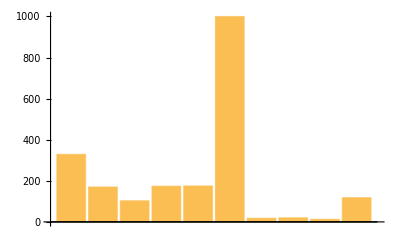

```mathematica
BarChart[%]
```

Find overlap of list of mathematicians names (should this be string list or entity matched list) and Wikipedia Biography Data

```mathematica
wikiMentions[names_]:= Intersection[WikipediaData[names,"LinksList"],Flatten[fullNames]]
```

```mathematica
Map[wikiMentions,wikiBioChecker]
```

{Albert Einstein,Alfred North Whitehead,Johannes Kepler,John Dee,Nicolaus Copernicus}

```mathematica
{}
```

{}

## String Length Function For Wiki Bios

## Mental Health Disorders List

```mathematica
mentalDisorders = Import["C:\\Users\\tanha\\OneDrive\\Documents\\GitHub\\Summer2018\\StudentDeliverables","List"]
```

Import::nodirsup: Cannot import directory C:\Users\tanha\OneDrive\Documents\GitHub\Summer2018\StudentDeliverables\ as LIST.

$Failed

```mathematica
expandedDisorders=Join[{"fatigue","dementia"},mentalDisorders];
```

Jofre????? how did he match with mcs bios? how to match with wiki bios?

```mathematica
mentalDisorderChecker[namesofm_]:=Intersection[WikipediaData[namesofm,"ArticlePlaintext"],expandedDisroders]
```

# Extracting Symbols

```mathematica
text=Import["https://en.wikipedia.org/wiki/Table_of_mathematical_symbols_by_introduction_date","Data"];
```

```mathematica
text // Length
```

3

```mathematica
SymbolTable=text[[1,1,2]]
```

{{ Symbol ,Name,Date of earliest use,First author to use},{ + ,plus sign,ca. 1360 (abbreviation for Latin et resembling the plus sign),Nicole Oresme},{ − ,minus sign,1489 (first appearance of minus sign, and also first appearance of plus sign in print),Johannes Widmann},{ √ ,radical symbol (for square root ),1525 (without the vinculum above the radicand ),Christoff Rudolff},{ (…) ,parentheses (for precedence grouping),1544 (in handwritten notes),Michael Stifel},{1556,Niccolò Tartaglia},{ = ,equals sign,1557,Robert Recorde},{ × ,multiplication sign,1618,William Oughtred},{ ± ,plus-minus sign,1628},{ ∷ ,proportion sign},{ n √ ,radical symbol (for n th root ),1629,Albert Girard},{ < > ,strict inequality signs ( less-than sign and greater-than sign ),1631,Thomas Harriot},{ x y ,superscript notation (for exponentiation ),1636 (using Roman numerals as superscripts),James Hume},{1637 (in the modern form),René Descartes},{ √ ̅ ,radical symbol (for square root ),1637 (with the vinculum above the radicand ),René Descartes},{ % ,percent sign,ca. 1650,unknown},{ ÷ ,division sign (a.k.a. obelus ),1659,Johann Rahn},{ ∞ ,infinity sign,1655,John Wallis},{ ≤ ≥ ,unstrict inequality signs ( less-than or equals to sign and greater-than or equals to sign ),1670 (with the horizontal bar over the inequality sign, rather than below it)},{1734 (with double horizontal bar below the inequality sign),Pierre Bouguer},{ d ,differential sign,1675,Gottfried Leibniz},{ ∫ ,integral sign},{ : ,colon (for division ),1684 (deriving from use of colon to denote fractions, dating back to 1633)},{ · ,middle dot (for multiplication ),1698 (perhaps deriving from a much earlier use of middle dot to separate juxtaposed numbers)},{ ⁄ ,division slash (a.k.a. solidus ),1718 (deriving from horizontal fraction bar, invented by Arabs in the 12th century),Thomas Twining},{ ≠ ,inequality sign ( not equal to ),unknown,Leonhard Euler},{ ∑ ,summation symbol,1755},{ ∝ ,proportionality sign,1768,William Emerson},{ ∂ ,partial differential sign (a.k.a. curly d or Jacobi 's delta ),1770,Marquis de Condorcet},{ x ′ ,prime symbol (for derivative ),Joseph Louis Lagrange},{ ≡ ,identity sign (for congruence relation ),1801 (first appearance in print; used previously in personal writings of Gauss),Carl Friedrich Gauss},{ [ x ] ,integral part (a.k.a. floor ),1808},{ ∏ ,product symbol,1812},{ ! ,factorial,1808,Christian Kramp},{ ⊂ ⊃ ,set inclusion signs ( subset of , superset of ),1817,Joseph Gergonne},{1890,Ernst Schröder},{ |…| ,absolute value notation,1841,Karl Weierstrass},{determinant of a matrix,Arthur Cayley},{ ‖…‖ ,matrix notation,1843 [1]},{ ∇ ,nabla symbol (for vector differential ),1846 (previously used by Hamilton as a general-purpose operator sign),William Rowan Hamilton},{ ∩ ∪ ,intersection union,1888,Giuseppe Peano},{ ∈ ,membership sign ( is an element of ),1894},{ ∃ ,existential quantifier ( there exists ),1897},{ ℵ ,aleph symbol (for transfinite cardinal numbers ),1893,Georg Cantor},{ {…} ,braces, a.k.a. curly brackets (for set notation),1895},{ ℕ ,Blackboard bold capital N (for natural numbers set),Giuseppe Peano},{ · ,middle dot (for dot product ),1902,J. Willard Gibbs},{ × ,multiplication sign (for cross product )},{ ∨ ,logical disjunction (a.k.a. OR ),1906,Bertrand Russell},{ (…) ,matrix notation,1909 [1],Maxime Bôcher},{ […] ,1909 [1],Gerhard Kowalewski},{ ∮ ,contour integral sign,1917,Arnold Sommerfeld},{ ℤ ,Blackboard bold capital Z (for integer numbers set),1930,Edmund Landau},{ ℚ ,Blackboard bold capital Q (for rational numbers set),1895,Giuseppe Peano},{ ∀ ,universal quantifier ( for all ),1935,Gerhard Gentzen},{ ∅ ,empty set sign,1939,André Weil / Nicolas Bourbaki [2]},{ ℂ ,Blackboard bold capital C (for complex numbers set),1939,Nathan Jacobson},{ → ,arrow (for function notation),1936 (to denote images of specific elements),Øystein Ore},{1940 (in the present form of f: X → Y),Witold Hurewicz},{ ∎ ,end of proof sign (a.k.a. tombstone ),1950 [3],Paul Halmos},{ ⌊ x ⌋ ⌈ x ⌉ ,greatest integer ≤ x (a.k.a. floor ) smallest integer ≥ x (a.k.a. ceiling ),1962 [4],Kenneth E. Iverson}}

```mathematica
SymbolTable//Map[Length,#]&
```

{4,4,4,4,4,2,4,4,3,2,4,4,4,2,4,4,4,4,3,2,4,2,3,3,4,4,3,4,4,3,4,3,3,4,4,2,4,2,3,4,4,3,3,4,3,3,4,2,4,4,3,4,4,4,4,4,4,4,2,4,4}

```mathematica
SymbolTable[[8;;11]]
```

{{ × ,multiplication sign,1618,William Oughtred},{ ± ,plus-minus sign,1628},{ ∷ ,proportion sign},{ n √ ,radical symbol (for n th root ),1629,Albert Girard}}

```mathematica
DeleteCases[text,{_,_,_,_},∞]
```

{{{This article contains Unicode mathematical symbols . Without proper rendering support , you may see question marks, boxes, or other symbols instead of mathematical symbols .,{{1556,Niccolò Tartaglia},{ ± ,plus-minus sign,1628},{ ∷ ,proportion sign},{1637 (in the modern form),René Descartes},{ ≤ ≥ ,unstrict inequality signs ( less-than or equals to sign and greater-than or equals to sign ),1670 (with the horizontal bar over the inequality sign, rather than below it)},{1734 (with double horizontal bar below the inequality sign),Pierre Bouguer},{ ∫ ,integral sign},{ : ,colon (for division ),1684 (deriving from use of colon to denote fractions, dating back to 1633)},{ · ,middle dot (for multiplication ),1698 (perhaps deriving from a much earlier use of middle dot to separate juxtaposed numbers)},{ ∑ ,summation symbol,1755},{ x ′ ,prime symbol (for derivative ),Joseph Louis Lagrange},{ [ x ] ,integral part (a.k.a. floor ),1808},{ ∏ ,product symbol,1812},{1890,Ernst Schröder},{determinant of a matrix,Arthur Cayley},{ ‖…‖ ,matrix notation,1843 [1]},{ ∈ ,membership sign ( is an element of ),1894},{ ∃ ,existential quantifier ( there exists ),1897},{ {…} ,braces, a.k.a. curly brackets (for set notation),1895},{ ℕ ,Blackboard bold capital N (for natural numbers set),Giuseppe Peano},{ × ,multiplication sign (for cross product )},{ […] ,1909 [1],Gerhard Kowalewski},{1940 (in the present form of f: X → Y),Witold Hurewicz}},{History of mathematical notation,History of the Hindu–Arabic numeral system,Table of mathematical symbols},Jeff Miller: Earliest Uses of Various Mathematical Symbols},{Use dmy dates from September 2010}},{{{Not logged in,Talk,Contributions,Create account,Log in},{Article,Talk},{Read,Edit,View history}},{{Main page,Contents,Featured content,Current events,Random article,Donate to Wikipedia,Wikipedia store},{Help,About Wikipedia,Community portal,Recent changes,Contact page},{What links here,Related changes,Upload file,Special pages,Permanent link,Page information,Wikidata item,Cite this page},{Create a book,Download as PDF,Printable version},{Emiliàn e rumagnòl,فارسی,Yorùbá}}},{{This page was last edited on 4 June 2018, at 09:31 (UTC) .,Text is available under the Creative Commons Attribution-ShareAlike License ; additional terms may apply. By using this site, you agree to the Terms of Use and Privacy Policy . Wikipedia® is a registered trademark of the Wikimedia Foundation, Inc. , a non-profit organization.},{Privacy policy,About Wikipedia,Disclaimers,Contact Wikipedia,Developers,Cookie statement,Mobile view},{ , }}}

```mathematica
table=Grid[Cases[text,{_,_,_,_},∞],Frame->All] (*multiple symbols not showing up in the grid*)
```

Symbol  | Name | Date of earliest use | First author to use
 +  | plus sign | ca. 1360 (abbreviation for Latin et resembling the plus sign) | Nicole Oresme
 −  | minus sign | 1489 (first appearance of minus sign, and also first appearance of plus sign in print) | Johannes Widmann
 √  | radical symbol (for square root ) | 1525 (without the vinculum above the radicand ) | Christoff Rudolff
 (…)  | parentheses (for precedence grouping) | 1544 (in handwritten notes) | Michael Stifel
 =  | equals sign | 1557 | Robert Recorde
 ×  | multiplication sign | 1618 | William Oughtred
 n √  | radical symbol (for n th root ) | 1629 | Albert Girard
 < >  | strict inequality signs ( less-than sign and greater-than sign ) | 1631 | Thomas Harriot
 x y  | superscript notation (for exponentiation ) | 1636 (using Roman numerals as superscripts) | James Hume
 √ ̅  | radical symbol (for square root ) | 1637 (with the vinculum above the radicand ) | René Descartes
 %  | percent sign | ca. 1650 | unknown
 ÷  | division sign (a.k.a. obelus ) | 1659 | Johann Rahn
 ∞  | infinity sign | 1655 | John Wallis
 d  | differential sign | 1675 | Gottfried Leibniz
 ⁄  | division slash (a.k.a. solidus ) | 1718 (deriving from horizontal fraction bar, invented by Arabs in the 12th century) | Thomas Twining
 ≠  | inequality sign ( not equal to ) | unknown | Leonhard Euler
 ∝  | proportionality sign | 1768 | William Emerson
 ∂  | partial differential sign (a.k.a. curly d or Jacobi 's delta ) | 1770 | Marquis de Condorcet
 ≡  | identity sign (for congruence relation ) | 1801 (first appearance in print; used previously in personal writings of Gauss) | Carl Friedrich Gauss
 !  | factorial | 1808 | Christian Kramp
 ⊂ ⊃  | set inclusion signs ( subset of , superset of ) | 1817 | Joseph Gergonne
 |…|  | absolute value notation | 1841 | Karl Weierstrass
 ∇  | nabla symbol (for vector differential ) | 1846 (previously used by Hamilton as a general-purpose operator sign) | William Rowan Hamilton
 ∩ ∪  | intersection union | 1888 | Giuseppe Peano
 ℵ  | aleph symbol (for transfinite cardinal numbers ) | 1893 | Georg Cantor
 ·  | middle dot (for dot product ) | 1902 | J. Willard Gibbs
 ∨  | logical disjunction (a.k.a. OR ) | 1906 | Bertrand Russell
 (…)  | matrix notation | 1909 [1] | Maxime Bôcher
 ∮  | contour integral sign | 1917 | Arnold Sommerfeld
 ℤ  | Blackboard bold capital Z (for integer numbers set) | 1930 | Edmund Landau
 ℚ  | Blackboard bold capital Q (for rational numbers set) | 1895 | Giuseppe Peano
 ∀  | universal quantifier ( for all ) | 1935 | Gerhard Gentzen
 ∅  | empty set sign | 1939 | André Weil / Nicolas Bourbaki [2]
 ℂ  | Blackboard bold capital C (for complex numbers set) | 1939 | Nathan Jacobson
 →  | arrow (for function notation) | 1936 (to denote images of specific elements) | Øystein Ore
 ∎  | end of proof sign (a.k.a. tombstone ) | 1950 [3] | Paul Halmos
 ⌊ x ⌋ ⌈ x ⌉  | greatest integer ≤ x (a.k.a. floor ) smallest integer ≥ x (a.k.a. ceiling ) | 1962 [4] | Kenneth E. Iverson
^ a b c "Earliest Uses of Symbols for Matrices and Vectors" . jeff560.tripod.com . Retrieved 18 December 2016 . | ^ Weil, André (1992), The Apprenticeship of a Mathematician , Springer, p. 114, ISBN 9783764326500 . | ^ Halmos, Paul (1950). Measure Theory . New York: Van Nostrand. pp. vi. The symbol ∎ is used throughout the entire book in place of such phrases as "Q.E.D." or "This completes the proof of the theorem" to signal the end of a proof. | ^ Kenneth E. Iverson (1962), A Programming Language , Wiley , retrieved 20 April 2016
Mathematical notation | Mathematics-related lists | Mathematical symbols | Mathematics timelines

List of Locations (if discrepancy in birth and death location, I chose the location of their institution)

```mathematica
MapThread[Insert,{a,column,Table[2,{Length[column]}]}]
```